```mathematica
(* Search terms for genomics *)featureList={"autosomal", "gen","mutat","gene-modified","germ","positive","negative","mutant", "mutation-associated", "sequenc","familial","insertion", "deletion","transposition", "dna", "exome", "haplotype","intron","linkage","allele", "polymorphism","rflp", "snp", "variant","homozygous","heterozygous"};

allTitles=Import[FileNameJoin[{NotebookDirectory[],"titles_FOR.txt"}],"Lines"];

binaryNamespaceFeaturesAllTitles=ParallelTable[If[StringContainsQ[allTitles[[title]],featureList[[feature]],IgnoreCase->True],1,0],{title,Length[allTitles]},{feature,Length[featureList]}];
```

```mathematica
visualizeTSNE[reducedData_,classifier_,label_]:=Module[{K,allClusters,reducedAllCluster,reducedAllClusterCenters,listPlotData,coreColors,otherColorsCount,classes,mrkCC,mrkCP,legend,markers},

(* This classifies the data into clusters given the classifier. *)
K=Length[ClassifierInformation[classifier,"Classes"]];(*Print[K];*)
listPlotData=GatherBy[reducedData,classifier];

classes=ClassifierInformation[classifier,"Classes"];
coreColors={RGBColor[0.16,0.5,0.83],RGBColor[0.94,0.43,0.32],RGBColor[0.5,0.79,0.5],RGBColor[1,0.82,0.41],RGBColor[0.6,0,0.13]};
If[K<Length[coreColors],
coreColors=coreColors[[;;Abs[K]]];
];
otherColorsCount=K-Length[coreColors];
legendColors=coreColors;
If[otherColorsCount≠0,
AppendTo[legendColors,#]&/@RandomColor[otherColorsCount]
];

mrkCC=MapThread[Graphics[{#1,Style[Text[ToString[#2]],20,Bold]}]&,{legendColors,classes}];
mrkCP=MapThread[Graphics[{#,Disk[{0,0},ImageScaled[0.011]]}]&,{legendColors}];
legend=SwatchLegend[legendColors,classes,LegendMarkerSize->20];
markers=mrkCP;
AppendTo[markers,#]&/@mrkCC;
Return[ListPlot[listPlotData,PlotRange->All,ImageSize->800,AxesLabel->Automatic,PlotMarkers->markers,PlotLegends->legend,PlotLabel->label,LabelStyle->"Subsubsection",AspectRatio->1]];
]
```

```mathematica
titles=Import[SystemDialogInput["FileOpen"], "Lines"];
```

```mathematica
terms=Flatten[StringTrim[StringSplit[#,{" ",",",".","/"}]]&/@titles];
terms0=WordStem[ToLowerCase[#]]&/@terms;
terms1=Tally[DeleteStopwords[terms0]];
termOrd=Sort[terms1,#1[[2]]>#2[[2]]&];
termOrd1=ParallelTable[Flatten[{i,termOrd[[i]]}],{i,Length[termOrd]}];
Pane[Grid[termOrd1, Alignment->{{Left, Left,Right}, Automatic}],ImageSize->{400,300}, Scrollbars->True]
```

1 | gene | 8984
2 | cell | 4678
3 | genet | 4167
4 | express | 4149
5 | human | 3842
6 | dna | 3660
7 | genom | 3376
8 | analysi | 2855
9 | associ | 2828
10 | transcript | 2718
11 | regul | 2663
12 | sequenc | 2642
13 | protein | 2401
14 | rna | 2026
15 | function | 1962
16 | studi | 1875
17 | chromosom | 1768
18 | mutat | 1719
19 | evolut | 1615
20 | drosophila | 1613
21 | activ | 1501
22 | factor | 1484
23 | develop | 1465
24 | molecular | 1351
25 | reveal | 1336
26 | diseas | 1324
27 | popul | 1292
28 | structur | 1254
29 | identifi | 1236
30 | mous | 1200
31 | genome-wid | 1193
32 | variant | 1185
33 | differenti | 1128
34 | dure | 1127
35 | novel | 1122
36 | signal | 1110
37 | control | 1103
38 | cancer | 1091
39 | complex | 1088
40 | role | 1088
41 | variat | 1047
42 | model | 1044
43 | stem | 1043
44 | promot | 981
45 | effect | 970
46 | identif | 965
47 | respons | 957
48 | select | 954
49 | character | 946
50 | map | 914
51 | new | 890
52 | interact | 887
53 | ar | 877
54 | region | 873
55 | pathwai | 873
56 | requir | 871
57 | data | 853
58 | loci | 834
59 | famili | 796
60 | risk | 787
61 | target | 785
62 | mechan | 778
63 | coli | 776
64 | system | 770
65 | receptor | 760
66 | pattern | 749
67 | regulatori | 737
68 | yeast | 723
69 | escherichia | 712
70 | type | 709
71 | phenotyp | 708
72 | multipl | 689
73 | divers | 689
74 | specif | 676
75 | disord | 668
76 | speci | 656
77 | syndrom | 649
78 | locu | 643
79 | polymorph | 640
80 | integr | 640
81 | induc | 639
82 | bind | 634
83 | evolutionari | 631
84 | profil | 630
85 | element | 624
86 | network | 616
87 | evid | 605
88 | mice | 604
89 | 1 | 593
90 | mrna | 588
91 | recombin | 572
92 | methyl | 569
93 | mitochondri | 561
94 | nuclear | 556
95 | encod | 555
96 | growth | 549
97 | implic | 548
98 | development | 542
99 | polymeras | 541
100 | differ | 541
101 | replic | 540
102 | chromatin | 539
103 | 2 | 537
104 | approach | 535
105 | enhanc | 532
106 | site | 528
107 | repair | 525
108 | conserv | 522
109 | mammalian | 514
110 | isol | 509
111 | caus | 505
112 | detect | 502
113 | mutant | 498
114 | viru | 495
115 | clone | 492
116 | earli | 492
117 | hybrid | 490
118 | embryon | 484
119 | mediat | 475
120 | dynam | 471
121 | determin | 469
122 | gener | 468
123 | origin | 466
124 | zebrafish | 459
125 | adapt | 454
126 | elegan | 450
127 | histon | 450
128 | transcriptom | 450
129 | chang | 445
130 | patient | 443
131 | saccharomyc | 438
132 | epigenet | 438
133 | acid | 437
134 | organ | 436
135 | clinic | 433
136 | suscept | 429
137 | modul | 429
138 | common | 427
139 | tumor | 425
140 | ii | 424
141 | alter | 424
142 | homolog | 419
143 | resist | 418
144 | cerevisia | 417
145 | ag | 416
146 | base | 415
147 | predict | 415
148 | linkag | 413
149 | trait | 413
150 | splice | 412
151 | local | 411
152 | singl | 408
153 | format | 405
154 | via | 405
155 | distinct | 404
156 | essenti | 403
157 | test | 402
158 | stress | 401
159 | neuron | 400
160 | method | 394
161 | compar | 392
162 | allel | 391
163 | c | 391
164 | level | 379
165 | involv | 378
166 | screen | 377
167 | tissu | 370
168 | kinas | 367
169 | metabol | 365
170 | link | 363
171 | melanogast | 362
172 | insight | 358
173 | domain | 357
174 | inhibit | 357
175 | synthesi | 354
176 | phylogenet | 353
177 | brain | 352
178 | affect | 352
179 | natur | 348
180 | vivo | 348
181 | delet | 347
182 | nucleotid | 346
183 | embryo | 346
184 | microarrai | 345
185 | direct | 340
186 | process | 335
187 | vitro | 332
188 | bacteri | 332
189 | muscl | 330
190 | global | 330
191 | small | 330
192 | applic | 329
193 | diverg | 326
194 | increas | 326
195 | cellular | 326
196 | major | 325
197 | microrna | 321
198 | pluripot | 321
199 | influenc | 320
200 | product | 319
201 | class | 319
202 | relat | 319
203 | translat | 319
204 | behavior | 317
205 | somat | 316
206 | lineag | 315
207 | chapter | 313
208 | repeat | 312
209 | effici | 311
210 | adult | 309
211 | analys | 308
212 | plant | 307
213 | potenti | 303
214 | defect | 303
215 | b | 302
216 | marker | 301
217 | biologi | 299
218 | initi | 299
219 | cycl | 297
220 | arabidopsi | 296
221 | repress | 295
222 | relationship | 291
223 | genotyp | 290
224 | comparison | 290
225 | depend | 289
226 | sex | 289
227 | individu | 288
228 | murin | 285
229 | rare | 285
230 | number | 284
231 | single-cel | 279
232 | larg | 278
233 | heterogen | 277
234 | infer | 277
235 | correl | 275
236 | loss | 274
237 | contribut | 273
238 | ribosom | 272
239 | immun | 271
240 | male | 270
241 | group | 270
242 | histori | 268
243 | rat | 267
244 | posit | 267
245 | african | 267
246 | cluster | 264
247 | blood | 264
248 | program | 263
249 | line | 262
250 | rapid | 262
251 | size | 262
252 | discoveri | 261
253 | phylogeni | 259
254 | quantit | 259
255 | improv | 258
256 | diabet | 258
257 | infect | 258
258 | host | 257
259 | rate | 257
260 | t | 255
261 | morpholog | 254
262 | progenitor | 251
263 | candid | 249
264 | damag | 249
265 | schizophrenia | 248
266 | caenorhabd | 248
267 | meta-analysi | 248
268 | transform | 247
269 | bacteriophag | 247
270 | strain | 244
271 | progress | 243
272 | high | 242
273 | compon | 241
274 | impact | 240
275 | primari | 239
276 | neural | 238
277 | 3 | 236
278 | induct | 236
279 | long | 236
280 | x | 236
281 | haplotyp | 235
282 | landscap | 235
283 | subunit | 234
284 | normal | 234
285 | edit | 233
286 | vector | 232
287 | vertebr | 231
288 | stabil | 231
289 | assess | 231
290 | cultur | 230
291 | distribut | 228
292 | breast | 228
293 | signatur | 228
294 | pathogen | 227
295 | altern | 225
296 | basi | 225
297 | lung | 225
298 | research | 224
299 | transgen | 223
300 | endotheli | 222
301 | sampl | 222
302 | defin | 222
303 | code | 221
304 | architectur | 221
305 | carcinoma | 220
306 | transfer | 220
307 | sexual | 219
308 | heart | 219
309 | copi | 218
310 | eukaryot | 218
311 | american | 217
312 | independ | 216
313 | suppress | 216
314 | assembl | 215
315 | noncod | 214
316 | hematopoiet | 213
317 | leukemia | 212
318 | bone | 212
319 | reproduct | 212
320 | modif | 211
321 | case | 211
322 | biolog | 209
323 | form | 209
324 | featur | 208
325 | result | 207
326 | time | 207
327 | variabl | 206
328 | autism | 206
329 | oxid | 203
330 | chain | 202
331 | highli | 202
332 | de | 202
333 | contain | 199
334 | silenc | 197
335 | drive | 196
336 | report | 195
337 | estim | 195
338 | maiz | 194
339 | arrai | 194
340 | state | 193
341 | systemat | 193
342 | alcohol | 192
343 | spectrum | 192
344 | life | 190
345 | bacillu | 189
346 | surviv | 189
347 | meiotic | 188
348 | plasmid | 188
349 | inform | 188
350 | defici | 186
351 | cardiac | 185
352 | bodi | 184
353 | kidnei | 184
354 | set | 183
355 | high-throughput | 183
356 | environment | 183
357 | evalu | 183
358 | deriv | 182
359 | inherit | 181
360 | snp | 180
361 | disrupt | 180
362 | provid | 178
363 | strategi | 177
364 | duplic | 176
365 | novo | 176
366 | tool | 175
367 | modifi | 174
368 | fate | 174
369 | reduc | 174
370 | reprogram | 174
371 | measur | 174
372 | cdna | 173
373 | share | 173
374 | enzym | 173
375 | subtili | 172
376 | mutagenesi | 171
377 | intron | 171
378 | prolifer | 170
379 | crispr | 170
380 | sensit | 170
381 | critic | 169
382 | large-scal | 169
383 | spatial | 168
384 | termin | 168
385 | molecul | 168
386 | operon | 166
387 | epitheli | 166
388 | revers | 166
389 | pair | 165
390 | drug | 165
391 | engin | 165
392 | skelet | 165
393 | lymphoma | 164
394 | viral | 164
395 | bacteria | 164
396 | vascular | 164
397 | rearrang | 163
398 | transport | 163
399 | chronic | 163
400 | notch | 162
401 | congenit | 162
402 | design | 162
403 | commun | 161
404 | comprehens | 161
405 | e | 160
406 | restrict | 160
407 | segment | 159
408 | emerg | 159
409 | underli | 159
410 | acut | 158
411 | probe | 158
412 | ovarian | 156
413 | 5 | 156
414 | germ | 156
415 | parasit | 155
416 | femal | 155
417 | ecolog | 155
418 | domin | 154
419 | fish | 154
420 | environ | 153
421 | 4 | 153
422 | ancient | 153
423 | combin | 153
424 | light | 153
425 | frequenc | 152
426 | migrat | 152
427 | antigen | 151
428 | insert | 151
429 | limb | 151
430 | transit | 151
431 | anim | 151
432 | amplif | 151
433 | whole-genom | 151
434 | diagnosi | 150
435 | tempor | 149
436 | annot | 149
437 | germlin | 149
438 | import | 149
439 | neg | 149
440 | therapi | 148
441 | lead | 148
442 | inhibitor | 148
443 | coordin | 148
444 | assai | 148
445 | proteom | 147
446 | suppressor | 147
447 | understand | 147
448 | follow | 147
449 | statist | 146
450 | extens | 146
451 | fibroblast | 146
452 | recent | 146
453 | physic | 146
454 | herit | 145
455 | ident | 145
456 | mainten | 145
457 | support | 145
458 | hormon | 144
459 | xenopu | 143
460 | switch | 143
461 | phage | 143
462 | shape | 143
463 | sever | 143
464 | parallel | 142
465 | ancestri | 142
466 | exom | 141
467 | t7 | 140
468 | dissect | 140
469 | bipolar | 140
470 | review | 138
471 | retin | 138
472 | fit | 138
473 | chines | 137
474 | wnt | 137
475 | european | 137
476 | diversif | 137
477 | construct | 136
478 | dystrophi | 136
479 | enrich | 136
480 | end | 135
481 | imag | 135
482 | exposur | 135
483 | suggest | 135
484 | tree | 135
485 | alpha | 133
486 | morphogenesi | 133
487 | enabl | 133
488 | recognit | 133
489 | properti | 133
490 | d | 133
491 | fragment | 132
492 | p53 | 132
493 | social | 132
494 | evolv | 132
495 | matern | 131
496 | resourc | 131
497 | short | 131
498 | plasmodium | 131
499 | depress | 130
500 | s | 130
501 | liver | 130
502 | librari | 129
503 | locat | 129
504 | remodel | 128
505 | read | 127
506 | matur | 127
507 | limit | 127
508 | genu | 127
509 | rna-seq | 127
510 | break | 127
511 | peptid | 126
512 | databas | 126
513 | mate | 126
514 | microsatellit | 125
515 | situ | 124
516 | interfer | 124
517 | complet | 124
518 | experiment | 124
519 | resolut | 124
520 | member | 123
521 | cooper | 123
522 | primat | 123
523 | imprint | 123
524 | rnai | 123
525 | comput | 123
526 | segreg | 122
527 | instabl | 122
528 | fetal | 122
529 | radiat | 122
530 | chemic | 122
531 | perspect | 122
532 | regener | 121
533 | isoform | 120
534 | challeng | 120
535 | condit | 120
536 | autosom | 120
537 | motif | 120
538 | fusion | 120
539 | telomer | 119
540 | prostat | 119
541 | abnorm | 119
542 | gwa | 119
543 | exon | 118
544 | codon | 118
545 | arteri | 118
546 | learn | 118
547 | epidemiolog | 118
548 | melanoma | 118
549 | skin | 117
550 | uniqu | 117
551 | lymphocyt | 117
552 | robust | 117
553 | protect | 117
554 | multiplex | 117
555 | oncogen | 116
556 | scan | 116
557 | expans | 116
558 | polygen | 116
559 | treatment | 116
560 | lack | 115
561 | amino | 115
562 | biosynthesi | 115
563 | intestin | 115
564 | dehydrogenas | 115
565 | project | 115
566 | butterfli | 115
567 | central | 115
568 | synthet | 115
569 | signific | 114
570 | plastic | 114
571 | strand | 114
572 | phosphoryl | 114
573 | speciat | 114
574 | cohort | 114
575 | health | 114
576 | malaria | 114
577 | hedgehog | 113
578 | stimul | 113
579 | mhc | 112
580 | physiolog | 112
581 | framework | 112
582 | investig | 111
583 | chloroplast | 111
584 | nich | 111
585 | psychiatr | 111
586 | event | 111
587 | oligonucleotid | 110
588 | microbi | 110
589 | hereditari | 109
590 | hla | 109
591 | repressor | 109
592 | virul | 109
593 | converg | 109
594 | kei | 109
595 | deep | 109
596 | visual | 109
597 | transloc | 108
598 | secondari | 108
599 | non-cod | 108
600 | advanc | 108
601 | inactiv | 108
602 | consortium | 108
603 | precursor | 107
604 | trna | 107
605 | similar | 107
606 | impair | 107
607 | expand | 107
608 | reconstruct | 107
609 | double-strand | 107
610 | util | 106
611 | endogen | 106
612 | zinc | 105
613 | elong | 105
614 | pseudomona | 105
615 | transpos | 105
616 | widespread | 105
617 | coupl | 105
618 | macrophag | 104
619 | falciparum | 104
620 | establish | 103
621 | technolog | 103
622 | next-gener | 103
623 | flow | 102
624 | island | 102
625 | length | 102
626 | cognit | 102
627 | mass | 102
628 | action | 102
629 | excis | 101
630 | assign | 101
631 | theori | 101
632 | optim | 101
633 | refer | 101
634 | aberr | 101
635 | iii | 100
636 | channel | 100
637 | transposon | 100
638 | phase | 100
639 | cas9 | 100
640 | scale | 100
641 | renal | 100
642 | marin | 99
643 | divis | 99
644 | immunoglobulin | 99
645 | biochem | 99
646 | recurr | 99
647 | confer | 99
648 | mosaic | 99
649 | composit | 99
650 | vibrio | 99
651 | cleavag | 99
652 | classif | 99
653 | experi | 99
654 | neurospora | 98
655 | power | 98
656 | tissue-specif | 98
657 | transmiss | 98
658 | therapeut | 98
659 | doe | 98
660 | insect | 98
661 | messeng | 97
662 | act | 97
663 | invas | 97
664 | y | 97
665 | cytoplasm | 97
666 | p | 97
667 | finger | 97
668 | person | 97
669 | sea | 96
670 | 16 | 96
671 | myeloid | 96
672 | produc | 96
673 | futur | 96
674 | biomark | 96
675 | facilit | 96
676 | genome-wide | 96
677 | prevent | 96
678 | hox | 96
679 | explor | 96
680 | stage | 95
681 | stabl | 95
682 | women | 95
683 | asthma | 95
684 | coronari | 95
685 | intern | 95
686 | smooth | 94
687 | unit | 94
688 | consequ | 94
689 | admixtur | 94
690 | antibiot | 94
691 | pulmonari | 94
692 | pancreat | 94
693 | streptococcu | 93
694 | helicas | 93
695 | muscular | 93
696 | complement | 93
697 | platform | 93
698 | core | 93
699 | malign | 93
700 | axon | 92
701 | basal | 92
702 | mai | 92
703 | north | 92
704 | abund | 92
705 | histocompat | 91
706 | maintain | 91
707 | includ | 91
708 | pathogenesi | 91
709 | cholera | 90
710 | simplex | 90
711 | degrad | 90
712 | lethal | 90
713 | axi | 90
714 | subtyp | 90
715 | outcom | 90
716 | tuberculosi | 90
717 | homeostasi | 90
718 | membran | 89
719 | precis | 89
720 | rnase | 89
721 | bud | 89
722 | pressur | 89
723 | methyltransferas | 89
724 | captur | 89
725 | circadian | 89
726 | gut | 88
727 | inflammatori | 88
728 | dispers | 88
729 | polar | 88
730 | cells: | 87
731 | cortic | 87
732 | herp | 87
733 | mammal | 87
734 | mycobacterium | 87
735 | purif | 86
736 | access | 86
737 | low | 86
738 | synthas | 85
739 | long-term | 85
740 | high-resolut | 85
741 | † | 84
742 | densiti | 84
743 | fluoresc | 84
744 | ant | 84
745 | apoptosi | 84
746 | 6 | 84
747 | homeobox | 83
748 | pcr | 83
749 | overexpress | 83
750 | spontan | 83
751 | disequilibrium | 83
752 | partial | 83
753 | aeruginosa | 83
754 | absenc | 83
755 | wolbachia | 83
756 | clonal | 83
757 | ha | 82
758 | tyrosin | 82
759 | valid | 82
760 | nativ | 82
761 | recruit | 82
762 | separ | 82
763 | medicin | 82
764 | microbiom | 82
765 | 3′ | 82
766 | connect | 82
767 | convers | 81
768 | disease: | 81
769 | nervou | 81
770 | meiosi | 81
771 | epigenom | 81
772 | nucleosom | 81
773 | rrna | 80
774 | 7 | 80
775 | salmonella | 80
776 | memori | 80
777 | peripher | 80
778 | embryogenesi | 80
779 | gland | 80
780 | patholog | 80
781 | vitamin | 80
782 | insulin | 80
783 | oral | 80
784 | sleep | 80
785 | transduct | 79
786 | endonucleas | 79
787 | search | 79
788 | trypanosoma | 79
789 | possibl | 79
790 | constraint | 79
791 | 10 | 79
792 | olfactori | 79
793 | pigment | 79
794 | gene: | 79
795 | longev | 79
796 | bia | 79
797 | sourc | 79
798 | overlap | 79
799 | tetrahymena | 78
800 | substitut | 78
801 | persist | 78
802 | surfac | 78
803 | nucleas | 78
804 | block | 78
805 | diagnost | 78
806 | nucleic | 78
807 | point | 78
808 | score | 78
809 | cardiomyopathi | 78
810 | rel | 78
811 | serum | 78
812 | characterist | 78
813 | correct | 78
814 | simpl | 78
815 | urchin | 77
816 | tryptophan | 77
817 | upstream | 77
818 | reaction | 77
819 | dna-bind | 77
820 | mitot | 77
821 | beta | 77
822 | wide | 77
823 | colon | 77
824 | recess | 77
825 | accur | 77
826 | cardiovascular | 77
827 | accumul | 77
828 | close | 76
829 | monkei | 76
830 | matrix | 76
831 | extend | 76
832 | live | 76
833 | asymmetri | 76
834 | loop | 76
835 | white | 76
836 | open | 76
837 | current | 76
838 | birth | 76
839 | mark | 76
840 | toler | 76
841 | self-renew | 75
842 | colorect | 75
843 | wild | 75
844 | phylogenom | 75
845 | interpret | 75
846 | hematopoiesi | 75
847 | five | 75
848 | fast | 75
849 | streptomyc | 74
850 | tandem | 74
851 | lizard | 74
852 | joint | 74
853 | topoisomeras | 74
854 | special | 74
855 | heat | 74
856 | addit | 74
857 | guid | 74
858 | random | 74
859 | fly | 74
860 | sclerosi | 74
861 | degener | 74
862 | death | 74
863 | proxim | 73
864 | symbiont | 73
865 | epstein-barr | 73
866 | statu | 73
867 | hair | 73
868 | bayesian | 73
869 | : | 72
870 | unusu | 72
871 | versu | 72
872 | uncov | 72
873 | toxic | 72
874 | smoke | 72
875 | due | 72
876 | l | 72
877 | acceler | 72
878 | cryptic | 72
879 | site-specif | 72
880 | collagen | 71
881 | extrem | 71
882 | techniqu | 71
883 | twin | 71
884 | late | 71
885 | – | 71
886 | replac | 71
887 | indic | 71
888 | anophel | 71
889 | cortex | 71
890 | circuit | 71
891 | onset | 71
892 | virus | 70
893 | satellit | 70
894 | analyz | 70
895 | mesenchym | 70
896 | balanc | 70
897 | dopamin | 70
898 | rang | 70
899 | meliloti | 69
900 | thaliana | 69
901 | 11 | 69
902 | kinet | 69
903 | step | 69
904 | h3 | 69
905 | single-strand | 69
906 | avian | 69
907 | perform | 69
908 | relev | 69
909 | geograph | 69
910 | heavi | 68
911 | decai | 68
912 | cis-regulatori | 68
913 | diffus | 68
914 | causal | 68
915 | digit | 68
916 | 12 | 68
917 | ey | 68
918 | exchang | 68
919 | present | 68
920 | lipid | 68
921 | riboswitch | 67
922 | transfect | 67
923 | erythroid | 67
924 | leishmania | 67
925 | sp | 67
926 | synthetas | 67
927 | context | 67
928 | reduct | 67
929 | lesson | 67
930 | checkpoint | 67
931 | pool | 67
932 | clock | 67
933 | mani | 67
934 | cerebr | 67
935 | caulobact | 66
936 | lambda | 66
937 | pseudogen | 66
938 | chimpanze | 66
939 | cytogenet | 66
940 | downstream | 66
941 | transplant | 66
942 | parent | 66
943 | content | 66
944 | subject | 66
945 | retina | 66
946 | decreas | 66
947 | floral | 66
948 | prefer | 66
949 | hepat | 66
950 | seed | 66
951 | childhood | 66
952 | nov | 65
953 | antibodi | 65
954 | candida | 65
955 | junction | 65
956 | autoimmun | 65
957 | interferon | 65
958 | lysin | 65
959 | ancestr | 65
960 | ratio | 65
961 | near | 65
962 | obes | 65
963 | fli | 65
964 | dosag | 65
965 | distinguish | 65
966 | continu | 65
967 | lncrna | 65
968 | wing | 65
969 | t-cell | 65
970 | nasonia | 64
971 | homologu | 64
972 | secret | 64
973 | actin | 64
974 | transcrib | 64
975 | occur | 64
976 | polycomb | 64
977 | tract | 64
978 | reductas | 64
979 | substrat | 64
980 | choic | 64
981 | index | 64
982 | distal | 64
983 | effector | 63
984 | fragil | 63
985 | asymmetr | 63
986 | epiderm | 63
987 | genes: | 63
988 | world | 63
989 | age-rel | 63
990 | resolv | 63
991 | competit | 63
992 | hypoxia | 63
993 | branch | 63
994 | disabl | 63
995 | papillomaviru | 62
996 | β | 62
997 | laboratori | 62
998 | plasma | 62
999 | topolog | 62
1000 | prenat | 62
1001 | presenc | 62
1002 | centromer | 62
1003 | displai | 62
1004 | barcod | 62
1005 | algorithm | 62
1006 | delai | 62
1007 | fibrosi | 62
1008 | linear | 62
1009 | view | 62
1010 | glucos | 62
1011 | λ | 61
1012 | nation | 61
1013 | color | 61
1014 | mtdna | 61
1015 | pleiotrop | 61
1016 | intermedi | 61
1017 | weight | 61
1018 | estrogen | 61
1019 | beyond | 61
1020 | 5′ | 61
1021 | qualiti | 61
1022 | massiv | 61
1023 | elev | 61
1024 | cyclic | 60
1025 | box | 60
1026 | brucei | 60
1027 | innat | 60
1028 | 9 | 60
1029 | extract | 60
1030 | mismatch | 60
1031 | error | 60
1032 | modern | 60
1033 | antisens | 60
1034 | nucleu | 60
1035 | work | 60
1036 | biogeographi | 60
1037 | malform | 60
1038 | incorpor | 60
1039 | chorion | 59
1040 | transient | 59
1041 | intracellular | 59
1042 | panel | 59
1043 | dysfunct | 59
1044 | mesoderm | 59
1045 | practic | 59
1046 | alzheimer' | 59
1047 | dysregul | 59
1048 | ligand | 59
1049 | x-link | 59
1050 | bioinformat | 59
1051 | adenocarcinoma | 59
1052 | children | 59
1053 | 000 | 59
1054 | higher | 59
1055 | epistasi | 59
1056 | glioma | 59
1057 | myosin | 58
1058 | definit | 58
1059 | mode | 58
1060 | year | 58
1061 | residu | 58
1062 | field | 58
1063 | directli | 58
1064 | affin | 58
1065 | survei | 58
1066 | bird | 58
1067 | heterochromatin | 58
1068 | head | 58
1069 | collect | 58
1070 | diploid | 58
1071 | fold | 58
1072 | yield | 58
1073 | hamster | 57
1074 | bmp | 57
1075 | conflict | 57
1076 | descript | 57
1077 | rice | 57
1078 | genome-scal | 57
1079 | incompat | 57
1080 | knockout | 57
1081 | deliveri | 57
1082 | highlight | 57
1083 | hear | 57
1084 | allele-specif | 57
1085 | mendelian | 57
1086 | evolutionarili | 57
1087 | agent | 57
1088 | injuri | 57
1089 | extracellular | 57
1090 | missens | 57
1091 | combinatori | 57
1092 | dataset | 57
1093 | tsets | 56
1094 | constitut | 56
1095 | dimer | 56
1096 | transactiv | 56
1097 | oocyt | 56
1098 | α | 56
1099 | later | 56
1100 | shock | 56
1101 | immunodefici | 56
1102 | quantifi | 56
1103 | mirna | 56
1104 | prospect | 56
1105 | repertoir | 56
1106 | frog | 56
1107 | period | 56
1108 | > | 55
1109 | tumorigenesi | 55
1110 | retrotransposon | 55
1111 | compens | 55
1112 | acetyl | 55
1113 | synapt | 55
1114 | transposit | 55
1115 | distanc | 55
1116 | compound | 55
1117 | histor | 55
1118 | demonstr | 55
1119 | ultraviolet | 54
1120 | preferenti | 54
1121 | charact | 54
1122 | necessari | 54
1123 | align | 54
1124 | 14 | 54
1125 | stochast | 54
1126 | second | 54
1127 | exhibit | 54
1128 | order | 54
1129 | shift | 54
1130 | pedigre | 54
1131 | subset | 54
1132 | priorit | 54
1133 | anemia | 54
1134 | larval | 54
1135 | contact | 54
1136 | coloni | 54
1137 | preimplant | 54
1138 | boundari | 54
1139 | polyadenyl | 54
1140 | sporul | 53
1141 | rdna | 53
1142 | arrest | 53
1143 | pre-mrna | 53
1144 | plai | 53
1145 | manipul | 53
1146 | endoderm | 53
1147 | typhimurium | 53
1148 | medic | 53
1149 | metagenom | 53
1150 | export | 53
1151 | pharmacogenom | 53
1152 | thyroid | 53
1153 | dimorph | 53
1154 | observ | 53
1155 | quantif | 53
1156 | driver | 53
1157 | temperatur | 53
1158 | entamoeba | 52
1159 | hypothesi | 52
1160 | commit | 52
1161 | manag | 52
1162 | principl | 52
1163 | gambia | 52
1164 | necrosi | 52
1165 | sperm | 52
1166 | six | 52
1167 | flower | 52
1168 | coalesc | 52
1169 | anomali | 52
1170 | strong | 52
1171 | mosquito | 52
1172 | neurodevelopment | 52
1173 | invers | 52
1174 | america | 52
1175 | intrins | 52
1176 | aspect | 51
1177 | repetit | 51
1178 | complementari | 51
1179 | hypertens | 51
1180 | doubl | 51
1181 | cytokin | 51
1182 | 21 | 51
1183 | sens | 51
1184 | fruit | 51
1185 | updat | 51
1186 | govern | 51
1187 | genomewid | 51
1188 | old | 51
1189 | leukocyt | 51
1190 | retino | 51
1191 | neonat | 51
1192 | prokaryot | 50
1193 | red | 50
1194 | calcium | 50
1195 | mental | 50
1196 | asian | 50
1197 | b-cell | 50
1198 | r | 50
1199 | 18 | 50
1200 | simul | 50
1201 | phylogeographi | 50
1202 | amplifi | 50
1203 | standard | 50
1204 | oxygen | 50
1205 | cancer: | 50
1206 | africa | 50
1207 | coral | 50
1208 | antagon | 50
1209 | epithelium | 50
1210 | imput | 50
1211 | giant | 50
1212 | modular | 50
1213 | polypeptid | 49
1214 | tag | 49
1215 | templat | 49
1216 | 15 | 49
1217 | chick | 49
1218 | albican | 49
1219 | aed | 49
1220 | feedback | 49
1221 | whole-exom | 49
1222 | cross | 49
1223 | 8 | 49
1224 | rhizobium | 49
1225 | concentr | 49
1226 | success | 49
1227 | dual | 49
1228 | acquisit | 49
1229 | univers | 49
1230 | staphylococcu | 49
1231 | failur | 49
1232 | south | 49
1233 | 13 | 49
1234 | artifici | 48
1235 | fission | 48
1236 | crassa | 48
1237 | pomb | 48
1238 | ) | 48
1239 | glucocorticoid | 48
1240 | preval | 48
1241 | packag | 48
1242 | mobil | 48
1243 | adenoviru | 48
1244 | squamou | 48
1245 | etiolog | 48
1246 | discov | 48
1247 | nf-κb | 48
1248 | longitudin | 48
1249 | attenu | 48
1250 | usag | 48
1251 | chimer | 48
1252 | scienc | 48
1253 | androgen | 48
1254 | hiv-1 | 48
1255 | r2 | 47
1256 | iv | 47
1257 | nicotin | 47
1258 | proteas | 47
1259 | nitric | 47
1260 | evolution: | 47
1261 | rhesu | 47
1262 | multilocu | 47
1263 | adipos | 47
1264 | chicken | 47
1265 | fungal | 47
1266 | green | 47
1267 | development: | 47
1268 | basic | 47
1269 | circul | 47
1270 | fertil | 47
1271 | confirm | 47
1272 | influenza | 47
1273 | introduct | 47
1274 | demethylas | 47
1275 | aggress | 47
1276 | obstruct | 47
1277 | grant | 46
1278 | globin | 46
1279 | adhes | 46
1280 | discrimin | 46
1281 | lymphoid | 46
1282 | make | 46
1283 | primer | 46
1284 | flank | 46
1285 | rodent | 46
1286 | breed | 46
1287 | reflect | 46
1288 | endometri | 46
1289 | herpesviru | 46
1290 | mix | 46
1291 | gradient | 46
1292 | glaucoma | 46
1293 | elucid | 46
1294 | problem | 46
1295 | miss | 46
1296 | perturb | 46
1297 | reactiv | 46
1298 | rescu | 46
1299 | patern | 46
1300 | stromal | 46
1301 | g | 46
1302 | machineri | 46
1303 | egg | 46
1304 | phosphatas | 45
1305 | schizosaccharomyc | 45
1306 | cis-act | 45
1307 | frequent | 45
1308 | 17 | 45
1309 | tourett | 45
1310 | refin | 45
1311 | myoton | 45
1312 | lower | 45
1313 | neutral | 45
1314 | thermal | 45
1315 | motor | 45
1316 | uterin | 45
1317 | biogenesi | 45
1318 | ovari | 45
1319 | interspecif | 45
1320 | tumour | 45
1321 | climat | 45
1322 | catalyt | 45
1323 | overview | 45
1324 | neurogenesi | 45
1325 | call | 45
1326 | inflamm | 45
1327 | allow | 45
1328 | conform | 45
1329 | specifi | 44
1330 | arm | 44
1331 | center | 44
1332 | karyotyp | 44
1333 | leader | 44
1334 | ortholog | 44
1335 | care | 44
1336 | dog | 44
1337 | explain | 44
1338 | chlamydomona | 44
1339 | placent | 44
1340 | sex-specif | 44
1341 | autom | 44
1342 | ipsc | 44
1343 | lesion | 44
1344 | craniofaci | 44
1345 | plastid | 44
1346 | alzheimer’s | 44
1347 | wasp | 44
1348 | intellectu | 44
1349 | recombinas | 44
1350 | simultan | 44
1351 | heme | 43
1352 | single-nucleotid | 43
1353 | partit | 43
1354 | (diptera: | 43
1355 | young | 43
1356 | lymphoblast | 43
1357 | tube | 43
1358 | ectop | 43
1359 | mutan | 43
1360 | public | 43
1361 | gap | 43
1362 | cpg | 43
1363 | morphogenet | 43
1364 | symptom | 43
1365 | mean | 43
1366 | aureu | 43
1367 | t4 | 43
1368 | issu | 43
1369 | stomat | 43
1370 | era | 43
1371 | healthi | 43
1372 | deacetylas | 43
1373 | appli | 43
1374 | palat | 42
1375 | retard | 42
1376 | disorders: | 42
1377 | suffici | 42
1378 | post-transcript | 42
1379 | regress | 42
1380 | creat | 42
1381 | serin | 42
1382 | fine | 42
1383 | domest | 42
1384 | circular | 42
1385 | examin | 42
1386 | concept | 42
1387 | photoreceptor | 42
1388 | worldwid | 42
1389 | oper | 42
1390 | east | 42
1391 | demograph | 42
1392 | simian | 42
1393 | lifespan | 42
1394 | homozyg | 42
1395 | knowledg | 42
1396 | opportun | 42
1397 | heterozyg | 42
1398 | tropic | 42
1399 | epigenome-wid | 42
1400 | machin | 42
1401 | thymidin | 41
1402 | cytochrom | 41
1403 | myxococcu | 41
1404 | germin | 41
1405 | fungi | 41
1406 | regulon | 41
1407 | asexu | 41
1408 | breakpoint | 41
1409 | summari | 41
1410 | flexibl | 41
1411 | serotonin | 41
1412 | cyclin | 41
1413 | syndrome: | 41
1414 | root | 41
1415 | dna: | 41
1416 | valu | 41
1417 | sensori | 41
1418 | dietari | 41
1419 | seven | 41
1420 | rna-bind | 41
1421 | pediatr | 41
1422 | osteoblast | 41
1423 | n | 41
1424 | anoli | 41
1425 | trigger | 41
1426 | movement | 41
1427 | minim | 41
1428 | intergen | 40
1429 | homeot | 40
1430 | helicobact | 40
1431 | analysis: | 40
1432 | forest | 40
1433 | optic | 40
1434 | sister | 40
1435 | acinetobact | 40
1436 | carbon | 40
1437 | truncat | 40
1438 | toxin | 40
1439 | family-bas | 40
1440 | sarcoma | 40
1441 | occup | 40
1442 | v | 40
1443 | monitor | 40
1444 | area | 40
1445 | multivari | 40
1446 | compet | 40
1447 | viabil | 40
1448 | crispr-cas9 | 40
1449 | taxonom | 40
1450 | biosynthet | 40
1451 | atla | 40
1452 | carrier | 40
1453 | electron | 40
1454 | known | 40
1455 | recoveri | 40
1456 | neoplasm | 40
1457 | varianc | 40
1458 | capac | 40
1459 | toxoplasma | 40
1460 | hemoglobin | 40
1461 | clade | 40
1462 | granul | 40
1463 | follicular | 40
1464 | hypermut | 39
1465 | hypoxia-induc | 39
1466 | glycoprotein | 39
1467 | hydroxylas | 39
1468 | antagonist | 39
1469 | homeodomain | 39
1470 | consider | 39
1471 | chip-seq | 39
1472 | remov | 39
1473 | β-catenin | 39
1474 | oxidas | 39
1475 | horizont | 39
1476 | inhibitori | 39
1477 | dendrit | 39
1478 | spinal | 39
1479 | aegypti | 39
1480 | energi | 39
1481 | fraction | 39
1482 | myocardi | 39
1483 | classic | 39
1484 | salivari | 39
1485 | vari | 39
1486 | respiratori | 39
1487 | prepar | 39
1488 | height | 39
1489 | protocol | 39
1490 | recogn | 39
1491 | ci | 39
1492 | juvenil | 39
1493 | southern | 39
1494 | m | 39
1495 | arthriti | 39
1496 | pregnanc | 39
1497 | particip | 39
1498 | behaviour | 39
1499 | fatti | 39
1500 | ribonucl | 38
1501 | histolytica | 38
1502 | coli: | 38
1503 | filament | 38
1504 | lymphat | 38
1505 | wa | 38
1506 | multigen | 38
1507 | crystal | 38
1508 | myoblast | 38
1509 | ? | 38
1510 | uv | 38
1511 | cutan | 38
1512 | exclus | 38
1513 | nodal | 38
1514 | start | 38
1515 | aortic | 38
1516 | introgress | 38
1517 | fine-map | 38
1518 | senesc | 38
1519 | rule | 38
1520 | releas | 38
1521 | empir | 38
1522 | educ | 38
1523 | account | 38
1524 | β-globin | 38
1525 | reproduc | 38
1526 | prime | 38
1527 | motil | 38
1528 | barrier | 38
1529 | brca1 | 38
1530 | galápagos | 37
1531 | newli | 37
1532 | cleft | 37
1533 | esophag | 37
1534 | keratinocyt | 37
1535 | mu | 37
1536 | mine | 37
1537 | mechanist | 37
1538 | defens | 37
1539 | expos | 37
1540 | mitochondria | 37
1541 | span | 37
1542 | long-rang | 37
1543 | bowel | 37
1544 | cichlid | 37
1545 | reciproc | 37
1546 | 3' | 37
1547 | restor | 37
1548 | methodolog | 37
1549 | record | 37
1550 | great | 37
1551 | volum | 37
1552 | track | 37
1553 | glossina | 36
1554 | thermophila | 36
1555 | cell-specif | 36
1556 | gel | 36
1557 | v(d)j | 36
1558 | bovin | 36
1559 | immunoprecipit | 36
1560 | biofilm | 36
1561 | redund | 36
1562 | down-regul | 36
1563 | men | 36
1564 | gastric | 36
1565 | y-chromosom | 36
1566 | ethnic | 36
1567 | sequenti | 36
1568 | accuraci | 36
1569 | parkinson' | 36
1570 | hierarchi | 36
1571 | polycyst | 36
1572 | deplet | 36
1573 | nuclei | 36
1574 | endocrin | 36
1575 | purifi | 36
1576 | marrow | 36
1577 | cerebellar | 36
1578 | neisseria | 36
1579 | sporad | 36
1580 | trajectori | 36
1581 | compart | 36
1582 | spread | 36
1583 | collabor | 36
1584 | pipelin | 36
1585 | tortois | 35
1586 | borrelia | 35
1587 | flagellar | 35
1588 | sirna | 35
1589 | sonic | 35
1590 | postnat | 35
1591 | gamma | 35
1592 | preliminari | 35
1593 | race | 35
1594 | zygot | 35
1595 | europ | 35
1596 | gain | 35
1597 | sibl | 35
1598 | abil | 35
1599 | sigma | 35
1600 | steroid | 35
1601 | high-dens | 35
1602 | downregul | 35
1603 | prognost | 35
1604 | forc | 35
1605 | neuropsychiatr | 35
1606 | pacif | 35
1607 | latent | 35
1608 | fat | 35
1609 | paralog | 35
1610 | mammari | 35
1611 | hepatocyt | 35
1612 | founder | 35
1613 | transcriptome-wid | 35
1614 | cilia | 35
1615 | spindl | 35
1616 | idiopath | 35
1617 | eastern | 35
1618 | meet | 35
1619 | biobank | 35
1620 | interplai | 35
1621 | spatiotempor | 35
1622 | transcriptas | 34
1623 | amphibian | 34
1624 | tile | 34
1625 | thi | 34
1626 | retinoblastoma | 34
1627 | paradigm | 34
1628 | ligas | 34
1629 | adjac | 34
1630 | beetl | 34
1631 | c-myc | 34
1632 | dysplasia | 34
1633 | hippocamp | 34
1634 | bladder | 34
1635 | tobacco | 34
1636 | crossov | 34
1637 | recommend | 34
1638 | lineage-specif | 34
1639 | ocular | 34
1640 | zone | 34
1641 | cascad | 34
1642 | testicular | 34
1643 | infant | 34
1644 | solut | 34
1645 | upregul | 34
1646 | 19 | 34
1647 | path | 34
1648 | canon | 34
1649 | aneuploidi | 34
1650 | carri | 34
1651 | ribozym | 34
1652 | consist | 34
1653 | japanes | 34
1654 | metazoan | 34
1655 | band | 33
1656 | electrophoresi | 33
1657 | expression: | 33
1658 | sp1 | 33
1659 | xanthu | 33
1660 | hypox | 33
1661 | macular | 33
1662 | nucleolar | 33
1663 | delta | 33
1664 | tail | 33
1665 | cross-link | 33
1666 | fluctuat | 33
1667 | ra | 33
1668 | macaqu | 33
1669 | transcription | 33
1670 | elimin | 33
1671 | neuroendocrin | 33
1672 | chondrocyt | 33
1673 | erythrocyt | 33
1674 | integrin | 33
1675 | california | 33
1676 | reca | 33
1677 | sodium | 33
1678 | demethyl | 33
1679 | trial | 33
1680 | illumin | 33
1681 | la | 33
1682 | discord | 33
1683 | 40 | 33
1684 | atrial | 33
1685 | placenta | 33
1686 | studies: | 33
1687 | epilepsi | 33
1688 | bacterium | 33
1689 | revisit | 33
1690 | consumpt | 33
1691 | cardiomyocyt | 33
1692 | snrna | 32
1693 | kir | 32
1694 | deoxyribonucl | 32
1695 | integras | 32
1696 | trophoblast | 32
1697 | primas | 32
1698 | pyrimidin | 32
1699 | pirna | 32
1700 | telomeras | 32
1701 | ring | 32
1702 | ribonucleoprotein | 32
1703 | piwi | 32
1704 | u2 | 32
1705 | h | 32
1706 | ( | 32
1707 | co-express | 32
1708 | heterolog | 32
1709 | extinct | 32
1710 | autonom | 32
1711 | populations: | 32
1712 | glioblastoma | 32
1713 | infecti | 32
1714 | myogen | 32
1715 | atyp | 32
1716 | uptak | 32
1717 | declin | 32
1718 | wild-typ | 32
1719 | dispens | 32
1720 | particl | 32
1721 | steril | 32
1722 | master | 32
1723 | conduct | 32
1724 | mapk | 32
1725 | pancrea | 32
1726 | past | 32
1727 | intraspecif | 32
1728 | untransl | 32
1729 | donor | 32
1730 | footprint | 32
1731 | paus | 32
1732 | facial | 32
1733 | coactiv | 32
1734 | u | 32
1735 | driven | 32
1736 | metastasi | 32
1737 | hypertroph | 32
1738 | pleiotropi | 32
1739 | fidel | 32
1740 | myogenesi | 32
1741 | burgdorferi | 31
1742 | crescentu | 31
1743 | supercoil | 31
1744 | h2a | 31
1745 | k | 31
1746 | parathyroid | 31
1747 | cap | 31
1748 | frame | 31
1749 | retrovir | 31
1750 | denatur | 31
1751 | angiogenesi | 31
1752 | ubiquitin | 31
1753 | glutam | 31
1754 | paramet | 31
1755 | pharmacogenet | 31
1756 | ear | 31
1757 | subgroup | 31
1758 | whale | 31
1759 | interfac | 31
1760 | data: | 31
1761 | total | 31
1762 | single-molecul | 31
1763 | eqtl | 31
1764 | unravel | 31
1765 | offspr | 31
1766 | matter | 31
1767 | cholesterol | 31
1768 | dorsal | 31
1769 | jnk | 31
1770 | inner | 31
1771 | taxonomi | 31
1772 | hispan | 31
1773 | endem | 31
1774 | loss-of-funct | 31
1775 | predictor | 31
1776 | preserv | 31
1777 | innov | 31
1778 | turnov | 31
1779 | orphan | 30
1780 | adh | 30
1781 | enzymat | 30
1782 | conjug | 30
1783 | synthes | 30
1784 | killer | 30
1785 | 5s | 30
1786 | laevi | 30
1787 | synergist | 30
1788 | deciph | 30
1789 | facioscapulohumer | 30
1790 | cytomegaloviru | 30
1791 | copy-numb | 30
1792 | indian | 30
1793 | newborn | 30
1794 | cystic | 30
1795 | genomics: | 30
1796 | versatil | 30
1797 | endosymbiont | 30
1798 | protein-cod | 30
1799 | patch | 30
1800 | child | 30
1801 | pervas | 30
1802 | delin | 30
1803 | draft | 30
1804 | aneurysm | 30
1805 | trace | 30
1806 | gondii | 30
1807 | rapidli | 30
1808 | mutual | 30
1809 | contrast | 30
1810 | trp | 29
1811 | temperature-sensit | 29
1812 | 22 | 29
1813 | apolipoprotein | 29
1814 | dose | 29
1815 | adenosin | 29
1816 | ontolog | 29
1817 | potent | 29
1818 | synapsi | 29
1819 | coelicolor | 29
1820 | cytotox | 29
1821 | ethic | 29
1822 | resequenc | 29
1823 | intrachromosom | 29
1824 | background | 29
1825 | ion | 29
1826 | retent | 29
1827 | sweep | 29
1828 | charg | 29
1829 | substanc | 29
1830 | circuitri | 29
1831 | moder | 29
1832 | miner | 29
1833 | alzheim | 29
1834 | join | 29
1835 | guidelin | 29
1836 | displac | 29
1837 | bee | 29
1838 | need | 29
1839 | cost | 29
1840 | prognosi | 29
1841 | hierarch | 29
1842 | epistat | 29
1843 | fork | 29
1844 | mortal | 29
1845 | swi | 29
1846 | drift | 29
1847 | interrog | 29
1848 | analyt | 29
1849 | fungu | 29
1850 | procedur | 29
1851 | dilat | 29
1852 | frameshift | 29
1853 | silico | 29
1854 | inact | 29
1855 | genome: | 29
1856 | iron | 29
1857 | spp | 29
1858 | fossil | 29
1859 | neotrop | 29
1860 | onli | 29
1861 | related | 29
1862 | cord | 29
1863 | found | 29
1864 | prematur | 29
1865 | northern | 29
1866 | fuscip | 28
1867 | rabbit | 28
1868 | trap | 28
1869 | testi | 28
1870 | nematod | 28
1871 | deform | 28
1872 | orient | 28
1873 | quiescenc | 28
1874 | ribonucleas | 28
1875 | bias | 28
1876 | stickleback | 28
1877 | nois | 28
1878 | ap | 28
1879 | cranial | 28
1880 | neoplasia | 28
1881 | man | 28
1882 | heterozygos | 28
1883 | throughout | 28
1884 | nascent | 28
1885 | - | 28
1886 | neurolog | 28
1887 | cassett | 28
1888 | spliceosom | 28
1889 | sustain | 28
1890 | space | 28
1891 | pneumonia | 28
1892 | societi | 28
1893 | preterm | 28
1894 | follicl | 28
1895 | logic | 28
1896 | primordi | 28
1897 | respond | 28
1898 | enterococcu | 28
1899 | secretori | 28
1900 | broad | 28
1901 | early-onset | 28
1902 | adipocyt | 28
1903 | leaf | 28
1904 | population-bas | 28
1905 | china | 28
1906 | languag | 28
1907 | pigmentosa | 28
1908 | synaps | 28
1909 | fluid | 28
1910 | extern | 28
1911 | rheumatoid | 28
1912 | uk | 28
1913 | inbr | 28
1914 | long-read | 28
1915 | omic | 28
1916 | bordetella | 27
1917 | potassium | 27
1918 | von | 27
1919 | ethanol | 27
1920 | posterior | 27
1921 | f | 27
1922 | drosophila: | 27
1923 | tooth | 27
1924 | k-12 | 27
1925 | chordat | 27
1926 | exampl | 27
1927 | sequence-specif | 27
1928 | deaminas | 27
1929 | mitosi | 27
1930 | qtl | 27
1931 | decarboxylas | 27
1932 | ap-1 | 27
1933 | wound | 27
1934 | avoid | 27
1935 | — | 27
1936 | advantag | 27
1937 | 23 | 27
1938 | nitrogen | 27
1939 | rad51 | 27
1940 | yellow | 27
1941 | real-tim | 27
1942 | endang | 27
1943 | myb | 27
1944 | introduc | 27
1945 | invertebr | 27
1946 | tgf-β | 27
1947 | entri | 27
1948 | h4 | 27
1949 | endometriosi | 27
1950 | myelin | 27
1951 | leverag | 27
1952 | nutrit | 27
1953 | focal | 27
1954 | microbiota | 27
1955 | coevolut | 27
1956 | hidden | 27
1957 | spermatogenesi | 27
1958 | fine-scal | 27
1959 | workshop | 27
1960 | aggreg | 27
1961 | pheromon | 27
1962 | prior | 27
1963 | million | 27
1964 | peopl | 27
1965 | 3d | 27
1966 | bridg | 27
1967 | primit | 27
1968 | x-chromosom | 27
1969 | let-7 | 27
1970 | probabl | 27
1971 | rotif | 27
1972 | off-target | 27
1973 | predat | 27
1974 | c-fo | 26
1975 | sinorhizobium | 26
1976 | lac | 26
1977 | sv40 | 26
1978 | fingerprint | 26
1979 | exonucleas | 26
1980 | sort | 26
1981 | ontogeni | 26
1982 | free | 26
1983 | lytic | 26
1984 | exist | 26
1985 | appear | 26
1986 | aris | 26
1987 | proteasom | 26
1988 | discret | 26
1989 | exploit | 26
1990 | subcellular | 26
1991 | lipoprotein | 26
1992 | weak | 26
1993 | spacer | 26
1994 | habitat | 26
1995 | stroke | 26
1996 | methylom | 26
1997 | previous | 26
1998 | airwai | 26
1999 | urinari | 26
2000 | microb | 26
2001 | wall | 26
2002 | superfamili | 26
2003 | symbiosi | 26
2004 | decis | 26
2005 | genetics: | 26
2006 | larva | 26
2007 | softwar | 26
2008 | left-right | 26
2009 | huntington' | 26
2010 | serotyp | 26
2011 | anatomi | 26
2012 | regen | 26
2013 | snf | 26
2014 | covari | 26
2015 | ischemia | 26
2016 | erythropoiesi | 26
2017 | microcephali | 26
2018 | descent | 26
2019 | gene-environ | 26
2020 | case-control | 26
2021 | medulloblastoma | 26
2022 | ventricular | 26
2023 | feed | 26
2024 | nodul | 25
2025 | cop9 | 25
2026 | institut | 25
2027 | anterior | 25
2028 | snail | 25
2029 | oppos | 25
2030 | odor | 25
2031 | j | 25
2032 | thei | 25
2033 | chip | 25
2034 | shh | 25
2035 | metastat | 25
2036 | species-specif | 25
2037 | vein | 25
2038 | meta-analys | 25
2039 | oscil | 25
2040 | hippocampu | 25
2041 | predispos | 25
2042 | 32 | 25
2043 | label | 25
2044 | western | 25
2045 | null | 25
2046 | comorbid | 25
2047 | open-angl | 25
2048 | arthropod | 25
2049 | nephropathi | 25
2050 | illumina | 25
2051 | guidanc | 25
2052 | helix | 25
2053 | cre | 25
2054 | immunolog | 25
2055 | cricket | 25
2056 | metabolit | 25
2057 | alveolar | 25
2058 | anxieti | 25
2059 | thorac | 25
2060 | dimens | 25
2061 | help | 25
2062 | stratif | 25
2063 | mediterranean | 25
2064 | forkhead | 25
2065 | intak | 25
2066 | represent | 25
2067 | low-frequ | 25
2068 | bound | 25
2069 | count | 25
2070 | corneal | 25
2071 | slow | 25
2072 | (lepidoptera: | 25
2073 | deleteri | 25
2074 | antarct | 25
2075 | disorder: | 25
2076 | princip | 25
2077 | microtubul | 25
2078 | veri | 25
2079 | dental | 25
2080 | rhythm | 25
2081 | canin | 25
2082 | trend | 25
2083 | trypanosom | 24
2084 | wingless | 24
2085 | isozym | 24
2086 | analog | 24
2087 | transcription-coupl | 24
2088 | 5' | 24
2089 | homogen | 24
2090 | dictyostelium | 24
2091 | mast | 24
2092 | holoenzym | 24
2093 | et | 24
2094 | irradi | 24
2095 | concert | 24
2096 | simulan | 24
2097 | distort | 24
2098 | crest | 24
2099 | proper | 24
2100 | constrain | 24
2101 | cartilag | 24
2102 | axial | 24
2103 | constant | 24
2104 | duchenn | 24
2105 | archaeal | 24
2106 | spot | 24
2107 | gingivali | 24
2108 | porphyromona | 24
2109 | pathophysiolog | 24
2110 | build | 24
2111 | reconstitut | 24
2112 | mice: | 24
2113 | outgrowth | 24
2114 | framingham | 24
2115 | partner | 24
2116 | deregul | 24
2117 | revis | 24
2118 | forward | 24
2119 | consensu | 24
2120 | atrophi | 24
2121 | intragen | 24
2122 | african-american | 24
2123 | immort | 24
2124 | redox | 24
2125 | helper | 24
2126 | tran | 24
2127 | load | 24
2128 | resid | 24
2129 | microfluid | 24
2130 | asia | 24
2131 | nomenclatur | 24
2132 | han | 24
2133 | diaphragmat | 24
2134 | concord | 24
2135 | atlant | 24
2136 | avail | 24
2137 | water | 24
2138 | neck | 24
2139 | food | 24
2140 | gonorrhoea | 24
2141 | myc | 24
2142 | despit | 24
2143 | retain | 24
2144 | endophenotyp | 24
2145 | xist | 24
2146 | calcoaceticu | 23
2147 | oogenesi | 23
2148 | transduc | 23
2149 | dinoflagel | 23
2150 | protozoan | 23
2151 | pea | 23
2152 | darter | 23
2153 | proteins: | 23
2154 | lip | 23
2155 | occurr | 23
2156 | p38 | 23
2157 | bithorax | 23
2158 | indirect | 23
2159 | lactat | 23
2160 | cofactor | 23
2161 | kb | 23
2162 | antioxid | 23
2163 | insulin-lik | 23
2164 | gata4 | 23
2165 | knockdown | 23
2166 | vitripenni | 23
2167 | hyperact | 23
2168 | intact | 23
2169 | microdissect | 23
2170 | neurodegen | 23
2171 | ganglion | 23
2172 | black | 23
2173 | favor | 23
2174 | brown | 23
2175 | glutathion | 23
2176 | glial | 23
2177 | comment | 23
2178 | prefront | 23
2179 | biology: | 23
2180 | haploinsuffici | 23
2181 | incid | 23
2182 | treat | 23
2183 | big | 23
2184 | cn | 23
2185 | sarcoma-associ | 23
2186 | platelet | 23
2187 | addict | 23
2188 | antivir | 23
2189 | binari | 23
2190 | sox2 | 23
2191 | p1 | 23
2192 | interactom | 23
2193 | promis | 23
2194 | posttraumat | 23
2195 | cell-fre | 23
2196 | counsel | 23
2197 | season | 23
2198 | vesicular | 23
2199 | noninvas | 23
2200 | distant | 23
2201 | strongli | 23
2202 | interstiti | 23
2203 | nest | 23
2204 | islet | 23
2205 | predisposit | 23
2206 | interv | 23
2207 | cell-deriv | 23
2208 | fals | 23
2209 | hoxa10 | 22
2210 | opioid | 22
2211 | hairpin | 22
2212 | retrotranspos | 22
2213 | ectoderm | 22
2214 | cervic | 22
2215 | autoregul | 22
2216 | genealog | 22
2217 | brief | 22
2218 | efficaci | 22
2219 | caucasian | 22
2220 | luciferas | 22
2221 | adrenocort | 22
2222 | serial | 22
2223 | game | 22
2224 | correspond | 22
2225 | cytosol | 22
2226 | transmembran | 22
2227 | starvat | 22
2228 | zinc-fing | 22
2229 | cocain | 22
2230 | up-regul | 22
2231 | biallel | 22
2232 | mimic | 22
2233 | aid | 22
2234 | myelodysplast | 22
2235 | multipot | 22
2236 | propag | 22
2237 | dystonia | 22
2238 | gene-specif | 22
2239 | fgf | 22
2240 | assort | 22
2241 | mutagen | 22
2242 | unifi | 22
2243 | oblig | 22
2244 | appar | 22
2245 | histolog | 22
2246 | recapitul | 22
2247 | focu | 22
2248 | literatur | 22
2249 | mecp2 | 22
2250 | alloster | 22
2251 | solubl | 22
2252 | stage-specif | 22
2253 | deficit | 22
2254 | amp | 22
2255 | like | 22
2256 | humans: | 22
2257 | microenviron | 22
2258 | myeloma | 22
2259 | cours | 22
2260 | thick | 22
2261 | biodivers | 22
2262 | grow | 22
2263 | opsin | 22
2264 | taxa | 22
2265 | mexican | 22
2266 | interspeci | 22
2267 | threshold | 22
2268 | multiethn | 22
2269 | adren | 22
2270 | harbor | 22
2271 | meta-analysis | 22
2272 | parkinson’s | 22
2273 | atpas | 22
2274 | neuropathi | 22
2275 | biophys | 22
2276 | nerv | 22
2277 | latino | 22
2278 | eight | 22
2279 | myopathi | 22
2280 | biogeograph | 22
2281 | variou | 22
2282 | cell-cycl | 22
2283 | web | 22
2284 | rna-sequenc | 22
2285 | morsitan | 21
2286 | (teleostei: | 21
2287 | virili | 21
2288 | cytometri | 21
2289 | reoviru | 21
2290 | plasminogen | 21
2291 | (hymenoptera: | 21
2292 | owl | 21
2293 | split | 21
2294 | duplex | 21
2295 | coat | 21
2296 | gorilla | 21
2297 | spore | 21
2298 | left–right | 21
2299 | p63 | 21
2300 | pylori | 21
2301 | hypothes | 21
2302 | reptil | 21
2303 | 31 | 21
2304 | genit | 21
2305 | phytochrom | 21
2306 | angiosperm | 21
2307 | ashkenazi | 21
2308 | cnv | 21
2309 | ill | 21
2310 | storag | 21
2311 | maxim | 21
2312 | terminu | 21
2313 | transposas | 21
2314 | chromatid | 21
2315 | granulocyt | 21
2316 | ig | 21
2317 | latenc | 21
2318 | layer | 21
2319 | arginin | 21
2320 | onlin | 21
2321 | exogen | 21
2322 | psychot | 21
2323 | notch1 | 21
2324 | zebra | 21
2325 | ataxia | 21
2326 | throughput | 21
2327 | disease-associ | 21
2328 | plate | 21
2329 | cold | 21
2330 | g1 | 21
2331 | hot | 21
2332 | anaerob | 21
2333 | spider | 21
2334 | fever | 21
2335 | hepatocellular | 21
2336 | chimera | 21
2337 | soft | 21
2338 | admix | 21
2339 | ration | 21
2340 | kill | 21
2341 | organogenesi | 21
2342 | skeleton | 21
2343 | paper | 21
2344 | full-length | 21
2345 | escap | 21
2346 | ecosystem | 21
2347 | seedl | 21
2348 | reorgan | 21
2349 | calcul | 21
2350 | kaposi' | 21
2351 | fshd | 21
2352 | glycosylas | 21
2353 | neuroimag | 21
2354 | coverag | 21
2355 | diagnos | 21
2356 | ancestor | 21
2357 | 28 | 21
2358 | ptsd | 21
2359 | adjust | 21
2360 | cue | 21
2361 | inclus | 21
2362 | hypomethyl | 21
2363 | pituitari | 21
2364 | tribe | 21
2365 | tale | 21
2366 | dihydrofol | 21
2367 | ad | 21
2368 | coval | 21
2369 | unbias | 21
2370 | symbiot | 21
2371 | laser | 21
2372 | programm | 21
2373 | meningioma | 21
2374 | term | 21
2375 | pilot | 21
2376 | fixat | 21
2377 | augment | 21
2378 | amplicon | 21
2379 | extrachromosom | 20
2380 | keratin | 20
2381 | pertussi | 20
2382 | electrophoret | 20
2383 | k12 | 20
2384 | yac | 20
2385 | ioniz | 20
2386 | neutrophil | 20
2387 | decapentapleg | 20
2388 | inbreed | 20
2389 | 26 | 20
2390 | servic | 20
2391 | petal | 20
2392 | gene-express | 20
2393 | unrel | 20
2394 | c-termin | 20
2395 | mrp | 20
2396 | e2 | 20
2397 | befor | 20
2398 | es | 20
2399 | megakaryocyt | 20
2400 | nonsyndrom | 20
2401 | cytolog | 20
2402 | question | 20
2403 | adolesc | 20
2404 | serou | 20
2405 | rich | 20
2406 | acquir | 20
2407 | sensor | 20
2408 | subfamili | 20
2409 | cytokinesi | 20
2410 | anol | 20
2411 | ten | 20
2412 | gamet | 20
2413 | destabil | 20
2414 | finch | 20
2415 | al | 20
2416 | face | 20
2417 | n-termin | 20
2418 | australian | 20
2419 | opposit | 20
2420 | gtpase | 20
2421 | l1 | 20
2422 | gene-bas | 20
2423 | numer | 20
2424 | fractur | 20
2425 | hippo | 20
2426 | salamand | 20
2427 | carcinogenesi | 20
2428 | mucin | 20
2429 | multicellular | 20
2430 | largest | 20
2431 | theoret | 20
2432 | rett | 20
2433 | cigarett | 20
2434 | pu | 20
2435 | tripl | 20
2436 | homozygos | 20
2437 | coloc | 20
2438 | lake | 20
2439 | soil | 20
2440 | match | 20
2441 | hundr | 20
2442 | compensatori | 20
2443 | pain | 20
2444 |  vivo | 20
2445 | gastrointestin | 20
2446 | blastocyst | 20
2447 | geometri | 20
2448 | family-based | 20
2449 | three-dimension | 20
2450 | vulner | 20
2451 | plan | 20
2452 | tubulin | 20
2453 | valv | 20
2454 | atherosclerosi | 20
2455 | multi-ethn | 20
2456 | auditori | 20
2457 | hawaiian | 20
2458 | creb | 20
2459 | mixtur | 20
2460 | benchmark | 20
2461 | hiv | 20
2462 | crispr-ca | 20
2463 | bdelloid | 20
2464 | extent | 19
2465 | aphid | 19
2466 | shuttl | 19
2467 | pseudoobscura | 19
2468 | oligodendrocyt | 19
2469 | acetyltransferas | 19
2470 | na+ | 19
2471 | bidirect | 19
2472 | zea | 19
2473 | enterica | 19
2474 | rb | 19
2475 | degre | 19
2476 | maximum | 19
2477 | tast | 19
2478 | nkx2 | 19
2479 | foreign | 19
2480 | melanocyt | 19
2481 | atp | 19
2482 | genera | 19
2483 | classifi | 19
2484 | selection: | 19
2485 | invert | 19
2486 | microscop | 19
2487 | statur | 19
2488 | propos | 19
2489 | heal | 19
2490 | r1 | 19
2491 | species: | 19
2492 | benefici | 19
2493 | atm | 19
2494 | hemorrhag | 19
2495 | neuropeptid | 19
2496 | teleost | 19
2497 | attent | 19
2498 | akt | 19
2499 | bombyx | 19
2500 | synonym | 19
2501 | penetr | 19
2502 | monoclon | 19
2503 | seizur | 19
2504 | polysaccharid | 19
2505 | mole | 19
2506 | review: | 19
2507 | chaperon | 19
2508 | amyloid | 19
2509 | stat | 19
2510 | hous | 19
2511 | vision | 19
2512 | adipogenesi | 19
2513 | west | 19
2514 | sirt6 | 19
2515 | rna-guid | 19
2516 | recod | 19
2517 | qt | 19
2518 | electr | 19
2519 | contemporari | 19
2520 | condens | 19
2521 | cone | 19
2522 | sympatr | 19
2523 | unexpect | 19
2524 | heterochromat | 19
2525 | gastrul | 19
2526 | synchron | 19
2527 | ventral | 19
2528 | antimicrobi | 19
2529 | chemistri | 19
2530 | trans-ethn | 19
2531 | resect | 19
2532 | faecali | 19
2533 | episom | 19
2534 | fibril | 19
2535 | speed | 19
2536 | anatom | 19
2537 | tune | 19
2538 | move | 19
2539 | centuri | 19
2540 | cotransport | 19
2541 | fanconi | 19
2542 | 20 | 19
2543 | oct4 | 19
2544 | pairwis | 19
2545 | risk: | 19
2546 | ctcf | 19
2547 | reliabl | 19
2548 | yap | 19
2549 | bat | 19
2550 | heliconiu | 19
2551 | delimit | 19
2552 | middl | 19
2553 | compact | 19
2554 | heterochron | 19
2555 | coliti | 19
2556 | implant | 18
2557 | homeo | 18
2558 | termini | 18
2559 | tick | 18
2560 | venom | 18
2561 | γ | 18
2562 | attach | 18
2563 | e2f | 18
2564 | factor-1 | 18
2565 | node | 18
2566 | c4 | 18
2567 | ▿ | 18
2568 | unwind | 18
2569 | corepressor | 18
2570 | wt1 | 18
2571 | kindr | 18
2572 | colony-stimul | 18
2573 | locus: | 18
2574 | helic | 18
2575 | ocean | 18
2576 | rag2 | 18
2577 | leukem | 18
2578 | canal | 18
2579 | ablat | 18
2580 | ciliari | 18
2581 | remain | 18
2582 | transferas | 18
2583 | right | 18
2584 | promin | 18
2585 | fix | 18
2586 | jewish | 18
2587 | glutamin | 18
2588 | monocyt | 18
2589 | ischem | 18
2590 | fiber | 18
2591 | clear | 18
2592 | rag1 | 18
2593 | chromosomes: | 18
2594 | microdelet | 18
2595 | complex: | 18
2596 | crosstalk | 18
2597 | multidrug | 18
2598 | phosphat | 18
2599 | pollin | 18
2600 | accompani | 18
2601 | mori | 18
2602 | bilater | 18
2603 | h3k4 | 18
2604 | anthropometr | 18
2605 | magnet | 18
2606 | intervent | 18
2607 | pyrosequenc | 18
2608 | date | 18
2609 | specimen | 18
2610 | angiogen | 18
2611 | h19 | 18
2612 | gestat | 18
2613 | vaccin | 18
2614 | mellitu | 18
2615 | toolkit | 18
2616 | uncoupl | 18
2617 | dopaminerg | 18
2618 | vs | 18
2619 | wave | 18
2620 | klebsiella | 18
2621 | cave | 18
2622 | archaea | 18
2623 | ip | 18
2624 | infantil | 18
2625 | high-throughput | 18
2626 | note | 18
2627 | transcription: | 18
2628 | aquilegia | 18
2629 | ensur | 18
2630 | benign | 18
2631 | strength | 18
2632 | fin | 18
2633 | neurobiolog | 18
2634 | reject | 18
2635 | paired-end | 18
2636 | abus | 18
2637 | tor | 18
2638 | burden | 18
2639 | hotspot | 18
2640 | uganda | 18
2641 | tau | 18
2642 | astrocyt | 18
2643 | scalabl | 18
2644 | dispar | 18
2645 | unknown | 18
2646 | nonsens | 18
2647 | cytosin | 18
2648 | adenin | 18
2649 | minut | 18
2650 | cohesin | 18
2651 | dictat | 18
2652 | venou | 18
2653 | cell-type-specif | 18
2654 | dysmorph | 18
2655 | resili | 18
2656 | skull | 18
2657 | overal | 18
2658 | bottleneck | 18
2659 | periodont | 18
2660 | traits: | 18
2661 | osteosarcoma | 18
2662 | ulcer | 18
2663 | anchor | 18
2664 | cop1 | 17
2665 | lemur | 17
2666 | tremor | 17
2667 | tn10 | 17
2668 | involucrin | 17
2669 | chromatographi | 17
2670 | signalosom | 17
2671 | arrang | 17
2672 | electropor | 17
2673 | bile | 17
2674 | thioredoxin | 17
2675 | agricultur | 17
2676 | adeno-associ | 17
2677 | ribonucleotid | 17
2678 | oxygenase-1 | 17
2679 | mll | 17
2680 | sib | 17
2681 | c-jun | 17
2682 | grass | 17
2683 | camp | 17
2684 | hydrocarbon | 17
2685 | x-rai | 17
2686 | flap | 17
2687 | genotox | 17
2688 | wheat | 17
2689 | bear | 17
2690 | rnas: | 17
2691 | polymer | 17
2692 | subsp | 17
2693 | sequencing: | 17
2694 | bacteroid | 17
2695 | dinucleotid | 17
2696 | benefit | 17
2697 | cohes | 17
2698 | crohn' | 17
2699 | entir | 17
2700 | pol | 17
2701 | dengu | 17
2702 | seri | 17
2703 | utero | 17
2704 | photosynthet | 17
2705 | hematolog | 17
2706 | placement | 17
2707 | obsessive-compuls | 17
2708 | spars | 17
2709 | retroviru | 17
2710 | bypass | 17
2711 | cytoskeleton | 17
2712 | genomes: | 17
2713 | hemichord | 17
2714 | lymphoblastoid | 17
2715 | implement | 17
2716 | fundament | 17
2717 | exert | 17
2718 | planar | 17
2719 | migrain | 17
2720 | biomed | 17
2721 | greater | 17
2722 | stat3 | 17
2723 | fail | 17
2724 | depriv | 17
2725 | plants: | 17
2726 | non-hodgkin | 17
2727 | minor | 17
2728 | stationari | 17
2729 | calcineurin | 17
2730 | crop | 17
2731 | research: | 17
2732 | cannabi | 17
2733 | preced | 17
2734 | pelvic | 17
2735 | ankyrin | 17
2736 | foxo | 17
2737 | manner | 17
2738 | geographi | 17
2739 | worm | 17
2740 | rest | 17
2741 | subpopul | 17
2742 | graph | 17
2743 | curat | 17
2744 | 1000 | 17
2745 | neighbor | 17
2746 | 30 | 17
2747 | myeloprolif | 17
2748 | hypersensit | 17
2749 | trans-act | 17
2750 | spong | 17
2751 | nephron | 17
2752 | haematopoiet | 17
2753 | predomin | 17
2754 | materi | 17
2755 | radic | 17
2756 | small-molecul | 17
2757 | catalyz | 17
2758 | stress-induc | 17
2759 | prophag | 17
2760 | dissoci | 17
2761 | psycholog | 17
2762 | life: | 17
2763 | confound | 17
2764 | psoralen | 16
2765 | uv-irradi | 16
2766 | lividan | 16
2767 | triplex-form | 16
2768 | cosmid | 16
2769 | lysogen | 16
2770 | base-pair | 16
2771 | blot | 16
2772 | suprachiasmat | 16
2773 | tata | 16
2774 | tropicali | 16
2775 | carboxylas | 16
2776 | dna-depend | 16
2777 | nfat | 16
2778 | cd8 | 16
2779 | radiation-induc | 16
2780 | (genu | 16
2781 | heterozygot | 16
2782 | serovar | 16
2783 | ph | 16
2784 | monoamin | 16
2785 | hypermethyl | 16
2786 | peak | 16
2787 | fuse | 16
2788 | nucleosid | 16
2789 | phylogeograph | 16
2790 | intercellular | 16
2791 | neuromuscular | 16
2792 | apetala3 | 16
2793 | metalloproteinas | 16
2794 | alu | 16
2795 | alkalin | 16
2796 | ultrabithorax | 16
2797 | gyras | 16
2798 | radiosensit | 16
2799 | neovascular | 16
2800 | nmr | 16
2801 | interf | 16
2802 | subdivis | 16
2803 | h1 | 16
2804 | train | 16
2805 | frontier | 16
2806 | prolif | 16
2807 | graft | 16
2808 | alga | 16
2809 | pig | 16
2810 | devic | 16
2811 | brazil | 16
2812 | cystein | 16
2813 | mexico | 16
2814 | digest | 16
2815 | caviti | 16
2816 | 50 | 16
2817 | blue | 16
2818 | two-compon | 16
2819 | industri | 16
2820 | exosom | 16
2821 | complic | 16
2822 | vessel | 16
2823 | cd4+ | 16
2824 | proport | 16
2825 | likelihood | 16
2826 | bioluminesc | 16
2827 | diseases: | 16
2828 | superoxid | 16
2829 | cleav | 16
2830 | caribbean | 16
2831 | nutrient | 16
2832 | worker | 16
2833 | neurodegener | 16
2834 | bisulfit | 16
2835 | hsp90 | 16
2836 | immedi | 16
2837 | ornithin | 16
2838 | 29 | 16
2839 | dark | 16
2840 | cytoskelet | 16
2841 | bmi | 16
2842 | catabol | 16
2843 | somit | 16
2844 | morphometr | 16
2845 | retrotransposit | 16
2846 | rag | 16
2847 | disc | 16
2848 | diet | 16
2849 | radial | 16
2850 | section | 16
2851 | sox9 | 16
2852 | infarct | 16
2853 | reinhardtii | 16
2854 | haploid | 16
2855 | unfold | 16
2856 | nine | 16
2857 | walk | 16
2858 | annual | 16
2859 | francisella | 16
2860 | excess | 16
2861 | neuroblastoma | 16
2862 | kinetochor | 16
2863 | lifetim | 16
2864 | kin | 16
2865 | brazilian | 16
2866 | surveil | 16
2867 | medicine: | 16
2868 | unstabl | 16
2869 | leukaemia | 16
2870 | sickl | 16
2871 | attain | 16
2872 | infertil | 16
2873 | envelop | 16
2874 | bival | 16
2875 | nanog | 16
2876 | deaf | 16
2877 | utr | 16
2878 | knock- | 16
2879 | evidence-bas | 16
2880 | mitogen-activ | 16
2881 | phylum | 16
2882 | 2a | 16
2883 | courtship | 16
2884 | cell-typ | 16
2885 | lin28 | 16
2886 | cross-speci | 16
2887 | demographi | 16
2888 | shed | 16
2889 | parasitoid | 15
2890 | rotaviru | 15
2891 | penal | 15
2892 | narcolepsi | 15
2893 | anther | 15
2894 | botryllu | 15
2895 | heteroduplex | 15
2896 | silkmoth | 15
2897 | contig | 15
2898 | gill | 15
2899 | cd4 | 15
2900 | imagin | 15
2901 | proteolysi | 15
2902 | egr-1 | 15
2903 | pigmentosum | 15
2904 | xeroderma | 15
2905 | lymphoma: | 15
2906 | embryolog | 15
2907 | vasculatur | 15
2908 | th2 | 15
2909 | vitro: | 15
2910 | symmetr | 15
2911 | prolactin | 15
2912 | absolut | 15
2913 | carcinogen | 15
2914 | symmetri | 15
2915 | cut | 15
2916 | system: | 15
2917 | nonsense-medi | 15
2918 | custom | 15
2919 | scientif | 15
2920 | best | 15
2921 | aptam | 15
2922 | thymin | 15
2923 | pseudouridyl | 15
2924 | park | 15
2925 | d3 | 15
2926 | stain | 15
2927 | melanogaster: | 15
2928 | thymic | 15
2929 | endothelium | 15
2930 | hyperplasia | 15
2931 | isomeras | 15
2932 | chlorid | 15
2933 | rod | 15
2934 | grade | 15
2935 | gata | 15
2936 | cyclas | 15
2937 | centrosom | 15
2938 | × | 15
2939 | argonaut | 15
2940 | prophas | 15
2941 | oncoprotein | 15
2942 | 8q24 | 15
2943 | perman | 15
2944 | dermal | 15
2945 | guinea | 15
2946 | germ-lin | 15
2947 | δ | 15
2948 | poly() | 15
2949 | markov | 15
2950 | calibr | 15
2951 | pten | 15
2952 | grasshopp | 15
2953 | scaffold | 15
2954 | rank | 15
2955 | diminish | 15
2956 | thousand | 15
2957 | prolong | 15
2958 | (danio | 15
2959 | costa | 15
2960 | mycoplasma | 15
2961 | 60 | 15
2962 | fibronectin | 15
2963 | immatur | 15
2964 | intersect | 15
2965 | coincid | 15
2966 | older | 15
2967 | aminoacyl-trna | 15
2968 | resembl | 15
2969 | nanopor | 15
2970 | vegf | 15
2971 | aerob | 15
2972 | spectrin | 15
2973 | gain-of-funct | 15
2974 | lrrk2 | 15
2975 | trade- | 15
2976 | forens | 15
2977 | synaptonem | 15
2978 | 0 | 15
2979 | begin | 15
2980 | 27 | 15
2981 | ground | 15
2982 | recombination: | 15
2983 | network-bas | 15
2984 | ductal | 15
2985 | cas9-medi | 15
2986 | trauma | 15
2987 | sediment | 15
2988 | respir | 15
2989 | invari | 15
2990 | psychosi | 15
2991 | lupu | 15
2992 | freshwat | 15
2993 | liquid | 15
2994 | posttranscript | 15
2995 | coexpress | 15
2996 | home | 15
2997 | trisomi | 15
2998 | plaqu | 15
2999 | lincrna | 15
3000 | hernia | 15
3001 | nearli | 15
3002 | plu | 15
3003 | gender | 15
3004 | return | 15
3005 | lentivir | 15
3006 | capillari | 15
3007 | streptococci | 15
3008 | shuffl | 15
3009 | activin | 15
3010 | osteoporosi | 15
3011 | crosslink | 15
3012 | polym | 15
3013 | orchestr | 15
3014 | interleukin | 15
3015 | run | 15
3016 | p21 | 15
3017 | encephalopathi | 15
3018 | non-genet | 15
3019 | econom | 15
3020 | effort | 15
3021 | left | 15
3022 | interactions: | 15
3023 | technic | 15
3024 | monogen | 15
3025 | rise | 15
3026 | organoid | 15
3027 | congenita | 15
3028 | sulfat | 15
3029 | hypoplasia | 15
3030 | single-copi | 15
3031 | pollut | 15
3032 | veteran | 15
3033 | igh | 15
3034 | biopsi | 15
3035 | suicid | 15
3036 | brca2 | 15
3037 | mountain | 15
3038 | 33 | 15
3039 | tnf | 15
3040 | leav | 15
3041 | decod | 15
3042 | 25 | 15
3043 | frequency-depend | 15
3044 | durat | 15
3045 | sex-bias | 15
3046 | gene-gen | 15
3047 | bug | 15
3048 | lyme | 14
3049 | psc101 | 14
3050 | puf | 14
3051 | heterokaryon | 14
3052 | polyoma | 14
3053 | inject | 14
3054 | lutzomyia | 14
3055 | span> | 14
3056 | <span | 14
3057 | gal4 | 14
3058 | tomato | 14
3059 | triplet | 14
3060 | hominoid | 14
3061 | analogu | 14
3062 | jun | 14
3063 | dystrophin | 14
3064 | rna: | 14
3065 | d4 | 14
3066 | doublesex | 14
3067 | soxr | 14
3068 | equilibrium | 14
3069 | neurofibromatosi | 14
3070 | gonadotropin-releas | 14
3071 | hydrolas | 14
3072 | pole | 14
3073 | cerebellum | 14
3074 | tight | 14
3075 | chip-chip | 14
3076 | bmp4 | 14
3077 | thymocyt | 14
3078 | nonrandom | 14
3079 | pore | 14
3080 | elicit | 14
3081 | musculu | 14
3082 | dicer | 14
3083 | sterol | 14
3084 | capabl | 14
3085 | ca2+ | 14
3086 | bend | 14
3087 | patent | 14
3088 | function: | 14
3089 | mother | 14
3090 | u1 | 14
3091 | sarcomer | 14
3092 | enter | 14
3093 | epithelia | 14
3094 | vi | 14
3095 | connexin | 14
3096 | intens | 14
3097 | polyketid | 14
3098 | mussel | 14
3099 | place | 14
3100 | rna-depend | 14
3101 | runx1 | 14
3102 | len | 14
3103 | dens | 14
3104 | undergo | 14
3105 | intracrani | 14
3106 | metabolom | 14
3107 | minimum | 14
3108 | genotype–phenotype | 14
3109 | output | 14
3110 | undifferenti | 14
3111 | mtor | 14
3112 | eurasian | 14
3113 | metal | 14
3114 | veget | 14
3115 | kinesin | 14
3116 | phenotypes: | 14
3117 | late-onset | 14
3118 | oncogenesi | 14
3119 | amniot | 14
3120 | myocyt | 14
3121 | selenocystein | 14
3122 | tfiid | 14
3123 | heterodim | 14
3124 | americans: | 14
3125 | antidepress | 14
3126 | post-transl | 14
3127 | outsid | 14
3128 | p53-depend | 14
3129 | deer | 14
3130 | ecdyson | 14
3131 | consortium: | 14
3132 | granulosa | 14
3133 | leiomyomata | 14
3134 | lithium | 14
3135 | glia | 14
3136 | adulthood | 14
3137 | creation | 14
3138 | project: | 14
3139 | adduct | 14
3140 | land | 14
3141 | pleistocen | 14
3142 | wai | 14
3143 | subtype-specif | 14
3144 | huntington | 14
3145 | neoplast | 14
3146 | varieti | 14
3147 | -generation | 14
3148 | viabl | 14
3149 | detail | 14
3150 | vesicl | 14
3151 | subclon | 14
3152 | publish | 14
3153 | rad52 | 14
3154 | variants: | 14
3155 | outbreak | 14
3156 | deposit | 14
3157 | puls | 14
3158 | schizophrenia: | 14
3159 | lifestyl | 14
3160 | margin | 14
3161 | urban | 14
3162 | nick | 14
3163 | postmortem | 14
3164 | continuum | 14
3165 | transgener | 14
3166 | disentangl | 14
3167 | satur | 14
3168 | crustacean | 14
3169 | retroel | 14
3170 | adenoma | 14
3171 | osteogen | 14
3172 | subspeci | 14
3173 | skip | 14
3174 | turtl | 14
3175 | hydrogen | 14
3176 | compress | 14
3177 | armi | 14
3178 | rho | 14
3179 | rewir | 14
3180 | sand | 14
3181 | air | 14
3182 | reticulum | 14
3183 | endoplasm | 14
3184 | copd | 14
3185 | tata-bind | 14
3186 | spectrometri | 14
3187 | diabetes: | 14
3188 | repres | 14
3189 | gonad | 14
3190 | tr4 | 13
3191 | hoxc8 | 13
3192 | psychodidae) | 13
3193 | okazaki | 13
3194 | ixod | 13
3195 | nk | 13
3196 | endometrium | 13
3197 | colia | 13
3198 | aldehyd | 13
3199 | proto-oncogen | 13
3200 | trypanosomatid | 13
3201 | leucin | 13
3202 | batten | 13
3203 | torsion | 13
3204 | polyten | 13
3205 | t-cell | 13
3206 | salt | 13
3207 | dependence: | 13
3208 | synteni | 13
3209 | newt | 13
3210 | unconvent | 13
3211 | bcl-2 | 13
3212 | photosynthesi | 13
3213 | alkyl | 13
3214 | immunoglobulin-lik | 13
3215 | glycin | 13
3216 | obtain | 13
3217 | perspective: | 13
3218 | osmot | 13
3219 | e7 | 13
3220 | 1α | 13
3221 | affymetrix | 13
3222 | blind | 13
3223 | cd34+ | 13
3224 | acetylcholin | 13
3225 | incomplet | 13
3226 | tubular | 13
3227 | factor-1α | 13
3228 | interphas | 13
3229 | allig | 13
3230 | rerio) | 13
3231 | gen | 13
3232 | oxygenas | 13
3233 | adopt | 13
3234 | bicyclu | 13
3235 | remark | 13
3236 | road | 13
3237 | snake | 13
3238 | aspergillu | 13
3239 | rican | 13
3240 | cell-bas | 13
3241 | ectomycorrhiz | 13
3242 | case–control | 13
3243 | metaphas | 13
3244 | sequence-bas | 13
3245 | comb | 13
3246 | foxp3 | 13
3247 | brg1 | 13
3248 | pax6 | 13
3249 | esophagu | 13
3250 | coexist | 13
3251 | equival | 13
3252 | atop | 13
3253 | hsp70 | 13
3254 | database: | 13
3255 | mutations: | 13
3256 | rna-medi | 13
3257 | oxytocin | 13
3258 | auxin | 13
3259 | locomot | 13
3260 | neurocognit | 13
3261 | presynapt | 13
3262 | sumo | 13
3263 | ascertain | 13
3264 | menopaus | 13
3265 | burst | 13
3266 | manifest | 13
3267 | vent | 13
3268 | ipsc-deriv | 13
3269 | consanguin | 13
3270 | co-regul | 13
3271 | pi3k | 13
3272 | snrnp | 13
3273 | web-bas | 13
3274 | finit | 13
3275 | threespin | 13
3276 | 100 | 13
3277 | aav | 13
3278 | exact | 13
3279 | multiscal | 13
3280 | elements: | 13
3281 | ebpα | 13
3282 | focus | 13
3283 | chemosensori | 13
3284 | solid | 13
3285 | context-depend | 13
3286 | hand | 13
3287 | yy1 | 13
3288 | bond | 13
3289 | dead | 13
3290 | subtelomer | 13
3291 | type-specif | 13
3292 | disturb | 13
3293 | spectral | 13
3294 | non-canon | 13
3295 | neanderth | 13
3296 | significantli | 13
3297 | midlin | 13
3298 | cyclin-depend | 13
3299 | population-specif | 13
3300 | gene–environment | 13
3301 | neocort | 13
3302 | crispr-bas | 13
3303 | haplogroup | 13
3304 | non-homolog | 13
3305 | larger | 13
3306 | song | 13
3307 | melt | 13
3308 | hallmark | 13
3309 | shorten | 13
3310 | bicoid | 13
3311 | epitop | 13
3312 | spectra | 13
3313 | homeostat | 13
3314 | permit | 13
3315 | droplet | 13
3316 | helix-loop-helix | 13
3317 | diamond-blackfan | 13
3318 | underpin | 13
3319 | microscopi | 13
3320 | cloud | 13
3321 | embed | 13
3322 | non-ltr | 13
3323 | except | 13
3324 | lsd1 | 13
3325 | th1 | 13
3326 | criteria | 13
3327 | transgenesi | 13
3328 | tularensi | 13
3329 | choroid | 13
3330 | retinopathi | 13
3331 | forag | 13
3332 | bromodomain | 13
3333 | gastropod | 13
3334 | orthologu | 13
3335 | activity-depend | 13
3336 | endoribonucleas | 13
3337 | compris | 13
3338 | multidimension | 13
3339 | exploratori | 13
3340 | prader-willi | 13
3341 | allerg | 13
3342 | autophagi | 13
3343 | convolut | 13
3344 | selfish | 13
3345 | probabilist | 13
3346 | neurogen | 13
3347 | soldier | 13
3348 | epstein–barr | 13
3349 | relax | 13
3350 | flight | 13
3351 | reinforc | 13
3352 | interneuron | 13
3353 | poison | 13
3354 | behavior: | 13
3355 | cari | 13
3356 | d4z4 | 12
3357 | carinii | 12
3358 | pneumocysti | 12
3359 | mom | 12
3360 | light-regul | 12
3361 | coliphag | 12
3362 | interven | 12
3363 | tetrasperma | 12
3364 | nonvir | 12
3365 | beauti | 12
3366 | r-loop | 12
3367 | schlosseri | 12
3368 | t1 | 12
3369 | 46 | 12
3370 | progeni | 12
3371 | erythroleukemia | 12
3372 | zipper | 12
3373 | lactos | 12
3374 | meiosis-specif | 12
3375 | phorbol | 12
3376 | rna-dna | 12
3377 | 70 | 12
3378 | lacz | 12
3379 | lipopolysaccharid | 12
3380 | florida | 12
3381 | thalassemia | 12
3382 | long-term | 12
3383 | william | 12
3384 | ploidi | 12
3385 | ubiquit | 12
3386 | cerevisiae: | 12
3387 | proteoglycan | 12
3388 | sequences: | 12
3389 | amino-termin | 12
3390 | toxr | 12
3391 | harvest | 12
3392 | decidu | 12
3393 | ac | 12
3394 | ambigu | 12
3395 | (percidae: | 12
3396 | teach | 12
3397 | tiger | 12
3398 | nod | 12
3399 | e6 | 12
3400 | reserv | 12
3401 | outer | 12
3402 | virus-induc | 12
3403 | tension | 12
3404 | trout | 12
3405 | 17q21 | 12
3406 | flux | 12
3407 | ia | 12
3408 | tandemli | 12
3409 | amount | 12
3410 | homo | 12
3411 | neurotroph | 12
3412 | loci: | 12
3413 | coast | 12
3414 | abdomin | 12
3415 | captiv | 12
3416 | hydrolysi | 12
3417 | colour | 12
3418 | ferment | 12
3419 | turn | 12
3420 | amazonian | 12
3421 | overproduct | 12
3422 | compromis | 12
3423 | sugar | 12
3424 | promiscu | 12
3425 | retrovirus | 12
3426 | engag | 12
3427 | serv | 12
3428 | craniosynostosi | 12
3429 | 56 | 12
3430 | sensorineur | 12
3431 | gata-3 | 12
3432 | dermat | 12
3433 | non-syndrom | 12
3434 | achiev | 12
3435 | gaba | 12
3436 | angiotensin | 12
3437 | purin | 12
3438 | neocortex | 12
3439 | river | 12
3440 | allograft | 12
3441 | nanoparticl | 12
3442 | trimethyl | 12
3443 | phylogeny: | 12
3444 | input | 12
3445 | telangiectasia | 12
3446 | convent | 12
3447 | stop | 12
3448 | evi1 | 12
3449 | susceptibility: | 12
3450 | sequencing-bas | 12
3451 | bdnf | 12
3452 | src | 12
3453 | erk | 12
3454 | madagascar | 12
3455 | 35 | 12
3456 | articular | 12
3457 | hypertrophi | 12
3458 | aging: | 12
3459 | cag | 12
3460 | menarch | 12
3461 | amyotroph | 12
3462 | honei | 12
3463 | characteris | 12
3464 | direction | 12
3465 | emploi | 12
3466 | quiescent | 12
3467 | nephrot | 12
3468 | jak | 12
3469 | osteoarthr | 12
3470 | multimod | 12
3471 | drought | 12
3472 | factors: | 12
3473 | traffick | 12
3474 | australia | 12
3475 | -genome | 12
3476 | engraft | 12
3477 | diversifi | 12
3478 | chromatin-remodel | 12
3479 | b-cell | 12
3480 | colleg | 12
3481 | littl | 12
3482 | stand | 12
3483 | tumorigen | 12
3484 | indel | 12
3485 | tendon | 12
3486 | execut | 12
3487 | multi-om | 12
3488 | dimension | 12
3489 | polycistron | 12
3490 | spring | 12
3491 | emphasi | 12
3492 | fern | 12
3493 | imbal | 12
3494 | ’s | 12
3495 | parent-of-origin | 12
3496 | shell | 12
3497 | good | 12
3498 | noncanon | 12
3499 | naiv | 12
3500 | midgut | 12
3501 | hdac | 12
3502 | apurin | 12
3503 | tp53 | 12
3504 | terrestri | 12
3505 | 71 | 12
3506 | osteoclast | 12
3507 | long-liv | 12
3508 | tert | 12
3509 | carotid | 12
3510 | registri | 12
3511 | proband | 12
3512 | gene-centr | 12
3513 | amygdala | 12
3514 | pneumococc | 12
3515 | advers | 12
3516 | neurodevelop | 12
3517 | roadmap | 12
3518 | accessori | 12
3519 | crucial | 12
3520 | egfr | 12
3521 | adenovir | 12
3522 | anterior-posterior | 12
3523 | southeast | 12
3524 | nasopharyng | 12
3525 | decad | 12
3526 | ligat | 12
3527 | editor | 12
3528 | overcom | 12
3529 | methionin | 12
3530 | depth | 12
3531 | monoallel | 12
3532 | theme | 12
3533 | mucos | 12
3534 | s10 | 11
3535 | culicidae) | 11
3536 | cyclobutan | 11
3537 | rad6 | 11
3538 | intertid | 11
3539 | clue | 11
3540 | trnahi | 11
3541 | anticodon | 11
3542 | muscle-specif | 11
3543 | 3t3 | 11
3544 | region-specif | 11
3545 | hla- | 11
3546 | light-induc | 11
3547 | interferon-γ | 11
3548 | repair: | 11
3549 | ix | 11
3550 | indrosophila | 11
3551 | spirochet | 11
3552 | papillari | 11
3553 | rhodopsin | 11
3554 | protein-dna | 11
3555 | ccaat | 11
3556 | dominant-neg | 11
3557 | autoregulatori | 11
3558 | abl | 11
3559 | f9 | 11
3560 | ret | 11
3561 | silent | 11
3562 | snorna | 11
3563 | + | 11
3564 | attract | 11
3565 | dyslexia | 11
3566 | erythropoietin | 11
3567 | pou | 11
3568 | chemokin | 11
3569 | calmodulin | 11
3570 | gata-1 | 11
3571 | dna-medi | 11
3572 | phenylalanin | 11
3573 | shear | 11
3574 | pheochromocytoma | 11
3575 | histidin | 11
3576 | apparatu | 11
3577 | agouti | 11
3578 | bac | 11
3579 | family: | 11
3580 | repli | 11
3581 | reson | 11
3582 | malagasi | 11
3583 | refractori | 11
3584 | tightli | 11
3585 | serolog | 11
3586 | breakag | 11
3587 | grai | 11
3588 | hepatoma | 11
3589 | boolean | 11
3590 | threonin | 11
3591 | vivo: | 11
3592 | decomposit | 11
3593 | protocadherin | 11
3594 | orangutan | 11
3595 | symposium | 11
3596 | ascidian | 11
3597 | b1 | 11
3598 | rainbow | 11
3599 | tourette' | 11
3600 | papilloma | 11
3601 | hermaphrodit | 11
3602 | cavern | 11
3603 | a-to- | 11
3604 | cyst | 11
3605 | folat | 11
3606 | aquat | 11
3607 | sign | 11
3608 | malat | 11
3609 | anynana | 11
3610 | come | 11
3611 | gene-environment | 11
3612 | concern | 11
3613 | puerto | 11
3614 | reloc | 11
3615 | gonadotropin | 11
3616 | gc | 11
3617 | () | 11
3618 | reagent | 11
3619 | deacetyl | 11
3620 | nrf2 | 11
3621 | osteogenesi | 11
3622 | metamorphosi | 11
3623 | follow- | 11
3624 | bivalv | 11
3625 | polymorphisms: | 11
3626 | object | 11
3627 | multilevel | 11
3628 | offer | 11
3629 | guanin | 11
3630 | loss: | 11
3631 | kinship | 11
3632 | prc2 | 11
3633 | closur | 11
3634 | smad | 11
3635 | leech | 11
3636 | 1a | 11
3637 | high-dimension | 11
3638 | olfact | 11
3639 | c57bl | 11
3640 | vivax | 11
3641 | herbivor | 11
3642 | bzip | 11
3643 | redescript | 11
3644 | leptin | 11
3645 | protein–protein | 11
3646 | phospholipas | 11
3647 | thermophil | 11
3648 | cd8+ | 11
3649 | facult | 11
3650 | orthogon | 11
3651 | co-transcript | 11
3652 | migratori | 11
3653 | parthenogenesi | 11
3654 | pharyng | 11
3655 | iter | 11
3656 | atp-depend | 11
3657 | umbil | 11
3658 | boost | 11
3659 | natriuret | 11
3660 | rica | 11
3661 | better | 11
3662 | mild | 11
3663 | case-control | 11
3664 | bay | 11
3665 | igf2 | 11
3666 | peromyscu | 11
3667 | thermodynam | 11
3668 | triglycerid | 11
3669 | ester | 11
3670 | nih | 11
3671 | baf | 11
3672 | seneg | 11
3673 | duct | 11
3674 | testing: | 11
3675 | ezh2 | 11
3676 | fusarium | 11
3677 | microorgan | 11
3678 | mite | 11
3679 | tertiari | 11
3680 | linker | 11
3681 | rhabdomyosarcoma | 11
3682 | stripe | 11
3683 | trinucleotid | 11
3684 | formation: | 11
3685 | quorum | 11
3686 | commonli | 11
3687 | cytidin | 11
3688 | novelti | 11
3689 | shark | 11
3690 | mimicri | 11
3691 | hypothalam | 11
3692 | coregul | 11
3693 | erythematosu | 11
3694 | anomal | 11
3695 | tuber | 11
3696 | cumul | 11
3697 | har | 11
3698 | axolotl | 11
3699 | lost | 11
3700 | endothelin | 11
3701 | chondrogenesi | 11
3702 | isogen | 11
3703 | 2: | 11
3704 | editing: | 11
3705 | psoriasi | 11
3706 | tradit | 11
3707 | dementia | 11
3708 | purkinj | 11
3709 | campylobact | 11
3710 | kingdom | 11
3711 | bivari | 11
3712 | confid | 11
3713 | misexpress | 11
3714 | law | 11
3715 | intellig | 11
3716 | epilept | 11
3717 | taxon | 11
3718 | amish | 11
3719 | drug-resist | 11
3720 | unveil | 11
3721 | mathemat | 11
3722 | automat | 11
3723 | cochlea | 11
3724 | hip | 11
3725 | lab | 11
3726 | subsequ | 11
3727 | acoust | 11
3728 | psychopatholog | 11
3729 | phenom | 11
3730 | hypomorph | 11
3731 | vocal | 11
3732 | rare-vari | 11
3733 | pest | 11
3734 | dnase | 11
3735 | commens | 11
3736 | fancd2 | 11
3737 | higher-ord | 11
3738 | autist | 11
3739 | hunt | 11
3740 | recipi | 11
3741 | transmit | 11
3742 | viscer | 11
3743 | intergener | 11
3744 | player | 11
3745 | conting | 11
3746 | greek | 11
3747 | dsrna | 11
3748 | commerci | 11
3749 | rna-bas | 11
3750 | neuroprotect | 11
3751 | maltreat | 11
3752 | smchd1 | 11
3753 | disease-rel | 11
3754 | multi-ancestri | 11
3755 | post-traumat | 11
3756 | contractil | 11
3757 | tetrapod | 11
3758 | cyc1 | 10
3759 | u6 | 10
3760 | parvoviru | 10
3761 | hy5 | 10
3762 | rad3 | 10
3763 | chlorophyl | 10
3764 | mudr | 10
3765 | ig-lik | 10
3766 | varicella-zost | 10
3767 | killifish | 10
3768 | vaccinia | 10
3769 | colicin | 10
3770 | becker | 10
3771 | pyriformi | 10
3772 | dna-dna | 10
3773 | hprt | 10
3774 | site-direct | 10
3775 | tgf-beta | 10
3776 | dishevel | 10
3777 | dpp | 10
3778 | spina | 10
3779 | mouse: | 10
3780 | agrobacterium | 10
3781 | his3 | 10
3782 | recept | 10
3783 | assist | 10
3784 | rnp | 10
3785 | lamblia | 10
3786 | giardia | 10
3787 | systems: | 10
3788 | proteolyt | 10
3789 | trans-splic | 10
3790 | tna | 10
3791 | tgfβ | 10
3792 | dopa | 10
3793 | methylas | 10
3794 | cycle-depend | 10
3795 | bifunct | 10
3796 | atom | 10
3797 | allorecognit | 10
3798 | sex-ratio | 10
3799 | antitumor | 10
3800 | replicon | 10
3801 | epiblast | 10
3802 | endochondr | 10
3803 | thymu | 10
3804 | co-evolut | 10
3805 | mitogen | 10
3806 | organ-specif | 10
3807 | hela | 10
3808 | chlamydia | 10
3809 | k562 | 10
3810 | cellulos | 10
3811 | networks: | 10
3812 | warfarin | 10
3813 | reassort | 10
3814 | vertic | 10
3815 | rhythmic | 10
3816 | t-bet | 10
3817 | hydatidiform | 10
3818 | morpholino | 10
3819 | legionella | 10
3820 | saga | 10
3821 | mad | 10
3822 | vii | 10
3823 | abrog | 10
3824 | synovi | 10
3825 | acclim | 10
3826 | parthenogenet | 10
3827 | neurogenet | 10
3828 | discuss | 10
3829 | diversity: | 10
3830 | werner | 10
3831 | bhlh | 10
3832 | reservoir | 10
3833 | uniparent | 10
3834 | low-coverag | 10
3835 | swedish | 10
3836 | e3 | 10
3837 | g-protein | 10
3838 | regular | 10
3839 | polyphosph | 10
3840 | peroxisom | 10
3841 | cis- | 10
3842 | astrocytoma | 10
3843 | midbrain | 10
3844 | synthesis: | 10
3845 | quantiti | 10
3846 | mononuclear | 10
3847 | 36 | 10
3848 | ibd | 10
3849 | monozygot | 10
3850 | eosinophil | 10
3851 | centiped | 10
3852 | compartment | 10
3853 | panic | 10
3854 | shotgun | 10
3855 | plumag | 10
3856 | microvascular | 10
3857 | foxo3 | 10
3858 | protein–dna | 10
3859 | ciliopathi | 10
3860 | short-term | 10
3861 | brain: | 10
3862 | divid | 10
3863 | immediate-earli | 10
3864 | cavefish | 10
3865 | barrett' | 10
3866 | biosensor | 10
3867 | ca | 10
3868 | incident | 10
3869 | haplodiploid | 10
3870 | virtual | 10
3871 | bank | 10
3872 | coher | 10
3873 | strand-specif | 10
3874 | hydractinia | 10
3875 | biotin | 10
3876 | deliv | 10
3877 | infiltr | 10
3878 | ng | 10
3879 | yolk | 10
3880 | one-carbon | 10
3881 | inter- | 10
3882 | upper | 10
3883 | ciliat | 10
3884 | interrupt | 10
3885 | boi | 10
3886 | hsc | 10
3887 | astatotilapia | 10
3888 | (macaca | 10
3889 | − | 10
3890 | extrins | 10
3891 | piggybac | 10
3892 | messag | 10
3893 | look | 10
3894 | hydrotherm | 10
3895 | metric | 10
3896 | urotheli | 10
3897 | smc | 10
3898 | diurnal | 10
3899 | glycosyl | 10
3900 | substanti | 10
3901 | deep-sea | 10
3902 | synerg | 10
3903 | salmon | 10
3904 | pathway-bas | 10
3905 | renin | 10
3906 | nonsynonym | 10
3907 | splice-sit | 10
3908 | crab | 10
3909 | apo | 10
3910 | temper | 10
3911 | gradual | 10
3912 | portrait | 10
3913 | myod | 10
3914 | chromatin-associ | 10
3915 | queen | 10
3916 | mlh1 | 10
3917 | nake | 10
3918 | mycobacteri | 10
3919 | taf | 10
3920 | histopatholog | 10
3921 | multispeci | 10
3922 | igf1 | 10
3923 | cyanobacteria | 10
3924 | selenoprotein | 10
3925 | describ | 10
3926 | reef | 10
3927 | c-reactiv | 10
3928 | bmd | 10
3929 | feasibl | 10
3930 | bullosa | 10
3931 | epidermolysi | 10
3932 | methylation: | 10
3933 |  vitro | 10
3934 | milk | 10
3935 | musculoskelet | 10
3936 | c1 | 10
3937 | transethn | 10
3938 | anthocyanin | 10
3939 | phenotype: | 10
3940 | human-specif | 10
3941 | main | 10
3942 | distress | 10
3943 | hub | 10
3944 | aml | 10
3945 | shrna | 10
3946 | cell-to-cel | 10
3947 | intoler | 10
3948 | ultraconserv | 10
3949 | apic | 10
3950 | regulation: | 10
3951 | high-level | 10
3952 | elderli | 10
3953 | blastomer | 10
3954 | oskar | 10
3955 | crispr–cas9 | 10
3956 | rapamycin | 10
3957 | forebrain | 10
3958 | lactobacillu | 10
3959 | bronchial | 10
3960 | cattl | 10
3961 | myelogen | 10
3962 | array-bas | 10
3963 | correction: | 10
3964 | high-risk | 10
3965 | hit | 10
3966 | attempt | 10
3967 | cardiometabol | 10
3968 | interchromosom | 10
3969 | dux4 | 10
3970 | deconstruct | 10
3971 | multifunct | 10
3972 | 3′-end | 10
3973 | jaw | 10
3974 | cdkn2a | 10
3975 | cost-effect | 10
3976 | cochlear | 10
3977 | interstrand | 10
3978 | hunter-gather | 10
3979 | bet | 10
3980 | acmg | 10
3981 | archiv | 10
3982 | configur | 10
3983 | multisystem | 10
3984 | bcl2 | 10
3985 | enigma | 10
3986 | retrospect | 10
3987 | angelman | 10
3988 | comt | 10
3989 | pharmacolog | 10
3990 | fish: | 10
3991 | hemolyt | 10
3992 | broaden | 10
3993 | exit | 10
3994 | chart | 10
3995 | enforc | 10
3996 | intratumor | 10
3997 | asthmat | 10
3998 | sub-saharan | 10
3999 | huntingtin | 10
4000 | poor | 10
4001 | gryllu | 10
4002 | polyploidi | 10
4003 | outcross | 10
4004 | 5p15 | 10
4005 | smoker | 10
4006 | israel | 10
4007 | indigen | 10
4008 | 44 | 10
4009 | self-report | 10
4010 | appendag | 10
4011 | co-opt | 10
4012 | elliptocytosi | 9
4013 | hormone-rel | 9
4014 | u3 | 9
4015 | glutaminyl-trna | 9
4016 | photomorphogenesi | 9
4017 | iguana | 9
4018 | ichthyosi | 9
4019 | microhaplotyp | 9
4020 | postrepl | 9
4021 | ureas | 9
4022 | d2 | 9
4023 | discoideum | 9
4024 | placozoan | 9
4025 | trichoplax | 9
4026 | y-chromosome | 9
4027 | ricket | 9
4028 | chronolog | 9
4029 | neuroblast | 9
4030 | notothenioid | 9
4031 | strongylocentrotu | 9
4032 | truncatula | 9
4033 | tracheal | 9
4034 | medicago | 9
4035 | pseudouridin | 9
4036 | pygmi | 9
4037 | biotechnolog | 9
4038 | gene-cultur | 9
4039 | wilson | 9
4040 | ceph | 9
4041 | biliari | 9
4042 | tcf21 | 9
4043 | amber | 9
4044 | cybrid | 9
4045 | cistron | 9
4046 | macromolecular | 9
4047 | nicotiana | 9
4048 | rou | 9
4049 | heat-shock | 9
4050 | dystrophy: | 9
4051 | multipoint | 9
4052 | phlebotomu | 9
4053 | holoprosencephali | 9
4054 | g4 | 9
4055 | enriettii | 9
4056 | kappa | 9
4057 | protoplast | 9
4058 | ultrastructur | 9
4059 | deduc | 9
4060 | bifida | 9
4061 | receptor: | 9
4062 | longipalpi | 9
4063 | fire | 9
4064 | l4 | 9
4065 | microinject | 9
4066 | filter | 9
4067 | revert | 9
4068 | paralysi | 9
4069 | s1 | 9
4070 | pbx1 | 9
4071 | porcin | 9
4072 | 1: | 9
4073 | rickettsia | 9
4074 | viburnum | 9
4075 | p300 | 9
4076 | p450 | 9
4077 | ciita | 9
4078 | protein: | 9
4079 | ib | 9
4080 | neuron-specif | 9
4081 | frontal | 9
4082 | ϕc31 | 9
4083 | repositori | 9
4084 | mesophyl | 9
4085 | pistillata | 9
4086 | phd | 9
4087 | k+ | 9
4088 | runx2 | 9
4089 | a1 | 9
4090 | expect | 9
4091 | p16ink4a | 9
4092 | 1p36 | 9
4093 | ap-2 | 9
4094 | handl | 9
4095 | polycystin-1 | 9
4096 | termit | 9
4097 | student | 9
4098 | zest | 9
4099 | dr | 9
4100 | -independ | 9
4101 | wilms' | 9
4102 | c3h | 9
4103 | serotonerg | 9
4104 | simplifi | 9
4105 | variation: | 9
4106 | heparan | 9
4107 | ureter | 9
4108 | hybridization: | 9
4109 | choos | 9
4110 | str | 9
4111 | non-invas | 9
4112 | stock | 9
4113 | labor | 9
4114 | destruct | 9
4115 | etheostomatinae) | 9
4116 | unilater | 9
4117 | usa | 9
4118 | eleven | 9
4119 | toolbox | 9
4120 | polyploid | 9
4121 | primates: | 9
4122 | structure: | 9
4123 | yang | 9
4124 | yin | 9
4125 | cation | 9
4126 | typic | 9
4127 | proinflammatori | 9
4128 | 6p21 | 9
4129 | z | 9
4130 | haemophilu | 9
4131 | isotyp | 9
4132 | rela | 9
4133 | gate | 9
4134 | msl | 9
4135 | fo | 9
4136 | alloc | 9
4137 | neurit | 9
4138 | mirabili | 9
4139 | school | 9
4140 | cardiogenesi | 9
4141 | phosphodiesteras | 9
4142 | orf | 9
4143 | β1 | 9
4144 | girdl | 9
4145 | mood | 9
4146 | nonhomolog | 9
4147 | averag | 9
4148 | posttransl | 9
4149 | stretch | 9
4150 | chondrogen | 9
4151 | factor-α | 9
4152 | circl | 9
4153 | impli | 9
4154 | feather | 9
4155 | enamel | 9
4156 | kernel | 9
4157 | glycol | 9
4158 | enterocyt | 9
4159 | 5-hydroxymethylcytosin | 9
4160 | cathepsin | 9
4161 | gata6 | 9
4162 | microrna-medi | 9
4163 | interdepend | 9
4164 | spiralian | 9
4165 | timescal | 9
4166 | think | 9
4167 | chloroquin | 9
4168 | high-grad | 9
4169 | beak | 9
4170 | sheep | 9
4171 | signaling: | 9
4172 | activation-induc | 9
4173 | sox | 9
4174 | cadherin | 9
4175 | (eoc) | 9
4176 | tempo | 9
4177 | glomerulosclerosi | 9
4178 | monocytogen | 9
4179 | listeria | 9
4180 | d1 | 9
4181 | agonist | 9
4182 | ovul | 9
4183 | hypothesis: | 9
4184 | amplitud | 9
4185 | biochemistri | 9
4186 | ga | 9
4187 | parkinson | 9
4188 | 38 | 9
4189 | moenomycin | 9
4190 | ornament | 9
4191 | oligomer | 9
4192 | name | 9
4193 | southwest | 9
4194 | jew | 9
4195 | triple-neg | 9
4196 | two-step | 9
4197 | togeth | 9
4198 | 45 | 9
4199 | tether | 9
4200 | scid | 9
4201 | nasal | 9
4202 | burtoni | 9
4203 | nevi | 9
4204 | cerebrospin | 9
4205 | erratum | 9
4206 | adenovirus | 9
4207 | 41 | 9
4208 | bifurc | 9
4209 | bring | 9
4210 | ganglia | 9
4211 | 3-kinas | 9
4212 | lutein | 9
4213 | recov | 9
4214 | inexpens | 9
4215 | arterioven | 9
4216 | molecularli | 9
4217 | punctuat | 9
4218 | brassinosteroid | 9
4219 | stepwis | 9
4220 | nymphalidae) | 9
4221 | phenomenon | 9
4222 | desaturas | 9
4223 | amelior | 9
4224 | earthworm | 9
4225 | erad | 9
4226 | subcort | 9
4227 | immune-rel | 9
4228 | dewlap | 9
4229 | speciation: | 9
4230 | twenti | 9
4231 | hymenoptera | 9
4232 | m1 | 9
4233 | preclin | 9
4234 | exome-wid | 9
4235 | collaps | 9
4236 | preeclampsia | 9
4237 | clostridium | 9
4238 | exercis | 9
4239 | dorsoventr | 9
4240 | interactor | 9
4241 | dissemin | 9
4242 | er | 9
4243 | rhoa | 9
4244 | stem-cel | 9
4245 | perinat | 9
4246 | cruzi | 9
4247 | serrat | 9
4248 | population-scal | 9
4249 | talk | 9
4250 | retriev | 9
4251 | clarifi | 9
4252 | geometr | 9
4253 | atr | 9
4254 | deconvolut | 9
4255 | organism | 9
4256 | age: | 9
4257 | rai | 9
4258 | pump | 9
4259 | dnmt3a | 9
4260 | high-frequ | 9
4261 | surfact | 9
4262 | unpair | 9
4263 | teeth | 9
4264 | metatranscriptom | 9
4265 | spt6 | 9
4266 | cortisol | 9
4267 | calori | 9
4268 | sirt1 | 9
4269 | na | 9
4270 | farm | 9
4271 | know | 9
4272 | zinc-bind | 9
4273 | hoxa | 9
4274 | strain-specif | 9
4275 | archaeolog | 9
4276 | vallei | 9
4277 | müllerian | 9
4278 | mitf | 9
4279 | macroglobulinemia | 9
4280 | waldenström | 9
4281 | backbon | 9
4282 | extraembryon | 9
4283 | solv | 9
4284 | region: | 9
4285 | safeguard | 9
4286 | pitfal | 9
4287 | reconcil | 9
4288 | adult-onset | 9
4289 | explan | 9
4290 | oligogen | 9
4291 | sex: | 9
4292 | hemangioma | 9
4293 | metastas | 9
4294 | stori | 9
4295 | tn5 | 9
4296 | = | 9
4297 | riski | 9
4298 | glycem | 9
4299 | liabil | 9
4300 | epidem | 9
4301 | apnea | 9
4302 | life-histori | 9
4303 | arenosa | 9
4304 | kit | 9
4305 | cdx2 | 9
4306 | babesia | 9
4307 | arsen | 9
4308 | w | 9
4309 | nf1 | 9
4310 | far | 9
4311 | exacerb | 9
4312 | anteroposterior | 9
4313 | h3k27me3 | 9
4314 | study: | 9
4315 | clearanc | 9
4316 | dichotom | 9
4317 | oncolog | 9
4318 | myocardium | 9
4319 | mtorc1 | 9
4320 | ii: | 9
4321 | prehistori | 9
4322 | meibomian | 9
4323 | moth | 9
4324 | marfan | 9
4325 | 24 | 9
4326 | lymph | 9
4327 | infanc | 9
4328 | impos | 9
4329 | maternal-to-zygot | 9
4330 | mesendoderm | 9
4331 | multidrug-resist | 9
4332 | tuna | 9
4333 | imped | 9
4334 | just | 9
4335 | medium | 9
4336 | noonan | 9
4337 | rotat | 9
4338 | mycobacteria | 9
4339 | compat | 9
4340 | tell | 9
4341 | adaptation: | 9
4342 | foundat | 9
4343 | protein-coupl | 9
4344 | tradeoff | 9
4345 | low-dens | 9
4346 | m6a | 9
4347 | homoptera) | 8
4348 | pteromalidae) | 8
4349 | actinomycin | 8
4350 | protocatechu | 8
4351 | spherocytosi | 8
4352 | eyespot | 8
4353 | triplex | 8
4354 | (glossina | 8
4355 | euglena | 8
4356 | jump | 8
4357 | aryl | 8
4358 | mutagenesis: | 8
4359 | → | 8
4360 | fundulu | 8
4361 | pulsed-field | 8
4362 | rho-depend | 8
4363 | tumefacien | 8
4364 | wigglesworthia | 8
4365 | interspers | 8
4366 | barrett’s | 8
4367 | 25-dihydroxyvitamin | 8
4368 | t(14;18) | 8
4369 | 7q11 | 8
4370 | steric | 8
4371 | sutur | 8
4372 | stanford | 8
4373 | contract | 8
4374 | insensit | 8
4375 | nonclass | 8
4376 | minicircl | 8
4377 | purpuratu | 8
4378 | bronchopulmonari | 8
4379 | youth | 8
4380 | galapago | 8
4381 | wine | 8
4382 | turner | 8
4383 | privaci | 8
4384 | immunogenet | 8
4385 | stagger | 8
4386 | eucaryot | 8
4387 | glide | 8
4388 | aldolas | 8
4389 | portion | 8
4390 | ai | 8
4391 | chloramphenicol | 8
4392 | rhodobact | 8
4393 | disk | 8
4394 | 13q | 8
4395 | synechocysti | 8
4396 | aminotransferas | 8
4397 | ataxia-telangiectasia | 8
4398 | rflp | 8
4399 | teratocarcinoma | 8
4400 | tissue-specific | 8
4401 | torso | 8
4402 | cerat | 8
4403 | k-12 | 8
4404 | cell-cel | 8
4405 | contigu | 8
4406 | protein-protein | 8
4407 | cdc2 | 8
4408 | stem-loop | 8
4409 | carboxyl-termin | 8
4410 | respect | 8
4411 | der | 8
4412 | gcn4 | 8
4413 | high-perform | 8
4414 | sucros | 8
4415 | microcin | 8
4416 | administr | 8
4417 | c-myb | 8
4418 | post-genom | 8
4419 | intramolecular | 8
4420 | hila | 8
4421 | e5 | 8
4422 | srs2 | 8
4423 | belong | 8
4424 | snf2 | 8
4425 | two-dimension | 8
4426 | ζ | 8
4427 | curv | 8
4428 | flies: | 8
4429 | embryo: | 8
4430 | chromosome-wid | 8
4431 | non-hodgkin | 8
4432 | albumin | 8
4433 | alfalfa | 8
4434 | daphnia | 8
4435 | nua4 | 8
4436 | subtract | 8
4437 | invest | 8
4438 | hmg | 8
4439 | k-atpas | 8
4440 | drink | 8
4441 | tetranucleotid | 8
4442 | self-associ | 8
4443 | progesteron | 8
4444 | b17 | 8
4445 | dysgenesi | 8
4446 | euchromatin | 8
4447 | heroin | 8
4448 | arc | 8
4449 | lamin | 8
4450 | peptidas | 8
4451 | hollidai | 8
4452 | uracil | 8
4453 | selector | 8
4454 | syndrome) | 8
4455 | extraocular | 8
4456 | sr | 8
4457 | apoptot | 8
4458 | receptors: | 8
4459 | interferon-induc | 8
4460 | qualit | 8
4461 | add | 8
4462 | glycerol-3-phosph | 8
4463 | gh | 8
4464 | volatil | 8
4465 | fmr1 | 8
4466 | top | 8
4467 | baselin | 8
4468 | immunohistochem | 8
4469 | nimh | 8
4470 | typhi | 8
4471 | inheritance: | 8
4472 | toxicolog | 8
4473 | dna-damag | 8
4474 | endophyt | 8
4475 | differentiation: | 8
4476 | elegans: | 8
4477 | sole | 8
4478 | triad | 8
4479 | pseudoknot | 8
4480 | gametogenesi | 8
4481 | mating-typ | 8
4482 | abc | 8
4483 | insul | 8
4484 | phospholipid | 8
4485 | lim | 8
4486 | postgenom | 8
4487 | response: | 8
4488 | post-transcriptional | 8
4489 | topograph | 8
4490 | cancer-associ | 8
4491 | testis-specif | 8
4492 | g2 | 8
4493 | third | 8
4494 | proteu | 8
4495 | brood | 8
4496 | aromat | 8
4497 | sapien | 8
4498 | organel | 8
4499 | antibacteri | 8
4500 | toll | 8
4501 | putida | 8
4502 | autocrin | 8
4503 | singular | 8
4504 | interleukin-1 | 8
4505 | phosphoprotein | 8
4506 | autism: | 8
4507 | dystroph | 8
4508 | triphosph | 8
4509 | dna-binding | 8
4510 | dorsal-ventr | 8
4511 | wilm | 8
4512 | adhd | 8
4513 | atrioventricular | 8
4514 | finnish | 8
4515 | pericyt | 8
4516 | hypospadia | 8
4517 | naïve | 8
4518 | medullari | 8
4519 | tanzania | 8
4520 | twist | 8
4521 | possess | 8
4522 | (euphorbiaceae) | 8
4523 | kibal | 8
4524 | solemya | 8
4525 | gene-level | 8
4526 | bartonella | 8
4527 | morphin | 8
4528 | mutualist | 8
4529 | methylobacterium | 8
4530 | igm | 8
4531 | stimuli | 8
4532 | licens | 8
4533 | daughter | 8
4534 | fu | 8
4535 | prostaglandin | 8
4536 | sgrna | 8
4537 | insuffici | 8
4538 | fibrinogen | 8
4539 | σ | 8
4540 | sirtuin | 8
4541 | verif | 8
4542 | stomach | 8
4543 | page | 8
4544 | unexplain | 8
4545 | nurs | 8
4546 | pumilio | 8
4547 | high-fidel | 8
4548 | (mollusca: | 8
4549 | therapy: | 8
4550 | vasopressin | 8
4551 | mitig | 8
4552 | rpe | 8
4553 | ex | 8
4554 | sac | 8
4555 | ic | 8
4556 | damage-induc | 8
4557 | micrornas: | 8
4558 | immune-medi | 8
4559 | arbor | 8
4560 | multifacet | 8
4561 | chemoautotroph | 8
4562 | stall | 8
4563 | population: | 8
4564 | superinfect | 8
4565 | bipartit | 8
4566 | men: | 8
4567 | paradox | 8
4568 | korean | 8
4569 | carnivor | 8
4570 | high-qual | 8
4571 | notochord | 8
4572 | report: | 8
4573 | adenyl | 8
4574 | 2) | 8
4575 | adrenerg | 8
4576 | rejuven | 8
4577 | esc | 8
4578 | non-human | 8
4579 | intraven | 8
4580 | domestica | 8
4581 | reassess | 8
4582 | microphthalmia | 8
4583 | talen | 8
4584 | bedsid | 8
4585 | bacteria: | 8
4586 | fatal | 8
4587 | microarray-bas | 8
4588 | prehistor | 8
4589 | scheme | 8
4590 | sequence-depend | 8
4591 | subregion | 8
4592 | inorgan | 8
4593 | cell–cell | 8
4594 | circumfer | 8
4595 | shewanella | 8
4596 | glycogen | 8
4597 | emphysema | 8
4598 | cosmopolitan | 8
4599 | outlier | 8
4600 | medulla | 8
4601 | dismutas | 8
4602 | archaic | 8
4603 | postembryon | 8
4604 | absent | 8
4605 | vertebrates: | 8
4606 | two-stag | 8
4607 | effects: | 8
4608 | empow | 8
4609 | time-cours | 8
4610 | farmer | 8
4611 | homology-direct | 8
4612 | metformin | 8
4613 | cat | 8
4614 | uncommon | 8
4615 | (aves: | 8
4616 | biotic | 8
4617 | real | 8
4618 | melan | 8
4619 | leukemogenesi | 8
4620 | necrot | 8
4621 | syndromes: | 8
4622 | crohn’s | 8
4623 | lin-4 | 8
4624 | c9orf72 | 8
4625 | end-join | 8
4626 | songbird | 8
4627 | regard | 8
4628 | 2013 | 8
4629 | carbohydr | 8
4630 | testosteron | 8
4631 | estradiol | 8
4632 | eleph | 8
4633 | mammals: | 8
4634 | bcl11a | 8
4635 | over-express | 8
4636 | warm | 8
4637 | genome-edit | 8
4638 | cline | 8
4639 | latitudin | 8
4640 | hitchhik | 8
4641 | informat | 8
4642 | opilion | 8
4643 | ultra-rar | 8
4644 | faecium | 8
4645 | harvestman | 8
4646 | 22q11 | 8
4647 | nonessenti | 8
4648 | document | 8
4649 | pollen | 8
4650 | veloc | 8
4651 | subdivid | 8
4652 | change: | 8
4653 | sall4 | 8
4654 | ew | 8
4655 | 2009 | 8
4656 | melanocortin | 8
4657 | clathrin | 8
4658 | ciliogenesi | 8
4659 | hunchback | 8
4660 | decoupl | 8
4661 | continent | 8
4662 | genotype-phenotyp | 8
4663 | multi-trait | 8
4664 | sex-link | 8
4665 | miniatur | 8
4666 | readout | 8
4667 | criterion | 8
4668 | tgf-β | 8
4669 | quasispeci | 8
4670 | surgeri | 8
4671 | erwinia | 8
4672 | lacrim | 8
4673 | metapopul | 8
4674 | neuropatholog | 8
4675 | leiomyoma | 8
4676 | sulfoxid | 8
4677 | concurr | 8
4678 | uveal | 8
4679 | basin | 8
4680 | super-resolut | 8
4681 | mexicanu | 8
4682 | hospit | 8
4683 | 0: | 8
4684 | legaci | 8
4685 | euchromat | 8
4686 | early-stag | 8
4687 | shadow | 8
4688 | insects: | 8
4689 | models: | 8
4690 | 16p13 | 8
4691 | nrxn1 | 8
4692 | roll | 8
4693 | texa | 8
4694 | counteract | 8
4695 | fungus-grow | 8
4696 | planarian | 8
4697 | peruvian | 8
4698 | microstructur | 8
4699 | angl | 8
4700 | bloodstream | 8
4701 | huntington’s | 8
4702 | primate-specif | 8
4703 | locus-specif | 8
4704 | puberti | 8
4705 | non-synonym | 8
4706 | re-evalu | 8
4707 | sequestr | 8
4708 | glaucoma: | 8
4709 | gata1 | 8
4710 | passerin | 8
4711 | urin | 8
4712 | substructur | 8
4713 | becom | 8
4714 | particular | 8
4715 | corticotropin-releas | 8
4716 | balb | 8
4717 | scope | 8
4718 | sheath | 8
4719 | q | 8
4720 | microevolut | 8
4721 | bioconductor | 8
4722 | hi-c | 8
4723 | era: | 8
4724 | nonhuman | 8
4725 | assimil | 8
4726 | dnmt1 | 8
4727 | cell–derived | 8
4728 | fourth | 8
4729 | semiparametr | 8
4730 | laminin | 8
4731 | cessat | 8
4732 | habitu | 8
4733 | milkwe | 8
4734 | oxygenase-2 | 7
4735 | (psr) | 7
4736 | male-killing | 7
4737 | myocardin | 7
4738 | notophthalmu | 7
4739 | rega | 7
4740 | acyl-coenzym | 7
4741 | rnu2 | 7
4742 | stalk-ei | 7
4743 | cottontail | 7
4744 | ns1 | 7
4745 | γ-globin | 7
4746 | photomorphogen | 7
4747 | hyperoxia | 7
4748 | phagocytophilum | 7
4749 | anaplasma | 7
4750 | glossinidae) | 7
4751 | scapulari | 7
4752 | dcdc2 | 7
4753 | cholestat | 7
4754 | nsf | 7
4755 | uvrb | 7
4756 | yersinia | 7
4757 | chromosome-specif | 7
4758 | ah | 7
4759 | apolipoprotein() | 7
4760 | psychiatri | 7
4761 | s-transferas | 7
4762 | γδ | 7
4763 | cuticl | 7
4764 | transposon-medi | 7
4765 | pachyonychia | 7
4766 | nevoid | 7
4767 | asparagin | 7
4768 | recombinogen | 7
4769 | (p | 7
4770 | crossroad | 7
4771 | mysteri | 7
4772 | n-methyltransferas | 7
4773 | adipose-deriv | 7
4774 | short-liv | 7
4775 | disloc | 7
4776 | cell-free | 7
4777 | mutation: | 7
4778 | text | 7
4779 | lentiviru | 7
4780 | denois | 7
4781 | interchang | 7
4782 | aplysia | 7
4783 | streptomycin | 7
4784 | ultraviolet-irradi | 7
4785 | schizophyllum | 7
4786 | genic | 7
4787 | puff | 7
4788 | esteras | 7
4789 | photoproduct | 7
4790 | profici | 7
4791 | ecdysone-induc | 7
4792 | xy | 7
4793 | anchorag | 7
4794 | capsulatu | 7
4795 | beta-spectrin | 7
4796 | promoter: | 7
4797 | beta-globin | 7
4798 | beta-interferon | 7
4799 | β-galactosidase | 7
4800 | ecori | 7
4801 | h-2 | 7
4802 | cho | 7
4803 | repeat-contain | 7
4804 | burkitt | 7
4805 | topographi | 7
4806 | copia | 7
4807 | ifn-γ | 7
4808 | uv-induc | 7
4809 | e1a | 7
4810 | cis-acting | 7
4811 | cytometr | 7
4812 | randomli | 7
4813 | abort | 7
4814 | platelet-deriv | 7
4815 | bundl | 7
4816 | protooncogen | 7
4817 | protein-1 | 7
4818 | is10 | 7
4819 | synten | 7
4820 | dc | 7
4821 | high-affin | 7
4822 | homeobox-contain | 7
4823 | branchpoint | 7
4824 | apportion | 7
4825 | catabolit | 7
4826 | heterodimer | 7
4827 | unequ | 7
4828 | vivipar | 7
4829 | ax | 7
4830 | demarc | 7
4831 | polydactyli | 7
4832 | archaeon | 7
4833 | intermolecular | 7
4834 | promyelocyt | 7
4835 | ty | 7
4836 | nonparametr | 7
4837 | burkitt' | 7
4838 | cognat | 7
4839 | octam | 7
4840 | sgs1 | 7
4841 | abscis | 7
4842 | pili | 7
4843 | element-bind | 7
4844 | parkin | 7
4845 | yeast: | 7
4846 | icp27 | 7
4847 | th | 7
4848 | rad1 | 7
4849 | haldane' | 7
4850 | rta | 7
4851 | schistosoma | 7
4852 | prader-willi | 7
4853 | drug-induc | 7
4854 | plexu | 7
4855 | structure-funct | 7
4856 | ovalbumin | 7
4857 | flagellin | 7
4858 | antenna | 7
4859 | immobil | 7
4860 | hydrocephalu | 7
4861 | t-box | 7
4862 | trunk | 7
4863 | coga | 7
4864 | diapaus | 7
4865 | profiling: | 7
4866 | iga | 7
4867 | pcr-base | 7
4868 | vh | 7
4869 | european-american | 7
4870 | equat | 7
4871 | lymphoprolif | 7
4872 | bp | 7
4873 | baboon | 7
4874 | absorpt | 7
4875 | tbx5 | 7
4876 | stamen | 7
4877 | ino80 | 7
4878 | uncultur | 7
4879 | smad2 | 7
4880 | caspas | 7
4881 | knot | 7
4882 | cyp1a1 | 7
4883 | altruism | 7
4884 | el | 7
4885 | k+-atpas | 7
4886 | dwarf | 7
4887 | gcn5 | 7
4888 | co-occurr | 7
4889 | rural | 7
4890 | amacrin | 7
4891 | prb | 7
4892 | rbcl | 7
4893 | 6p22 | 7
4894 | clam | 7
4895 | rt-pcr | 7
4896 | formin | 7
4897 | factor: | 7
4898 | cotranscript | 7
4899 | 55 | 7
4900 | cyanobacterium | 7
4901 | chamber | 7
4902 | membrane-associ | 7
4903 | capsular | 7
4904 | bai | 7
4905 | supervis | 7
4906 | var | 7
4907 | phosphoribosyltransferas | 7
4908 | toll-lik | 7
4909 | aminoacyl | 7
4910 | illegitim | 7
4911 | foregut | 7
4912 | esophagus: | 7
4913 | gametophyt | 7
4914 | quartet | 7
4915 | life-history | 7
4916 | photosensit | 7
4917 | dimethyl | 7
4918 | lock | 7
4919 | (rodentia: | 7
4920 | antennapedia | 7
4921 | graphic | 7
4922 | polynucleotid | 7
4923 | edg | 7
4924 | met | 7
4925 | aquacultur | 7
4926 | acgh | 7
4927 | markers: | 7
4928 | quark | 7
4929 | boson | 7
4930 | dwarfism | 7
4931 | polyubiquitin | 7
4932 | modencod | 7
4933 | multi-locu | 7
4934 | strike | 7
4935 | nocicept | 7
4936 | l2 | 7
4937 | regions: | 7
4938 | cgh | 7
4939 | gjb2 | 7
4940 | extraordinari | 7
4941 | mushroom | 7
4942 | lycaenidae) | 7
4943 | (oncorhynchu | 7
4944 | line-1 | 7
4945 | spastic | 7
4946 | pan | 7
4947 | dachshund | 7
4948 | o1 | 7
4949 | pine | 7
4950 | disomi | 7
4951 | hemophilia | 7
4952 | viii | 7
4953 | diamond–blackfan | 7
4954 | sirt7 | 7
4955 | inborn | 7
4956 | disjunct | 7
4957 | mb | 7
4958 | embryos: | 7
4959 | tip | 7
4960 | lysosom | 7
4961 | electrophysiolog | 7
4962 | chromosome: | 7
4963 | eros | 7
4964 | set1 | 7
4965 | lymphomagenesi | 7
4966 | metanephr | 7
4967 | transles | 7
4968 | cast | 7
4969 | ligament | 7
4970 | protein-medi | 7
4971 | lesser | 7
4972 | coagul | 7
4973 | malat1 | 7
4974 | antiretrovir | 7
4975 | friend | 7
4976 | slp1 | 7
4977 | hsv-1 | 7
4978 | silk | 7
4979 | rna-protein | 7
4980 | o | 7
4981 | anneal | 7
4982 | coastal | 7
4983 | approxim | 7
4984 | derepress | 7
4985 | oligonucleotides: | 7
4986 | fto | 7
4987 | categori | 7
4988 | felin | 7
4989 | otic | 7
4990 | erbb2 | 7
4991 | cadmium | 7
4992 | hindbrain | 7
4993 | (coleoptera: | 7
4994 | coffe | 7
4995 | monom | 7
4996 | speech | 7
4997 | foxp2 | 7
4998 | catalyst | 7
4999 | abas | 7
5000 | tet1 | 7
5001 | nkx2-5 | 7
5002 | acid-induc | 7
5003 | proce | 7
5004 | skn-1 | 7
5005 | ro | 7
5006 | anaplast | 7
5007 | th17 | 7
5008 | stringent | 7
5009 | window | 7
5010 | minisatellit | 7
5011 | smrt | 7
5012 | rout | 7
5013 | drd2 | 7
5014 | prion | 7
5015 | intragenom | 7
5016 | fluorid | 7
5017 | appropri | 7
5018 | peroxidas | 7
5019 | explicit | 7
5020 | ebv | 7
5021 | proof | 7
5022 | phenol | 7
5023 | front | 7
5024 | tumors: | 7
5025 | steady-st | 7
5026 | patients: | 7
5027 | jejuni | 7
5028 | autosomal-domin | 7
5029 | epigenetics: | 7
5030 | stratifi | 7
5031 | ensembl | 7
5032 | stress-respons | 7
5033 | subtl | 7
5034 | philadelphia | 7
5035 | tet | 7
5036 | predominantli | 7
5037 | titrat | 7
5038 | address | 7
5039 | ancillari | 7
5040 | gonococc | 7
5041 | jewel | 7
5042 | pigeon | 7
5043 | gaucher | 7
5044 | cross-platform | 7
5045 | microbiolog | 7
5046 | polychaet | 7
5047 | neighborhood | 7
5048 | casein | 7
5049 | coeruleu | 7
5050 | replisom | 7
5051 | darwin' | 7
5052 | ifn | 7
5053 | harvestmen | 7
5054 | facil | 7
5055 | menin | 7
5056 | revisited: | 7
5057 | monocot | 7
5058 | gracili | 7
5059 | cyanobacteri | 7
5060 | dermatomyos | 7
5061 | striatal | 7
5062 | bonobo | 7
5063 | dose-depend | 7
5064 | galactos | 7
5065 | contributor | 7
5066 | oneidensi | 7
5067 | glycolyt | 7
5068 | zealand | 7
5069 | erg | 7
5070 | safeti | 7
5071 | frontotempor | 7
5072 | camptothecin | 7
5073 | vhl | 7
5074 | chd7 | 7
5075 | crispr-medi | 7
5076 | secur | 7
5077 | postmenopaus | 7
5078 | foci | 7
5079 | fhit | 7
5080 | submit | 7
5081 | unicellular | 7
5082 | pericentr | 7
5083 | quorum-sens | 7
5084 | clamp | 7
5085 | transect | 7
5086 | unlik | 7
5087 | tropism | 7
5088 | tsix | 7
5089 | uncertain | 7
5090 | digen | 7
5091 | trio | 7
5092 | streptococc | 7
5093 | exhaust | 7
5094 | mercuri | 7
5095 | cage | 7
5096 | f1 | 7
5097 | cftr | 7
5098 | meningitidi | 7
5099 | sid-1 | 7
5100 | cumulu | 7
5101 | outflow | 7
5102 | lipas | 7
5103 | erythromycin | 7
5104 | telencephalon | 7
5105 | epstein-barr | 7
5106 | cilium | 7
5107 | encount | 7
5108 | allometri | 7
5109 | locomotor | 7
5110 | shrimp | 7
5111 | trehalos | 7
5112 | periventricular | 7
5113 | greatli | 7
5114 | (arachnida | 7
5115 | hif | 7
5116 | accommod | 7
5117 | fibrosarcoma | 7
5118 | racial | 7
5119 | hook | 7
5120 | incongru | 7
5121 | fruitless | 7
5122 | compendium | 7
5123 | shoot | 7
5124 | myofibroblast | 7
5125 | raw | 7
5126 | sudden | 7
5127 | acyl | 7
5128 | femor | 7
5129 | pan-canc | 7
5130 | siphonophora | 7
5131 | network: | 7
5132 | hill | 7
5133 | cav1 | 7
5134 | renew | 7
5135 | xenograft | 7
5136 | limb-girdl | 7
5137 | morphogen | 7
5138 | preoptic | 7
5139 | zika | 7
5140 | hindlimb | 7
5141 | beer | 7
5142 | striatum | 7
5143 | commentari | 7
5144 | presenilin | 7
5145 | receptor-medi | 7
5146 | lactas | 7
5147 | chromodomain | 7
5148 | extant | 7
5149 | α-synuclein | 7
5150 | disc1 | 7
5151 | setd1a | 7
5152 | girl | 7
5153 | bmp2 | 7
5154 | propens | 7
5155 | immunohistochemistri | 7
5156 | astyanax | 7
5157 | resting-st | 7
5158 | self | 7
5159 | mef2 | 7
5160 | pan-genom | 7
5161 | endocardi | 7
5162 | republ | 7
5163 | pericentromer | 7
5164 | (n | 7
5165 | determinist | 7
5166 | leucine-rich | 7
5167 | kenya | 7
5168 | bronchodil | 7
5169 | lean | 7
5170 | myd88 | 7
5171 | arctic | 7
5172 | arbitrari | 7
5173 | hind | 7
5174 | efflux | 7
5175 | expert | 7
5176 | puzzl | 7
5177 | obesity-rel | 7
5178 | linked-read | 7
5179 | hapmap | 7
5180 | exclud | 7
5181 | montan | 7
5182 | enigmat | 7
5183 | prolin | 7
5184 | housekeep | 7
5185 | pigmentari | 7
5186 | musca | 7
5187 | contamin | 7
5188 | vulgari | 7
5189 | neolith | 7
5190 | cultiv | 7
5191 | invad | 7
5192 | peninsula | 7
5193 | surround | 7
5194 | instrument | 7
5195 | (orchidaceae: | 7
5196 | centr | 7
5197 | detector | 7
5198 | & | 7
5199 | catalog | 7
5200 | version | 7
5201 | scarless | 7
5202 | sine | 7
5203 | dnmt3b | 7
5204 | 39 | 7
5205 | firr | 7
5206 | cell-derived | 7
5207 | embrac | 7
5208 | topic | 7
5209 | reshap | 7
5210 | heterogeneity: | 7
5211 | descend | 7
5212 | monoubiquitin | 7
5213 | h2b | 7
5214 | postzygot | 7
5215 | tadpol | 7
5216 | countri | 7
5217 | cd40 | 7
5218 | protein-trunc | 7
5219 | matric | 7
5220 | piwi-interact | 7
5221 | lasso | 7
5222 | equin | 7
5223 | haplotype-resolv | 7
5224 | thailand | 7
5225 | batch | 7
5226 | regeneration: | 7
5227 | t-t | 6
5228 | thrombin-induc | 6
5229 | wasp) | 6
5230 | (parasitoid | 6
5231 | biliverdin | 6
5232 | osr2 | 6
5233 | transglutaminas | 6
5234 | hox-2 | 6
5235 | ctg | 6
5236 | p202 | 6
5237 | exotoxin | 6
5238 | interferon-activat | 6
5239 | ap-2α | 6
5240 | adp1 | 6
5241 | melanoplu | 6
5242 | dbh | 6
5243 | p65 | 6
5244 | α-spectrin | 6
5245 | hoxa11 | 6
5246 | hypercalciuria | 6
5247 | preq1 | 6
5248 | trypanosomiasi | 6
5249 | (hemiptera: | 6
5250 | bacteriocin | 6
5251 | wolbachia-induc | 6
5252 | cop | 6
5253 | damselfli | 6
5254 | proteinas | 6
5255 | connecticut | 6
5256 | cytogenom | 6
5257 | tic | 6
5258 | percidae) | 6
5259 | cure | 6
5260 | calf | 6
5261 | 3'-end | 6
5262 | phaseolu | 6
5263 | photoadduct | 6
5264 | mutabl | 6
5265 | conidi | 6
5266 | rad2 | 6
5267 | distal- | 6
5268 | heteroclitu | 6
5269 | phenylethanolamin | 6
5270 | williams-beuren | 6
5271 | pij101 | 6
5272 | autoantigen | 6
5273 | tryptophanas | 6
5274 | ultraviolet-induc | 6
5275 | rant | 6
5276 | u5 | 6
5277 | ascomycet | 6
5278 | nano | 6
5279 | adenylyl | 6
5280 | ossif | 6
5281 | formalin | 6
5282 | thiamin | 6
5283 | φc31 | 6
5284 | aldh2 | 6
5285 | atresia | 6
5286 | tcr | 6
5287 | profilin | 6
5288 | fishes: | 6
5289 | 8-tetrachlorodibenzo-p-dioxin | 6
5290 | abalon | 6
5291 | bmp5 | 6
5292 | ongo | 6
5293 | moyamoya | 6
5294 | colombia | 6
5295 | italian | 6
5296 | bioactiv | 6
5297 | linguist | 6
5298 | krüppel-like | 6
5299 | rethink | 6
5300 | anemon | 6
5301 | depression: | 6
5302 | guard | 6
5303 | o2 | 6
5304 | h3k27 | 6
5305 | invent | 6
5306 | bilirubin | 6
5307 | tunic | 6
5308 | hepg2 | 6
5309 | bulk | 6
5310 | science: | 6
5311 | (rattu | 6
5312 | dragonfli | 6
5313 | enterobacteriacea | 6
5314 | t2 | 6
5315 | ochr | 6
5316 | maize: | 6
5317 | stimulu | 6
5318 | fellowship | 6
5319 | protamin | 6
5320 | bromodeoxyuridin | 6
5321 | β2-microglobulin | 6
5322 | man: | 6
5323 | solomon | 6
5324 | palindrom | 6
5325 | two-locu | 6
5326 | methotrexate-resist | 6
5327 | thymidyl | 6
5328 | nucleatum | 6
5329 | nodd | 6
5330 | lepidoptera | 6
5331 | grei | 6
5332 | lambdoid | 6
5333 | syndrome? | 6
5334 | dnaa | 6
5335 | papatasi | 6
5336 | heavy-chain | 6
5337 | carotenoid | 6
5338 | microtubule-associ | 6
5339 | virus: | 6
5340 | cod | 6
5341 | 11p | 6
5342 | stabli | 6
5343 | methotrex | 6
5344 | pocket | 6
5345 | 2b | 6
5346 | micronuclei | 6
5347 | lon | 6
5348 | charcot-marie-tooth | 6
5349 | acidif | 6
5350 | osteocalcin | 6
5351 | inhibitor-1 | 6
5352 | aminoglycosid | 6
5353 | wagr | 6
5354 | kda | 6
5355 | urodel | 6
5356 | semant | 6
5357 | localis | 6
5358 | convert | 6
5359 | inescherichia | 6
5360 | calvari | 6
5361 | monoadduct | 6
5362 | night | 6
5363 | brevi | 6
5364 | elastas | 6
5365 | ku | 6
5366 | monophosph | 6
5367 | certain | 6
5368 | spt3 | 6
5369 | timeless | 6
5370 | eukaryotes: | 6
5371 | chamber-specif | 6
5372 | pa | 6
5373 | gli | 6
5374 | interrelationship | 6
5375 | dexamethason | 6
5376 | poli | 6
5377 | pna | 6
5378 | atf | 6
5379 | collagenas | 6
5380 | cone-rod | 6
5381 | polyedra | 6
5382 | gonyaulax | 6
5383 | mr | 6
5384 | constitu | 6
5385 | smoothen | 6
5386 | hmgic | 6
5387 | kinesin-lik | 6
5388 | cladist | 6
5389 | hyperparathyroid | 6
5390 | icp8 | 6
5391 | gap-43 | 6
5392 | urogenit | 6
5393 | argentin | 6
5394 | hnrnp | 6
5395 | anticanc | 6
5396 | mansoni | 6
5397 | periplasm | 6
5398 | pachyten | 6
5399 | engrail | 6
5400 | pyogen | 6
5401 | 3-methyladenin | 6
5402 | coenzym | 6
5403 | alport | 6
5404 | catecholamin | 6
5405 | isotop | 6
5406 | -component | 6
5407 | cenp- | 6
5408 | tactic | 6
5409 | pfmdr1 | 6
5410 | replication: | 6
5411 | cactu | 6
5412 | ada | 6
5413 | excret | 6
5414 | sc | 6
5415 | submandibular | 6
5416 | triangl | 6
5417 | discomycet | 6
5418 | anti-inflammatori | 6
5419 | geolog | 6
5420 | dysautonomia | 6
5421 | hippel-lindau | 6
5422 | phosphorylas | 6
5423 | permeabl | 6
5424 | thermotoler | 6
5425 | soybean | 6
5426 | calcitonin | 6
5427 | fgf8 | 6
5428 | imperfecta | 6
5429 | neurexin | 6
5430 | manifold | 6
5431 | canadian | 6
5432 | cl− | 6
5433 | infection: | 6
5434 | 6p | 6
5435 | darwinian | 6
5436 | carcinoma: | 6
5437 | frontonas | 6
5438 | sry | 6
5439 | (dipsacales) | 6
5440 | dna2 | 6
5441 | nkx3 | 6
5442 | unidirect | 6
5443 | granulocyte-macrophag | 6
5444 | catfish | 6
5445 | stat1 | 6
5446 | fst | 6
5447 | radiation: | 6
5448 | lycaenid | 6
5449 | hibern | 6
5450 | spermatid | 6
5451 | c-terminal | 6
5452 | polymerases: | 6
5453 | mo | 6
5454 | journei | 6
5455 | transcription-factor | 6
5456 | pro-opiomelanocortin | 6
5457 | xrcc1 | 6
5458 | dq | 6
5459 | agenesi | 6
5460 | immunoregulatori | 6
5461 | contin | 6
5462 | rad54 | 6
5463 | crx | 6
5464 | attack | 6
5465 | klf4 | 6
5466 | factori | 6
5467 | fall | 6
5468 | vinyl | 6
5469 | uteru | 6
5470 | 10q | 6
5471 | dephosphoryl | 6
5472 | twelv | 6
5473 | isotherm | 6
5474 | rnai: | 6
5475 | cornea | 6
5476 | 4g | 6
5477 | pitx2 | 6
5478 | troponin | 6
5479 | p73 | 6
5480 | tfii | 6
5481 | energet | 6
5482 | coeffici | 6
5483 | gnrh | 6
5484 | smad4 | 6
5485 | supernumerari | 6
5486 | paraffin-embed | 6
5487 | (pan | 6
5488 | caffein | 6
5489 | polici | 6
5490 | anoth | 6
5491 | threaten | 6
5492 | 20th | 6
5493 | redefin | 6
5494 | rad50 | 6
5495 | polyp | 6
5496 | families: | 6
5497 | septat | 6
5498 | ho-1 | 6
5499 | adiponectin | 6
5500 | superhel | 6
5501 | pneumophila | 6
5502 | xanthomona | 6
5503 | ‡ | 6
5504 | hif1α | 6
5505 | hydraul | 6
5506 | trex | 6
5507 | alien | 6
5508 | prioriti | 6
5509 | broad-host-rang | 6
5510 | levels: | 6
5511 | manganes | 6
5512 | e-cadherin | 6
5513 | retina-specif | 6
5514 | aml1 | 6
5515 | iκb | 6
5516 | abstract | 6
5517 | chemotherapi | 6
5518 | poisson | 6
5519 | interferon-β | 6
5520 | nmda | 6
5521 | genes? | 6
5522 | somitogenesi | 6
5523 | unexpectedli | 6
5524 | rear | 6
5525 | broadli | 6
5526 | pilu | 6
5527 | translation: | 6
5528 | dynein | 6
5529 | capsul | 6
5530 | telomere-associ | 6
5531 | cell-lik | 6
5532 | 1b | 6
5533 | pyruv | 6
5534 | centriol | 6
5535 | odontogen | 6
5536 | shigella | 6
5537 | squamat | 6
5538 | (insecta: | 6
5539 | 8p23 | 6
5540 | 3: | 6
5541 | dentit | 6
5542 | pthrp | 6
5543 | 47 | 6
5544 | scl | 6
5545 | shiga | 6
5546 | intronless | 6
5547 | β-tubulin | 6
5548 | portal | 6
5549 | env | 6
5550 | mykiss) | 6
5551 | methylmercuri | 6
5552 | dilemma | 6
5553 | structure-specif | 6
5554 | mapping: | 6
5555 | compos | 6
5556 | cytoprotect | 6
5557 | ultim | 6
5558 | reconfigur | 6
5559 | lymphangiogenesi | 6
5560 | connectom | 6
5561 | nurses' | 6
5562 | rb1 | 6
5563 | checklist | 6
5564 | transpar | 6
5565 | sound | 6
5566 | foxo1 | 6
5567 | rev | 6
5568 | population-based | 6
5569 | percept | 6
5570 | male-specif | 6
5571 | gene-target | 6
5572 | symbios | 6
5573 | phosphofructokinas | 6
5574 | filamin | 6
5575 | algal | 6
5576 | trade- | 6
5577 | genome-scale | 6
5578 | preiniti | 6
5579 | tfiih | 6
5580 | eudicot | 6
5581 | metadata | 6
5582 | host-specif | 6
5583 | superior | 6
5584 | bench | 6
5585 | consortia | 6
5586 | septemb | 6
5587 | proton | 6
5588 | c2h2 | 6
5589 | gulf | 6
5590 | weaver | 6
5591 | broken | 6
5592 | eif4a | 6
5593 | voltage-g | 6
5594 | carp | 6
5595 | passeng | 6
5596 | genitalia | 6
5597 | saliva | 6
5598 | apicomplexan | 6
5599 | spleen | 6
5600 | nidulan | 6
5601 | monosomi | 6
5602 | nf2 | 6
5603 | england | 6
5604 | obscur | 6
5605 | cholinerg | 6
5606 | systems-level | 6
5607 | ductu | 6
5608 | ldl | 6
5609 | 16p11 | 6
5610 | dna-repair | 6
5611 | rhizospher | 6
5612 | beyond: | 6
5613 | pioneer | 6
5614 | illustr | 6
5615 | pharmacogenomics: | 6
5616 | paint | 6
5617 | marker-gen | 6
5618 | skew | 6
5619 | chemotaxi | 6
5620 | rna-seq: | 6
5621 | type–specific | 6
5622 | crowd | 6
5623 | optogenet | 6
5624 | uniform | 6
5625 | intim | 6
5626 | prolyl | 6
5627 | tubul | 6
5628 | russia | 6
5629 | kind | 6
5630 | zebrafish: | 6
5631 | qpcr | 6
5632 | deuterostom | 6
5633 | seek | 6
5634 | multicopi | 6
5635 | malari | 6
5636 | aetiolog | 6
5637 | fecund | 6
5638 | dicer1 | 6
5639 | phenolog | 6
5640 | notch-medi | 6
5641 | 34 | 6
5642 | consum | 6
5643 | syringa | 6
5644 | fulli | 6
5645 | particul | 6
5646 | bleach | 6
5647 | herpesvir | 6
5648 | leber | 6
5649 | fragili | 6
5650 | 6q25 | 6
5651 | logist | 6
5652 | surpris | 6
5653 | ultrasound | 6
5654 | p2 | 6
5655 | tgf-β1 | 6
5656 | instability: | 6
5657 | alkaloid | 6
5658 | copper | 6
5659 | necess | 6
5660 | o-glcnac | 6
5661 | iiα | 6
5662 | virolog | 6
5663 | dream | 6
5664 | tet2 | 6
5665 | ctnnb1 | 6
5666 | oestrogen | 6
5667 | scaveng | 6
5668 | circumv | 6
5669 | waist | 6
5670 | remot | 6
5671 | trans-ancestri | 6
5672 | reassign | 6
5673 | assur | 6
5674 | 2016 | 6
5675 | carolinensi | 6
5676 | trithorax | 6
5677 | cells? | 6
5678 | age-associ | 6
5679 | parhyal | 6
5680 | shoulder | 6
5681 | polyposi | 6
5682 | dai | 6
5683 | statin | 6
5684 | crisi | 6
5685 | dry | 6
5686 | salivariu | 6
5687 | entropi | 6
5688 | context: | 6
5689 | tumor-suppressor | 6
5690 | blockad | 6
5691 | ineffici | 6
5692 | usher | 6
5693 | otx2 | 6
5694 | 16q24 | 6
5695 | reliev | 6
5696 | traffic | 6
5697 | (annelida | 6
5698 | 200 | 6
5699 | cockayn | 6
5700 | thought | 6
5701 | (lepidoptera | 6
5702 | hominid | 6
5703 | phenome-wid | 6
5704 | fischeri | 6
5705 | proteogenom | 6
5706 | cuticular | 6
5707 | arch | 6
5708 | amerindian | 6
5709 | inter-speci | 6
5710 | wgspd | 6
5711 | skeletogenesi | 6
5712 | cpf1 | 6
5713 | tunabl | 6
5714 | nanotub | 6
5715 | (anura: | 6
5716 | attribut | 6
5717 | mirror | 6
5718 | server | 6
5719 | nucleolu | 6
5720 | formaldehyd | 6
5721 | fine-tun | 6
5722 | metacycl | 6
5723 | brd4 | 6
5724 | receiv | 6
5725 | subclin | 6
5726 | ecuador | 6
5727 | mitogenom | 6
5728 | trans-eqtl | 6
5729 | assemblag | 6
5730 | omnibu | 6
5731 | beadchip | 6
5732 | orchid | 6
5733 | arachnid | 6
5734 | bangladesh | 6
5735 | neurosci | 6
5736 | bead | 6
5737 | data-driven | 6
5738 | nonlinear | 6
5739 | women' | 6
5740 | anemia: | 6
5741 | 2017 | 6
5742 | primarili | 6
5743 | sputum | 6
5744 | chemogenom | 6
5745 | gabaerg | 6
5746 | sarcoidosi | 6
5747 | peroxid | 6
5748 | dramat | 6
5749 | esr1 | 6
5750 | cryptococcu | 6
5751 | india | 6
5752 | skill | 6
5753 | anesthet | 6
5754 | pakistan | 6
5755 | bimod | 6
5756 | bilaterian | 6
5757 | transcarbamylas | 6
5758 | steroidogen | 6
5759 | wnt5a | 6
5760 | excitatori | 6
5761 | fibrou | 6
5762 | heterotopia | 6
5763 | nodular | 6
5764 | crystallograph | 6
5765 | left-right | 6
5766 | traumat | 6
5767 | dioxin | 6
5768 | fancm | 6
5769 | h3k9 | 6
5770 | vancomycin | 6
5771 | genbank | 6
5772 | swim | 6
5773 | rnap | 6
5774 | haematopoiesi | 6
5775 | y-link | 6
5776 | tetraploid | 6
5777 | user-friendli | 6
5778 | tu | 6
5779 | cataract | 6
5780 | pector | 6
5781 | cross-talk | 6
5782 | homoplasi | 6
5783 | experience-depend | 6
5784 | expenditur | 6
5785 | recurs | 6
5786 | southwestern | 6
5787 | episod | 6
5788 | chromothripsi | 6
5789 | patient-deriv | 6
5790 | spine | 6
5791 | apyrimidin | 6
5792 | placozoa | 6
5793 | tracheiphila | 6
5794 | chemosynthet | 6
5795 | forelimb | 6
5796 | nevu | 6
5797 | psoriat | 6
5798 | sumoyl | 6
5799 | pleural | 6
5800 | prototyp | 6
5801 | nfatc1 | 6
5802 | 79 | 6
5803 | uhrf1 | 6
5804 | awai | 6
5805 | biologist | 6
5806 | causat | 6
5807 | model-bas | 6
5808 | fgfr2 | 6
5809 | alpin | 6
5810 | 3’ | 6
5811 | cnbp | 6
5812 | titin | 6
5813 | multifactori | 6
5814 | resistance: | 6
5815 | cross-disord | 6
5816 | fight | 6
5817 | control: | 6
5818 | saccoglossu | 6
5819 | age-depend | 6
5820 | 150 | 6
5821 | gdf5 | 6
5822 | atac-seq | 6
5823 | caudal | 6
5824 | 80 | 6
5825 | 18q21 | 6
5826 | cross-tissu | 6
5827 | host-pathogen | 6
5828 | reef-build | 6
5829 | microti | 6
5830 | consid | 6
5831 | braf | 6
5832 | fad | 6
5833 | single-vari | 6
5834 | prevotella | 6
5835 | hexokinas | 6
5836 | cultivar | 6
5837 | stress: | 6
5838 | non-coding | 6
5839 | marmoset | 6
5840 | onto | 6
5841 | prolaps | 6
5842 | large-scale | 6
5843 | activity-regul | 6
5844 | atmospher | 6
5845 | stiff | 6
5846 | transdifferenti | 6
5847 | streamlin | 6
5848 | evas | 6
5849 | leiomyosarcoma | 6
5850 | x-linked | 6
5851 | gene-set | 6
5852 | allopatr | 6
5853 | sulfid | 6
5854 | intra- | 6
5855 | asia: | 6
5856 | bluefin | 6
5857 | patient-specif | 6
5858 | m6am | 6
5859 | insid | 6
5860 | nonenzymat | 6
5861 | phyla | 6
5862 | instead | 6
5863 | 3′-untranslated | 6
5864 | oligom | 6
5865 | candidatu | 6
5866 | bimaculatu | 6
5867 | eusoci | 6
5868 | unsupervis | 6
5869 | multi-platform | 6
5870 | trait-associ | 6
5871 | magnitud | 6
5872 | associations: | 6
5873 | meali | 5
5874 | iso-1-cytochrom | 5
5875 | cepaea | 5
5876 | (coccoidea: | 5
5877 | animal-veget | 5
5878 | thermocellum | 5
5879 | male-kil | 5
5880 | fshd2 | 5
5881 | ilyanassa | 5
5882 | rana | 5
5883 | mealybug | 5
5884 | l1210 | 5
5885 | lymphotoxin | 5
5886 | synthetase: | 5
5887 | polyamin | 5
5888 | deltex | 5
5889 | bartter' | 5
5890 | radioact | 5
5891 | aca | 5
5892 | amastigot | 5
5893 | emm | 5
5894 | wolbachia: | 5
5895 | verreauxi) | 5
5896 | verreauxi | 5
5897 | (propithecu | 5
5898 | 5-fluorouracil | 5
5899 | arabiensi | 5
5900 | amidotransferas | 5
5901 | lasr | 5
5902 | uridin | 5
5903 | meristem | 5
5904 | radiotherapi | 5
5905 | coxiella | 5
5906 | ankyrin-1 | 5
5907 | parvovir | 5
5908 | cover | 5
5909 | ngogo | 5
5910 | multi-sit | 5
5911 | (mammalia: | 5
5912 | uganda: | 5
5913 | mif | 5
5914 | adhaeren | 5
5915 | xerocytosi | 5
5916 | periton | 5
5917 | dmc1 | 5
5918 | porokeratosi | 5
5919 | (epab) | 5
5920 | endometriosis: | 5
5921 | rec | 5
5922 | cirrhosi | 5
5923 | ∅x174 | 5
5924 | 5-bromouracil | 5
5925 | uvra | 5
5926 | l-cells: | 5
5927 | excit | 5
5928 | rad10 | 5
5929 | α-satellite | 5
5930 | crassa: | 5
5931 | m13 | 5
5932 | antp | 5
5933 | displacement-loop | 5
5934 | trypanosomes: | 5
5935 | bloom | 5
5936 | laevis) | 5
5937 | (xenopu | 5
5938 | astroviru | 5
5939 | chaperonin | 5
5940 | trnatyr | 5
5941 | uv-b | 5
5942 | leukemia: | 5
5943 | bronchiseptica | 5
5944 | metalloproteas | 5
5945 | hypoxia: | 5
5946 | spatio-tempor | 5
5947 | fine-scale | 5
5948 | microarrays: | 5
5949 | anoxia | 5
5950 | altruist | 5
5951 | adventiti | 5
5952 | tnac | 5
5953 | size-expand | 5
5954 | human-competit | 5
5955 | genome-bas | 5
5956 | unnatur | 5
5957 | gillichthi | 5
5958 | emx2 | 5
5959 | realiti | 5
5960 | caco-2 | 5
5961 | histolytica: | 5
5962 | multigener | 5
5963 | phic31 | 5
5964 | bigen | 5
5965 | palm | 5
5966 | dehalococcoid | 5
5967 | (mytilu | 5
5968 | nile | 5
5969 | micromanag | 5
5970 | oryza | 5
5971 | pharmgkb: | 5
5972 | literature-bas | 5
5973 | scenario | 5
5974 | dot | 5
5975 | apobec | 5
5976 | flow-induc | 5
5977 | nodd3 | 5
5978 | syrm | 5
5979 | enteropathogen | 5
5980 | thymineless | 5
5981 | swap | 5
5982 | anthropolog | 5
5983 | cingul | 5
5984 | rna–protein | 5
5985 | numb | 5
5986 | blockag | 5
5987 | abov | 5
5988 | san | 5
5989 | hummingbird | 5
5990 | dsb | 5
5991 | human-induc | 5
5992 | counselor | 5
5993 | hif-1α | 5
5994 | nectar | 5
5995 | triplic | 5
5996 | killer-cel | 5
5997 | ephb4 | 5
5998 | methanogen | 5
5999 | nf90 | 5
6000 | hors | 5
6001 | thetaiotaomicron | 5
6002 | glucosinol | 5
6003 | kidney-specif | 5
6004 | surgic | 5
6005 | swallow | 5
6006 | promoter-oper | 5
6007 | flavonoid | 5
6008 | squirrel | 5
6009 | φx174 | 5
6010 | maxillari | 5
6011 | allotyp | 5
6012 | leukosi | 5
6013 | human-mous | 5
6014 | type-1 | 5
6015 | α-globin | 5
6016 | p4 | 5
6017 | μ | 5
6018 | aotu | 5
6019 | lexa | 5
6020 | humor | 5
6021 | tumorigenesis: | 5
6022 | lineage: | 5
6023 | i- | 5
6024 | extragen | 5
6025 | tn3 | 5
6026 | 5-azacytidin | 5
6027 | α- | 5
6028 | heat-induc | 5
6029 | dna-rna | 5
6030 | thyrotropin | 5
6031 | eggshel | 5
6032 | s4 | 5
6033 | hemagglutinin | 5
6034 | c-fm | 5
6035 | β-interferon | 5
6036 | diploidi | 5
6037 | brucei: | 5
6038 | 4p16 | 5
6039 | fusobacterium | 5
6040 | nondisjunct | 5
6041 | cerion | 5
6042 | endonucleolyt | 5
6043 | factor-induc | 5
6044 | syrian | 5
6045 | hypokalem | 5
6046 | nucleoprotein | 5
6047 | suppli | 5
6048 | il-4 | 5
6049 | saimiri | 5
6050 | e2a | 5
6051 | liver-specif | 5
6052 | hl-60 | 5
6053 | insulin-depend | 5
6054 | 21-hydroxylas | 5
6055 | adh4 | 5
6056 | renatur | 5
6057 | · | 5
6058 | recf | 5
6059 | ifn-gamma | 5
6060 | 9q | 5
6061 | hobo | 5
6062 | aldosteron | 5
6063 | nucleotide-bind | 5
6064 | neither | 5
6065 | mcp-1 | 5
6066 | α-subunit | 5
6067 | tyrosinemia | 5
6068 | immunofluoresc | 5
6069 | microevolutionari | 5
6070 | encompass | 5
6071 | 11p15 | 5
6072 | preproinsulin | 5
6073 | group: | 5
6074 | acet | 5
6075 | g-rich | 5
6076 | s-phase | 5
6077 | ikaro | 5
6078 | triticea | 5
6079 | ltr | 5
6080 | constel | 5
6081 | c-kit | 5
6082 | iiia | 5
6083 | hyperacetyl | 5
6084 | serpin | 5
6085 | ofdrosophila | 5
6086 | conu | 5
6087 | biphas | 5
6088 | photoregul | 5
6089 | plasmids: | 5
6090 | tnf-α | 5
6091 | piec | 5
6092 | constraint: | 5
6093 | starch | 5
6094 | granular | 5
6095 | turkish | 5
6096 | wood | 5
6097 | fetu | 5
6098 | carlo | 5
6099 | mont | 5
6100 | pseudogenes: | 5
6101 | pre-mrna | 5
6102 | spike | 5
6103 | vulva | 5
6104 | barlei | 5
6105 | serogroup | 5
6106 | half | 5
6107 | hypercalcemia | 5
6108 | nadh | 5
6109 | dolphin | 5
6110 | c-myc | 5
6111 | mucosa | 5
6112 | protist | 5
6113 | retinoid | 5
6114 | maturation: | 5
6115 | peripherin | 5
6116 | varieg | 5
6117 | molecule-1 | 5
6118 | tailor | 5
6119 | ontogenet | 5
6120 | adaptor | 5
6121 | onion | 5
6122 | time-depend | 5
6123 | telencephal | 5
6124 | frizzl | 5
6125 | mauritiana | 5
6126 | gfp | 5
6127 | factor-β1 | 5
6128 | pax9 | 5
6129 | primordia | 5
6130 | keloid | 5
6131 | technologies: | 5
6132 | single-step | 5
6133 | bootstrap | 5
6134 | synergi | 5
6135 | motoneuron | 5
6136 | oct-1 | 5
6137 | topa | 5
6138 | genechip | 5
6139 | gdnf | 5
6140 | rac | 5
6141 | thaliana: | 5
6142 | inocul | 5
6143 | chx10 | 5
6144 | k1 | 5
6145 | alon | 5
6146 | europe: | 5
6147 | epithelial–mesenchymal | 5
6148 | noggin | 5
6149 | rocki | 5
6150 | rpd3 | 5
6151 | non-neg | 5
6152 | staphylococc | 5
6153 | flora | 5
6154 | kdr | 5
6155 | inconsist | 5
6156 | neoforman | 5
6157 | bmp7 | 5
6158 | mind | 5
6159 | il-10 | 5
6160 | β3 | 5
6161 | nonribosom | 5
6162 | ing2 | 5
6163 | hsv | 5
6164 | fring | 5
6165 | anaemia | 5
6166 | baleen | 5
6167 | phosphoinositid | 5
6168 | phenocopi | 5
6169 | hydroxyl | 5
6170 | transducin | 5
6171 | orexin | 5
6172 | hammerhead | 5
6173 | phototransduct | 5
6174 | placod | 5
6175 | medial | 5
6176 | inher | 5
6177 | bar | 5
6178 | anuran | 5
6179 | fumigatu | 5
6180 | filari | 5
6181 | a2 | 5
6182 | hybrids: | 5
6183 | male-bias | 5
6184 | resource: | 5
6185 | treatment: | 5
6186 | spanish | 5
6187 | loxp | 5
6188 | specul | 5
6189 | gigant | 5
6190 | gypsi | 5
6191 | lacti | 5
6192 | kluyveromyc | 5
6193 | ctbp | 5
6194 | citi | 5
6195 | reprogramming: | 5
6196 | müller | 5
6197 | apc | 5
6198 | ndhf | 5
6199 | everi | 5
6200 | subnuclear | 5
6201 | rerio | 5
6202 | danio | 5
6203 | thumb | 5
6204 | schizophren | 5
6205 | (drd4) | 5
6206 | co-occur | 5
6207 | transposon-bas | 5
6208 | rit | 5
6209 | cnr1 | 5
6210 | genes▿ | 5
6211 | cdk | 5
6212 | inositol | 5
6213 | subgingiv | 5
6214 | iberian | 5
6215 | histone-dna | 5
6216 | trachomati | 5
6217 | kosra | 5
6218 | skeletogen | 5
6219 | e1 | 5
6220 | short-read | 5
6221 | heterothal | 5
6222 | hoxd | 5
6223 | x-chromosome | 5
6224 | fungi: | 5
6225 | diet-induc | 5
6226 | hpa | 5
6227 | 90 | 5
6228 | fur | 5
6229 | ‘ | 5
6230 | vttrb | 5
6231 | prochlorococcu | 5
6232 | α2 | 5
6233 | (c | 5
6234 | hmga2 | 5
6235 | outbr | 5
6236 | antizym | 5
6237 | ctx | 5
6238 | disp1 | 5
6239 | gli3 | 5
6240 | vivo▿ | 5
6241 | anthrax | 5
6242 | individuals: | 5
6243 | himalaya | 5
6244 | class-switch | 5
6245 | identity-by-desc | 5
6246 | cpdna | 5
6247 | unresolv | 5
6248 | ow | 5
6249 | routin | 5
6250 | formalin-fix | 5
6251 | fece | 5
6252 | molt | 5
6253 | metaplasia | 5
6254 | freez | 5
6255 | communication: | 5
6256 | extremophil | 5
6257 | rhadinoviru | 5
6258 | paranoia | 5
6259 | 11q13 | 5
6260 | altitud | 5
6261 | high-effici | 5
6262 | cd34 | 5
6263 | museum | 5
6264 | fig | 5
6265 | msx1 | 5
6266 | rpa | 5
6267 | genitourinari | 5
6268 | orfeom | 5
6269 | community-bas | 5
6270 | (brassicaceae) | 5
6271 | mimet | 5
6272 | californicu | 5
6273 | tigriopu | 5
6274 | copepod | 5
6275 | ε | 5
6276 | jak-stat | 5
6277 | addiction: | 5
6278 | ascocoryn | 5
6279 | desert | 5
6280 | dyskinesia | 5
6281 | stenosi | 5
6282 | burkholderia | 5
6283 | yellowston | 5
6284 | defects: | 5
6285 | samples: | 5
6286 | 12q24 | 5
6287 | salin | 5
6288 | nadph | 5
6289 | translocas | 5
6290 | clusters: | 5
6291 | grown | 5
6292 | beach | 5
6293 | slide | 5
6294 | xpd | 5
6295 | nucleobas | 5
6296 | non-model | 5
6297 | pai-1 | 5
6298 | splicing: | 5
6299 | cell: | 5
6300 | amphibians: | 5
6301 | nucleoid-associ | 5
6302 | wire | 5
6303 | imper | 5
6304 | vntr | 5
6305 | leg | 5
6306 | npas2 | 5
6307 | magnesium | 5
6308 | articl | 5
6309 | lamprei | 5
6310 | infloresc | 5
6311 | 5-methylcytosin | 5
6312 | unaffect | 5
6313 | tat | 5
6314 | αβ | 5
6315 | hnf1b | 5
6316 | abolish | 5
6317 | conjunctiv | 5
6318 | narrow | 5
6319 | friedreich | 5
6320 | postmitot | 5
6321 | bcl6 | 5
6322 | post-gwa | 5
6323 | methanotroph | 5
6324 | world: | 5
6325 | retract | 5
6326 | subclass | 5
6327 | hb | 5
6328 | reli | 5
6329 | permiss | 5
6330 | catalysi | 5
6331 | formul | 5
6332 | pdx1 | 5
6333 | n-ra | 5
6334 | bark | 5
6335 | esbaf | 5
6336 | amphipod | 5
6337 | intervertebr | 5
6338 | cyphophthalmi) | 5
6339 | hypervari | 5
6340 | states: | 5
6341 | activity: | 5
6342 | thermotoga | 5
6343 | misfold | 5
6344 | hpv | 5
6345 | aim | 5
6346 | tb | 5
6347 | fecal | 5
6348 | synaptogenesi | 5
6349 | hp1 | 5
6350 | gata2 | 5
6351 | “ | 5
6352 | ketamin | 5
6353 | cxcr4 | 5
6354 | mads-box | 5
6355 | gtp | 5
6356 | paracrin | 5
6357 | intox | 5
6358 | carboxypeptidas | 5
6359 | bed | 5
6360 | molonei | 5
6361 | cushion | 5
6362 | trimest | 5
6363 | corticospin | 5
6364 | handed | 5
6365 | ncrna | 5
6366 | oscillatori | 5
6367 | myotub | 5
6368 | dedifferenti | 5
6369 | 66 | 5
6370 | heterochroni | 5
6371 | signal: | 5
6372 | wnt9b | 5
6373 | atp-bind | 5
6374 | congen | 5
6375 | carpio | 5
6376 | pieridae) | 5
6377 | pierid | 5
6378 | maritima | 5
6379 | organis | 5
6380 | hla-b | 5
6381 | 3) | 5
6382 | 11q23 | 5
6383 | sex-determin | 5
6384 | retroposon | 5
6385 | goat | 5
6386 | victoria | 5
6387 | nuclear-encod | 5
6388 | myoclonu | 5
6389 | injury-induc | 5
6390 | perivascular | 5
6391 | stone | 5
6392 | long-chain | 5
6393 | epithelial-mesenchym | 5
6394 | glomerular | 5
6395 | norwai | 5
6396 | apoa5 | 5
6397 | subnetwork | 5
6398 | survivin | 5
6399 | subfunction | 5
6400 | amanita | 5
6401 | polyethylen | 5
6402 | machinery: | 5
6403 | integrase-medi | 5
6404 | chitin | 5
6405 | s6 | 5
6406 | mycorrhiz | 5
6407 | 3a | 5
6408 | scorpion | 5
6409 | extorquen | 5
6410 | hinder | 5
6411 | hoxa1 | 5
6412 | arteriosu | 5
6413 | knockin | 5
6414 | erupt | 5
6415 | woolli | 5
6416 | dominantli | 5
6417 | solitari | 5
6418 | impuls | 5
6419 | passag | 5
6420 | podocyt | 5
6421 | hesc | 5
6422 | phosphoenolpyruv | 5
6423 | meis1 | 5
6424 | connexin43 | 5
6425 | per1 | 5
6426 | neglig | 5
6427 | radiograph | 5
6428 | spiral | 5
6429 | enhancers: | 5
6430 | diptera | 5
6431 | nrf | 5
6432 | kra | 5
6433 | chek2 | 5
6434 | socioeconom | 5
6435 | monophylet | 5
6436 | pyramid | 5
6437 | microgli | 5
6438 | eczema | 5
6439 | boa | 5
6440 | epithelial-mesenchymal | 5
6441 | sm | 5
6442 | 21st | 5
6443 | mimick | 5
6444 | hydroid | 5
6445 | tabl | 5
6446 | (annelida: | 5
6447 | faveolata | 5
6448 | overdispers | 5
6449 | dba | 5
6450 | disproportion | 5
6451 | supplement | 5
6452 | line: | 5
6453 | factor-medi | 5
6454 | latina | 5
6455 | nfκb | 5
6456 | disease-specif | 5
6457 | protozoa | 5
6458 | guanyl | 5
6459 | two-color | 5
6460 | rainforest | 5
6461 | bleed | 5
6462 | cetacean | 5
6463 | future: | 5
6464 | level: | 5
6465 | chip-seq | 5
6466 | sulfur | 5
6467 | expression-bas | 5
6468 | exot | 5
6469 | epimut | 5
6470 | mrna: | 5
6471 | melatonin | 5
6472 | childhood-onset | 5
6473 | 12p13 | 5
6474 | prei | 5
6475 | poag | 5
6476 | holobiont | 5
6477 | nad+ | 5
6478 | 64 | 5
6479 | model-driven | 5
6480 | space: | 5
6481 | 300 | 5
6482 | nocturn | 5
6483 | polygyni | 5
6484 | papua | 5
6485 | plasm | 5
6486 | cell-autonom | 5
6487 | soma | 5
6488 | iq | 5
6489 | strict | 5
6490 | amin | 5
6491 | animals: | 5
6492 | agammaglobulinemia | 5
6493 | deploy | 5
6494 | northeastern | 5
6495 | pivot | 5
6496 | prohormon | 5
6497 | breakdown | 5
6498 | unobserv | 5
6499 | firefli | 5
6500 | mulatta) | 5
6501 | s-adenosylmethionin | 5
6502 | tcf4 | 5
6503 | ica | 5
6504 | consolid | 5
6505 | ld | 5
6506 | icp0 | 5
6507 | arrhythmia | 5
6508 | macronuclear | 5
6509 | birds: | 5
6510 | sf3b1 | 5
6511 | hypothalamu | 5
6512 | column | 5
6513 | lang | 5
6514 | extracrani | 5
6515 | septal | 5
6516 | polycomb-medi | 5
6517 | compuls | 5
6518 | obsess | 5
6519 | patterns: | 5
6520 | p53-mediat | 5
6521 | paneth | 5
6522 | triploid | 5
6523 | andean | 5
6524 | reward | 5
6525 | (charge) | 5
6526 | peptidoglycan | 5
6527 | northwest | 5
6528 | pedigrees: | 5
6529 | mr-1 | 5
6530 | neat1 | 5
6531 | arous | 5
6532 | mangrov | 5
6533 | germ-cel | 5
6534 | phosphatidylinositol | 5
6535 | acetyl-coa | 5
6536 | kilobas | 5
6537 | exfoli | 5
6538 | incipi | 5
6539 | atf4 | 5
6540 | resurrect | 5
6541 | butterflies: | 5
6542 | mek1 | 5
6543 | winter | 5
6544 | inviabl | 5
6545 | 280 | 5
6546 | self-organ | 5
6547 | ecotyp | 5
6548 | ascomycota | 5
6549 | lgr5 | 5
6550 | myelopoiesi | 5
6551 | inhabit | 5
6552 | rigid | 5
6553 | sudoku | 5
6554 | pursuit | 5
6555 | regulom | 5
6556 | bcg | 5
6557 | pinpoint | 5
6558 | feed-forward | 5
6559 | homocystein | 5
6560 | motion | 5
6561 | haplotype-bas | 5
6562 | proinsulin | 5
6563 | catalogu | 5
6564 | acceptor | 5
6565 | devil | 5
6566 | concis | 5
6567 | world' | 5
6568 | bad | 5
6569 | rbpj | 5
6570 | neandert | 5
6571 | mafb | 5
6572 | write | 5
6573 | morbid | 5
6574 | flycatch | 5
6575 | (page) | 5
6576 | autopsi | 5
6577 | elus | 5
6578 | obstacl | 5
6579 | precoci | 5
6580 | enhancer-promot | 5
6581 | htra1 | 5
6582 | disulfid | 5
6583 | igf1r | 5
6584 | longhorn | 5
6585 | atherosclerot | 5
6586 | immune-cel | 5
6587 | age-specif | 5
6588 | march | 5
6589 | gibbon | 5
6590 | reflux | 5
6591 | pka | 5
6592 | vectensi | 5
6593 | nematostella | 5
6594 | profession | 5
6595 | prone | 5
6596 | dysbiosi | 5
6597 | bisphenol | 5
6598 | allometr | 5
6599 | gangliosid | 5
6600 | 2q13 | 5
6601 | direct-to-consum | 5
6602 | multiancestri | 5
6603 | pam | 5
6604 | smad3 | 5
6605 | weevil | 5
6606 | synopsi | 5
6607 | earth | 5
6608 | direct-developing | 5
6609 | matter: | 5
6610 | gene–gene | 5
6611 | medulloblastoma: | 5
6612 | rational | 5
6613 | conif | 5
6614 | chloroflexi | 5
6615 | goe | 5
6616 | sclerosis: | 5
6617 | occupi | 5
6618 | amoeba | 5
6619 | trophic | 5
6620 | ridg | 5
6621 | pois | 5
6622 | reclassif | 5
6623 | stem-lik | 5
6624 | faithfulli | 5
6625 | aorta | 5
6626 | problemat | 5
6627 | skull: | 5
6628 | acyl-coa | 5
6629 | osteoporot | 5
6630 | actinomyc | 5
6631 | (cnidaria) | 5
6632 | cancer-rel | 5
6633 | cognition: | 5
6634 | extrapulmonari | 5
6635 | genesi | 5
6636 | cnidaria | 5
6637 | station | 5
6638 | 58 | 5
6639 | h3k4me3 | 5
6640 | parp | 5
6641 | symbiosis: | 5
6642 | co-loc | 5
6643 | committe | 5
6644 | tev | 5
6645 | s=13 | 5
6646 | collis | 5
6647 | single-nucleu | 5
6648 | crowdsourc | 5
6649 | mitonuclear | 5
6650 | tsc2 | 5
6651 | author | 5
6652 | dipeptid | 5
6653 | arbitrarili | 5
6654 | anti-vir | 5
6655 | castration-resist | 5
6656 | mesothelioma | 5
6657 | merg | 5
6658 | tubeworm | 5
6659 | ladybird | 5
6660 | 52 | 5
6661 | 6p25 | 5
6662 | super-enhanc | 5
6663 | eed | 5
6664 | atrx | 5
6665 | inosin | 5
6666 | rais | 5
6667 | proven | 5
6668 | vector-born | 5
6669 | disease-caus | 5
6670 | kowalevskii | 5
6671 | enlarg | 5
6672 | glycosyltransferas | 5
6673 | hydroxymethyl | 5
6674 | gaussian | 5
6675 | p-valu | 5
6676 | flybas | 5
6677 | cistrom | 5
6678 | bin | 5
6679 | knee | 5
6680 | 274 | 5
6681 | hypothyroid | 5
6682 | vegfa | 5
6683 | 8-oxoguanin | 5
6684 | uridyl | 5
6685 | molar | 5
6686 | dilut | 5
6687 | massachusett | 5
6688 | difficil | 5
6689 | 53bp1 | 5
6690 | aurora | 5
6691 | fuel | 5
6692 | reticul | 5
6693 | antigens: | 5
6694 | atp1a3 | 5
6695 | mouth | 5
6696 | sri | 5
6697 | nhlbi | 5
6698 | 53 | 5
6699 | amazon | 5
6700 | instruct | 5
6701 | 9p21 | 5
6702 | polymorphism: | 5
6703 | unmask | 5
6704 | schizophrenia-associ | 5
6705 | single-bas | 5
6706 | hatch | 5
6707 | extrus | 5
6708 | leigh | 5
6709 | flightless | 5
6710 | condensin | 5
6711 | six2 | 5
6712 | store | 5
6713 | gatekeep | 5
6714 | skate | 5
6715 | nexu | 5
6716 | promoter-proxim | 5
6717 | accord | 5
6718 | eleutherodactylu | 5
6719 | deiodinas | 5
6720 | odd | 5
6721 | plateau | 5
6722 | paraspeckl | 5
6723 | cross-regul | 5
6724 | single-cell | 5
6725 | sex-rel | 5
6726 | allergi | 5
6727 | fanci | 5
6728 | thromboembol | 5
6729 | epithelioid | 5
6730 | rodents: | 5
6731 | amazonia | 5
6732 | druggabl | 5
6733 | controversi | 5
6734 | breadth | 5
6735 | phthalat | 5
6736 | alopecia | 5
6737 | lebanes | 5
6738 | recur | 5
6739 | scoliosi | 5
6740 | latin | 5
6741 | sardinian | 5
6742 | proteome-wid | 5
6743 | norm | 5
6744 | affair | 5
6745 | multistep | 5
6746 | promoter-specif | 5
6747 | stressor | 5
6748 | fsg | 5
6749 | foxa1 | 5
6750 | taz | 5
6751 | hydra | 5
6752 | brassicacea | 5
6753 | peru | 5
6754 | sick | 5
6755 | loxl1 | 5
6756 | thrombocytopenia | 5
6757 | myc-driven | 5
6758 | prc1 | 5
6759 | within-host | 5
6760 | adults: | 5
6761 | finland | 5
6762 | daxx | 5
6763 | femur-rubrum | 4
6764 | ascari | 4
6765 | rev3 | 4
6766 | 6b | 4
6767 | rhl | 4
6768 | apobec-1 | 4
6769 | rev1 | 4
6770 | tr2 | 4
6771 | mycophag | 4
6772 | importin | 4
6773 | innubila | 4
6774 | myostatin | 4
6775 | sorbos | 4
6776 | hispaniolan | 4
6777 | lysogeni | 4
6778 | l5178y | 4
6779 | bromouracil | 4
6780 | mouse-human | 4
6781 | viridescen | 4
6782 | lampbrush | 4
6783 | orbivirus | 4
6784 | hormone-lik | 4
6785 | 5-fluorouridin | 4
6786 | 7sl | 4
6787 | p-hydroxybenzo | 4
6788 | supraoperon | 4
6789 | pca | 4
6790 | bulgaricu | 4
6791 | u7 | 4
6792 | premesseng | 4
6793 | willistoni | 4
6794 | gitelman' | 4
6795 | seryl-trna | 4
6796 | β-spectrin | 4
6797 | cop8 | 4
6798 | tapasin | 4
6799 | ly-6 | 4
6800 | lr1 | 4
6801 | pifanoi | 4
6802 | glutamyl-trna | 4
6803 | det | 4
6804 | lactoferrin | 4
6805 | epsilon | 4
6806 | lat | 4
6807 | trnaser | 4
6808 | sifaka | 4
6809 | apoptosis-rel | 4
6810 | alfred: | 4
6811 | β-hydroxylase | 4
6812 | hexamethylen | 4
6813 | tfii- | 4
6814 | slitrk1 | 4
6815 | hoxa-11 | 4
6816 | vl30 | 4
6817 | introns: | 4
6818 | titer | 4
6819 | symbiolongicarpu | 4
6820 | factor1 | 4
6821 | burnetii | 4
6822 | monomorph | 4
6823 | allodetermin | 4
6824 | gamma-globin | 4
6825 | nothonotu | 4
6826 | hoxb4 | 4
6827 | gabra2 | 4
6828 | recql5 | 4
6829 | ray-fin | 4
6830 | cholestasi | 4
6831 | nescent | 4
6832 | nymphalid | 4
6833 | morsitans) | 4
6834 | acinar | 4
6835 | cristatus) | 4
6836 | (amblyrhynchu | 4
6837 | (odonata: | 4
6838 | pax5 | 4
6839 | waterfowl | 4
6840 | etheostoma | 4
6841 | dyx2 | 4
6842 | antisoci | 4
6843 | megaloprepu | 4
6844 | leptospira | 4
6845 | perceiv | 4
6846 | campomel | 4
6847 | norvegicus) | 4
6848 | -trimester | 4
6849 | re | 4
6850 | ol | 4
6851 | alewif | 4
6852 | alloparent | 4
6853 | pre-rrna | 4
6854 | hhex | 4
6855 | fmri | 4
6856 | spiroplasma | 4
6857 | treeshrew | 4
6858 | cotyledon | 4
6859 | ionotrop | 4
6860 | genodermatos | 4
6861 | slc6a4 | 4
6862 | ttr | 4
6863 | european- | 4
6864 | site: | 4
6865 | gm | 4
6866 | s13 | 4
6867 | nitrosoguanidin | 4
6868 | aerogen | 4
6869 | bio | 4
6870 | uvrd3 | 4
6871 | aneuploid | 4
6872 | inneurospora | 4
6873 | t3 | 4
6874 | 5-aminolevulin | 4
6875 | exud | 4
6876 | interpopul | 4
6877 | explant | 4
6878 | alpha-actin | 4
6879 | cole1 | 4
6880 | corticosteron | 4
6881 | trna-lik | 4
6882 | nonerythroid | 4
6883 | st | 4
6884 | 5'-monophosph | 4
6885 | ihf | 4
6886 | bronze-2 | 4
6887 | cell-specific | 4
6888 | vp7 | 4
6889 | cycloheximid | 4
6890 | multiprotein | 4
6891 | gpt | 4
6892 | γ-radiation | 4
6893 | pathogenet | 4
6894 | lysi | 4
6895 | α-tubulin | 4
6896 | pisum | 4
6897 | doxorubicin | 4
6898 | lysozym | 4
6899 | 5: | 4
6900 | stimulatori | 4
6901 | 18p | 4
6902 | β2 | 4
6903 | ap2 | 4
6904 | transformer-2 | 4
6905 | tsg101 | 4
6906 | spline | 4
6907 | imp | 4
6908 | coevolution: | 4
6909 | mahogani | 4
6910 | trnatrp | 4
6911 | postmeiot | 4
6912 | abortu | 4
6913 | brucella | 4
6914 | mice1 | 4
6915 | error-pron | 4
6916 | dioxin-induc | 4
6917 | vacuol | 4
6918 | locus) | 4
6919 | single-gen | 4
6920 | ctra | 4
6921 | 1021 | 4
6922 | tmrna | 4
6923 | watson–crick | 4
6924 | enceph | 4
6925 | size: | 4
6926 | reca-depend | 4
6927 | transvers | 4
6928 | quench | 4
6929 | precondit | 4
6930 | protochord | 4
6931 | lgr | 4
6932 | high-altitude | 4
6933 | microarray: | 4
6934 | fibroblasts: | 4
6935 | mechanotransduct | 4
6936 | u4 | 4
6937 | oocytes: | 4
6938 | hairless | 4
6939 | pseudohomothal | 4
6940 | trichostatin | 4
6941 | narcolept | 4
6942 | phosphoru | 4
6943 | assay: | 4
6944 | mesyl | 4
6945 | imatinib | 4
6946 | wolv | 4
6947 | williams–beuren | 4
6948 | easi | 4
6949 | irregular | 4
6950 | p107 | 4
6951 | (oprm1) | 4
6952 | sum | 4
6953 | remodeling: | 4
6954 | 2010 | 4
6955 | pbx | 4
6956 | tetracycline-regul | 4
6957 | apelin | 4
6958 | spermatocyt | 4
6959 | pcr-amplifi | 4
6960 | allotetraploid | 4
6961 | buffalo | 4
6962 | trf2 | 4
6963 | prune | 4
6964 | (halioti | 4
6965 | geriatr | 4
6966 | hotair | 4
6967 | venul | 4
6968 | (thunnu | 4
6969 | musculus) | 4
6970 | (mu | 4
6971 | yale | 4
6972 | factor-bind | 4
6973 | vagin | 4
6974 | re-sequenc | 4
6975 | monodelphi | 4
6976 | consent | 4
6977 | readthrough | 4
6978 | rfx2 | 4
6979 | set5 | 4
6980 | gynecolog | 4
6981 | emiss | 4
6982 | encapsul | 4
6983 | psychosoci | 4
6984 | pairs: | 4
6985 | gr | 4
6986 | patchi | 4
6987 | accomplish | 4
6988 | (vzv) | 4
6989 | thin | 4
6990 | neoplasms: | 4
6991 | sport | 4
6992 | myelomonocyt | 4
6993 | dchiprep | 4
6994 | curriculum | 4
6995 | y-str | 4
6996 | sativa | 4
6997 | oesophag | 4
6998 | macroevolutionari | 4
6999 | jelli | 4
7000 | sites: | 4
7001 | maladapt | 4
7002 | heterotaxi | 4
7003 | introductori | 4
7004 | file | 4
7005 | resolvas | 4
7006 | children’s | 4
7007 | dosr | 4
7008 | 95 | 4
7009 | diaspora | 4
7010 | -c | 4
7011 | collater | 4
7012 | beacon | 4
7013 | intent | 4
7014 | faith | 4
7015 | craniometr | 4
7016 | grape | 4
7017 | diel | 4
7018 | cnidarian | 4
7019 | sapphir | 4
7020 | ustilago | 4
7021 | pink1 | 4
7022 | ccrm | 4
7023 | household | 4
7024 | turquois | 4
7025 | decoi | 4
7026 | plk4 | 4
7027 | world-wid | 4
7028 | scleroderma | 4
7029 | grassland | 4
7030 | seascap | 4
7031 | chvi | 4
7032 | austrofundulu | 4
7033 | high-resolution | 4
7034 | pontin | 4
7035 | plasmacytoid | 4
7036 | (kir) | 4
7037 | cacao | 4
7038 | pika | 4
7039 | pre-meiot | 4
7040 | education: | 4
7041 | perp | 4
7042 | hra | 4
7043 | victim | 4
7044 | pseudorabi | 4
7045 | ilf3 | 4
7046 | pathologist | 4
7047 | cyp2c9 | 4
7048 | ampa | 4
7049 | oak | 4
7050 | 17th | 4
7051 | client | 4
7052 | megabas | 4
7053 | umbrella | 4
7054 | multi-region | 4
7055 | overload | 4
7056 | parotid | 4
7057 | nickel | 4
7058 | transferrin | 4
7059 | cope | 4
7060 | melanesian | 4
7061 | introduction: | 4
7062 | uv5 | 4
7063 | immunochem | 4
7064 | potato | 4
7065 | (s | 4
7066 | reiter | 4
7067 | reticulocyt | 4
7068 | persimili | 4
7069 | xiphophoru | 4
7070 | deoxycytidin | 4
7071 | agaros | 4
7072 | nonhiston | 4
7073 | infanticid | 4
7074 | vehicl | 4
7075 | ecdysteroid | 4
7076 | 49 | 4
7077 | nif | 4
7078 | ori | 4
7079 | autonomi | 4
7080 | accept | 4
7081 | nearbi | 4
7082 | crossing-ov | 4
7083 | hr-t | 4
7084 | (nif) | 4
7085 | cl | 4
7086 | (aotu | 4
7087 | phenomena | 4
7088 | catalas | 4
7089 | tempera | 4
7090 | faba | 4
7091 | vicia | 4
7092 | 21q | 4
7093 | dmd | 4
7094 | permeabil | 4
7095 | tabacum | 4
7096 | wilson' | 4
7097 | 434 | 4
7098 | mexicana | 4
7099 | ribulos | 4
7100 | gram-posit | 4
7101 | transformation: | 4
7102 | erythraea | 4
7103 | saccharopolyspora | 4
7104 | chain: | 4
7105 | sceloporu | 4
7106 | allozym | 4
7107 | hole | 4
7108 | bronz | 4
7109 | recklinghausen | 4
7110 | squid | 4
7111 | 6j | 4
7112 | capitata | 4
7113 | umudc | 4
7114 | dam | 4
7115 | sequest | 4
7116 | ; | 4
7117 | ixodidae) | 4
7118 | (acari: | 4
7119 | csf-1 | 4
7120 | polymerase: | 4
7121 | dna-dependent | 4
7122 | xx | 4
7123 | il-6 | 4
7124 | tap | 4
7125 | pc12 | 4
7126 | claw | 4
7127 | lymphokin | 4
7128 | xhox3 | 4
7129 | unselect | 4
7130 | braziliensi | 4
7131 | α-l-iduronidase | 4
7132 | giardin | 4
7133 | heparin | 4
7134 | biosynthesis: | 4
7135 | hla-dq | 4
7136 | -b | 4
7137 | corkscrew | 4
7138 | oligodeoxynucleotid | 4
7139 | short-chain | 4
7140 | fibrinolyt | 4
7141 | 4p | 4
7142 | nf-κb-dependent | 4
7143 | basement | 4
7144 | 5′-terminal | 4
7145 | recj | 4
7146 | taken | 4
7147 | hox-3 | 4
7148 | hox-4 | 4
7149 | diphtheria | 4
7150 | sevenless | 4
7151 | beat | 4
7152 | p22 | 4
7153 | shiga-lik | 4
7154 | morphogenesis: | 4
7155 | apn1 | 4
7156 | cab | 4
7157 | glucocorticoid-remedi | 4
7158 | hom | 4
7159 | swine | 4
7160 | egf-lik | 4
7161 | phosphoglucomutas | 4
7162 | adp | 4
7163 | flow-sort | 4
7164 | o6-methylguanin | 4
7165 | triosephosph | 4
7166 | octob | 4
7167 | corpu | 4
7168 | lipoma | 4
7169 | americana | 4
7170 | nonmuscl | 4
7171 | α3 | 4
7172 | t-lymphotrop | 4
7173 | obscura | 4
7174 | light-respons | 4
7175 | llc-pk1 | 4
7176 | insulin-produc | 4
7177 | 10q26 | 4
7178 | rps2 | 4
7179 | dpa | 4
7180 | nf-kappab | 4
7181 | spt4 | 4
7182 | war | 4
7183 | factor-regul | 4
7184 | camp-depend | 4
7185 | α5 | 4
7186 | nodal-rel | 4
7187 | li | 4
7188 | norri | 4
7189 | 3′utr | 4
7190 | ume6 | 4
7191 | genome? | 4
7192 | type-specific | 4
7193 | hla-c | 4
7194 | clones: | 4
7195 | capsid | 4
7196 | is1 | 4
7197 | nonspecif | 4
7198 | mesangi | 4
7199 | plain | 4
7200 | pac | 4
7201 | amelogenin | 4
7202 | hla-dr | 4
7203 | ompa | 4
7204 | honeybe | 4
7205 | lmx1b | 4
7206 | β-like | 4
7207 | hydrophob | 4
7208 | wnt-1 | 4
7209 | splenic | 4
7210 | silver | 4
7211 | dyt1 | 4
7212 | millennium | 4
7213 | pax-3 | 4
7214 | reconsid | 4
7215 | c-fos | 4
7216 | mediastin | 4
7217 | adipogen | 4
7218 | non-express | 4
7219 | arca | 4
7220 | embl | 4
7221 | follow- | 4
7222 | single-stranded | 4
7223 | proenkephalin | 4
7224 | pitx1 | 4
7225 | oviduct | 4
7226 | glyceraldehyde-3-phosph | 4
7227 | centric | 4
7228 | xii | 4
7229 | cry2 | 4
7230 | blastoderm | 4
7231 | tbp | 4
7232 | willebrand | 4
7233 | throat | 4
7234 | pair-rul | 4
7235 | solvent | 4
7236 | cohen | 4
7237 | 15q | 4
7238 | c-abl | 4
7239 | cdc42 | 4
7240 | rob | 4
7241 | recognition: | 4
7242 | wild-type | 4
7243 | break-induc | 4
7244 | elegans< | 4
7245 | <>c | 4
7246 | gli2 | 4
7247 | septum | 4
7248 | vara | 4
7249 | coxa | 4
7250 | cln3 | 4
7251 | channelopathi | 4
7252 | 10t1 | 4
7253 | dioeciou | 4
7254 | 19p13 | 4
7255 | virion | 4
7256 | cbp | 4
7257 | isolation: | 4
7258 | cbfa1 | 4
7259 | ty1 | 4
7260 | presenilin-1 | 4
7261 | smad1 | 4
7262 | non-parametr | 4
7263 | neocarzinostatin | 4
7264 | angiotensinogen | 4
7265 | (tnf) | 4
7266 | phosphoglycer | 4
7267 | lag | 4
7268 | nude | 4
7269 | cholerae: | 4
7270 | rsc | 4
7271 | pregnant | 4
7272 | unrecogn | 4
7273 | opossum | 4
7274 | asymptot | 4
7275 | cecropia | 4
7276 | matk | 4
7277 | (htert) | 4
7278 | d-type | 4
7279 | 297 | 4
7280 | m2 | 4
7281 | mutants: | 4
7282 | proliferator-activ | 4
7283 | position-effect | 4
7284 | rates: | 4
7285 | 7: | 4
7286 | sex-depend | 4
7287 | gallinaceum | 4
7288 | blm | 4
7289 | revolut | 4
7290 | rate-limit | 4
7291 | supergroup | 4
7292 | sp6 | 4
7293 | 3-depend | 4
7294 | chaga | 4
7295 | agam | 4
7296 | macaranga | 4
7297 | textur | 4
7298 | capacit | 4
7299 | shown | 4
7300 | penaeu | 4
7301 | glycolysi | 4
7302 | cockroach | 4
7303 | antirrhinum | 4
7304 | depart | 4
7305 | pdgf | 4
7306 | nemalin | 4
7307 | treponema | 4
7308 | hemocyt | 4
7309 | a4 | 4
7310 | foxh1 | 4
7311 | catch | 4
7312 | hydratas | 4
7313 | thermost | 4
7314 | krab | 4
7315 | diaphragm | 4
7316 | cox-2 | 4
7317 | msx2 | 4
7318 | pathways: | 4
7319 | cis-el | 4
7320 | jak2 | 4
7321 | lmo2 | 4
7322 | σ70 | 4
7323 | attention-deficit | 4
7324 | crystallin | 4
7325 | neglect | 4
7326 | distinctli | 4
7327 | haem | 4
7328 | york | 4
7329 | factor-beta | 4
7330 | width | 4
7331 | evagora | 4
7332 | jalmenu | 4
7333 | vibrissa | 4
7334 | cdc45 | 4
7335 | htz1 | 4
7336 | mapkk | 4
7337 | rna-direct | 4
7338 | nucleofect | 4
7339 | life-span | 4
7340 | asymptomat | 4
7341 | (pongo | 4
7342 | colony-stimulating | 4
7343 | canada | 4
7344 | santa | 4
7345 | kainic | 4
7346 | stomatopods: | 4
7347 | codistribut | 4
7348 | cuban | 4
7349 | (fish) | 4
7350 | stress-activ | 4
7351 | mir-430 | 4
7352 | amyloidosi | 4
7353 | opercul | 4
7354 | smallest | 4
7355 | sequence: | 4
7356 | alagil | 4
7357 | vector-medi | 4
7358 | high-performance | 4
7359 | site-specific | 4
7360 | monophyli | 4
7361 | bloom' | 4
7362 | amaurosi | 4
7363 | acyltransferas | 4
7364 | somatostatin | 4
7365 | rain | 4
7366 | ants: | 4
7367 | e2f4 | 4
7368 | penelope-lik | 4
7369 | enhanceosom | 4
7370 | salicyl | 4
7371 | poloni | 4
7372 | thai | 4
7373 | polioviru | 4
7374 | unmethyl | 4
7375 | pgc-1β | 4
7376 | antiprolif | 4
7377 | npl3 | 4
7378 | experiments: | 4
7379 | iib | 4
7380 | oprm1 | 4
7381 | invit | 4
7382 | pomc | 4
7383 | mastermind | 4
7384 | t- | 4
7385 | mechanisms: | 4
7386 | media | 4
7387 | lyas | 4
7388 | hematopoiesis: | 4
7389 | hard | 4
7390 | pathobiolog | 4
7391 | sex-biased | 4
7392 | horn | 4
7393 | rex | 4
7394 | fosb | 4
7395 | doubli | 4
7396 | uncertainti | 4
7397 | en | 4
7398 | gravi | 4
7399 | myasthenia | 4
7400 | suboptim | 4
7401 | real-time | 4
7402 | hoxa13 | 4
7403 | formicidae) | 4
7404 | spoiiie | 4
7405 | vulval | 4
7406 | rox | 4
7407 | max | 4
7408 | valproic | 4
7409 | nucleus: | 4
7410 | nat2 | 4
7411 | gstm1 | 4
7412 | dauer | 4
7413 | bristl | 4
7414 | fact | 4
7415 | population-genet | 4
7416 | hedgehog-medi | 4
7417 | what' | 4
7418 | oviposit | 4
7419 | (bivalvia: | 4
7420 | nfatp | 4
7421 | swarm | 4
7422 | tetracyclin | 4
7423 | joubert | 4
7424 | hemimelia | 4
7425 | adar1 | 4
7426 | jackson | 4
7427 | resources: | 4
7428 | viruses: | 4
7429 | <>drosophila< | 4
7430 | receptor-lik | 4
7431 | sp3 | 4
7432 | hoxa9 | 4
7433 | reapprais | 4
7434 | sdic | 4
7435 | hnf4α | 4
7436 | affini | 4
7437 | pde4d | 4
7438 | selection-induc | 4
7439 | self-renewal | 4
7440 | vector-bas | 4
7441 | contralater | 4
7442 | factor-β | 4
7443 | gag | 4
7444 | paraganglioma | 4
7445 | α1 | 4
7446 | proteobacteria | 4
7447 | papilio | 4
7448 | 7q | 4
7449 | hippel–lindau | 4
7450 | knowledge-bas | 4
7451 | fold-chang | 4
7452 | explos | 4
7453 | autolog | 4
7454 | dlx5 | 4
7455 | atoh1 | 4
7456 | fac | 4
7457 | asthma: | 4
7458 | morphology: | 4
7459 | monkeys: | 4
7460 | vp16 | 4
7461 | smcx | 4
7462 | jarid1c | 4
7463 | snps: | 4
7464 | tph2 | 4
7465 | kinase-medi | 4
7466 | landomycin | 4
7467 | e-selectin | 4
7468 | niche: | 4
7469 | enhancer-bind | 4
7470 | microrna-122 | 4
7471 | non-o1 | 4
7472 | vttra | 4
7473 | conditions: | 4
7474 | croton | 4
7475 | entiti | 4
7476 | pax3 | 4
7477 | transfus | 4
7478 | culex | 4
7479 | kif21a | 4
7480 | diprionidae) | 4
7481 | neodiprion | 4
7482 | cyphophthalmi | 4
7483 | pcr: | 4
7484 | nearest | 4
7485 | microchip | 4
7486 | hodgkin' | 4
7487 | aging-rel | 4
7488 | second-gener | 4
7489 | velum | 4
7490 | spt21 | 4
7491 | spt10 | 4
7492 | overlook | 4
7493 | spermatogoni | 4
7494 | autosomal-recess | 4
7495 | tibetan | 4
7496 | exo1 | 4
7497 | dlx | 4
7498 | barx1 | 4
7499 | 7p21 | 4
7500 | medium-chain | 4
7501 | nde1 | 4
7502 | final | 4
7503 | catechol-o-methyltransferas | 4
7504 | kestrel | 4
7505 | insular | 4
7506 | macro | 4
7507 | coiled-coil | 4
7508 | sinus | 4
7509 | bmp6 | 4
7510 | argu | 4
7511 | tree-bas | 4
7512 | depolar | 4
7513 | harm | 4
7514 | african-american | 4
7515 | european-american | 4
7516 | (poaceae) | 4
7517 | srna | 4
7518 | acetylas | 4
7519 | snca | 4
7520 | conceptu | 4
7521 | cdt1 | 4
7522 | ube3a | 4
7523 | § | 4
7524 | growth: | 4
7525 | n-methyl-d-aspart | 4
7526 | permeas | 4
7527 | streak | 4
7528 | word | 4
7529 | mildew | 4
7530 | spinach | 4
7531 | cauliflow | 4
7532 | mll-rearrang | 4
7533 | intercontinent | 4
7534 | fluorescence-activ | 4
7535 | eye: | 4
7536 | drosophilid | 4
7537 | armadillo | 4
7538 | evolution? | 4
7539 | coi | 4
7540 | trees: | 4
7541 | erysimum | 4
7542 | hbl-1 | 4
7543 | preadipocyt | 4
7544 | territori | 4
7545 | case- | 4
7546 | 19q13 | 4
7547 | harveyi | 4
7548 | phaeocysti | 4
7549 | australo-papuan | 4
7550 | vampir | 4
7551 | populu | 4
7552 | german | 4
7553 | seriou | 4
7554 | multicent | 4
7555 | proapoptot | 4
7556 | relatives: | 4
7557 | relationships: | 4
7558 | foetal | 4
7559 | color: | 4
7560 | demospong | 4
7561 | cauliformis: | 4
7562 | aplysina | 4
7563 | verongid | 4
7564 | star | 4
7565 | eph | 4
7566 | mask | 4
7567 | alli | 4
7568 | cp | 4
7569 | ly | 4
7570 | chitinas | 4
7571 | dinosaur | 4
7572 | masculin | 4
7573 | higg | 4
7574 | differentiation-specif | 4
7575 | leak | 4
7576 | pcna | 4
7577 | serratia | 4
7578 | hog1 | 4
7579 | dye | 4
7580 | elast | 4
7581 | (mollusca) | 4
7582 | corrobor | 4
7583 | 63-kda | 4
7584 | nrrl | 4
7585 | htert | 4
7586 | dynamics: | 4
7587 | siderophor | 4
7588 | cluster: | 4
7589 | (care) | 4
7590 | myositi | 4
7591 | dominican | 4
7592 | hcv | 4
7593 | oil | 4
7594 | (cucurbitaceae) | 4
7595 | bioinformatics: | 4
7596 | viewer | 4
7597 | deviat | 4
7598 | blue-green | 4
7599 | light-depend | 4
7600 | neural-specif | 4
7601 | kallikrein | 4
7602 | synchroni | 4
7603 | intric | 4
7604 | injur | 4
7605 | cis-regulatory | 4
7606 | aporrectodea | 4
7607 | slowli | 4
7608 | wild: | 4
7609 | dot1l | 4
7610 | polyphyli | 4
7611 | border | 4
7612 | disassembl | 4
7613 | moor | 4
7614 | gabp | 4
7615 | chromatin: | 4
7616 | h3k79 | 4
7617 | reovirus | 4
7618 | pass | 4
7619 | polymyos | 4
7620 | slc1a1 | 4
7621 | sex-stratifi | 4
7622 | aml1-eto | 4
7623 | cogent | 4
7624 | tomographi | 4
7625 | phytoplankton | 4
7626 | highland | 4
7627 | tyrosinas | 4
7628 | brows | 4
7629 | distal- | 4
7630 | gustatori | 4
7631 | rug | 4
7632 | art | 4
7633 | ms | 4
7634 | actinomycet | 4
7635 | 139 | 4
7636 | attitud | 4
7637 | difficulti | 4
7638 | homeostasis: | 4
7639 | vasculogenesi | 4
7640 | 48 | 4
7641 | retrograd | 4
7642 | world’s | 4
7643 | non-hla | 4
7644 | rnai-bas | 4
7645 | kt2440 | 4
7646 | noisi | 4
7647 | brain-deriv | 4
7648 | tamarin | 4
7649 | survivorship | 4
7650 | untangl | 4
7651 | fresh | 4
7652 | microglia | 4
7653 | sunlight | 4
7654 | t7: | 4
7655 | metallothionein | 4
7656 | muc5b | 4
7657 | maoa | 4
7658 | calponin | 4
7659 | coding-sequ | 4
7660 | hypotonia | 4
7661 | darwin: | 4
7662 | corticosteroid | 4
7663 | inhal | 4
7664 | stringenc | 4
7665 | coli< | 4
7666 | nanoparticle-medi | 4
7667 | (l | 4
7668 | creb1 | 4
7669 | fluorescence-bas | 4
7670 | hd | 4
7671 | environment: | 4
7672 | ctd | 4
7673 | pi3 | 4
7674 | paleozo | 4
7675 | eco-evolutionari | 4
7676 | checkerspot | 4
7677 | 412 | 4
7678 | 57 | 4
7679 | coerulea | 4
7680 | ghanaensi | 4
7681 | floor | 4
7682 | sechellia | 4
7683 | amd | 4
7684 | diacylglycerol | 4
7685 | itali | 4
7686 | spectroscopi | 4
7687 | magic | 4
7688 | carolina | 4
7689 | biomolecular | 4
7690 | cd40l | 4
7691 | neurotransmitt | 4
7692 | γ-h2ax | 4
7693 | rna-process | 4
7694 | interferon-stimul | 4
7695 | attini) | 4
7696 | (formicidae: | 4
7697 | twenty- | 4
7698 | rna-rna | 4
7699 | apart | 4
7700 | subterranean | 4
7701 | spermatogen | 4
7702 | (amphibia: | 4
7703 | peer | 4
7704 | multi-sampl | 4
7705 | eif4g | 4
7706 | osr1 | 4
7707 | thiol | 4
7708 | phylotranscriptom | 4
7709 | geranylgeranyl | 4
7710 | germani | 4
7711 | alaska | 4
7712 | homopolym | 4
7713 | archosaur | 4
7714 | somatosensori | 4
7715 | index: | 4
7716 | accident | 4
7717 | januari | 4
7718 | crow | 4
7719 | thirteen | 4
7720 | transcript-level | 4
7721 | myrmecophil | 4
7722 | faster | 4
7723 | vectors: | 4
7724 | conjunct | 4
7725 | regimen | 4
7726 | hemlock | 4
7727 | ldlr | 4
7728 | hemogen | 4
7729 | anophelin | 4
7730 | selenium | 4
7731 | aspirin | 4
7732 | foxa2 | 4
7733 | eya1 | 4
7734 | tbx1 | 4
7735 | darwin’s | 4
7736 | gondwanan | 4
7737 | il-2 | 4
7738 | fa | 4
7739 | apol1 | 4
7740 | anti-tumor | 4
7741 | dna-pk | 4
7742 | cdk2 | 4
7743 | pe | 4
7744 | celiac | 4
7745 | eeg | 4
7746 | conservat | 4
7747 | pha-4 | 4
7748 | ssdna | 4
7749 | sox6 | 4
7750 | lichen | 4
7751 | click | 4
7752 | dazl | 4
7753 | amylas | 4
7754 | cam | 4
7755 | coinfect | 4
7756 | paenibacillu | 4
7757 | gene-diet | 4
7758 | mollusc | 4
7759 | lamina | 4
7760 | suspect | 4
7761 | markedli | 4
7762 | phosphotransferas | 4
7763 | olsenella | 4
7764 | domain-contain | 4
7765 | dice | 4
7766 | spain | 4
7767 | relaps | 4
7768 | cacna1c | 4
7769 | detoxif | 4
7770 | chrna4 | 4
7771 | mimulu | 4
7772 | abiot | 4
7773 | oligonucleotide-medi | 4
7774 | peri-implant | 4
7775 | | | 4
7776 | cis-eqtl | 4
7777 | temporari | 4
7778 | nomin | 4
7779 | cardiomyopathy: | 4
7780 | 1q | 4
7781 | grna | 4
7782 | sexta | 4
7783 | manduca | 4
7784 | netrin | 4
7785 | butterflies? | 4
7786 | non–small | 4
7787 | sky | 4
7788 | condition-specif | 4
7789 | abrupt | 4
7790 | lattic | 4
7791 | economi | 4
7792 | sympathet | 4
7793 | stimulon | 4
7794 | endocard | 4
7795 | pakistani | 4
7796 | obesity: | 4
7797 | hormogastridae) | 4
7798 | valuabl | 4
7799 | strength: | 4
7800 | multisubunit | 4
7801 | diagnosis: | 4
7802 | inventori | 4
7803 | blimp-1 | 4
7804 | academ | 4
7805 | wake | 4
7806 | non-jewish | 4
7807 | reach | 4
7808 | “omics” | 4
7809 | orbicella | 4
7810 | model: | 4
7811 | healthcar | 4
7812 | overgrowth | 4
7813 | arrhythmogen | 4
7814 | opiliones) | 4
7815 | adh1b | 4
7816 | pgc-1α | 4
7817 | relict | 4
7818 | disequilibria | 4
7819 | spo0a | 4
7820 | (squamata: | 4
7821 | robin | 4
7822 | chrna5 | 4
7823 | 74 | 4
7824 | bsnip | 4
7825 | light-control | 4
7826 | roadblock | 4
7827 | maternal–fetal | 4
7828 | redistribut | 4
7829 | polynesian | 4
7830 | volcan | 4
7831 | mediterranea | 4
7832 | oyster | 4
7833 | fog2 | 4
7834 | rna-seq | 4
7835 | recombinase-bas | 4
7836 | polyribosom | 4
7837 | slc26a4 | 4
7838 | fear | 4
7839 | idh1 | 4
7840 | angiogenin | 4
7841 | (oxtr) | 4
7842 | visibl | 4
7843 | wg | 4
7844 | self-assembl | 4
7845 | dentat | 4
7846 | metabolism: | 4
7847 | bicuspid | 4
7848 | stasi | 4
7849 | paleolith | 4
7850 | endoglin | 4
7851 | nonadapt | 4
7852 | straight | 4
7853 | duck | 4
7854 | lkb1 | 4
7855 | pandem | 4
7856 | hawaiensi | 4
7857 | neurobehavior | 4
7858 | elbow | 4
7859 | low-grad | 4
7860 | basolater | 4
7861 | distantli | 4
7862 | plasticity: | 4
7863 | truck | 4
7864 | isl1 | 4
7865 | intercal | 4
7866 | re-annot | 4
7867 | epigenome: | 4
7868 | stellat | 4
7869 | plankton | 4
7870 | thrombospondin | 4
7871 | cynomolgu | 4
7872 | cocaine-induc | 4
7873 | k-mer | 4
7874 | progenitors: | 4
7875 | idea | 4
7876 | x-inactiv | 4
7877 | 321 | 4
7878 | crispr-cpf1 | 4
7879 | position-depend | 4
7880 | -length | 4
7881 | hijack | 4
7882 | snp-set | 4
7883 | imperfect | 4
7884 | cga | 4
7885 | dsdna | 4
7886 | homology-depend | 4
7887 | zeb2 | 4
7888 | tini | 4
7889 | analyses: | 4
7890 | pyrethroid | 4
7891 | hur-depend | 4
7892 | detriment | 4
7893 | indoor | 4
7894 | mount | 4
7895 | vegfr2 | 4
7896 | (crustacea: | 4
7897 | hemispher | 4
7898 | censu | 4
7899 | vestibular | 4
7900 | carcinosarcoma | 4
7901 | cornelia | 4
7902 | cycle-regul | 4
7903 | superfici | 4
7904 | encephalomyopathi | 4
7905 | backtrack | 4
7906 | (gwas) | 4
7907 | top2 | 4
7908 | stepp | 4
7909 | gwass | 4
7910 | hipsc | 4
7911 | portabl | 4
7912 | phlox | 4
7913 | win | 4
7914 | limulu | 4
7915 | horsesho | 4
7916 | tricycl | 4
7917 | co-activ | 4
7918 | errat | 4
7919 | accumben | 4
7920 | ftd | 4
7921 | reposit | 4
7922 | sjögren's | 4
7923 | atp-binding | 4
7924 | mu-opioid | 4
7925 | crispr–cas | 4
7926 | default | 4
7927 | (anoli | 4
7928 | fifteen | 4
7929 | king | 4
7930 | salmonid | 4
7931 | nucleoid | 4
7932 | heterogameti | 4
7933 | allergen | 4
7934 | co2 | 4
7935 | embryoid | 4
7936 | pesticid | 4
7937 | chiral | 4
7938 | pparγ | 4
7939 | polycycl | 4
7940 | alpha-synuclein | 4
7941 | b-snip | 4
7942 | men1 | 4
7943 | multi-stag | 4
7944 | suitabl | 4
7945 | iranian | 4
7946 | orthodenticl | 4
7947 | adar | 4
7948 | merkel | 4
7949 | origin: | 4
7950 | cotransl | 4
7951 | gallisepticum | 4
7952 | exposure: | 4
7953 | xenobiot | 4
7954 | nitros | 4
7955 | earth’s | 4
7956 | intraocular | 4
7957 | parasites: | 4
7958 | 65 | 4
7959 | longer | 4
7960 | reiniti | 4
7961 | high-coverag | 4
7962 | signal-depend | 4
7963 | heterosi | 4
7964 | flt1 | 4
7965 | list | 4
7966 | stutter | 4
7967 | ultra-high | 4
7968 | pm2 | 4
7969 | ascomycota) | 4
7970 | insecticid | 4
7971 | anti-canc | 4
7972 | g-quadruplex | 4
7973 | grip | 4
7974 | translation | 4
7975 | pyrrolysyl-trna | 4
7976 | ets1 | 4
7977 | electrocardiograph | 4
7978 | richard | 4
7979 | knock | 4
7980 | factor-depend | 4
7981 | 500 | 4
7982 | aminopeptidas | 4
7983 | spheroid | 4
7984 | seci | 4
7985 | threat | 4
7986 | meiosis: | 4
7987 | intervals: | 4
7988 | jt | 4
7989 | crp | 4
7990 | matters: | 4
7991 | cas9-mediated | 4
7992 | provok | 4
7993 | vesicoureter | 4
7994 | xi | 4
7995 | earliest | 4
7996 | pathway: | 4
7997 | microbiome: | 4
7998 | oxidoreductas | 4
7999 | secapr | 4
8000 | ceroid | 4
8001 | live-cel | 4
8002 | chelicer | 4
8003 | egyptian | 4
8004 | dcas9 | 4
8005 | snapshot | 4
8006 | in-situ | 4
8007 | radiogenom | 4
8008 | siberia | 4
8009 | seen | 4
8010 | meta | 4
8011 | immunotherapi | 4
8012 | crispra | 4
8013 | n6-methyladenosin | 4
8014 | oxysporum | 4
8015 | reptilian | 4
8016 | appendicular | 4
8017 | col2a1 | 4
8018 | steroidogenesi | 4
8019 | hyperglycemia | 4
8020 | pack | 4
8021 | acids: | 4
8022 | neutropenia | 4
8023 | bacteremia | 4
8024 | caucasu | 4
8025 | laterali | 4
8026 | skink | 4
8027 | interleukin-1β | 4
8028 | spr-5 | 4
8029 | shine-dalgarno | 4
8030 | prism | 4
8031 | mdm2 | 4
8032 | o157:h7 | 4
8033 | french | 4
8034 | copul | 4
8035 | (aranea | 4
8036 | (arachnida: | 4
8037 | nurd | 4
8038 | slc6a3 | 4
8039 | endur | 4
8040 | 1p | 4
8041 | unlink | 4
8042 | neurotic | 4
8043 | set2 | 4
8044 | radseq | 4
8045 | render | 4
8046 | context-specif | 4
8047 | matter? | 4
8048 | co-access | 4
8049 | sox4 | 4
8050 | spini | 4
8051 | carbapenem | 4
8052 | dna-pkc | 4
8053 | kinase-depend | 4
8054 | therian | 4
8055 | deadenyl | 4
8056 | exoribonucleas | 4
8057 | 97 | 4
8058 | chromatin-depend | 4
8059 | rudimentari | 4
8060 | screening: | 4
8061 | syncyti | 4
8062 | pleuropneumonia | 4
8063 | actinobacillu | 4
8064 | ratchet | 4
8065 | app | 4
8066 | fungus-farm | 4
8067 | medaka | 4
8068 | bystand | 4
8069 | g0 | 4
8070 | birds-of-paradis | 4
8071 | ideal | 4
8072 | pp | 4
8073 | limbic | 4
8074 | vomeronas | 4
8075 | tsc1 | 4
8076 | daf-16 | 4
8077 | tumor-specif | 4
8078 | dentin | 4
8079 | pulp | 4
8080 | non-smal | 4
8081 | interview | 4
8082 | synechococcu | 4
8083 | trade | 4
8084 | hspc | 4
8085 | transancestr | 4
8086 | oncogene-induc | 4
8087 | psen1 | 4
8088 | 15q25 | 4
8089 | sideroblast | 4
8090 | tanganyika | 4
8091 | tractabl | 4
8092 | sex-specific | 4
8093 | cll | 4
8094 | actin-bind | 4
8095 | transcription-associ | 4
8096 | yap1 | 4
8097 | species? | 4
8098 | tetra | 4
8099 | asd | 4
8100 | opportunist | 4
8101 | i-scei | 4
8102 | ssri | 4
8103 | etv6 | 4
8104 | granulopoiesi | 4
8105 | st313 | 4
8106 | zfp423 | 4
8107 | ard | 4
8108 | shape: | 4
8109 | peril | 4
8110 | foster | 4
8111 | depot | 4
8112 | lineages: | 4
8113 | microscal | 4
8114 | fbn1 | 4
8115 | post-mitot | 4
8116 | antipsychot | 4
8117 | fatigu | 4
8118 | ecdysozoa | 4
8119 | formal | 4
8120 | gigantea | 4
8121 | navig | 4
8122 | chikungunya | 4
8123 | histone-modifi | 4
8124 | factor- | 4
8125 | clock: | 4
8126 | pace | 4
8127 | findings: | 4
8128 | 272 | 4
8129 | unexplor | 4
8130 | laboulbenial | 4
8131 | adher | 4
8132 | paleognath | 4
8133 | frozen | 4
8134 | herbivori | 4
8135 | paleogenom | 4
8136 | encyclopedia | 4
8137 | hypercholesterolemia | 4
8138 | myoclon | 4
8139 | six1 | 4
8140 | signals: | 4
8141 | mitral | 4
8142 | β-thalassemia | 4
8143 | 2d | 4
8144 | coqui | 4
8145 | ovo | 4
8146 | tdp-43 | 4
8147 | pleurothallidinae) | 4
8148 | frailti | 4
8149 | proteostasi | 4
8150 | discovery: | 4
8151 | eurasia | 4
8152 | chromosome-scal | 4
8153 | penalti | 4
8154 | suit | 4
8155 | tuberculosis: | 4
8156 | hdl-c | 4
8157 | gold | 4
8158 | droplet-bas | 4
8159 | qr | 4
8160 | schizoaffect | 4
8161 | a1c | 4
8162 | crispri | 4
8163 | clozapin | 4
8164 | ethiopia | 4
8165 | leishmaniasi | 4
8166 | pcif1 | 4
8167 | consecut | 4
8168 | sweet | 4
8169 | nervosa | 4
8170 | anorexia | 4
8171 | schwann | 4
8172 | ani | 4
8173 | congruenc | 4
8174 | cambrian | 4
8175 | anaphas | 4
8176 | thread | 4
8177 | spin | 4
8178 | avers | 4
8179 | proceed | 4
8180 | pseudoexfoli | 4
8181 | nonsmal | 4
8182 | rough | 4
8183 | canyon | 4
8184 | dehydr | 4
8185 | artifact | 4
8186 | nephrogenesi | 4
8187 | occlus | 4
8188 | nf-y | 4
8189 | nickas | 4
8190 | merfish | 4
8191 | cdk12 | 4
8192 | dropout | 4
8193 | rescue: | 4
8194 | provinc | 4
8195 | hemiptera | 4
8196 | pneumococcu | 3
8197 | citri | 3
8198 | planococcu | 3
8199 | macro- | 3
8200 | nemorali | 3
8201 | pseudococcu | 3
8202 | standardbr | 3
8203 | toxa | 3
8204 | glucosyltransferas | 3
8205 | (fshd): | 3
8206 | l4-mediat | 3
8207 | psittaci | 3
8208 | gcn5p | 3
8209 | pdd1p | 3
8210 | animal–vegetal | 3
8211 | naeslundii | 3
8212 | fructosyltransferas | 3
8213 | psr | 3
8214 | apomucin | 3
8215 | macronuclei | 3
8216 | odd-skip | 3
8217 | ho-2 | 3
8218 | apo[] | 3
8219 | muscleblind | 3
8220 | cytidine-to-uridin | 3
8221 | msh1p | 3
8222 | g−1 | 3
8223 | xenomitochondri | 3
8224 | celc | 3
8225 | tramp | 3
8226 | sld | 3
8227 | nasonia: | 3
8228 | ccm | 3
8229 | polyphen | 3
8230 | fshd1 | 3
8231 | haploinsufficiency-bas | 3
8232 | ahr | 3
8233 | beta-lactamas | 3
8234 | microcephal | 3
8235 | pteromalu | 3
8236 | urem | 3
8237 | arabinosid | 3
8238 | transaminas | 3
8239 | suspensor | 3
8240 | scatter | 3
8241 | isozymes: | 3
8242 | gall | 3
8243 | sarcophaga | 3
8244 | arenavirus | 3
8245 | pinu | 3
8246 | (region | 3
8247 | bluetongu | 3
8248 | t' | 3
8249 | giemsa | 3
8250 | delta-aminolevulin | 3
8251 | acidemia | 3
8252 | h+ | 3
8253 | (pkd1) | 3
8254 | cystathionin | 3
8255 | concatem | 3
8256 | trnaglu | 3
8257 | exon-intron | 3
8258 | copurifi | 3
8259 | klenow | 3
8260 | sxr | 3
8261 | virginia | 3
8262 | lurcher | 3
8263 | axen | 3
8264 | pcaq | 3
8265 | hookworm | 3
8266 | gorlin | 3
8267 | corticotropin | 3
8268 | pobr | 3
8269 | 4q | 3
8270 | uvrabc | 3
8271 | empti | 3
8272 | 12-induc | 3
8273 | wehi-3b | 3
8274 | (drd2) | 3
8275 | synapsin | 3
8276 | red1 | 3
8277 | bcr | 3
8278 | quantitative-trait | 3
8279 | aminoacyl-trna | 3
8280 | (diopsidae) | 3
8281 | insaccharomyc | 3
8282 | 1edit | 3
8283 | pkd1 | 3
8284 | glossinidia | 3
8285 | 2'-o-methyl | 3
8286 | smegmati | 3
8287 | raja | 3
8288 | diopsidae) | 3
8289 | stalk-eyed | 3
8290 | pipien | 3
8291 | fluoropyrimidin | 3
8292 | rag-defici | 3
8293 | pipienti | 3
8294 | fos-rel | 3
8295 | scaevola | 3
8296 | virus-induced | 3
8297 | alkyltransferas | 3
8298 | o6-alkylguanine-dna | 3
8299 | β-hydroxylase | 3
8300 | provir | 3
8301 | equitan | 3
8302 | nanoarchaeum | 3
8303 | tryptophanyl-trna | 3
8304 | p204 | 3
8305 | pms2 | 3
8306 | gata-4 | 3
8307 | proteomics: | 3
8308 | thin-film | 3
8309 | nucleolin | 3
8310 | silurian | 3
8311 | architecture: | 3
8312 | epidermi | 3
8313 | bradykinin | 3
8314 | ordin | 3
8315 | lepidopteran | 3
8316 | unphosphoryl | 3
8317 | deltac | 3
8318 | ncam1 | 3
8319 | ttc12 | 3
8320 | ankk1 | 3
8321 | albopictu | 3
8322 | rdh54 | 3
8323 | u12-typ | 3
8324 | (mammalia) | 3
8325 | tenrecoidea | 3
8326 | fmn | 3
8327 | dpl-1 | 3
8328 | adelgida | 3
8329 | diethylstilbestrol | 3
8330 | psf | 3
8331 | recq4 | 3
8332 | parahox | 3
8333 | aniridia | 3
8334 | guanylyltransferas | 3
8335 | pyrrolysin | 3
8336 | rb69 | 3
8337 | bachia | 3
8338 | iκbβ | 3
8339 | taeda | 3
8340 | β-globin | 3
8341 | methanococcu | 3
8342 | scandentia) | 3
8343 | physiogenom | 3
8344 | mahafali | 3
8345 | beza | 3
8346 | mini-exom | 3
8347 | rediscoveri | 3
8348 | electroconvuls | 3
8349 | etheostoma) | 3
8350 | south-eastern | 3
8351 | (notothenioidei: | 3
8352 | adh1c | 3
8353 | anxiety-rel | 3
8354 | phosphoserin | 3
8355 | neocortex: | 3
8356 | live-bear | 3
8357 | arteriogenesi | 3
8358 | sandfli | 3
8359 | phlebotomin | 3
8360 | opiat | 3
8361 | gastroenteropancreat | 3
8362 | interlymph | 3
8363 | carletoni | 3
8364 | eliuru | 3
8365 | percidae: | 3
8366 | myotonia | 3
8367 | parvovirus | 3
8368 | glossiphoniidae) | 3
8369 | (hirudinida: | 3
8370 | placobdella | 3
8371 | h1n1 | 3
8372 | amblyopsid | 3
8373 | metaplast | 3
8374 | triplex-induc | 3
8375 | (neuroptera: | 3
8376 | polb | 3
8377 | variegata | 3
8378 | bumbl | 3
8379 | hlx | 3
8380 | rassf1a | 3
8381 | protein-lik | 3
8382 | micrornaom | 3
8383 | multipurpos | 3
8384 | gamma-aminobutyr | 3
8385 | osteopetrosi | 3
8386 | phosphoethanolamin | 3
8387 | poly()-bind | 3
8388 | anniversari | 3
8389 | cruz | 3
8390 | unpredict | 3
8391 | isodicentr | 3
8392 | nurf | 3
8393 | rad51-medi | 3
8394 | pv | 3
8395 | ocellatu | 3
8396 | smad6 | 3
8397 | wrass | 3
8398 | ocel | 3
8399 | self-cleav | 3
8400 | perfect | 3
8401 | inter-individu | 3
8402 | wo | 3
8403 | erinacea | 3
8404 | ovipar | 3
8405 | fistula | 3
8406 | mkl1 | 3
8407 | 220 | 3
8408 | peni | 3
8409 | piezo1 | 3
8410 | reading-rel | 3
8411 | jasmon | 3
8412 | f-box | 3
8413 | ischnura | 3
8414 | orbit | 3
8415 | mip1 | 3
8416 | washington | 3
8417 | 2′-o-methyl | 3
8418 | lewi | 3
8419 | adelgid | 3
8420 | graminearum | 3
8421 | prezygot | 3
8422 | pallidip | 3
8423 | microalga | 3
8424 | leakag | 3
8425 | nav1 | 3
8426 | scn10a | 3
8427 | microrna-484 | 3
8428 | tcf7l2 | 3
8429 | crangonyx | 3
8430 | delta-lik | 3
8431 | colibactin | 3
8432 | read1 | 3
8433 | cerebrovascular | 3
8434 | sensilla | 3
8435 | lavag | 3
8436 | salvador | 3
8437 | operophtera | 3
8438 | ulp2 | 3
8439 | action: | 3
8440 | λdg | 3
8441 | mutation | 3
8442 | lupin | 3
8443 | composita | 3
8444 | acridin | 3
8445 | cretac | 3
8446 | hagfish | 3
8447 | r-factor | 3
8448 | gene-dependent | 3
8449 | galactokinas | 3
8450 | sbca | 3
8451 | stumptail | 3
8452 | hl- | 3
8453 | bromid | 3
8454 | ethidium | 3
8455 | nosolog | 3
8456 | photochem | 3
8457 | ampicillin | 3
8458 | element: | 3
8459 | l-cell | 3
8460 | bean | 3
8461 | uninfect | 3
8462 | 125 | 3
8463 | vsg | 3
8464 | leap | 3
8465 | myelocyt | 3
8466 | processing: | 3
8467 | procaryot | 3
8468 | creep | 3
8469 | euphydrya | 3
8470 | carg | 3
8471 | natalensi | 3
8472 | mastomi | 3
8473 | fasciclin | 3
8474 | (type | 3
8475 | 8-tetrachlorodibenzo-p-dioxin | 3
8476 | curl | 3
8477 | rad4 | 3
8478 | ml | 3
8479 | arylsulfatas | 3
8480 | callu | 3
8481 | nucleoplasm | 3
8482 | multocida | 3
8483 | pasteurella | 3
8484 | tn | 3
8485 | ail | 3
8486 | 9p | 3
8487 | enterocolitica | 3
8488 | autogen | 3
8489 | restriction-frag | 3
8490 | α-amanitin | 3
8491 | minichromosom | 3
8492 | inhomogen | 3
8493 | baculoviru | 3
8494 | dioxin-respons | 3
8495 | surnam | 3
8496 | encephalomyel | 3
8497 | pistil | 3
8498 | [33] | 3
8499 | dsg | 3
8500 | ftsz | 3
8501 | aug | 3
8502 | hindiii | 3
8503 | nonstructur | 3
8504 | nodq | 3
8505 | nodp | 3
8506 | umuc | 3
8507 | polymerase-primas | 3
8508 | merrf | 3
8509 | discoideum) | 3
8510 | (d | 3
8511 | (par) | 3
8512 | sativum | 3
8513 | rbp1 | 3
8514 | −2 | 3
8515 | acid-bind | 3
8516 | leukemogen | 3
8517 | γ-tubulin | 3
8518 | sex-leth | 3
8519 | hl60 | 3
8520 | tarazu | 3
8521 | fushi | 3
8522 | undescrib | 3
8523 | sequences11edit | 3
8524 | reduction | 3
8525 | division: | 3
8526 | 2–27 | 3
8527 | 3q25 | 3
8528 | 7p15–13 | 3
8529 | p16 | 3
8530 | fatty-acid | 3
8531 | xq28 | 3
8532 | choleraesui | 3
8533 | melanocortin-1 | 3
8534 | nucleoporin | 3
8535 | l-type | 3
8536 | rate: | 3
8537 | helix-form | 3
8538 | heijn | 3
8539 | romant | 3
8540 | tra | 3
8541 | endocrinolog | 3
8542 | icam-1 | 3
8543 | radioduran | 3
8544 | deinococcu | 3
8545 | uvrd | 3
8546 | stack | 3
8547 | å | 3
8548 | waf1 | 3
8549 | dnax | 3
8550 | ethylen | 3
8551 | range: | 3
8552 | 5α-reductase | 3
8553 | troglodytes) | 3
8554 | large-cel | 3
8555 | kir2dl5 | 3
8556 | mdr1 | 3
8557 | crz1p | 3
8558 | adenomat | 3
8559 | clonogen | 3
8560 | rad18 | 3
8561 | partridg | 3
8562 | chukar | 3
8563 | costal2 | 3
8564 | kinesin-rel | 3
8565 | golgi | 3
8566 | gladiu | 3
8567 | swordfish | 3
8568 | bulb | 3
8569 | squint | 3
8570 | watson-crick | 3
8571 | myometrium | 3
8572 | grp78 | 3
8573 | bronze2 | 3
8574 | gibberellin | 3
8575 | cryptochrom | 3
8576 | xanthus: | 3
8577 | congener | 3
8578 | progression: | 3
8579 | virulence-associ | 3
8580 | haemorrhag | 3
8581 | η | 3
8582 | hoxa7 | 3
8583 | ascospor | 3
8584 | mitomycin | 3
8585 | ecology: | 3
8586 | hsp | 3
8587 | constrict | 3
8588 | intersex | 3
8589 | prostate-specif | 3
8590 | bass | 3
8591 | prader–willi | 3
8592 | pwcr1 | 3
8593 | physicochem | 3
8594 | fgf-2 | 3
8595 | univari | 3
8596 | gdf6 | 3
8597 | k-12: | 3
8598 | shp-2 | 3
8599 | epidermolyt | 3
8600 | array-based | 3
8601 | degradosom | 3
8602 | host–pathogen | 3
8603 | thrombocytopen | 3
8604 | ank | 3
8605 | v-myb | 3
8606 | (cyprinu | 3
8607 | cd6 | 3
8608 | ifn-γ-inducible | 3
8609 | 1% | 3
8610 | morph | 3
8611 | tensor | 3
8612 | attractin | 3
8613 | hodgkin | 3
8614 | neuroanatomi | 3
8615 | ice: | 3
8616 | gpcr | 3
8617 | choice: | 3
8618 | lager | 3
8619 | thuringiensi | 3
8620 | interference: | 3
8621 | antitermin | 3
8622 | dicistron | 3
8623 | hare | 3
8624 | 5q | 3
8625 | convex | 3
8626 | archetyp | 3
8627 | ly49 | 3
8628 | acj6 | 3
8629 | uv-sensit | 3
8630 | 75 | 3
8631 | cystitis: | 3
8632 | cold-adapt | 3
8633 | microtu | 3
8634 | option | 3
8635 | tagsnp | 3
8636 | widen | 3
8637 | exo | 3
8638 | b6 | 3
8639 | barbatu | 3
8640 | pogonomyrmex | 3
8641 | mhc-c | 3
8642 | bovi | 3
8643 | prospero | 3
8644 | starvation-induc | 3
8645 | holoprosencephaly: | 3
8646 | hif-1 | 3
8647 | 17p13 | 3
8648 | phenotype–genotype | 3
8649 | deletions: | 3
8650 | semaphorin | 3
8651 | peptidyl-trna | 3
8652 | mixabl | 3
8653 | motiv | 3
8654 | pkr | 3
8655 | non-vir | 3
8656 | gjb6 | 3
8657 | categor | 3
8658 | lif | 3
8659 | rhizobi | 3
8660 | shutoff | 3
8661 | aborigin | 3
8662 | phylochronolog | 3
8663 | resumpt | 3
8664 | c-type | 3
8665 | myoblast-medi | 3
8666 | homothal | 3
8667 | furzeri | 3
8668 | nothobranchiu | 3
8669 | wobbl | 3
8670 | archaea: | 3
8671 | igk | 3
8672 | pyrophosph | 3
8673 | canid | 3
8674 | multipotenti | 3
8675 | aquaporin | 3
8676 | estuari | 3
8677 | ammonia-oxid | 3
8678 | p15 | 3
8679 | power-law | 3
8680 | glabrata | 3
8681 | prescript | 3
8682 | brafv600 | 3
8683 | kaleidoscop | 3
8684 | 5g | 3
8685 | rab | 3
8686 | profound | 3
8687 | incognita | 3
8688 | meloidogyn | 3
8689 | mytilus) | 3
8690 | (rodentia | 3
8691 | deme | 3
8692 | host- | 3
8693 | intersexu | 3
8694 | mytilu | 3
8695 | fourteen | 3
8696 | ord | 3
8697 | 179 | 3
8698 | galloprovincialis) | 3
8699 | (m | 3
8700 | rufescens) | 3
8701 | non-n | 3
8702 | coprophila | 3
8703 | sciara | 3
8704 | non-random | 3
8705 | nodd1 | 3
8706 | tetratricopeptid | 3
8707 | repuls | 3
8708 | suspens | 3
8709 | orientalis) | 3
8710 | size-expanded | 3
8711 | nf-κb–mediated | 3
8712 | niemann-pick | 3
8713 | extradenticl | 3
8714 | anthropogen | 3
8715 | pcr-based | 3
8716 | microrna: | 3
8717 | short-tail | 3
8718 | mir-17-92 | 3
8719 | ascl1 | 3
8720 | tissue-resid | 3
8721 | freeze-thaw | 3
8722 | znf750 | 3
8723 | appl | 3
8724 | timothi | 3
8725 | involut | 3
8726 | nanomolar | 3
8727 | mri | 3
8728 | comet-fish | 3
8729 | centromere: | 3
8730 | gli1 | 3
8731 | algorithms: | 3
8732 | hyphal | 3
8733 | athlet | 3
8734 | psychotrop | 3
8735 | caution | 3
8736 | affili | 3
8737 | legal | 3
8738 | truseq | 3
8739 | purpl | 3
8740 | pink | 3
8741 | multi-level | 3
8742 | remiss | 3
8743 | reconsider | 3
8744 | dna-methyl | 3
8745 | mycosi | 3
8746 | costello | 3
8747 | unif | 3
8748 | etoposid | 3
8749 | aiptasia | 3
8750 | histamin | 3
8751 | mitotic-origin | 3
8752 | villag | 3
8753 | incis | 3
8754 | mutate-and-map | 3
8755 | gene- | 3
8756 | rrn | 3
8757 | bell | 3
8758 | cardioprotect | 3
8759 | fret | 3
8760 | moieti | 3
8761 | lossi | 3
8762 | picalm | 3
8763 | pepr: | 3
8764 | invaden | 3
8765 | multicili | 3
8766 | ultrashort | 3
8767 | crimin | 3
8768 | brm | 3
8769 | hk2 | 3
8770 | v617f | 3
8771 | task | 3
8772 | hope | 3
8773 | idh1-mut | 3
8774 | coarse-grain | 3
8775 | zoo | 3
8776 | long-qt | 3
8777 | unipolar | 3
8778 | photodermatos | 3
8779 | landscapes: | 3
8780 | ecogeograph | 3
8781 | stratification: | 3
8782 | n1-methyladenosin | 3
8783 | undergradu | 3
8784 | reconcili | 3
8785 | sardinia | 3
8786 | ethiopian | 3
8787 | repurpos | 3
8788 | critiqu | 3
8789 | microfluidic-bas | 3
8790 | genotype-environ | 3
8791 | tea | 3
8792 | recognis | 3
8793 | static | 3
8794 | gene-delet | 3
8795 | fibrogen | 3
8796 | blastic | 3
8797 | held | 3
8798 | preleukem | 3
8799 | nsd1 | 3
8800 | francisco | 3
8801 | tuco-tuco | 3
8802 | bioscienc | 3
8803 | il-1β | 3
8804 | genomic-scal | 3
8805 | (sgd) | 3
8806 | pancanc | 3
8807 | apicoplast | 3
8808 | weaken | 3
8809 | monomethyl | 3
8810 | temperature: | 3
8811 | keap1 | 3
8812 | effus | 3
8813 | 69 | 3
8814 | trials: | 3
8815 | speechless | 3
8816 | self-fertil | 3
8817 | endpoint | 3
8818 | caught | 3
8819 | patagonia | 3
8820 | chilean | 3
8821 | rere | 3
8822 | cloud-bas | 3
8823 | fructan | 3
8824 | cartographi | 3
8825 | rnaseq | 3
8826 | f-actin | 3
8827 | reus | 3
8828 | februari | 3
8829 | father | 3
8830 | multiple-gen | 3
8831 | gwas-identifi | 3
8832 | myb–muvb | 3
8833 | lacustri | 3
8834 | outperform | 3
8835 | killifish: | 3
8836 | malawi | 3
8837 | sendai | 3
8838 | limnaeu | 3
8839 | mir-122 | 3
8840 | buffer | 3
8841 | liposom | 3
8842 | experienc | 3
8843 | town | 3
8844 | baja | 3
8845 | dicer-lik | 3
8846 | endotherm | 3
8847 | repertoire: | 3
8848 | chromatin-lik | 3
8849 | keratoderma | 3
8850 | orofaci | 3
8851 | hyperthermophil | 3
8852 | carbapenem-resist | 3
8853 | hydrogenotroph | 3
8854 | pro-inflammatori | 3
8855 | omnigen | 3
8856 | polystyren | 3
8857 | brugada | 3
8858 | cacna1 | 3
8859 | rheumat | 3
8860 | cyp2d6 | 3
8861 | ssp | 3
8862 | campestri | 3
8863 | cabbag | 3
8864 | teratogen | 3
8865 | lion | 3
8866 | chromosome-level | 3
8867 | xopd | 3
8868 | bmi1 | 3
8869 | 424 | 3
8870 | satb1 | 3
8871 | flicker | 3
8872 | inmu | 3
8873 | und | 3
8874 | (zea | 3
8875 | tritiat | 3
8876 | coleoptil | 3
8877 | 5-bromodeoxyuridin | 3
8878 | confin | 3
8879 | rna' | 3
8880 | ascit | 3
8881 | solar | 3
8882 | armenian | 3
8883 | xylem | 3
8884 | t4-induc | 3
8885 | lacew | 3
8886 | cytophotometr | 3
8887 | tendenc | 3
8888 | journal | 3
8889 | reprint | 3
8890 | shrew | 3
8891 | (t | 3
8892 | iii: | 3
8893 | reinhardi | 3
8894 | confront | 3
8895 | purpuratus) | 3
8896 | erythroblast | 3
8897 | oligoribonucleotid | 3
8898 | idiotyp | 3
8899 | testis: | 3
8900 | fsh | 3
8901 | erythroleukem | 3
8902 | antisera | 3
8903 | rift | 3
8904 | multi-gen | 3
8905 | acid-bas | 3
8906 | eosinophilia | 3
8907 | guanosin | 3
8908 | nonselect | 3
8909 | escherichiacoli | 3
8910 | 4f2 | 3
8911 | enemi | 3
8912 | reovirus: | 3
8913 | pre- | 3
8914 | pneumoniae: | 3
8915 | tpi | 3
8916 | tn917 | 3
8917 | natal | 3
8918 | hras1 | 3
8919 | (6-4) | 3
8920 | nonrepl | 3
8921 | kerat | 3
8922 | balbiani | 3
8923 | nonallel | 3
8924 | bf | 3
8925 | pro | 3
8926 | iri | 3
8927 | onchocerca | 3
8928 | influx | 3
8929 | 5'-flank | 3
8930 | conditional-leth | 3
8931 | virus-infect | 3
8932 | granulomat | 3
8933 | recombination-bas | 3
8934 | cruciform | 3
8935 | beta-chain | 3
8936 | bisphosph | 3
8937 | intercistron | 3
8938 | serum-stimul | 3
8939 | gram-neg | 3
8940 | lariat | 3
8941 | tissue: | 3
8942 | dma | 3
8943 | nifh | 3
8944 | p-450 | 3
8945 | (isoptera: | 3
8946 | amp-respons | 3
8947 | 11p13 | 3
8948 | midg | 3
8949 | overproduc | 3
8950 | alpha-spectrin | 3
8951 | excision-repair | 3
8952 | copper-zinc | 3
8953 | polyacrylamid | 3
8954 | four-strand | 3
8955 | vestigi | 3
8956 | zfy | 3
8957 | turnip | 3
8958 | prosimian | 3
8959 | alpha-subunit | 3
8960 | heterospecif | 3
8961 | si | 3
8962 | fam | 3
8963 | dichelobact | 3
8964 | suttonella | 3
8965 | (beta | 3
8966 | minu | 3
8967 | klinefelt | 3
8968 | nonradioact | 3
8969 | pcc6803 | 3
8970 | ferret | 3
8971 | vasoact | 3
8972 | xp11 | 3
8973 | chalcon | 3
8974 | carboxy-termin | 3
8975 | tax | 3
8976 | hsp82 | 3
8977 | lineage-specific | 3
8978 | centimorgan | 3
8979 | fructose-1 | 3
8980 | post | 3
8981 | gabaa | 3
8982 | nf-kb | 3
8983 | 6803 | 3
8984 | gyrat | 3
8985 | cns: | 3
8986 | 5'-termin | 3
8987 | second-sit | 3
8988 | sai | 3
8989 | old-world | 3
8990 | tk | 3
8991 | vdj | 3
8992 | endothelin-1 | 3
8993 | ngf | 3
8994 | ubx | 3
8995 | spitz | 3
8996 | hypertension: | 3
8997 | alpha-tubulin | 3
8998 | multi-allel | 3
8999 | swi2 | 3
9000 | 14q11 | 3
9001 | [7] | 3
9002 | luminesc | 3
9003 | vir-repress | 3
9004 | erf | 3
9005 | polyadenylyl | 3
9006 | p50 | 3
9007 | factor-lik | 3
9008 | thyrotropin-releas | 3
9009 | hla-dra | 3
9010 | triphosphohydrolas | 3
9011 | high-mobility-group | 3
9012 | mispair | 3
9013 | secd | 3
9014 | vinblastin | 3
9015 | maleless | 3
9016 | histochem | 3
9017 | helobdella | 3
9018 | oct-2 | 3
9019 | x-irradi | 3
9020 | segmentation: | 3
9021 | withdraw | 3
9022 | aqueou | 3
9023 | singlet | 3
9024 | sandwich | 3
9025 | complementar | 3
9026 | rne | 3
9027 | ligand-bind | 3
9028 | product: | 3
9029 | neurotrophin | 3
9030 | au-rich | 3
9031 | 1993 | 3
9032 | monomer | 3
9033 | mura | 3
9034 | p21cip1 | 3
9035 | quadruplex | 3
9036 | damage: | 3
9037 | p-glycoprotein | 3
9038 | ompr | 3
9039 | a-chain | 3
9040 | ndt80 | 3
9041 | donovani | 3
9042 | monoxid | 3
9043 | far-r | 3
9044 | gsα | 3
9045 | provirus | 3
9046 | bleomycin | 3
9047 | collin | 3
9048 | treacher | 3
9049 | ϵ | 3
9050 | origins: | 3
9051 | gpdh | 3
9052 | chemostat | 3
9053 | iia | 3
9054 | herg | 3
9055 | ubiquitin-conjug | 3
9056 | postinduct | 3
9057 | uret | 3
9058 | anticip | 3
9059 | orc1 | 3
9060 | lmp1 | 3
9061 | midgest | 3
9062 | camp-respons | 3
9063 | tk6 | 3
9064 | hsv-1 | 3
9065 | backcross | 3
9066 | bare | 3
9067 | neurotensin | 3
9068 | inarabidopsi | 3
9069 | cm | 3
9070 | cdp | 3
9071 | haplotypes: | 3
9072 | elasticum | 3
9073 | pseudoxanthoma | 3
9074 | ua | 3
9075 | 5′-flanking | 3
9076 | 3-hydroxy-3-methylglutaryl | 3
9077 | ubiquitin-depend | 3
9078 | trilobit | 3
9079 | nonconserv | 3
9080 | rac1 | 3
9081 |  vivo | 3
9082 | s-m | 3
9083 | class="italic">drosophila | 3
9084 | phosphorothio | 3
9085 | ultraviolet-sensit | 3
9086 | fly: | 3
9087 | patella | 3
9088 | butyr | 3
9089 | dna-protein | 3
9090 | 110 | 3
9091 | preaxial | 3
9092 | stress-responsive | 3
9093 | c2 | 3
9094 | nh2-termin | 3
9095 | (creb) | 3
9096 | factor-α | 3
9097 | α1(xii) | 3
9098 | powderi | 3
9099 | mper1 | 3
9100 | mapkkk | 3
9101 | cd14 | 3
9102 | factor-κb | 3
9103 | pilin | 3
9104 | cln2 | 3
9105 | incest | 3
9106 | tbx4 | 3
9107 | plasmid-bas | 3
9108 | papa | 3
9109 | mdx | 3
9110 | cyclooxygenas | 3
9111 | cyclosporin | 3
9112 | nab2 | 3
9113 | bah | 3
9114 | li-fraumeni | 3
9115 | [1] | 3
9116 | lobster | 3
9117 | shaker | 3
9118 | irx4 | 3
9119 | abundantli | 3
9120 | coplac | 3
9121 | 16q | 3
9122 | ectodomain | 3
9123 | infrequ | 3
9124 | molecules: | 3
9125 | tgfbeta | 3
9126 | pattern: | 3
9127 | adducin | 3
9128 | porcupin | 3
9129 | 8p | 3
9130 | nucleosome-remodel | 3
9131 | channels: | 3
9132 | pin | 3
9133 | pull | 3
9134 | incub | 3
9135 | hus1 | 3
9136 | predatori | 3
9137 | raf | 3
9138 | rearrangements: | 3
9139 | malic | 3
9140 | geminin | 3
9141 | col1a1 | 3
9142 | pax-2 | 3
9143 | rbcs-m3 | 3
9144 | bent | 3
9145 | cebpa | 3
9146 | homobasidiomycet | 3
9147 | lengthen | 3
9148 | cysteine-rich | 3
9149 | virus-fre | 3
9150 | adenocarcinoma: | 3
9151 | ihh | 3
9152 | multimer | 3
9153 | extra-embryon | 3
9154 | chromophor | 3
9155 | sivmac239 | 3
9156 | platelet-derived | 3
9157 | ptc1 | 3
9158 | spermatozoa | 3
9159 | hairi | 3
9160 | gal | 3
9161 | mutas | 3
9162 | [35] | 3
9163 | papillomavirus | 3
9164 | hat | 3
9165 | helix–loop–helix | 3
9166 | gottesman | 3
9167 | raman | 3
9168 | multidomain | 3
9169 | k-depend | 3
9170 | early-onset | 3
9171 | gere | 3
9172 | sir2 | 3
9173 | glycopeptid | 3
9174 | north-eastern | 3
9175 | 76 | 3
9176 | hypoplast | 3
9177 | vacuolar | 3
9178 | homeoprotein | 3
9179 | mei | 3
9180 | stationary-phas | 3
9181 | iiiα | 3
9182 | melanogaster< | 3
9183 | akr | 3
9184 | laupala | 3
9185 | repopul | 3
9186 | hypoxanthin | 3
9187 | variable-length | 3
9188 | leiomyomatosi | 3
9189 | hydrogenas | 3
9190 | rd | 3
9191 | catechol | 3
9192 | g6pd | 3
9193 | nonmodel | 3
9194 | flea | 3
9195 | let-7 | 3
9196 | 9q22 | 3
9197 | ansamycin | 3
9198 | mellitus: | 3
9199 | b0→d*+d*- | 3
9200 | cp-odd | 3
9201 | nontranscrib | 3
9202 | -2 | 3
9203 | sox2cr | 3
9204 | rna-binding | 3
9205 | mica | 3
9206 | slug | 3
9207 | dicentr | 3
9208 | primase-helicas | 3
9209 | janu | 3
9210 | decaten | 3
9211 | macrophylla | 3
9212 | inspir | 3
9213 | mixer | 3
9214 | immunoloc | 3
9215 | b-lineag | 3
9216 | diagram | 3
9217 | rpgr | 3
9218 | trnk | 3
9219 | delivery: | 3
9220 | retina: | 3
9221 | alk8 | 3
9222 | a3(2) | 3
9223 | (+) | 3
9224 | trnl-f | 3
9225 | nrdna | 3
9226 | cycloidea | 3
9227 | mutagen-sensit | 3
9228 | axotomi | 3
9229 | impatien | 3
9230 | tinker | 3
9231 | gelatinas | 3
9232 | robo | 3
9233 | ir | 3
9234 | α-actin | 3
9235 | deamin | 3
9236 | correctli | 3
9237 | cdkn2b | 3
9238 | intermediari | 3
9239 | trp53 | 3
9240 | ku86 | 3
9241 | accentu | 3
9242 | exonucleolyt | 3
9243 | stress- | 3
9244 | dosage-sensit | 3
9245 | renin–angiotensin | 3
9246 | sensu | 3
9247 | malvacea | 3
9248 | similarli | 3
9249 | thermosensori | 3
9250 | hoechst | 3
9251 | h2ax | 3
9252 | counterselect | 3
9253 | pathfind | 3
9254 | dicot | 3
9255 | single-nucleotide | 3
9256 | rna-based | 3
9257 | est-bas | 3
9258 | injury: | 3
9259 | fimbrial | 3
9260 | β-catenin | 3
9261 | blimp1 | 3
9262 | dioicum | 3
9263 | centromere-lik | 3
9264 | gu | 3
9265 | nelfinavir | 3
9266 | unzip | 3
9267 | gal1 | 3
9268 | pufferfish | 3
9269 | formin-2 | 3
9270 | inactivation: | 3
9271 | polycythemia | 3
9272 | sun | 3
9273 | repository: | 3
9274 | grand | 3
9275 | rnai-medi | 3
9276 | kawasaki | 3
9277 | stator | 3
9278 | reproduction: | 3
9279 | bdelloidea | 3
9280 | bmp-4 | 3
9281 | moneilema | 3
9282 | (amphipoda: | 3
9283 | electrostat | 3
9284 | 2003 | 3
9285 | april | 3
9286 | poly(adp-ribose) | 3
9287 | ap-1-depend | 3
9288 | sample: | 3
9289 | equatori | 3
9290 | iodothyronin | 3
9291 | situhybrid | 3
9292 | psyma | 3
9293 | megaplasmid | 3
9294 | bgl | 3
9295 | loss-of-heterozygos | 3
9296 | rankl | 3
9297 | subtilis† | 3
9298 | hazard | 3
9299 | antibody-medi | 3
9300 | silence: | 3
9301 | 9q34 | 3
9302 | redundantli | 3
9303 | tap1 | 3
9304 | forespor | 3
9305 | crac | 3
9306 | non-mammalian | 3
9307 | facet | 3
9308 | anhydras | 3
9309 | chiasma | 3
9310 | cd59 | 3
9311 | mechanism: | 3
9312 | symptomat | 3
9313 | deubiquitin | 3
9314 | boston | 3
9315 | polysom | 3
9316 | semiconserv | 3
9317 | pictur | 3
9318 | melanoma: | 3
9319 | intraplatform | 3
9320 | (maqc) | 3
9321 | convertas | 3
9322 | c-maf | 3
9323 | hypopituitar | 3
9324 | immunosorb | 3
9325 | enzyme-link | 3
9326 | optineurin | 3
9327 | prospects: | 3
9328 | hypoxia-inducible | 3
9329 | digeorg | 3
9330 | host-viru | 3
9331 | odyssei | 3
9332 | hypocretin | 3
9333 | genechip® | 3
9334 | reexamin | 3
9335 | invertebrates: | 3
9336 | fruitfli | 3
9337 | wait | 3
9338 | high-spe | 3
9339 | notch2 | 3
9340 | ftsq | 3
9341 | intranuclear | 3
9342 | factor-1 | 3
9343 | marsupi | 3
9344 | agrodiaetu | 3
9345 | telomerase-defici | 3
9346 | bulg | 3
9347 | xbp-1 | 3
9348 | retrovirus-lik | 3
9349 | fibrosis: | 3
9350 | nitrat | 3
9351 | homodim | 3
9352 | aspm | 3
9353 | bax | 3
9354 | guanidin | 3
9355 | coactivator-1 | 3
9356 | methan | 3
9357 | scleraxi | 3
9358 | wrky | 3
9359 | alpha-amylas | 3
9360 | cell-cycle | 3
9361 | γ-glutamyl | 3
9362 | americanu | 3
9363 | nonmethyl | 3
9364 | protoplasts: | 3
9365 | germ-line | 3
9366 | da | 3
9367 | à | 3
9368 | afford | 3
9369 | non-class | 3
9370 | colonis | 3
9371 | spt16 | 3
9372 | lineage-restrict | 3
9373 | squar | 3
9374 | plenari | 3
9375 | mandibular | 3
9376 | dyx1c1 | 3
9377 | 3p14 | 3
9378 | mad2 | 3
9379 | gold: | 3
9380 | everyth | 3
9381 | nih3t3 | 3
9382 | hybridization-bas | 3
9383 | greatest | 3
9384 | kaposi | 3
9385 | endosymbiosi | 3
9386 | epha2 | 3
9387 | quantum | 3
9388 | egr1 | 3
9389 | sib-pair | 3
9390 | dutch | 3
9391 | faces: | 3
9392 | (est) | 3
9393 | chordin | 3
9394 | oligosaccharid | 3
9395 | b-myb | 3
9396 | br | 3
9397 | auger | 3
9398 | furrow | 3
9399 | diarrhea | 3
9400 | merger | 3
9401 | prdm16 | 3
9402 | cytokeratin | 3
9403 | long-patch | 3
9404 | allogen | 3
9405 | hemoglobinopathi | 3
9406 | subdomain | 3
9407 | calcium-depend | 3
9408 | nfi | 3
9409 | phagocyt | 3
9410 | repressor: | 3
9411 | quorum-sensing | 3
9412 | maternal-zygot | 3
9413 | codepend | 3
9414 | plane | 3
9415 | knowlesi | 3
9416 | lonicera | 3
9417 | manakin | 3
9418 | histone-bind | 3
9419 | wiskott-aldrich | 3
9420 | geometridae) | 3
9421 | proteins▿ | 3
9422 | transcription-rel | 3
9423 | pcc | 3
9424 | toxicogenom | 3
9425 | nei | 3
9426 | l5 | 3
9427 | migration: | 3
9428 | sawfli | 3
9429 | emot | 3
9430 | dh | 3
9431 | gata-2 | 3
9432 | unphas | 3
9433 | wdr36 | 3
9434 | emerging? | 3
9435 | defenc | 3
9436 | (cnv) | 3
9437 | mc1r | 3
9438 | ctk1 | 3
9439 | percina | 3
9440 | pseudoautosom | 3
9441 | kong | 3
9442 | hong | 3
9443 | hydroxylase-2 | 3
9444 | 5′-untranslated | 3
9445 | intra- | 3
9446 | variom | 3
9447 | 15q13 | 3
9448 | choreographi | 3
9449 | nfat5 | 3
9450 | steadi | 3
9451 | p220npat | 3
9452 | bapx1 | 3
9453 | mogr | 3
9454 | lous | 3
9455 | signal-regul | 3
9456 | lipogen | 3
9457 | sst1 | 3
9458 | tbx22 | 3
9459 | foxo3a | 3
9460 | rot | 3
9461 | laser-induc | 3
9462 | family- | 3
9463 | proximodist | 3
9464 | 1) | 3
9465 | slice | 3
9466 | checkerboard | 3
9467 | reaction-based | 3
9468 | cup | 3
9469 | quercu | 3
9470 | sequela | 3
9471 | phop | 3
9472 | seventeen | 3
9473 | protein-2 | 3
9474 | anthropoid | 3
9475 | smarcal1 | 3
9476 | by-product | 3
9477 | malignancies: | 3
9478 | fide | 3
9479 | bona | 3
9480 | myopia | 3
9481 | sibship | 3
9482 | methamphetamin | 3
9483 | non-melanoma | 3
9484 | balkan | 3
9485 | nature: | 3
9486 | buccal | 3
9487 | resequ | 3
9488 | data? | 3
9489 | dlx6 | 3
9490 | single-locu | 3
9491 | penil | 3
9492 | retracted: | 3
9493 | merozoit | 3
9494 | cells▿ | 3
9495 | indirectli | 3
9496 | ets-1 | 3
9497 | hop | 3
9498 | cug | 3
9499 | rb-depend | 3
9500 | leaki | 3
9501 | hurrican | 3
9502 | cdx4 | 3
9503 | oncomir | 3
9504 | dioxid | 3
9505 | amid | 3
9506 | chlorin | 3
9507 | vkorc1 | 3
9508 | prdm1 | 3
9509 | dyserythropoiet | 3
9510 | therebi | 3
9511 | shank3 | 3
9512 | catastroph | 3
9513 | pigmentation: | 3
9514 | dragon | 3
9515 | mice▿ | 3
9516 | seal | 3
9517 | amyloid-β | 3
9518 | pathway-regul | 3
9519 | prove | 3
9520 | parrotfish | 3
9521 | interleukin-4 | 3
9522 | strain▿ | 3
9523 | non-o139 | 3
9524 | osteoporosis-rel | 3
9525 | two-hybrid | 3
9526 | regulat | 3
9527 | chk1 | 3
9528 | xq13 | 3
9529 | srebp | 3
9530 | african- | 3
9531 | luminescen | 3
9532 | photorhabdu | 3
9533 | soft-tissu | 3
9534 | realli | 3
9535 | cucumb | 3
9536 | foxa | 3
9537 | biopax | 3
9538 | nondiabet | 3
9539 | falciparum: | 3
9540 | patched1 | 3
9541 | cycliz | 3
9542 | short-chain | 3
9543 | myh9 | 3
9544 | quinquefasciatu | 3
9545 | multim | 3
9546 | enterococci | 3
9547 | rhabdomyolysi | 3
9548 | mela | 3
9549 | 2010: | 3
9550 | enumer | 3
9551 | (opilion | 3
9552 | thermotaxi | 3
9553 | cold: | 3
9554 | igf- | 3
9555 | crhr1 | 3
9556 | mucou | 3
9557 | msmb | 3
9558 | 10q11 | 3
9559 | prediction: | 3
9560 | limpet | 3
9561 | calcif | 3
9562 | thirti | 3
9563 | sequence-verifi | 3
9564 | genotypes: | 3
9565 | diamond-blackfan | 3
9566 | mmp20 | 3
9567 | corn | 3
9568 | 50072 | 3
9569 | gc-rich | 3
9570 | slippag | 3
9571 | savanna | 3
9572 | mastodon | 3
9573 | reevalu | 3
9574 | lux | 3
9575 | selection-fre | 3
9576 | goosecoid | 3
9577 | glycosid | 3
9578 | 2p21 | 3
9579 | 3c | 3
9580 | validation: | 3
9581 | log | 3
9582 | friendship | 3
9583 | high-altitud | 3
9584 | low-abund | 3
9585 | chemotact | 3
9586 | lebanon | 3
9587 | miocen | 3
9588 | bright | 3
9589 | balance: | 3
9590 | kruppel-lik | 3
9591 | troglodyt | 3
9592 | antimalari | 3
9593 | lissencephali | 3
9594 | symposium: | 3
9595 | polyglutamin | 3
9596 | biotinyl | 3
9597 |  novel | 3
9598 | (reptilia: | 3
9599 | biogeography: | 3
9600 | dogma | 3
9601 | obliqu | 3
9602 | inflat | 3
9603 | mir-210 | 3
9604 | ferric | 3
9605 | cell-restrict | 3
9606 | hemochromatosi | 3
9607 | equal | 3
9608 | ambystoma | 3
9609 | kshv | 3
9610 | subjects: | 3
9611 | sp4 | 3
9612 | purpos | 3
9613 | helix-turn-helix | 3
9614 | temperature-depend | 3
9615 | micromanipul | 3
9616 | cocaine-induced | 3
9617 | bubbl | 3
9618 | african-ancestri | 3
9619 | crit | 3
9620 | market | 3
9621 | drosha | 3
9622 | swallowtail | 3
9623 | col10a1 | 3
9624 | reperfus | 3
9625 | hbo1 | 3
9626 | rubescen | 3
9627 | arrestin | 3
9628 | urea | 3
9629 | prolactinoma | 3
9630 | 5% | 3
9631 | mir-34a | 3
9632 | sinu | 3
9633 | content: | 3
9634 | screens: | 3
9635 | parsimoni | 3
9636 | retinol | 3
9637 | cav2 | 3
9638 | myeloid-bias | 3
9639 | contactin | 3
9640 | centrifug | 3
9641 | 2p16 | 3
9642 | (arvcf) | 3
9643 | in-depth | 3
9644 | (meliaceae) | 3
9645 | capitatum | 3
9646 | ‘omics’ | 3
9647 | sperm-specif | 3
9648 | arsenic-induc | 3
9649 | 2011 | 3
9650 | prohibitin | 3
9651 | evolve? | 3
9652 | cdkal1 | 3
9653 | mesocosm | 3
9654 | encyst | 3
9655 | sézary | 3
9656 | blister | 3
9657 | smn2 | 3
9658 | smn | 3
9659 | mir-125a | 3
9660 | tangl | 3
9661 | multi-domain | 3
9662 | peripheri | 3
9663 | misclassif | 3
9664 | colombian | 3
9665 | amerind | 3
9666 | anisotropi | 3
9667 | trps1 | 3
9668 | tumour: | 3
9669 | neuroanatom | 3
9670 | cell-based | 3
9671 | becaus | 3
9672 | synapomorphi | 3
9673 | gecko | 3
9674 | landrac | 3
9675 | lobe | 3
9676 | polit | 3
9677 | h-n | 3
9678 | mage | 3
9679 | stolonifera | 3
9680 | protocadherin-α | 3
9681 | fuzzi | 3
9682 | incisor | 3
9683 | ffpe | 3
9684 | costimul | 3
9685 | cd28 | 3
9686 | antitrypsin | 3
9687 | touch | 3
9688 | lmx1a | 3
9689 | aging? | 3
9690 | negative-strand | 3
9691 | tapestry: | 3
9692 | nature’s | 3
9693 | mechanosensit | 3
9694 | pre-analyt | 3
9695 | irrevers | 3
9696 | neuroepitheli | 3
9697 | tevatron | 3
9698 | bottom-antibottom | 3
9699 | attractor | 3
9700 | mutation–selection | 3
9701 | dispersal: | 3
9702 | long-distance | 3
9703 | dyskeratosi | 3
9704 | caliginosa | 3
9705 | tal | 3
9706 | metabochip | 3
9707 | rig- | 3
9708 | encapsid | 3
9709 | anonym | 3
9710 | hemodynam | 3
9711 | hyaluron | 3
9712 | ovin | 3
9713 | mthfr | 3
9714 | disclos | 3
9715 | nonautonom | 3
9716 | hp1a | 3
9717 | earlier | 3
9718 | toad | 3
9719 | small-cel | 3
9720 | helicase-primas | 3
9721 | echinocandin | 3
9722 | nrsf | 3
9723 | glutamaterg | 3
9724 | vax1 | 3
9725 | toxigen | 3
9726 | isodon | 3
9727 | hla-dq | 3
9728 | isomer | 3
9729 | (chilopoda: | 3
9730 | bivalvia | 3
9731 | microtubule-bas | 3
9732 | polyandr | 3
9733 | multiform | 3
9734 | iii) | 3
9735 | non-african | 3
9736 | microvesicl | 3
9737 | arrhythmia: | 3
9738 | pth | 3
9739 | septin | 3
9740 | foxl2 | 3
9741 | 1912 | 3
9742 | globisporu | 3
9743 | intrauterin | 3
9744 | tan | 3
9745 | pubert | 3
9746 | phase-vari | 3
9747 | toxin-produc | 3
9748 | isodisomi | 3
9749 | bovida | 3
9750 | ranunculaceae) | 3
9751 | protein-4 | 3
9752 | 2j | 3
9753 | xlf | 3
9754 | aromatas | 3
9755 | endosperm | 3
9756 | lift | 3
9757 | panc4 | 3
9758 | panscan | 3
9759 | poultri | 3
9760 | studies? | 3
9761 | aubergin | 3
9762 | vole | 3
9763 | prairi | 3
9764 | monogami | 3
9765 | premenopaus | 3
9766 | moss | 3
9767 | endotoxin | 3
9768 | cotton | 3
9769 | (ranunculaceae) | 3
9770 | taiwan | 3
9771 | 9q21 | 3
9772 | yeast-based | 3
9773 | nucleotide-resolut | 3
9774 | rampant | 3
9775 | neuregulin | 3
9776 | coelacanth | 3
9777 | e-box | 3
9778 | lectin | 3
9779 | 3β | 3
9780 | marmoratu | 3
9781 | hold | 3
9782 | demospongia | 3
9783 | population- | 3
9784 | 2000 | 3
9785 | antigen-pres | 3
9786 | suv39h1 | 3
9787 | deploi | 3
9788 | obsessive-compulsive | 3
9789 | paf1 | 3
9790 | underestim | 3
9791 | cox | 3
9792 | hemimetabol | 3
9793 | nigerian | 3
9794 | rps19 | 3
9795 | mucosa-associ | 3
9796 | asynchron | 3
9797 | vice | 3
9798 | browser | 3
9799 | (talens) | 3
9800 | akt1 | 3
9801 | orthoreoviru | 3
9802 | entrain | 3
9803 | kdm4a | 3
9804 | forti | 3
9805 | antbird | 3
9806 | brain-specif | 3
9807 | wonder | 3
9808 | processor | 3
9809 | sea: | 3
9810 | wnt4 | 3
9811 | -resist | 3
9812 | fst: | 3
9813 | gliomagenesi | 3
9814 | hemin | 3
9815 | dead-box | 3
9816 | esrd | 3
9817 | absb | 3
9818 | hmox1 | 3
9819 | σs | 3
9820 | apobec3g | 3
9821 | dystonia: | 3
9822 | transcriptome: | 3
9823 | hindu | 3
9824 | nicotinamid | 3
9825 | mississippiensi | 3
9826 | intraventricular | 3
9827 | crown | 3
9828 | refugia | 3
9829 | synapse: | 3
9830 | blast | 3
9831 | neo-sex | 3
9832 | arterial-ven | 3
9833 | darwin | 3
9834 | cephalopod | 3
9835 | prdm14 | 3
9836 | retrodupl | 3
9837 | interfollicular | 3
9838 | mestizo | 3
9839 | obsessive–compulsive | 3
9840 | sixteen | 3
9841 | mink | 3
9842 | toll-like | 3
9843 | oedipus) | 3
9844 | (saguinu | 3
9845 | proliferator-activated | 3
9846 | sr1 | 3
9847 | arab | 3
9848 | 2q23 | 3
9849 | nrg1 | 3
9850 | multilay | 3
9851 | calpain | 3
9852 | znf804a | 3
9853 | rasa1 | 3
9854 | microrna-132 | 3
9855 | smarca4 | 3
9856 | superenhanc | 3
9857 | rifampicin | 3
9858 | mistransl | 3
9859 | ” | 3
9860 | cfh | 3
9861 | opinion | 3
9862 | disciplin | 3
9863 | multichromosom | 3
9864 | fractures: | 3
9865 | faunal | 3
9866 | hoxb | 3
9867 | methods: | 3
9868 | bison | 3
9869 | mbd5 | 3
9870 | homology: | 3
9871 | lobar | 3
9872 | anticoagul | 3
9873 | paracentr | 3
9874 | dlbcl | 3
9875 | <>escherichia | 3
9876 | neurosensori | 3
9877 | concomit | 3
9878 | reproduction-rel | 3
9879 | replication-tim | 3
9880 | protein-bas | 3
9881 | epitope-tag | 3
9882 | defend | 3
9883 | patriloc | 3
9884 | vaccine-induc | 3
9885 | fluenc | 3
9886 | p27kip1 | 3
9887 | georgia | 3
9888 | rna) | 3
9889 | chromatin-modifi | 3
9890 | cach | 3
9891 | flagella | 3
9892 | hyperactiv | 3
9893 | sod1 | 3
9894 | (mollusca | 3
9895 | leafcutt | 3
9896 | gull | 3
9897 | archipelago | 3
9898 | chop | 3
9899 | poorli | 3
9900 | landmark | 3
9901 | blond | 3
9902 | glycat | 3
9903 | biomimet | 3
9904 | cassava | 3
9905 | pearson | 3
9906 | repolar | 3
9907 | (polychaeta | 3
9908 | end-stag | 3
9909 | cellulolyt | 3
9910 | mycocepuru | 3
9911 | sympatri | 3
9912 | electroencephalogram | 3
9913 | pax2 | 3
9914 | dj-1 | 3
9915 | enterococc | 3
9916 | interaction: | 3
9917 | kinase-phosphatas | 3
9918 | gametocyt | 3
9919 | gene–folate | 3
9920 | sinc | 3
9921 | 141 | 3
9922 | polyunsatur | 3
9923 | xenoestrogen | 3
9924 | septic | 3
9925 | foot | 3
9926 | zcchc11 | 3
9927 | exstrophi | 3
9928 | 9-1-1 | 3
9929 | tetrodotoxin | 3
9930 | cyprinu | 3
9931 | proteome-scal | 3
9932 | knobloch | 3
9933 | postmat | 3
9934 | pluripotency: | 3
9935 | 2014 | 3
9936 | mammograph | 3
9937 | diplotyp | 3
9938 | muscle: | 3
9939 | hla-dqb1 | 3
9940 | non-equilibrium | 3
9941 | quit | 3
9942 | mir137 | 3
9943 | microphthalmia-associ | 3
9944 | dendritogenesi | 3
9945 | avium | 3
9946 | cross-sect | 3
9947 | airborn | 3
9948 | crocodilian | 3
9949 | contractur | 3
9950 | corridor | 3
9951 | reptilia | 3
9952 | mycobacteriophag | 3
9953 | 2012 | 3
9954 | jame | 3
9955 | haptoglobin | 3
9956 | phagocytosi | 3
9957 | lumen | 3
9958 | reason | 3
9959 | aggrecan | 3
9960 | pretreat | 3
9961 | protein-bind | 3
9962 | sipuncula | 3
9963 | efavirenz-contain | 3
9964 | history: | 3
9965 | open-sourc | 3
9966 | cochlea: | 3
9967 | grapevin | 3
9968 | h2o2 | 3
9969 | multiallel | 3
9970 | nigra | 3
9971 | substantia | 3
9972 | participants: | 3
9973 | pose | 3
9974 | methylamin | 3
9975 | platyhelminth | 3
9976 | 1h | 3
9977 | 120 | 3
9978 | hypogonad | 3
9979 | born | 3
9980 | incoher | 3
9981 | panama | 3
9982 | am1 | 3
9983 | acidophilu | 3
9984 | steroid-induc | 3
9985 | nanolit | 3
9986 | ethnic-specif | 3
9987 | dampen | 3
9988 | fcr | 3
9989 | cholin | 3
9990 | bone: | 3
9991 | autoantibodi | 3
9992 | ebola | 3
9993 | hypothesis-independ | 3
9994 | ppe | 3
9995 | autotetraploid | 3
9996 | basal-lik | 3
9997 | γ-aminobutyric | 3
9998 | non-cpg | 3
9999 | hepcidin | 3
10000 | ebpβ | 3
10001 | plzf | 3
10002 | hominin | 3
10003 | topbp1 | 3
10004 | rpo | 3
10005 | 6) | 3
10006 | n-acetylglucosamin | 3
10007 | 317 | 3
10008 | high-cont | 3
10009 | methylcytosin | 3
10010 | hyperbilirubinemia | 3
10011 | (nemertea | 3
10012 | mut | 3
10013 | pfcrt | 3
10014 | jumonji | 3
10015 | basqu | 3
10016 | en1 | 3
10017 | puzzle: | 3
10018 | hydrozoa) | 3
10019 | hox-centr | 3
10020 | month | 3
10021 | biped | 3
10022 | pterosaur | 3
10023 | northeast | 3
10024 | nemertea | 3
10025 | cell-intrins | 3
10026 | harvard | 3
10027 | wind | 3
10028 | eutherian | 3
10029 | hemizyg | 3
10030 | herpeticum | 3
10031 | (emt) | 3
10032 | gatewai | 3
10033 | gene-convers | 3
10034 | paediatr | 3
10035 | mgmt | 3
10036 | pouch | 3
10037 | ectoparasit | 3
10038 | century: | 3
10039 | thermophilu | 3
10040 | emend | 3
10041 | geotherm | 3
10042 | settlement | 3
10043 | pseudoalteromona | 3
10044 | subacut | 3
10045 | half-liv | 3
10046 | ko | 3
10047 | bite | 3
10048 | pars | 3
10049 | bivalvia: | 3
10050 | management: | 3
10051 | flybase: | 3
10052 | trans-activ | 3
10053 | timing: | 3
10054 | novicida | 3
10055 | xbp1 | 3
10056 | prolixu | 3
10057 | rhodniu | 3
10058 | gaug | 3
10059 | single-neuron | 3
10060 | host-restrict | 3
10061 | first-trimest | 3
10062 | genomics-bas | 3
10063 | african-americans: | 3
10064 | ink4 | 3
10065 | all-caus | 3
10066 | hexim1 | 3
10067 | undiagnos | 3
10068 | allopolyploid | 3
10069 | leukotrien | 3
10070 | σh | 3
10071 | dormant | 3
10072 | percentag | 3
10073 | trauma-expos | 3
10074 | phosphorelai | 3
10075 | drop | 3
10076 | waist-hip | 3
10077 | cell-surfac | 3
10078 | anti-sigma | 3
10079 | prebiot | 3
10080 | hla-g | 3
10081 | hif-depend | 3
10082 | ercc2 | 3
10083 | headach | 3
10084 | sequencing–based | 3
10085 | large-effect | 3
10086 | phase-specif | 3
10087 | aura | 3
10088 | subgenu | 3
10089 | lopinavir | 3
10090 | virus-1 | 3
10091 | myoglobin | 3
10092 | 157 | 3
10093 | systol | 3
10094 | slicer | 3
10095 | mtorc2 | 3
10096 | serpentin | 3
10097 | h2 | 3
10098 | mapt | 3
10099 | lgr5+ | 3
10100 | multilineag | 3
10101 | gallston | 3
10102 | lox | 3
10103 | moral | 3
10104 | epicardi | 3
10105 | combat | 3
10106 | fli1 | 3
10107 | tepidariorum | 3
10108 | parasteatoda | 3
10109 | oligochaeta) | 3
10110 | age- | 3
10111 | chrna3 | 3
10112 | parp1 | 3
10113 | 14-3-3 | 3
10114 | collection: | 3
10115 | institution | 3
10116 | stress-related | 3
10117 | parp-1 | 3
10118 | mitophagi | 3
10119 | healthspan | 3
10120 | nod2 | 3
10121 | pronuclear | 3
10122

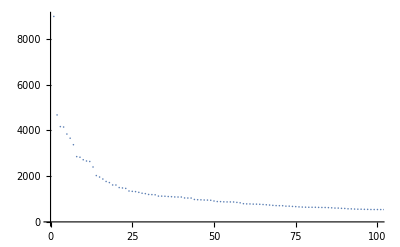

```mathematica
ListPlot[termOrd1[[All,{1,3}]], PlotRange->{ {0,100}, All}]
```

```mathematica
namespace=termOrd1[[;;50,2]]
```

{gene,cell,genet,express,human,dna,genom,analysi,associ,transcript,regul,sequenc,protein,rna,function,studi,chromosom,mutat,evolut,drosophila,activ,factor,develop,molecular,reveal,diseas,popul,structur,identifi,mous,genome-wid,variant,differenti,dure,novel,signal,control,cancer,complex,role,variat,model,stem,promot,effect,identif,respons,select,character,map}

```mathematica
binaryNamespaceAllTitles=ParallelTable[If[StringContainsQ[titles[[title]],namespace[[feature]],IgnoreCase->True],1,0],{title,Length[titles]},{feature,Length[namespace]}];
```

```mathematica
Labeled[ListPlot[DimensionReduce[binaryNamespaceAllTitles,Method->{"TSNE","Perplexity"->#}],ImageSize->400],"Perplexity = "<>ToString[#],Top]&/@Range[5,50,5]
```

```mathematica
reducedNamespaceVectors=DimensionReduce[binaryNamespaceAllTitles,Method->{"TSNE","Perplexity"->50}];
```

```mathematica
ReducedClassifier=ClusterClassify[reducedNamespaceVectors,20,Method->"KMedoids"]
```

ClassifierFunction[…]

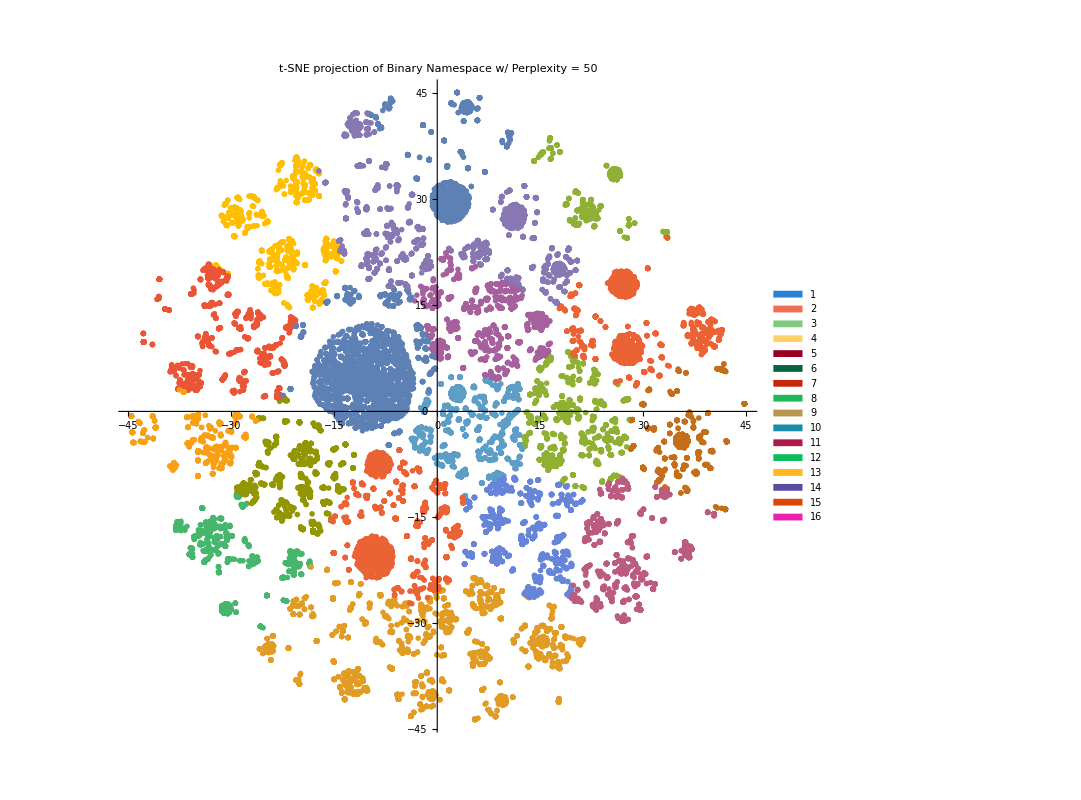

```mathematica
visualizeTSNE[reducedNamespaceVectors,ReducedClassifier,"t-SNE projection of Binary Namespace w/ Perplexity = 50"]
```

```mathematica
reducedAssoc=Thread[{titles,reducedNamespaceVectors}];
reducedAssocClustered=GatherBy[reducedAssoc,ReducedClassifier[#[[2]]]&];
titleColor[reducedFeatures_]:=legendColors[[ReducedClassifier[reducedFeatures]]];
titlesColorized=Style[#[[1]],titleColor[#[[2]]]]&/@reducedAssoc;
Labeled[Framed[Pane[Grid[Transpose[{Range[Length[reducedAssoc]],titlesColorized}],Alignment->Left],Scrollbars->True,ImageSize->{Automatic,400}]],"All titles cluster-colorized",Top]
```

1 | Modular co-option of cardiopharyngeal genes during non-embryonic myogenesis
2 | Molecular evolutionary trends and feeding ecology diversification in the Hemiptera, anchored by the milkweed bug genome
3 | Comparative analysis of whole-genome sequencing pipelines to minimize false negative findings
4 | Ulcerative colitis mucosal transcriptomes reveal mitochondriopathy and personalized mechanisms underlying disease severity and treatment response
5 | Common themes in tetrapod appendage regeneration: a cellular perspective
6 | svist4get: a simple visualization tool for genomic tracks from sequencing experiments
7 | A comprehensive single cell transcriptional landscape of human hematopoietic progenitors
8 | Genome-wide Association Study of Change in Fasting Glucose over time in 13,807 non-diabetic European Ancestry Individuals
9 | The genome of the giant Nomura’s jellyfish sheds light on the early evolution of active predation
10 | Batch correction evaluation framework using a-priori gene-gene associations: applied to the GTEx dataset
11 | m6Acomet: large-scale functional prediction of individual m6A RNA methylation sites from an RNA co-methylation network
12 | Simultaneous targeting of linked loci in mouse embryos using base editing
13 | Selection shapes turnover and magnitude of sex-biased expression in Drosophila gonads
14 | Modulation of chromatin remodeling proteins SMYD1 and SMARCD1 promotes contractile function of human pluripotent stem cell-derived ventricular cardiomyocyte in 3D-engineered cardiac tissues
15 | High-resolution specificity profiling and off-target prediction for site-specific DNA recombinases
16 | The neuronal stimulation–transcription coupling map
17 | Role of PRY-1/Axin in heterochronic miRNA-mediated seam cell development
18 | Polygenic risk associated with post-traumatic stress disorder onset and severity
19 | SREBP1-dependent de novo fatty acid synthesis gene expression is elevated in malignant melanoma and represents a cellular survival trait
20 | Chemical genomics reveals histone deacetylases are required for core regulatory transcription
21 | Detection of low-density Plasmodium falciparum infections using amplicon deep sequencing
22 | A dataset of egg size and shape from more than 6,700 insect species
23 | Multi-ancestry study of blood lipid levels identifies four loci interacting with physical activity
24 | GWAS and enrichment analyses of non-alcoholic fatty liver disease identify new trait-associated genes and pathways across eMERGE Network
25 | Spatiotemporal epidemiology, environmental correlates, and demography of malaria in Tak Province, Thailand (2012–2015)
26 | Genetic studies of accelerometer-based sleep measures yield new insights into human sleep behaviour
27 | Genome-wide association study identifies genetic loci for self-reported habitual sleep duration supported by accelerometer-derived estimates
28 | Multi-platform discovery of haplotype-resolved structural variation in human genomes
29 | A high-throughput screening and computation platform for identifying synthetic promoters with enhanced cell-state specificity (SPECS)
30 | RESCUE: imputing dropout events in single-cell RNA-sequencing data
31 | Cross-species genomic landscape comparison of human mucosal melanoma with canine oral and equine melanoma
32 | Rapid and reversible suppression of ALT by DAXX in osteosarcoma cells
33 | Rapid identification and phylogenetic classification of diverse bacterial pathogens in a multiplexed hybridization assay targeting ribosomal RNA
34 | Chromosome and plasmid-borne PLacO3O1 promoters differ in sensitivity to critically low temperatures
35 | Efficient Genomic Interval Queries Using Augmented Range Trees
36 | MaGIC: a machine learning tool set and web application for monoallelic gene inference from chromatin
37 | Developing a network view of type 2 diabetes risk pathways through integration of genetic, genomic and functional data
38 | Contribution of rare and common variants to intellectual disability in a sub-isolate of Northern Finland
39 | The relationship between oxidative stress, reproduction, and survival in a bdelloid rotifer
40 | CDK12 loss in cancer cells affects DNA damage response genes through premature cleavage and polyadenylation
41 | An integrative cross-omics analysis of DNA methylation sites of glucose and insulin homeostasis
42 | Multi omics analysis of fibrotic kidneys in two mouse models
43 | Multiplexed detection of RNA using MERFISH and branched DNA amplification
44 | Paternal-age-related de novo mutations and risk for five disorders
45 | Quantitative assessment of LASSO probe assembly and long-read multiplexed cloning
46 | GWAS for quantitative resistance phenotypes in Mycobacterium tuberculosis reveals resistance genes and regulatory regions
47 | A role for Vibrio vulnificus PecS during hypoxia
48 | Genome-wide association analyses of chronotype in 697,828 individuals provides insights into circadian rhythms
49 | Predispositional genome sequencing in healthy adults: design, participant characteristics, and early outcomes of the PeopleSeq Consortium
50 | The CHD6 chromatin remodeler is an oxidative DNA damage response factor
51 | Development of hRad51–Cas9 nickase fusions that mediate HDR without double-stranded breaks
52 | In vivo nuclear capture and molecular profiling identifies Gmeb1 as a transcriptional regulator essential for dopamine neuron function
53 | Chromatin Compaction by Small RNAs and the Nuclear RNAi Machinery in C. elegans
54 | Mapping the drivers of within-host pathogen evolution using massive data sets
55 | NF-Y controls fidelity of transcription initiation at gene promoters through maintenance of the nucleosome-depleted region
56 | Meta-analysis of epigenome-wide association studies in neonates reveals widespread differential DNA methylation associated with birthweight
57 | GEMINI: a variational Bayesian approach to identify genetic interactions from combinatorial CRISPR screens
58 | Increased PHGDH expression promotes aberrant melanin accumulation
59 | A Genome-Wide Analysis of the Penumbral Volume in Inbred Mice following Middle Cerebral Artery Occlusion
60 | Pancreatic islet chromatin accessibility and conformation reveals distal enhancer networks of type 2 diabetes risk
61 | Population structure determines the tradeoff between fixation probability and fixation time
62 | Lin28 and let-7 regulate the timing of cessation of murine nephrogenesis
63 | Pilot study of DNA methylation, molecular aging markers and measures of health and well-being in aging
64 | A (fire)cloud-based DNA methylation data preprocessing and quality control platform
65 | Genetic overlap of chronic obstructive pulmonary disease and cardiovascular disease-related traits: a large-scale genome-wide cross-trait analysis
66 | Sources of artifact in measurements of 6mA and 4mC abundance in eukaryotic genomic DNA
67 | Contrasting patterns of molecular evolution in metazoan germ line genes
68 | HIV-1 DNA sequence diversity and evolution during acute subtype C infection
69 | African evolutionary history inferred from whole genome sequence data of 44 indigenous African populations
70 | Systematic allelic analysis defines the interplay of key pathways in X chromosome inactivation
71 | Quantification of frequency-dependent genetic architectures in 25 UK Biobank traits reveals action of negative selection
72 | Accurate estimation of cell-type composition from gene expression data
73 | Genome-wide analysis of dental caries and periodontitis combining clinical and self-reported data
74 | BALLI: Bartlett-adjusted likelihood-based linear model approach for identifying differentially expressed genes with RNA-seq data
75 | PRC1 collaborates with SMCHD1 to fold the X-chromosome and spread Xist RNA between chromosome compartments
76 | Targeted expression profiling by RNA-Seq improves detection of cellular dynamics during pregnancy and identifies a role for T cells in term parturition
77 | Neuronal differentiation and cell-cycle programs mediate response to BET-bromodomain inhibition in MYC-driven medulloblastoma
78 | Genome of the tropical plant Marchantia inflexa: implications for sex chromosome evolution and dehydration tolerance
79 | Aggression and courtship differences found in Drosophila melanogaster from two different microclimates at Evolution Canyon, Israel
80 | Single-cell trajectories reconstruction, exploration and mapping of omics data with STREAM
81 | Lysine-specific demethylase 2A enhances binding of various nuclear factors to CpG-rich genomic DNAs by action of its CXXC-PHD domain
82 | Chronotype Genetic Variant in PER2 is Associated with Intrinsic Circadian Period in Humans
83 | Genome-wide meta-analysis identifies multiple novel loci associated with serum uric acid levels in Japanese individuals
84 | Integrated analysis of environmental and genetic influences on cord blood DNA methylation in new-borns
85 | Decoding the 5′ nucleotide bias of PIWI-interacting RNAs
86 | Direct observation of coordinated DNA movements on the nucleosome during chromatin remodelling
87 | Transcriptome signatures associated with meningioma progression
88 | A role for G protein-coupled receptor 137b in bone remodeling in mouse and zebrafish
89 | Somatic mosaicism of sex chromosomes in the blood and brain
90 | A demonstration of unsupervised machine learning in species delimitation
91 | Evolution in range expansions with competition at rough boundaries
92 | Advanced understanding of phylogenetic relationships, morphological evolution and biogeographic history of the mega-diverse plant genus Myrcia and its relatives (Myrtaceae: Myrteae)
93 | Macrothrombocytopenia associated with a rare GFI1B missense variant confounding the presentation of immune thrombocytopenia
94 | The genetics of vitamin D
95 | Single-cell cloning of human T-cell lines reveals clonal variation in cell death responses to chemotherapeutics
96 | Using zebrafish to study skeletal genomics
97 | Neurturin-containing laminin matrices support innervated branching epithelium from adult epithelial salispheres
98 | A high-throughput screening identifies microRNA inhibitors that influence neuronal maintenance and/or response to oxidative stress
99 | A semiparametric efficient estimator in case-control studies for gene-environment independent models
100 | Very low depth whole genome sequencing in complex trait association studies
101 | Genetic variants in RUNX3, AMD1 and MSRA in the methionine metabolic pathway and survival in nonsmall cell lung cancer patients
102 | KinVis: a visualization tool to detect cryptic relatedness in genetic datasets.
103 | Applicability of the Mutation-Selection Balance Model to Population Genetics of Heterozygous Protein-Truncating Variants in Humans.
104 | The protective variant rs7173049 at LOXL1 locus impacts on retinoic acid signaling pathway in pseudoexfoliation syndrome
105 | The Genetic Epidemiology of Type 2 Diabetes: Opportunities for Health Translation
106 | To leave or to stay: direct fitness through natural nest foundation in a primitively eusocial wasp
107 | Proceedings of the fourth international molecular pathological epidemiology (MPE) meeting
108 | Association of response to TNF inhibitors in rheumatoid arthritis with quantitative trait loci for CD40 and CD39
109 | Strategies for overcoming aversion to unnaturalness: The case of clean meat
110 | Lung Cancer Risk in Never Smokers of European Descent is Associated with Genetic Variation in the 5P15.33 TERT-CLPTM1L Region
111 | Recent genetic and functional insights in autism spectrum disorder.
112 | The Goddess Who Spins the Thread of Life: Klotho, Psychiatric Stress, and Accelerated Aging
113 | Recessive DES cardio/myopathy without myofibrillar aggregates: intronic splice variant silences one allele leaving only missense L190P-desmin
114 | The genetic architecture of adaptation: convergence and pleiotropy in Heliconius wing pattern evolution
115 | Linking genes, circuits, and behavior: network connectivity as a novel endophenotype of externalizing
116 | Body mass index in relation to extracellular vesicle–linked microRNAs in human follicular fluid
117 | Long non-coding RNA SNHG5 promotes glioma progression via miR-205/E2F3 axis
118 | Genome-wide epistasis and co-selection study using mutual information
119 | The Genetic Architecture of Chronic Mountain Sickness in Peru
120 | Maintenance of adaptive dynamics in a bottlenecked range-edge population that retained outcrossing
121 | Accurate estimation of SNP-heritability from biobank-scale data irrespective of genetic architecture
122 | Polyploidy increases overall diversity despite higher turnover than diploids in the Brassicaceae
123 | Genomic Influences on Self-Reported Childhood Maltreatment
124 | Imprinted maternally-expressed microRNAs antagonize paternally-driven gene programs in neurons
125 | Stem cell differentiation trajectories in Hydra resolved at single-cell resolution
126 | Peramorphosis, an evolutionary developmental mechanism in neotropical bat skull diversity
127 | The spectrum of BRCA1 and BRCA2 pathogenic sequence variants in Middle Eastern, North African, and South European countries
128 | Hox genes limit germ cell formation in the short germ insect Gryllus bimaculatus
129 | The Role of Prep1 in the Regulation of Mesenchymal Stromal Cells
130 | Overlap of Genetic Risk Between Interstitial Lung Abnormalities and Idiopathic Pulmonary Fibrosis
131 | The neural basis of tadpole transport in poison frogs.
132 | Genomics and psychological resilience: a research agenda
133 | Central spindle microtubules are strongly coupled to chromosomes during both anaphase A and anaphase B.
134 | Fast and robust ancestry prediction using principal component analysis
135 | Innovations in Primate Interneuron Repertoire
136 | Evolutionary Implications of Anoxygenic Phototrophy in the Bacterial Phylum Candidatus Eremiobacterota (WPS-2)
137 | Exceptionally Preserved Cambrian Fossils in the Genomic Era
138 | Single-cell profiles of retinal neurons differing in resilience to injury reveal neuroprotective genes
139 | Systematic congruence in Polycladida (Platyhelminthes, Rhabditophora): are DNA and morphology telling the same story?
140 | Geographic contrasts between pre- and postzygotic barriers are consistent with reinforcement in Heliconius butterflies
141 | The Airn lncRNA does not require any DNA elements within its locus to silence distant imprinted genes
142 | Continuous evolution of base editors with expanded target compatibility and improved activity
143 | Integrating natural history collections and comparative genomics to study the genetic architecture of convergent evolution
144 | Sex differences in the genetic predictors of Alzheimer’s pathology
145 | Programmable CRISPR-Cas Repression, Activation, and Computation with Sequence-Independent Targets and Triggers.
146 | Germ Granules Coordinate RNA-based Epigenetic Inheritance Pathways
147 | Luciferase-based reporting of suicide gene activity in murine mesenchymal stem cells
148 | An integrative ENCODE resource for cancer genomics
149 | Comparison of Two Commercial Matrix-Assisted Laser Desorption/Ionization-Time of Flight Mass Spectrometry (MALDI-TOF MS) Systems for Identification of Nontuberculous Mycobacteria.
150 | YAP and TAZ Regulate Cc2d1b and Purβ in Schwann Cells
151 | The genetics of human hematopoiesis and its disruption in disease
152 | Rotation tracking of genome-processing enzymes using DNA origami rotors
153 | Assembly of a functional ribozyme from short oligomers by enhanced non-enzymatic ligation
154 | Inducible Pluripotent Stem Cell–Derived Cardiomyocytes Reveal Aberrant Extracellular Regulated Kinase 5 and Mitogen-Activated Protein Kinase Kinase 1/2 Signaling Concomitantly Promote Hypertrophic Cardiomyopathy in RAF1-Associated Noonan Syndrome
155 | Selective targeting of PARP-2 inhibits androgen receptor signaling and prostate cancer growth through disruption of FOXA1 function
156 | DNA and RNA-SIP reveal Nitrospira spp. as key drivers of nitrification in groundwater-fed biofilters
157 | Morphological Diversification under High Integration in a Hyper Diverse Mammal Clade
158 | Genome-wide association study identifies eight risk loci and implicates metabo-psychiatric origins for anorexia nervosa
159 | A genome-wide association study of bitter and sweet beverage consumption.
160 | Contributions of Rare Gene Variants to Familial and Sporadic FSGS.
161 | Novel RB1-Loss Transcriptomic Signature Is Associated with Poor Clinical Outcomes across Cancer Types
162 | Positive genetic associations among fitness traits support evolvability of a reef-building coral under multiple stressors
163 | SID-4/NCK-1 is important for dsRNA import in Caenorhabditis elegans
164 | One in three highly selected Greek patients with breast cancer carries a loss-of-function variant in a cancer susceptibility gene
165 | Resistance to stress can be experimentally dissociated from longevity.
166 | Full sequence of mutant huntingtin 3′-untranslated region and modulation of its gene regulatory activity by endogenous microRNA
167 | Machine-learning classification suggests that many alphaproteobacterial prophages may instead be gene transfer agents
168 | Historical contingency in the evolution of antibiotic resistance after decades of relaxed selection
169 | Developmental subtypes assessed by DNA methylation-iPLEX forecast the natural history of chronic lymphocytic leukemia.
170 | Genome-wide association study provides new insights into the genetic architecture and pathogenesis of heart failure
171 | Revisiting metazoan phylogeny with genomic sampling of all phyla.
172 | Noninvasive preimplantation genetic testing for aneuploidy in spent medium may be more reliable than trophectoderm biopsy
173 | Early complement genes are associated with visual system degeneration in multiple sclerosis.
174 | Consecutive seeding and transfer of genetic diversity in metastasis
175 | Histone H2B monoubiquitination regulates heart development via epigenetic control of cilia motility
176 | The demethylase NMAD-1 regulates DNA replication and repair in the Caenorhabditis elegans germline
177 | Promoter-specific dynamics of TATA-binding protein association with the human genome
178 | The murine IgH locus contains a distinct DNA sequence motif for the chromatin regulatory factor CTCF
179 | Identifying gene expression programs of cell-type identity and cellular activity with single-cell RNA-Seq
180 | Ancient DNA reveals a multistep spread of the first herders into sub-Saharan Africa
181 | Loss of FLCN inhibits canonical WNT signaling via TFE3
182 | DNA repair and cancer in colon and rectum: Novel players in genetic susceptibility
183 | FEMALE SIGNAL VARIATION IN THE ANOLIS LEMURINUS GROUP
184 | Smoking-Related DNA Methylation is Associated with DNA Methylation Phenotypic Age Acceleration: The Veterans Affairs Normative Aging Study
185 | Analysis of genetically driven alternative splicing identifies FBXO38 as a novel COPD susceptibility gene
186 | Regulation of the bone vascular network is sexually dimorphic
187 | Nonenzymatic Template-Directed Synthesis of Mixed-Sequence 3'-NP-DNA up to 25 Nucleotides Long Inside Model Protocells.
188 | DNA methylation modifications induced by hexavalent chromium
189 | Discovery of Novel Therapeutics for Muscular Dystrophies using Zebrafish Phenotypic Screens.
190 | DNAvisualization.org: a serverless web tool for DNA sequence visualization
191 | Genome-wide CRISPR screen identifies suppressors of endoplasmic reticulum stress-induced apoptosis
192 | RNAmod: an integrated system for the annotation of mRNA modifications
193 | Proteome-wide signatures of function in highly diverged intrinsically disordered regions
194 | Roles and regulation of histone methylation in animal development
195 | Megacities, migration and an evolutionary approach to bipolar disorder: a study of Sardinian immigrants in Latin America
196 | The genomic complexity of a large inversion in great tits
197 | Hlf marks the developmental pathway for hematopoietic stem cells but not for erythro-myeloid progenitors
198 | DNA double-strand break repair-pathway choice in somatic mammalian cells
199 | Identification of Novel Susceptibility Loci and Genes for Prostate Cancer Risk: A Transcriptome-Wide Association Study in Over 140,000 European Descendants
200 | Pathway analysis of a genome-wide gene by air pollution interaction study in asthmatic children
201 | Intratumoral Heterogeneity: More Than Just Mutations
202 | Enforcement is central to the evolution of cooperation
203 | PCIF1 Catalyzes m6Am mRNA Methylation to Regulate Gene Expression
204 | SynGO: An Evidence-Based, Expert-Curated Knowledge Base for the Synapse
205 | Clonal Hematopoiesis of Indeterminate Potential Reshapes Age-Related CVD JACC Review Topic of the Week
206 | Recessive gene disruptions in autism spectrum disorder
207 | Paternal Nongenetic Intergenerational Transmission of Metabolic Disease Risk
208 | TBX6-associated congenital scoliosis (TACS) as a clinically distinguishable subtype of congenital scoliosis: further evidence supporting the compound inheritance and TBX6 gene dosage model
209 | Beyond Synthetic Lethality: Charting the Landscape of Pairwise Gene Expression States Associated with Survival in Cancer
210 | A molecular analysis of sand fly blood meals in a visceral leishmaniasis endemic region of northwestern Ethiopia reveals a complex host-vector system
211 | Embracing diversity in the 5-HT neuronal system
212 | Myc and Dnmt1 impede the pluripotent to totipotent state transition in embryonic stem cells
213 | Comparison of three congruent patient-specific cell types for the modelling of a human genetic Schwann-cell disorder
214 | An Evolutionarily Conserved uORF Regulates PGC1α and Oxidative Metabolism in Mice, Flies, and Bluefin Tuna
215 | O19.2 Bridging of neisseria gonorrhoeae across diverse sexual networks in the HIV PrEP era
216 | Abnormal behavior of zebrafish mutant in dopamine transporter is rescued by clozapine
217 | Historical contingency shapes adaptive radiation in Antarctic fishes
218 | Functional genomics of the rapidly replicating bacterium Vibrio natriegens by CRISPRi
219 | Large-scale chemical–genetics yields new M. tuberculosis inhibitor classes
220 | Genome sequencing analysis identifies Epstein–Barr virus subtypes associated with high risk of nasopharyngeal carcinoma
221 | Identification of risk loci and a polygenic risk score for lung cancer: a large-scale prospective cohort study in Chinese populations
222 | Environmental Oxygen Exposure Allows for the Evolution of Interdigital Cell Death in Limb Patterning
223 | HCF-1 Regulates De Novo Lipogenesis through a Nutrient-Sensitive Complex with ChREBP
224 | Single-Copy Knock-In Loci for Defined Gene Expression in Caenorhabditis elegans
225 | Evolution and expansion of multidrug-resistant malaria in southeast Asia: a genomic epidemiology study
226 | Intra- and Inter-cellular Rewiring of the Human Colon during Ulcerative Colitis
227 | Genomic characterization of hepatitis C virus transmitted founder variants with deep sequencing
228 | Whsc1 links pluripotency exit with mesendoderm specification
229 | Mendelian Randomization Analysis of Hemoglobin A1c as a Risk Factor for Coronary Artery Disease
230 | Epigenetic Priming of Human Pluripotent Stem Cell-Derived Cardiac Progenitor Cells Accelerates Cardiomyocyte Maturation
231 | De Novo Variants in WDR37 Are Associated with Epilepsy, Colobomas, Dysmorphism, Developmental Delay, Intellectual Disability, and Cerebellar Hypoplasia
232 | Identification of novel RHO homozygous mutation in Chinese autosomal recessive retinitis pigmentosa patients
233 | A systems biology pipeline identifies regulatory networks for stem cell engineering
234 | Ancient DNA sheds light on the genetic origins of early Iron Age Philistines
235 | Genome wide analysis of 3′ UTR sequence elements and proteins regulating mRNA stability during maternal-to-zygotic transition in zebrafish
236 | Quantitative Comparison of the Anterior-Posterior Patterning System in the Embryos of Five Drosophila Species
237 | Identification of the m6Am Methyltransferase PCIF1 Reveals the Location and Functions of m6Am in the Transcriptome
238 | Exome-Derived Adiponectin-Associated Variants Implicate Obesity and Lipid Biology
239 | Allele-specific gene editing prevents deafness in a model of dominant progressive hearing loss
240 | Contribution of rare copy number variants to bipolar disorder risk is limited to schizoaffective cases
241 | O04.1 Novel pathway to ceftriaxone resistance in clinical isolates of N. gonorrhoeae via point mutations in the RNA polymerase
242 | Inferring protein 3D structure from deep mutation scans
243 | An ‘i’ for ingenuity
244 | Correction for multiple testing in candidate-gene methylation studies
245 | Analyzing and Reanalyzing the Genome: Findings from the MedSeq Project
246 | Genome-wide analyses of psychological resilience in U.S. Army soldiers
247 | Mapping Distinct Bone Marrow Niche Populations and Their Differentiation Paths
248 | Predicting polygenic risk of psychiatric disorders
249 | Compression Generated by a 3D Supracellular Actomyosin Cortex Promotes Embryonic Stem Cell Colony Growth and Expression of Nanog and Oct4
250 | Insect egg size and shape evolve with ecology but not developmental rate
251 | Trans− and cis−acting effects of the lncRNA Firre on epigenetic and structural features of the inactive X chromosome
252 | Sulfate assimilation regulates hydrogen sulfide production independent of lifespan and reactive oxygen species under methionine restriction condition in yeast
253 | Transposable element over-accumulation in autopolyploids results from relaxed purifying selection and provides variants for rapid local adaptation
254 | GWAS of QRS duration identifies new loci specific to Hispanic/Latino populations
255 | Diversity of Wolbachia Associated with the Giant Turtle Ant, Cephalotes atratus
256 | The Asian-Melanesian bambusicolous genus Myriodiscus is related to the genus Tympanis, the North American-European tree pathogen
257 | Allopatric divergence and secondary contact with gene flow: a recurring theme in rattlesnake speciation
258 | A zoonotic adenoviral human pathogen emerged through genomic recombination amongst human and nonhuman simian hosts.
259 | CTCF variants in 39 individuals with a variable neurodevelopmental disorder broaden the mutational and clinical spectrum
260 | MOGSA: integrative single sample gene-set analysis of multiple omics data
261 | DNA-Membrane Anchor Facilitates Efficient Chromosome Translocation at a Distance in Bacillus subtilis.
262 | Droplet-based combinatorial indexing for massive-scale single-cell chromatin accessibility
263 | Sex specific associations in genome wide association analysis of renal cell carcinoma
264 | Dissecting the sharp response of a canonical developmental enhancer reveals multiple sources of cooperativity
265 | Global analysis of polysome-associated mRNA in vesicular stomatitis virus infected cells
266 | Higher fitness yeast genotypes are less robust to deleterious mutations
267 | DNMT3B shapes the mCA landscape and regulates mCG for promoter bivalency in human embryonic stem cells
268 | Simultaneous TE Analysis of 19 Heliconiine Butterflies Yields Novel Insights into Rapid TE-based Genome Diversification and Multiple SINE Births and Deaths
269 | Towards a gold standard for benchmarking gene set enrichment analysis
270 | Regulation of Caenorhabditis elegans neuronal polarity by heterochronic genes
271 | Genome-wide association analysis of HDL-C in a Lebanese cohort
272 | Deleterious de novo variants of X-linked ZC4H2 in females cause a variable phenotype with neurogenic arthrogryposis multiplex congenita
273 | The Relationship Between Polygenic Risk Scores and Cognition in Schizophrenia
274 | Estimating Relatedness Between Malaria Parasites
275 | Whole genome sequencing of Mycobacterium tuberculosis: current standards and open issues
276 | Association of cicatricial alopecia with chemical hair straightening
277 | Probabilistic Models of Larval Zebrafish Behavior: Structure on Many Scales
278 | A New Suite of Allelic Exchange Vectors for the Scarless Modification of Proteobacterial Genomes.
279 | Exposure to an environmentally relevant phthalate mixture during prostate development induces microRNA upregulation and transcriptome modulation in rats.
280 | Small-molecule control of super-Mendelian inheritance in gene drives
281 | Experimental evolution for niche breadth in bacteriophage T4 highlights the importance of structural genes
282 | Protein structure from experimental evolution
283 | Synthetic Biology Open Language Visual (SBOL Visual) Version 2.1
284 | Genome-wide association study of breakfast skipping links clock regulation with food timing.
285 | Human aging DNA methylation signatures are conserved but accelerated in cultured fibroblasts
286 | Alternative transcription cycle for bacterial RNA polymerase
287 | CREB promotes beta cell gene expression by targeting Its coactivators to tissue-specific enhancers.
288 | PHISDetector: a web tool to detect diverse in silico phage-host interaction signals
289 | Genetic analysis of IgG4-related disease
290 | The Insights of Radical Science in the CRISPR Gene-Editing Era: A History of Science for the People and the Cambridge Recombinant DNA Controversy
291 | Population Genomics and Demographic Sampling of the Ant-Plant Vachellia drepanolobium and Its Symbiotic Ants From Sites Across Its Range in East Africa
292 | Epigenetic upregulation of FKBP5 by aging and stress contributes to NF-κB–driven inflammation and cardiovascular risk
293 | Genomic Evolutionary Patterns of Leiomyosarcoma and Liposarcoma
294 | Systematic evasion of the restriction-modification barrier in bacteria
295 | Aberrant splicing contributes to severe α-spectrin-linked congenital hemolytic anemia
296 | Substrate inhibition imposes fitness penalty at high protein stability
297 | HiNT: a computational method for detecting copy number variations and translocations from Hi-C data
298 | DrugThatGene: integrative analysis to streamline the identification of druggable genes, pathways and protein complexes from CRISPR screens.
299 | HMP16SData: Efficient Access to the Human Microbiome Project through Bioconductor
300 | A chromosome-scale assembly of the major African malaria vector Anopheles funestus
301 | Mendelian Randomization and mediation analysis of leukocyte telomere length and risk of lung and head and neck cancers.
302 | Agnostic Pathway/Gene Set Analysis of Genome-Wide Association Data Identifies Associations for Pancreatic Cancer.
303 | Multi-Ancestry Genome-Wide Association Study of Lipid Levels Incorporating Gene-Alcohol Interactions
304 | A Cellular Taxonomy of the Bone Marrow Stroma in Homeostasis and Leukemia
305 | SABER amplifies FISH: enhanced multiplexed imaging of RNA and DNA in cells and tissues
306 | Translational and transcriptional responses in human primary hepatocytes under hypoxia.
307 | Inadequate DNA Damage Repair Promotes Mammary Transdifferentiation, Leading to BRCA1 Breast Cancer
308 | Bayesian model for accurate MARSALA (mutated allele revealed by sequencing with aneuploidy and linkage analyses)
309 | Mosquito microevolution drives Plasmodium falciparum dynamics
310 | A catalog of genetic loci associated with kidney function from analyses of a million individuals
311 | Q & A with Daniel L. Hartl, Recipient of the 2019 Thomas Hunt Morgan Medal
312 | Polygenic risk scores for developmental disorders, neuromotor functioning during infancy and autistic traits in childhood
313 | Genome-wide association study in two populations to determine genetic variants associated with Toxoplasma gondii infection and relationship to schizophrenia risk
314 | Genetic Association of Finger Photoplethysmography-Derived Arterial Stiffness Index With Blood Pressure and Coronary Artery Disease
315 | A New Subspecies of Heliconius hermathena (Nymphalidae: Heliconiinae) from Southern Amazonia
316 | Single-cell transcriptomic analysis of Alzheimer’s disease
317 | Observation of seasonal variation of atmospheric multiple-muon events in the NOvA Near Detector
318 | Cell-type-specific programs for activity-regulated gene expression
319 | The Translational Landscape of the Human Heart
320 | The genetic history of admixture across inner Eurasia
321 | Proteomics of Asrij Perturbation in Drosophila Lymph Glands for Identification of New Regulators of Hematopoiesis
322 | Exome sequencing of 20,791 cases of type 2 diabetes and 24,440 controls
323 | First International Conference on RASopathies and Neurofibromatoses in Asia: Identification and advances of new therapeutics
324 | Tracing Oncogene Rearrangements in the Mutational History of Lung Adenocarcinoma
325 | Bi-allelic Variants in DYNC1I2 Cause Syndromic Microcephaly with Intellectual Disability, Cerebral Malformations, and Dysmorphic Facial Features
326 | Cell diversity in the human cerebral cortex: from the embryo to brain organoids
327 | JNK inactivation suppresses osteogenic differentiation, but robustly induces osteopontin expression in osteoblasts through the induction of inhibitor of DNA binding 4 (Id4)
328 | Paralog Studies Augment Gene Discovery: DDX and DHX Genes
329 | Molecular recording of mammalian embryogenesis
330 | Proteostasis Environment Shapes Higher-Order Epistasis Operating on Antibiotic Resistance
331 | Benchmarker: An Unbiased, Association-Data-Driven Strategy to Evaluate Gene Prioritization Algorithms
332 | Asthma severity, nature or nurture: genetic determinants.
333 | Frailty biomarkers in humans and rodents: current approaches and future advances
334 | Recurrent SMARCB1 Inactivation in Epithelioid Malignant Peripheral Nerve Sheath Tumors
335 | Clinical presentation and genetic profiles of Chinese patients with velocardiofacial syndrome in a large referral centre
336 | Characterization of paralogous uncx transcription factor encoding genes in zebrafish
337 | The rise of the genetic counseling profession in China
338 | Differentially expressed genes associated with the estrogen receptor pathway in cerebral aneurysms
339 | Material solutions for delivery of CRISPR/Cas-based genome editing tools: Current status and future outlook
340 | Individual brain organoids reproducibly form cell diversity of the human cerebral cortex
341 | Mating preferences of selfish sex chromosomes
342 | A genome-wide association study implicates NR2F2 in lymphangioleiomyomatosis pathogenesis
343 | Circularly permuted and PAM-modified Cas9 variants broaden the targeting scope of base editors
344 | Reproductive Capacity Evolves in Response to Ecology through Common Changes in Cell Number in Hawaiian Drosophila
345 | A large-scale exome array analysis of venous thromboembolism
346 | Phosphorylation of FANCD2 Inhibits the FANCD2/FANCI Complex and Suppresses the Fanconi Anemia Pathway in the Absence of DNA Damage
347 | Genome Sequencing Identifies the Pathogenic Variant Missed by Prior Testing in an Infant with Marfan Syndrome
348 | Development of a Selective CDK7 Covalent Inhibitor Reveals Predominant Cell-Cycle Phenotype
349 | Epigenetic age acceleration is associated with allergy and asthma in children in Project Viva
350 | Pheromones and Barcoding Delimit Boundaries between Cryptic Species in the Primitive Moth Genus Eriocrania (Lepidoptera: Eriocraniidae)
351 | Are BALB/c Mice Relevant Models for Understanding Sex-Related Differences in Gene Expression in the Human Meibomian Gland?
352 | Single-Cell RNA-seq: Introduction to Bioinformatics Analysis
353 | Complete chloroplast genome of Anathallis obovata (Orchidaceae: Pleurothallidinae)
354 | Nucleic Acid Detection of Plant Genes Using CRISPR-Cas13
355 | Common Polygenic Variations for Psychiatric Disorders and Cognition in Relation to Brain Morphology in the General Pediatric Population
356 | Cross-Regulation between TDP-43 and Paraspeckles Promotes Pluripotency-Differentiation Transition
357 | Heterozygous Variants in KMT2E Cause a Spectrum of Neurodevelopmental Disorders and Epilepsy
358 | The X-Linked DDX3X RNA Helicase Dictates Translation Reprogramming and Metastasis in Melanoma
359 | Maternal corticotropin-releasing hormone is associated with LEP DNA methylation at birth and in childhood: an epigenome-wide study in Project Viva
360 | EGFR is required for Wnt9a–Fzd9b signalling specificity in haematopoietic stem cells
361 | Fibroblast growth factor signaling mediates progenitor cell aggregation and nephron regeneration in the adult zebrafish kidney
362 | Transcriptional States and Chromatin Accessibility Underlying Human Erythropoiesis
363 | Put the Pedal to the METTL1: Adding Internal m7G Increases mRNA Translation Efficiency and Augments miRNA Processing
364 | World Workshop on Oral Medicine VII: Targeting the microbiome for oral medicine specialists—Part 1. A methodological guide
365 | Mitochondrial Genome Diversity in the Central Siberian Plateau with Particular Reference to Prehistory of Northernmost Eurasia
366 | Human Auditory Ossicles as an Alternative Optimal Source of Ancient DNA
367 | Systematic proteomics of endogenous human cohesin reveals an interaction with diverse splicing factors and RNA-binding proteins required for mitotic progression
368 | Chimeric dihydrofolate reductases display properties of modularity and biophysical diversity
369 | Monogenic and polygenic inheritance become instruments for clonal selection
370 | Genetically predicted levels of DNA methylation biomarkers and breast cancer risk: data from 228,951 women of European descent.
371 | Epigenome-wide association analysis of daytime sleepiness in the Multi-Ethnic Study of Atherosclerosis reveals African-American-specific associations
372 | Imaging-based pooled CRISPR screening reveals regulators of lncRNA localization
373 | Impact of Species Diversity on the Design of RNA-Based Diagnostics for Antibiotic Resistance in Neisseria gonorrhoeae.
374 | Improving Convolutional Network Interpretability with Exponential Activations
375 | Population substructure and signals of divergent adaptive selection despite admixture in the sponge Dendrilla antarctica from shallow waters surrounding the Antarctic Peninsula
376 | Technical Note: Efficient and accurate estimation of genotype odds ratios in biobank-based unbalanced case-control studies
377 | Evolutionary Conservation of Thyroid Hormone Receptor and Deiodinase Expression Dynamics in ovo in a Direct-Developing Frog, Eleutherodactylus coqui
378 | The Firre locus produces a trans-acting RNA molecule that functions in hematopoiesis
379 | A Genetic Locus on Chromosome 2q24 Predicting Peripheral Neuropathy Risk in Type 2 Diabetes: Results From the ACCORD and BARI 2D Studies
380 | Slow extension of the invading DNA strand in a D-loop formed by RecA-mediated homologous recombination may enhance recognition of DNA homology
381 | Promoter-proximal pausing of RNA polymerase II: a nexus of gene regulation.
382 | Editing aberrant splice sites efficiently restores β-globin expression in β-thalassemia.
383 | Comparative Tn-Seq reveals common daptomycin resistance determinants in Staphylococcus aureus despite strain-dependent differences in essentiality of shared cell envelope genes
384 | A Tale of Two Skates: Comparative Phylogeography of North American Skate Species with Implications for Conservation
385 | Computational Simulation of Adapter Length-Dependent LASSO Probe Capture Efficiency
386 | Primary cilia defects causing mitral valve prolapse
387 | Activation of PASK by mTORC1 is required for the onset of the terminal differentiation program
388 | RNA ligands activate the Machupo virus polymerase and guide promoter usage
389 | Molecular phylogenomics of the tribe Shoreeae (Dipterocarpaceae) using whole plastid genomes
390 | Cell-free transcriptional regulation via nucleic-acid-based transcription factors
391 | SYCP2 translocation-mediated dysregulation and frameshift variants cause human male infertility
392 | Urine mRNA to identify a novel pseudoexon causing dystrophinopathy
393 | Biological traits, phylogeny and human footprint signatures on the geographical range size of passerines (Order Passeriformes) worldwide
394 | Gene knock-ins in Drosophila using homology-independent insertion of universal donor plasmids
395 | The TFAP2A-IRF6-GRHL3 genetic pathway is conserved in neurulation.
396 | Genomics of hosts-pathogen interactions: challenges and opportunities across ecological and spatiotemporal scales
397 | Genomics of hosts-pathogen interactions: challenges and opportunities across ecological and spatiotemporal scales
398 | Advancing functional genetics through Agrobacterium-mediated insertional mutagenesis and CRISPR/Cas9 in the commensal and pathogenic yeast Malassezia furfur
399 | Sex differences in gene expression in response to ischemia in the human left ventricular myocardium.
400 | The Epigenomics of Pituitary Adenoma
401 | Systematic analyses of regulatory variants in DNase I hypersensitive sites identified two novel lung cancer susceptibility loci.
402 | A multiplexed DNA FISH strategy for assessing genome architecture in Caenorhabditis elegans
403 | Islands of retroelements are major components of Drosophila centromeres
404 | Aberrant DNA methylation of miRNAs in Fuchs endothelial corneal dystrophy
405 | Cell Cycle Kinase Polo Is Controlled by a Widespread 3' Untranslated Region Regulatory Sequence in Drosophila melanogaster.
406 | Mice Against Ticks: an experimental community-guided effort to prevent tick-borne disease by altering the shared environment.
407 | Identification of testicular cancer driver genes by a cross-species comparative oncology approach
408 | Operating Characteristics of the Rank-Based Inverse Normal Transformation for Quantitative Trait Analysis in Genome-Wide Association Studies
409 | Recording temporal data onto DNA with minutes resolution
410 | Fine-scale haplotype structure reveals strong signatures of positive selection in a recombining bacterial pathogen
411 | CRISPR adenine and cytosine base editors with reduced RNA off-target activities
412 | Estimating variance components in population scale family trees
413 | On the importance of accounting for intraspecific genomic relatedness in multi-species studies
414 | Genome-Wide Association Mapping of Floral Traits in Cultivated Sunflower (Helianthus annuus).
415 | Identification of differentially expressed gene sets using the Generalized Berk-Jones statistica.
416 | Impaired human hematopoiesis due to a cryptic intronic GATA1 splicing mutation
417 | Meiotic gatekeeper STRA8 suppresses autophagy by repressing Nr1d1 expression during spermatogenesis in mice
418 | Comparative genomics of Bifidobacterium species isolated from marmosets and humans
419 | Figure 1 Theory Meets Figure 2 Experiments in the Study of Gene Expression
420 | Epigenome-wide association study reveals methylation pathways associated with childhood allergic sensitization
421 | Association of Economic Status and Educational Attainment With Posttraumatic Stress Disorder
422 | Functional genomics of the stable fly, Stomoxys calcitrans, reveals mechanisms underlying reproduction, host interactions, and novel targets for pest control
423 | Functional performance of turtle humerus shape across an ecological adaptive landscape
424 | Signals Among Signals: Prioritizing Non-genetic Associations in Massive Datasets
425 | Disruption of asxl1 results in myeloproliferative neoplasms in zebrafish
426 | The EVcouplings Python framework for coevolutionary sequence analysis.
427 | Bayesian detection of convergent rate changes of conserved noncoding elements on phylogenetic trees
428 | Extensive Recovery of Embryonic Enhancer and Gene Memory Stored in Hypomethylated Enhancer DNA
429 | Heritability of fetal hemoglobin, white cell count, and other clinical traits from a sickle cell disease family cohort
430 | Genes with High Network Connectivity Are Enriched for Disease Heritability
431 | De novo variants in FBXO11 cause a syndromic form of intellectual disability with behavioral problems and dysmorphisms
432 | Maternal and fetal genetic effects on birth weight and their relevance to cardio-metabolic risk factors
433 | Genetic correlations between diabetes and glaucoma: an analysis of continuous and dichotomous phenotypes
434 | Crucial and Overlapping Roles of Six1 and Six2 in Craniofacial Development
435 | GWAS of smoking behaviour in 165,436 Japanese people reveals seven new loci and shared genetic architecture
436 | Transcriptome-wide off-target RNA editing induced by CRISPR-guided DNA base editors
437 | Epigenetic evolution and lineage histories of chronic lymphocytic leukaemia
438 | Epididymal small non-coding RNA studies: progress over the past decade
439 | Molecular Testing in Breast Cancer.
440 | Celia’s encephalopathy and c.974dupG in BSCL2 gene: a hidden change in a known variant
441 | Wnt Signaling Separates the Progenitor and Endocrine Compartments during Pancreas Development
442 | Active chromatin marks drive spatial sequestration of heterochromatin in C. elegans nuclei
443 | Methylation of cation–chloride cotransporters NKCC1 and KCC2 in patients with juvenile myoclonic epilepsy
444 | Targeting chromatin complexes in fusion protein-driven malignancies
445 | Ancient genomes indicate population replacement in Early Neolithic Britain
446 | New and Emerging Biomarkers in Endocrine Pathology
447 | Translational Control under Stress: Reshaping the Translatome
448 | Plastomes resolve generic limits within tribe Clusieae (Clusiaceae) and reveal the new genus Arawakia
449 | Detecting the mutational signature of homologous recombination deficiency in clinical samples
450 | Pharmacological Induction of a Progenitor State for the Efficient Expansion of Primary Human Hepatocytes
451 | 121 Re-evaluating the genetic contribution of monogenic dilated cardiomyopathy
452 | Coevolution of Genome Architecture and Social Behavior
453 | De Novo DNA Methylation at Imprinted Loci during Reprogramming into Naive and Primed Pluripotency
454 | IMPACT: Genomic Annotation of Cell-State-Specific Regulatory Elements Inferred from the Epigenome of Bound Transcription Factors
455 | Recall by genotype and cascade screening for familial hypercholesterolemia in a population-based biobank from Estonia
456 | Next-generation characterization of the Cancer Cell Line Encyclopedia
457 | Progression of Meiosis is Coordinated by the Level and Location of MAPK Activation Via OGR-2 in Caenorhabditis elegans
458 | Inclusion body myositis: clinical features and pathogenesis
459 | Dynamic Scan Procedure for Detecting Rare-Variant Association Regions in Whole-Genome Sequencing Studies
460 | The Contribution of Low-Frequency and Rare Coding Variation to Susceptibility to Type 2 Diabetes
461 | Human Pluripotency Is Initiated and Preserved by a Unique Subset of Founder Cells
462 | Analysis and minimization of cellular RNA editing by DNA adenine base editors
463 | Beta vulgaris mitovirus 1 in diverse cultivars of beet and chard
464 | Systems pharmacogenomics – gene, disease, drug and placebo interactions: a case study in COMT
465 | Genome-wide association study identifies 30 loci associated with bipolar disorder
466 | The Promise of Paleogenomics Beyond Our Own Species
467 | Accurate analysis of genuine CRISPR editing events with ampliCan
468 | Response to vocal music in Angelman syndrome contrasts with Prader-Willi syndrome
469 | Charting cellular identity during human in vitro β-cell differentiation
470 | The lncRNA SLNCR Recruits the Androgen Receptor to EGR1-Bound Genes in Melanoma and Inhibits Expression of Tumor Suppressor p21
471 | The Pseudomonas aeruginosa accessory genome elements, including bacterial immune systems effect virulence towards C. elegans
472 | Defining the core essential genome of Pseudomonas aeruginosa
473 | Rapid, Low-Cost Detection of Water Contaminants Using Regulated In Vitro Transcription
474 | Insect herbivory reshapes a native leaf microbiome
475 | Relationship Between Distance Run Per Week, Omega-3 Index, and Arachidonic Acid (AA)/Eicosapentaenoic Acid (EPA) Ratio: An Observational Retrospective Study in Non-elite Runners
476 | Condensin II subunit NCAPH2 associates with shelterin protein TRF1 and is required for telomere stability
477 | Identification of neuronal lineages in the Drosophila peripheral nervous system with a novel multi-spectral lineage tracing system
478 | A phylogenomic framework, evolutionary timeline and genomic resources for comparative studies of decapod crustaceans.
479 | Genome-wide Kdm4 histone demethylase transcriptional regulation in Drosophila.
480 | RNA Sequencing Analyses of Gene Expression during Epstein-Barr Virus Infection of Primary B Lymphocytes.
481 | An elucidation of over a century old enigma in genetics-Heterosis.
482 | Whole-Genome Analyses Resolve the Phylogeny of Flightless Birds (Palaeognathae) in the Presence of an Empirical Anomaly Zone.
483 | Daisy-chain gene drives for the alteration of local populations
484 | Bacterial Genome-Wide Association Identifies Novel Factors That Contribute to Ethionamide and Prothionamide Susceptibility in Mycobacterium tuberculosis
485 | MEDU-36. BCL2 FAMILY MEMBERS ATTENUATE RESPONSE OF MYC-DRIVEN MEDULLOBLASTOMAS TO BET-BROMODOMAIN INHIBITION
486 | A Bayesian model of acquisition and clearance of bacterial colonization incorporating within-host variation
487 | Phage-Assisted Evolution of Bacillus methanolicus Methanol Dehydrogenase 2.
488 | Droplet-based combinatorial indexing for massive scale single-cell epigenomics
489 | Mitovirus and Mitochondrial Coding Sequences from Basal Fungus Entomophthora muscae
490 | A U2-snRNP–independent role of SF3b in promoting mRNA export
491 | Associations of variants In the hexokinase 1 and interleukin 18 receptor regions with oxyhemoglobin saturation during sleep
492 | Non-Synonymous variants in premelanosome protein (PMEL) cause ocular pigment dispersion and pigmentary glaucoma.
493 | Identifying centromeric satellites with dna-brnn.
494 | Genome-wide association study of anti-Müllerian hormone levels in pre-menopausal women of late reproductive age and relationship with genetic determinants of reproductive lifespan.
495 | Completing the genetic spectrum influencing coronary artery disease: from germline to somatic variation
496 | OR08-3 The Role Of Neuronal Plasticity In The Timing Of Puberty Onset: Insights From A Mkrn3 Deficient Mouse Model.
497 | TOBMI: trans-omics block missing data imputation using a k-nearest neighbor weighted approach.
498 | Wnt signaling mediates new nephron formation during zebrafish kidney regeneration
499 | A patient with homozygous nonsense variants in two Leigh syndrome disease genes: Distinguishing a dual diagnosis from a hypomorphic protein-truncating variant
500 | SarcTrack
501 | Feedforward regulation of Myc coordinates lineage-specific with housekeeping gene expression during B cell progenitor cell differentiation
502 | The Adaptive Proline Response in P. falciparum Is Independent of PfeIK1 and eIF2α Signaling.
503 | Characterizing variants of unknown significance in rhodopsin: A functional genomics approach
504 | An exploratory phenome wide association study linking asthma and liver disease genetic variants to electronic health records from the Estonian Biobank
505 | The NASA Twins Study: A multidimensional analysis of a year-long human spaceflight.
506 | RNA polymerases as moving barriers to condensin loop extrusion
507 | Human Aging DNA Methylation Signatures are Conserved but Accelerated in Cultured Fibroblasts
508 | ALPK1 missense pathogenic variant in five families leads to ROSAH syndrome, an ocular multisystem autosomal dominant disorder
509 | A viral metagenomic survey identifies known and novel mammalian viruses in bats from Saudi Arabia
510 | A reference map of the human protein interactome
511 | The Prevotella copri complex comprises four distinct clades that are underrepresented in Westernised populations
512 | Tubulin mRNA stability is sensitive to change in microtubule dynamics caused by multiple physiological and toxic cues
513 | Exploring the link between adenine DNA methylation and 3D genome organization in the parasite Trichomonas vaginalis
514 | Multiplexed and Inducible Gene Modulation in Human Pluripotent Stem Cells by CRISPR Interference and Activation
515 | Significant abundance of cis configurations of coding variants in diploid human genomes
516 | FIN-Seq: Transcriptional profiling of specific cell types in frozen archived tissue from the human central nervous system
517 | Systematics, biogeography and diversification of Scytalopus tapaculos (Rhinocryptidae), an enigmatic radiation of Neotropical montane birds
518 | Convergent regulatory evolution and loss of flight in paleognathous birds
519 | Insertion sequences drive the emergence of a highly adapted human pathogen
520 | Analysis of 19 Heliconiine Butterflies Shows Rapid TE-based Diversification and Multiple SINE Births and Deaths
521 | Adherence of cell-free DNA noninvasive prenatal screens to ACMG recommendations
522 | Locus-specific DNA methylation prediction in cord blood and placenta
523 | Disentangled Representations of Cellular Identity
524 | Hypoxia Causes Transgenerational Impairment of Ovarian Development and Hatching Success in Fish.
525 | Transcriptome-wide profiling of multiple RNA modifications simultaneously at single-base resolution
526 | novoCaller: a Bayesian network approach for de novo variant calling from pedigree and population sequence data.
527 | Maternal-biased H3K27me3 correlates with paternal-specific gene expression in the human morula.
528 | Association of Inherited Pathogenic Variants in Checkpoint Kinase 2 (CHEK2) With Susceptibility to Testicular Germ Cell Tumors
529 | Per-Nucleus Crossover Covariation and Implications for Evolution
530 | The Influenza A Virus Endoribonuclease PA-X Usurps Host mRNA Processing Machinery to Limit Host Gene Expression
531 | A Comprehensive Drosophila melanogaster Transcription Factor Interactome
532 | A comparison of the association between large haplotype blocks under selection and the presence/absence of inversions
533 | To Sleep, Perchance to Survive?
534 | Birth of an order: comprehensive molecular phylogenetic study excludes Herpomyces (Fungi, Laboulbeniomycetes) from Laboulbeniales
535 | The Iceberg under Water: Unexplored Complexity of Chromoanagenesis in Congenital Disorders
536 | Probing the Global Cellular Responses to Lipotoxicity Caused by Saturated Fatty Acids
537 | Multi-ancestry genome-wide gene–smoking interaction study of 387,272 individuals identifies new loci associated with serum lipids
538 | Conducting a Reproducible Mendelian Randomization Analysis Using the R Analytic Statistical Environment
539 | Comparison of variation in frequency for SNPs associated with asthma or liver disease between Estonia, HapMap populations and the 1000 genome project populations
540 | Genetics of Bone and Muscle Interactions in Humans
541 | Fast Estimation of Recombination Rates Using Topological Data Analysis
542 | Mapping allele with resolved carrier status of Robertsonian and reciprocal translocation in human preimplantation embryos
543 | Secondary findings: How did we get here, and where are we going?
544 | Posttraumatic psychopathology and the pace of the epigenetic clock: a longitudinal investigation
545 | WRN helicase is a synthetic lethal target in microsatellite unstable cancers
546 | The Responsibility to Recontact Research Participants after Reinterpretation of Genetic and Genomic Research Results
547 | Clinicopathological and molecular features of SF3B1-mutated myeloproliferative neoplasms
548 | Perspectives on gene expression regulation techniques in Drosophila
549 | Identifying Disease Network Dysregulation Through Expression Mean, Variance, and Distribution Changes
550 | Heritability of the timing of food intake
551 | Linked-read analysis identifies mutations in single-cell DNA-sequencing data
552 | Development of Clinical Domain Working Groups for the Clinical Genome Resource (ClinGen): lessons learned and plans for the future
553 | The Pediatric Cell Atlas: Defining the Growth Phase of Human Development at Single-Cell Resolution
554 | Scrublet: Computational Identification of Cell Doublets in Single-Cell Transcriptomic Data
555 | GenTree, an integrated resource for analyzing the evolution and function of primate-specific coding genes
556 | Bispecific Forkhead Transcription Factor FoxN3 Recognizes Two Distinct Motifs with Different DNA Shapes
557 | De novo neurogenesis in a budding chordate: Co-option of larval anteroposterior patterning genes in a transitory neurogenic organ
558 | Clinical use of current polygenic risk scores may exacerbate health disparities
559 | Interrogation of human hematopoiesis at single-cell and single-variant resolution
560 | Phenotypic Landscape of Schizophrenia-Associated Genes Defines Candidates and Their Shared Functions
561 | The combined effects of FADS gene variation and dietary fats in obesity-related traits in a population from the far north of Sweden: the GLACIER Study
562 | Rate of Progression through a Continuum of Transit-Amplifying Progenitor Cell States Regulates Blood Cell Production
563 | Disease Heritability Enrichment of Regulatory Elements Is Concentrated in Elements with Ancient Sequence Age and Conserved Function across Species
564 | Worldwide genetic variation of the IGHV and TRBV immune receptor gene families in humans
565 | Expanding the Spectrum of Pediatric NTRK-rearranged Mesenchymal Tumors
566 | Insulin Receptor Associates with Promoters Genome-wide and Regulates Gene Expression
567 | The multiple mechanisms that regulate p53 activity and cell fate
568 | MAPK pathway suppression unmasks latent DNA repair defects and confers a chemical synthetic vulnerability in BRAF, NRAS, and NF1 mutant melanomas
569 | Estimating sample-specific regulatory networks
570 | A comprehensive overview of the developmental basis and adaptive significance of a textbook polymorphism: head asymmetry in the cichlid fish Perissodus microlepis
571 | A coalescent-based estimator of genetic drift, and acoustic divergence in the Pteronotus parnellii species complex
572 | Whole genome sequencing identifies high-impact variants in well-known pharmacogenomic genes
573 | Adjusting for Principal Components of Molecular Phenotypes Induces Replicating False Positives
574 | The ATPase module of mammalian SWI/SNF family complexes mediates subcomplex identity and catalytic activity–independent genomic targeting
575 | Three-dimensional genome structures of single sensory neurons in mouse visual and olfactory systems
576 | Association of Chromosome 9p21 with Subsequent Coronary Heart Disease Events: A GENIUS-CHD Study of Individual Participant Data
577 | ARNT2 Tunes Activity-Dependent Gene Expression through NCoR2-Mediated Repression and NPAS4-Mediated Activation
578 | Rainer W. Guillery and the genetic analysis of brain development
579 | In vitro assembly and proteomic analysis of RNA polymerase II complexes
580 | A comparison of popular TDT-generalizations for family-based association analysis
581 | Gene-environment interaction and maternal arsenic methylation efficiency during pregnancy
582 | Conditional GWAS analysis identifies putative disorder-specific SNPs for psychiatric disorders
583 | Evolthon: A community endeavor to evolve lab evolution
584 | Considering Abundance, Affinity, and Binding Site Availability in the NF-κB Target Selection Puzzle
585 | The Utah Protocol for Postmortem Eye Phenotyping and Molecular Biochemical Analysis
586 | Slide-seq: A scalable technology for measuring genome-wide expression at high spatial resolution
587 | Orchestrating Single-Cell Analysis with Bioconductor
588 | Kidney organoids in translational medicine: Disease modeling and regenerative medicine
589 | Variation of gene expression in plants is influenced by gene architecture and structural properties of promoters
590 | Development of a SNP barcode to genotype Babesia microti infections
591 | Genetic Advances in COPD: Insights from COPDGene
592 | Genome-wide association study of Parkinson’s disease progression biomarkers in 12 longitudinal patients’ cohorts
593 | ORE Identifies Extreme Expression Effects Enriched for Rare Variants.
594 | An improved auxin-inducible degron system preserves native protein levels and enables rapid and specific protein depletion
595 | Population history from the Neolithic to present on the Mediterranean island of Sardinia: An ancient DNA perspective
596 | Hypomorphic mutation of the mouse Huntington’s disease gene orthologue
597 | ClinGen expert clinical validity curation of 164 hearing loss gene–disease pairs
598 | Polygenic adaptation on height is overestimated due to uncorrected stratification in genome-wide association studies
599 | Epigenome-wide meta-analysis of PTSD across 10 military and civilian cohorts identifies novel methylation loci
600 | Comparing Patient Risk Factor-, Sequence Type-, and Resistance Locus Identification-Based Approaches for Predicting Antibiotic Resistance in Escherichia coli Bloodstream Infections.
601 | Three additional de novo CTCF mutations in Chinese patients help to define an emerging neurodevelopmental disorder
602 | Meta-Analysis of Genomewide Association Studies Reveals Genetic Variants for Hip Bone Geometry
603 | Determinants of transcription factor regulatory range
604 | Aicardi–Goutières Syndrome associated mutations of RNase H2B impair its interaction with ZMYM3 and the CoREST histone-modifying complex
605 | RNA element discovery from germ cell to blastocyst
606 | A haplotype-aware de novo assembly of related individuals using pedigree graph
607 | Proteome-wide signatures of function in highly diverged intrinsically disordered regions
608 | Acoel genome reveals the regulatory landscape of whole-body regeneration
609 | Enabling large-scale genome editing by reducing DNA nicking
610 | A gene expression atlas of embryonic neurogenesis in Drosophila reveals complex spatiotemporal regulation of lncRNAs
611 | Powerful gene set analysis in GWAS with the Generalized Berk-Jones statistic
612 | A smart polymer for sequence-selective binding, pulldown and release of DNA targets
613 | Endless forms of sexual selection
614 | A congruent topology for deep gastropod relationships
615 | Endless forms of sexual selection
616 | Estimating relatedness between malaria parasites
617 | Single cell RNA-seq identifies the origins of heterogeneity in efficient cell transdifferentiation and reprogramming
618 | Integrating natural history-derived phenomics with comparative genomics to study the genetic architecture of convergent evolution
619 | Feature Selection and Dimension Reduction for Single Cell RNA-Seq based on a Multinomial Model
620 | Draft Aphaenogaster genomes expand our view of ant genome size variation across climate gradients
621 | Positive genetic associations among fitness traits support evolvability of a reef-building coral under multiple stressors
622 | Molecular and anatomical organization of the dorsal raphe nucleus
623 | AIBP-mediated cholesterol efflux instructs hematopoietic stem and progenitor cell fate
624 | Single-Cell RNA Sequencing to Understand Host-Pathogen Interactions.
625 | Genetic effects on the commensal microbiota in inflammatory bowel disease patients
626 | PESCA: A scalable platform for the development of cell-type-specific viral drivers
627 | Genomic, epidemiological and digital surveillance of Chikungunya virus in the Brazilian Amazon
628 | Genetic predisposition to MDS: clinical features and clonal evolution.
629 | Sequencing of 53,831 diverse genomes from the NHLBI TOPMed Program
630 | Isolating the human cochlea to generate bone powder for ancient DNA analysis
631 | Heterozygous variants in KMT2E cause a spectrum of neurodevelopmental disorders and epilepsy
632 | Genetic interaction analysis among oncogenesis-related genes revealed novel genes and networks in lung cancer development
633 | The lineage-specific transcription factor CDX2 navigates dynamic chromatin to control distinct stages of intestine development
634 | Isolation and Preparation of Cells from Focal Remyelinating Central Nervous System Lesions for RNA Sequencing
635 | The draft genome of an octocoral, Dendronephthya gigantea
636 | Do the relationships between hind limb anatomy and sprint speed variation differ between sexes in Anolis lizards?
637 | Enhancer Domains in Gastrointestinal Stromal Tumor Regulate KIT Expression and are Targetable by BET Bromodomain Inhibition
638 | Candidate-based screening via gene modulation in human neurons and astrocytes implicates FERMT2 in Aβ and TAU proteostasis.
639 | Integrative analysis of pooled CRISPR genetic screens using MAGeCKFlute
640 | Genetics of Common, Complex Coronary Artery Disease
641 | Engineered CRISPR–Cas12a variants with increased activities and improved targeting ranges for gene, epigenetic and base editing
642 | Diversification of shrub frogs (Rhacophoridae, Pseudophilautus) in Sri Lanka – timing and geographic context
643 | Identification of 28 new susceptibility loci for type 2 diabetes in the Japanese population
644 | Genome-wide association study of germline variants and breast cancer-specific mortality
645 | GABA-modulating bacteria of the human gut microbiota
646 | Oncogenic Notch Promotes Long-Range Regulatory Interactions within Hyperconnected 3D Cliques
647 | Multi-dimensional Transcriptional Remodeling by Physiological Insulin In Vivo
648 | Genome sequencing as a first-line genetic test in familial dilated cardiomyopathy
649 | A statistical framework for cross-tissue transcriptome-wide association analysis
650 | Human Nuclear RNAi-Defective 2 (NRDE2) is an essential RNA splicing factor
651 | Procedures and operating instructions for diagnosis in vascular anomalies and pathology.
652 | Genomic and phenotypic delineation of congenital microcephaly
653 | GeST: An Automatic Framework For Generating CPU Stress-Tests
654 | Semi-supervised validation of multiple surrogate outcomes with application to electronic medical records phenotyping
655 | Contribution of noncoding pathogenic variants to RPGRIP1-mediated inherited retinal degeneration
656 | Extensive Heterogeneity and Intrinsic Variation in Spatial Genome Organization
657 | Estimating cross-population genetic correlations of causal effect sizes
658 | Association of the SIX6 locus with primary open angle glaucoma in Chinese and Japanese
659 | Progress in the application of CRISPR: From gene to base editing
660 | A mathematical formalism for natural selection with arbitrary spatial and genetic structure
661 | Pervasive population genomic consequences of genome duplication in Arabidopsis arenosa
662 | The last common ancestor of Ecdysozoa had an adult terminal mouth
663 | Biological and clinical insights from genetics of insomnia symptoms
664 | A roadmap for urban evolutionary ecology
665 | Identification of a pathogenic mutation in ATP2A1 via in silico analysis of exome data for cryptic aberrant splice sites
666 | Ribosomal DNA harbors an evolutionarily conserved clock of biological aging.
667 | High-throughput functional analysis of lncRNA core promoters elucidates rules governing tissue specificity
668 | Integrating genetic, transcriptional, and biological information provides insights into obesity
669 | ATP1A3 de novo and compound heterozygous NLRP3 mutations in a child with Autism Spectrum Disorder, fatigue/sleep-wake cycle/behavioral disorder, Muckle-Wells syndrome and psychotic-like symptoms responsive to antipsychotic treatment
670 | Genetic meta-analysis of diagnosed Alzheimer’s disease identifies new risk loci and implicates Aβ, tau, immunity and lipid processing
671 | Foraging Performance, Prosociality, and Kin Presence Do Not Predict Lifetime Reproductive Success in Batek Hunter-Gatherers
672 | Shared genetic architecture between metabolic traits and Alzheimer’s disease: a large-scale genome-wide cross-trait analysis
673 | Genomic updates in understanding PTSD
674 | Genome-wide association reveals contribution of MRAS to painful temporomandibular disorder in males
675 | Lineage Tracing in Humans Enabled by Mitochondrial Mutations and Single-Cell Genomics
676 | Identification of common genetic risk variants for autism spectrum disorder
677 | An admixture mapping meta-analysis implicates genetic variation at 18q21 with asthma susceptibility in Latinos
678 | Kinetochore Proteins Have a Post-Mitotic Function in Neurodevelopment
679 | Single Cell T Cell Maps of Donor Lymphocyte Infusion (DLI) Response and Resistance
680 | Genetic and phenotypic landscape of the major histocompatibilty complex region in the Japanese population
681 | Flow-enhanced vascularization and maturation of kidney organoids in vitro
682 | A whole genome approach for discovering the genetic basis of blood group antigens: independent confirmation for P1 and Xga
683 | Codweb: Whole-genome sequencing uncovers extensive reticulations fueling adaptation among Atlantic, Arctic, and Pacific gadids
684 | TRAIP is a master regulator of DNA interstrand crosslink repair
685 | ACAT: A Fast and Powerful p Value Combination Method for Rare-Variant Analysis in Sequencing Studies
686 | Polygenic Scores for Neuropsychiatric Traits and White Matter Microstructure in the Pediatric Population
687 | Receptor interacting protein kinase 3 (RIP3) regulates iPSCs generation through modulating cell cycle progression genes
688 | The Tug1 Locus is Essential for Male Fertility
689 | Heterochronic shifts and conserved embryonic shape underlie crocodylian craniofacial disparity and convergence
690 | Ancestral and offspring nutrition interact to affect life-history traits in Drosophila melanogaster
691 | Transposon-insertion sequencing screens unveil requirements for EHEC growth and intestinal colonization
692 | Association of Genetic Variants in NUDT15 With Thiopurine-Induced Myelosuppression in Patients With Inflammatory Bowel Disease
693 | Rhizobium induces DNA damage in Caenorhabditis elegans intestinal cells
694 | Comparative Genome Analysis of an Extensively Drug-Resistant Isolate of Avian Sequence Type 167 Escherichia coli Strain Sanji with Novel In Silico Serotype O89b:H9.
695 | A positively selected, common, missense variant in FBN1 confers a 2.2 centimeter reduction of height in the Peruvian population
696 | Multi-ancestry analysis of gene-sleep interactions in 126,926 individuals identifies multiple novel blood lipid loci that contribute to our understanding of sleep-associated adverse blood lipid profile
697 | Adenine base editing in an adult mouse model of tyrosinaemia
698 | The effect of environmental enrichment on behavioral variability depends on genotype, behavior, and type of enrichment
699 | Differences in Genomic Profiles and Outcomes between Thoracic and Adrenal Neuroblastoma
700 | Unsupervised Learning Approach for Comparing Multiple Transposon Insertion Sequencing Studies
701 | De novo mutations across 1,465 diverse genomes reveal novel mutational insights and reductions in the Amish founder population.
702 | Applications of Lgr5-Positive Cochlear Progenitors (LCPs) to the Study of Hair Cell Differentiation
703 | Evolutionary dynamics determines adaptation to inactivation of an essential gene.
704 | Dynamic Scan Procedure for Detecting Rare-Variant Association Regions in Whole Genome Sequencing Studies
705 | A Novel Taxon of RNA Viruses Endemic to Planarian Flatworms
706 | Connective Tissue Disorders in Women
707 | Modular epistasis and the compensatory evolution of gene deletion mutants
708 | Admixture mapping identifies novel loci for obstructive sleep apnea in Hispanic/Latino Americans
709 | Preprocessing and Computational Analysis of Single-Cell Epigenomic Datasets
710 | Negative reciprocity, not ordered assembly, underlies the interaction of Sox2 and Oct4 on DNA
711 | Differential Pathway Analysis
712 | Embracing heterogeneity: coalescing the Tree of Life and the future of phylogenomics
713 | Assessing effects of germline exposure to environmental toxicants by high-throughput screening in C. elegans
714 | Sequencing and Imputation in GWAS: Cost-Effective Strategies to Increase Power and Genomic Coverage Across Diverse Populations
715 | MYD88 L265P mutation and CDKN2A loss are early mutational events in primary central nervous system diffuse large B-cell lymphomas
716 | Biogeography and Microscale Diversity Shape the Biosynthetic Potential of Fungus-growing Ant-associated Pseudonocardia
717 | Mitotic regulators TPX2 and Aurora A protect DNA forks during replication stress by counteracting 53BP1 function
718 | Neuroimaging and Genetics
719 | Linking a mutation to survival in wild mice
720 | Assessment of the Relationship Between Genetic Determinants of Thyroid Function and Atrial Fibrillation
721 | Novel Common Genetic Susceptibility Loci for Colorectal Cancer.
722 | Islands of retroelements are the major components of Drosophila centromeres
723 | Mammalian Hbs1L deficiency causes congenital anomalies and developmental delay associated with Pelota depletion and 80S monosome accumulation
724 | Epidemic Clostridioides difficile Ribotype 027 Lineages: Comparisons of Texas Versus Worldwide Strains
725 | Developmental and functional heterogeneity of white adipocytes within a single fat depot
726 | Population genomics of pneumococcal carriage in Massachusetts children following introduction of PCV-13
727 | Structural Patching Fosters Divergence of Mitochondrial Ribosomes.
728 | Disentangling the genetics of lean mass.
729 | An atlas of genetic influences on osteoporosis in humans and mice
730 | Excessive Cell Growth Causes Cytoplasm Dilution And Contributes to Senescence
731 | Rolling of the jaw is essential for mammalian chewing and tribosphenic molar function
732 | Activities and specificities of CRISPR/Cas9 and Cas12a nucleases for targeted mutagenesis in maize
733 | Unraveling 3′-end RNA uridylation at nucleotide resolution
734 | Huntington's disease pattern of transcriptional dysregulation in the absence of mutant huntingtin is produced by knockout of neuronal GLT-1
735 | The Lin28/let-7 Pathway Regulates the Mammalian Caudal Body Axis Elongation Program
736 | Mutations in NRXN1 and NRXN2 in a patient with early-onset epileptic encephalopathy and respiratory depression
737 | Efficient Variant Set Mixed Model Association Tests for Continuous and Binary Traits in Large-Scale Whole-Genome Sequencing Studies
738 | Leveraging linkage evidence to identify low-frequency and rare variants on 16p13 associated with blood pressure using TOPMed whole genome sequencing data
739 | The cis-Regulatory Atlas of the Mouse Immune System
740 | Genome-wide discovery of epistatic loci affecting antibiotic resistance in Neisseria gonorrhoeae using evolutionary couplings
741 | Genomic evolution of cancer models: perils and opportunities
742 | Concordance of Genetic Variation that Increases Risk for Anxiety Disorders and Posttraumatic Stress Disorders and that Influences their underlying Neurocircuitry
743 | Evaluating the Clinical Validity of Hypertrophic Cardiomyopathy Genes
744 | Multiethnic Genome-wide Association Study of Diabetic Retinopathy using Liability Threshold Modeling of Duration of Diabetes and Glycemic Control
745 | Expanding the phenotypic spectrum associated with OPHN1 variants
746 | Mutation rate variability as a driving force in adaptive evolution
747 | Antiviral activity of bone morphogenetic proteins and activins
748 | Spatial distribution of marker gene activity in the mouse lung during alveolarization
749 | Small-molecule targeting of brachyury transcription factor addiction in chordoma
750 | Optimal Decoding of Cellular Identities in a Genetic Network
751 | Comparative genomics and transcriptomics of host-pathogen interactions in insects: evolutionary insights and future directions
752 | Decreased 8-oxoguanine DNA glycosylase 1 (hOGG1) expression and DNA oxidation damage induced by Cr (VI)
753 | Longitudinal analysis of bronchodilator response in asthmatics and effect modification of age-related trends by genotype
754 | Identification of Novel Loci Associated With Hip Shape: A Meta-Analysis of Genomewide Association Studies
755 | Chromatin regulatory mechanisms and therapeutic opportunities in cancer
756 | Human Heredity Now and in the Future
757 | Evolution of gene expression levels in the male reproductive organs of Anopheles mosquitoes
758 | Influences of genomic imprinting on brain function and behavior
759 | Variance components genetic association test for zero-inflated count outcomes
760 | Molecular Classification and Comparative Taxonomics of Foveal and Peripheral Cells in Primate Retina
761 | A combined analysis of genetically correlated traits identifies 187 loci and a role for neurogenesis and myelination in intelligence
762 | Heterozygous mutations cause genetic instability in a yeast model of cancer evolution
763 | Association studies of up to 1.2 million individuals yield new insights into the genetic etiology of tobacco and alcohol use
764 | Neuropsychiatric Genetics of African Populations-Psychosis (NeuroGAP-Psychosis): a case-control study protocol and GWAS in Ethiopia, Kenya, South Africa and Uganda
765 | An evolutionarily conserved non-synonymous SNP in a leucine-rich repeat domain determines anthracnose resistance in watermelon
766 | Gp2.5, the multifunctional bacteriophage T7 single-stranded DNA binding protein
767 | Gut microbiome structure and metabolic activity in inflammatory bowel disease
768 | Regulation of MicroRNA Machinery and Development by Interspecies S-Nitrosylation
769 | Optimal-Transport Analysis of Single-Cell Gene Expression Identifies Developmental Trajectories in Reprogramming
770 | Signal Integration by Shadow Enhancers and Enhancer Duplications Varies across the Drosophila Embryo
771 | Genome-wide association analyses of risk tolerance and risky behaviors in over 1 million individuals identify hundreds of loci and shared genetic influences
772 | Deconstructing ARDS Variability: Platelet Count, an ARDS Intermediate Phenotype and Novel Mediator of Genetic Effects in ARDS
773 | A dynamic and integrated epigenetic program at distal regions orchestrates transcriptional responses to VEGFA
774 | Chromosomal microarray and whole exome sequencing identify genetic causes of congenital hypothyroidism with extra-thyroidal congenital malformations
775 | EGLN2 DNA methylation and expression interact with HIF1A to affect survival of early-stage NSCLC
776 | Deterministic Somatic Cell Reprogramming Involves Continuous Transcriptional Changes Governed by Myc and Epigenetic-Driven Modules
777 | The eMERGE genotype set of 83,717 subjects imputed to ~40 million variants genome wide and association with the herpes zoster medical record phenotype
778 | Impact of population structure in the design of RNA-based diagnostics for antibiotic resistance in Neisseria gonorrhoeae
779 | Immunomagnetic-Enriched Subpopulations of Melanoma Circulating Tumour Cells (CTCs) Exhibit Distinct Transcriptome Profiles
780 | Precision Control of CRISPR-Cas9 Using Small Molecules and Light.
781 | A rigorous measure of genome-wide genetic shuffling that takes into account crossover positions and Mendel’s second law
782 | Evolutionary Implications of Anoxygenic Phototrophy in the Bacterial Phylum Candidatus Eremiobacterota (WPS-2)
783 | Tubulin mRNA stability is sensitive to change in microtubule dynamics caused by multiple physiological and toxic cues
784 | Zfp423 Regulates Skeletal Muscle Regeneration and Proliferation.
785 | Evaluating potential drug targets through human loss-of-function genetic variation
786 | Emerging Genetic Therapy for Sickle Cell Disease
787 | Genome wide meta-analysis identifies genomic relationships, novel loci, and pleiotropic mechanisms across eight psychiatric disorders.
788 | Genome-wide Association Study of Alcohol Consumption and Use Disorder in Multiple Populations (N = 274,424)
789 | Sterile marginal flowers increase visitation and fruit set in the hobblebush (Viburnum lantanoides, Adoxaceae) at multiple spatial scales.
790 | A Bayesian approach for correcting Tn5 transposition bias in ATAC-seq footprinting
791 | Pericentromeric heterochromatin is hierarchically organized and spatially contacts H3K9me2/3 islands located in euchromatic genome
792 | Genomewide Analyses of Psychological Resilience in US Army Soldiers
793 | A genome-wide association study identifies that the GDF5 and COL27A1 genes are associated with knee pain in UK Biobank (N = 171, 516)
794 | Genome-wide epistasis and co-selection study using mutual information
795 | Dynamic Patterns of Threat-Associated Gene Expression in the Amygdala and Blood
796 | Adding function to the genome of African Salmonella Typhimurium ST313 strain D23580
797 | Transgenic zebrafish model of DUX4 misexpression reveals a developmental role in FSHD pathogenesis
798 | Fine-mapping of 150 breast cancer risk regions identifies 178 high confidence target genes
799 | Metagenomic binning through low-density hashing.
800 | PAIRUP-MS: Pathway analysis and imputation to relate unknowns in profiles from mass spectrometry-based metabolite data
801 | Targeting individual cells by barcode in pooled sequence libraries
802 | Prophage induction, but not production of phage particles, is required for lethal disease in a microbiome-replete murine model of enterohemorrhagic E. coli infection
803 | Kaposi's Sarcoma-Associated Herpesvirus LANA-Adjacent Regions with Distinct Functions in Episome Segregation or Maintenance.
804 | Connectivity of variants in eQTL networks dictates reproducibility and functionality
805 | Bivariate genome-wide association analyses of the broad depression phenotype combined with major depressive disorder, bipolar disorder or schizophrenia reveal eight novel genetic loci for depression
806 | Immune genes are hotspots of shared positive selection across birds and mammals
807 | Lin28b regulates age-dependent differences in murine platelet function
808 | Individual long non-coding RNAs have no overt functions in zebrafish embryogenesis, viability and fertility
809 | Genetic predisposition to mosaic Y chromosome loss in blood is associated with genomic instability in other tissues and susceptibility to non-haematological cancers
810 | Cistrome Data Browser: expanded datasets and new tools for gene regulatory analysis
811 | Genetic legacy of state centralization in the Kuba Kingdom of the Democratic Republic of the Congo
812 | Fixation probabilities in weakly compressible fluid flows
813 | FlyBase 2.0: the next generation
814 | Interchromosomal interactions: A genomic love story of kissing chromosomes
815 | Enhancer transcription identifies cis-regulatory elements for photoreceptor cell types
816 | Meta-analysis of up to 622,409 individuals identifies 40 novel smoking behaviour associated genetic loci
817 | Nutrition, DNA Methylation, and Developmental Origins of Cardiometabolic Disease: A Signal Systems Approach
818 | Tombusvirus p19 captures RNase III-cleaved double-stranded RNAs formed by overlapping sense and antisense transcripts in E. coli
819 | Hidden Gems in the Transcriptome Maps of Competent Streptococci
820 | The UTX Tumor Suppressor Directly Senses Oxygen to Control Chromatin and Cell Fate
821 | Epigenetic changes during aging and their reprogramming potential
822 | Accurate and Efficient P-value Calculation Via Gaussian Approximation: A Novel Monte-Carlo Method
823 | Multiregion sequencing reveals the genetic heterogeneity and evolutionary history of osteosarcoma and matched pulmonary metastases
824 | Whole Blood Gene Expression Associated With Clinical Biological Age.
825 | The Spectre of Too Many Species
826 | Association of DAT1 genetic variants with habitual sleep duration in the UK Biobank.
827 | Association of Somatic GNAQ Mutation With Capillary Malformations in a Case of Choroidal Hemangioma.
828 | Delegating sex: differential gene expression in stolonizing syllids uncovers the hormonal control of reproduction
829 | DNA methylation/hydroxymethylation regulate gene expression and alternative splicing during terminal granulopoiesis.
830 | Endocardial Notch Signaling Promotes Cardiomyocyte Proliferation in the Regenerating Zebrafish Heart through Wnt Pathway Antagonism
831 | A predicted Francisella tularensis DXD-motif glycosyltransferase blocks immune activation
832 | Comparative genomics and genome biology of Campylobacter showae
833 | Single-cell and single-molecule epigenomics to uncover genome regulation at unprecedented resolution
834 | Novel gene fusions in secretory carcinoma of the salivary glands: enlarging the ETV6 family
835 | Sunflower pan-genome analysis shows that hybridization altered gene content and disease resistance
836 | A Late Phase of Long-Term Synaptic Depression in Cerebellar Purkinje Cells Requires Activation of MEF2
837 | Differential viral accessibility (DIVA) identifies alterations in chromatin architecture through large-scale mapping of lentiviral integration sites
838 | Genetic associations with suicide attempt severity and genetic overlap with major depression
839 | Molecular basis for the emergence of a new hospital endemic tigecycline-resistant Enterococcus faecalis ST103 lineage
840 | Engineering Epigenetic Regulation Using Synthetic Read-Write Modules
841 | Gene drives as a response to infection and resistance
842 | Correlation of PD-L1 expression with tumor mutation burden and gene signatures for prognosis in early stage squamous cell lung carcinoma
843 | Associations of Mitochondrial and Nuclear Mitochondrial Variants and Genes with Seven Metabolic Traits
844 | A quantitative framework for characterizing the evolutionary history of mammalian gene expression.
845 | Germline cancer susceptibility gene variants, somatic second hits, and survival outcomes in patients with resected pancreatic cancer
846 | A stochastic epigenetic Mendelian oligogenic disease model for type 1 diabetes
847 | Association of genetic variation of the six gene prognostic model for castration-resistant prostate cancer with survival
848 | Non-mammalian Hosts and Photobiomodulation: Do All Life-forms Respond to Light?
849 | An evaluation of alternative explanations for widespread cytonuclear discordance in annual sunflowers (Helianthus)
850 | Epigenome-wide study uncovers large-scale changes in histone acetylation driven by tau pathology in aging and Alzheimer’s human brains
851 | The association of obesity and coronary artery disease genes with response to SSRIs treatment in major depression
852 | REST and Neural Gene Network Dysregulation in iPSC Models of Alzheimer’s Disease
853 | Trans-ethnic association study of blood pressure determinants in over 750,000 individuals
854 | I-SceI Meganuclease-mediated transgenesis in the acorn worm, Saccoglossus kowalevskii
855 | Extensive Unexplored Human Microbiome Diversity Revealed by Over 150,000 Genomes from Metagenomes Spanning Age, Geography, and Lifestyle
856 | Environmental Control of Astrocyte Pathogenic Activities in CNS Inflammation
857 | Returning a Genomic Result for an Adult-Onset Condition to the Parents of a Newborn: Insights From the BabySeq Project.
858 | Reconciling Opportunistic and Population Screening in Clinical Genomics
859 | A gene-centric strategy for identifying disease-causing rare variants in dilated cardiomyopathy
860 | Correlated evolution of self and interspecific incompatibility across the range of a Texas wildflower
861 | Molecular profiling defines evolutionarily conserved transcription factor signatures of major vestibulospinal neuron groups
862 | Discovery of common and rare genetic risk variants for colorectal cancer
863 | Leveraging Polygenic Functional Enrichment to Improve GWAS Power
864 | Vector biology meets disease control: using basic research to fight vector-borne diseases
865 | A framework for linking resting-state chronnectome/genome features in schizophrenia: A pilot study
866 | Generation of an induced pluripotent stem cell line (TRNDi003-A) from a Noonan syndrome with multiple lentigines (NSML) patient carrying a p.Q510P mutation in the PTPN11 gene
867 | DDX58 and Classic Singleton-Merten Syndrome
868 | Genetic overlap between vascular pathologies and Alzheimer's dementia and potential causal mechanisms
869 | Efficient Homologous Recombination in Mice Using Long Single Stranded DNA and CRISPR Cas9 Nickase
870 | Targeting transcription factors in acute myeloid leukemia
871 | Open Chromatin Profiling Identifies Functional Noncoding Risk Variants In Human Ipsc Model of Psychiatric Disorders
872 | Large-Scale Genetic Characterization of PTSD Across Ancestry, Gender and Trauma-Type
873 | A Putative Causal Relationship Between Genetically Determined Female Body Shape And Post-Traumatic Stress Disorder
874 | Chapter 14 Genetics of Central Obesity and Body Fat
875 | Characterizing Schizophrenia Genetic Risk Variants In Cognition And Brain Structure In The Genus Consortium Collection
876 | 10 META-ANALYSIS OF 9246 NEURODEVELOPMENTAL DISORDER PROBANDS IDENTIFIES 8 NOVEL GENES AND FINDS DE NOVO MUTATIONS IN PRIOR ASSOCIATED AUTISM SPECTRUM DISORDER GENES ARE MORE OFTEN OBSERVED IN PROBANDS WITHOUT ASD
877 | Visualization of the small RNA transcriptome using seqclusterViz
878 | Genetics of scapula and pelvis development: An evolutionary perspective
879 | Visualization of the small RNA transcriptome using seqclusterViz
880 | Genes In The Context of The Medical Phenome: The Challenges, Opportunities, and Pitfalls of Psychiatric Genetics Using Biobanks and Registries
881 | FROM DSM TO DNA: CROSS-DISORDER GENETICS AND THE IMPLICATIONS OF PLEIOTROPY
882 | SU68 COMMON VARIANTS OF NRXN1, LRP1B AND RORA ARE ASSOCIATED WITH INCREASED VENTRICULAR VOLUMES IN SCHIZOPHRENIA AND BIPOLAR DISORDER
883 | Plus ça change, plus c'est la même chose: The developmental evolution of flowers
884 | Anxiety Genomics
885 | A Multivariate Genome-Wide Association Study of Anxiety Disorders
886 | Chapter 18 Genetics and Genomics of Endometriosis ☆
887 | Evolutionary dynamics of sex chromosomes of paleognathous birds.
888 | Gαs signaling in skeletal development, homeostasis and diseases
889 | M27 GENETIC VALIDATION OF BIPOLAR DISORDER IDENTIFIED BY AUTOMATED PHENOTYPING USING ELECTRONIC HEALTH RECORDS
890 | Leveraging Novel Statistical Methods And Big Data To Improve Imaging Genetics
891 | Studies of Laboulbeniales on Myrmica ants (IV): host-related diversity and thallus distribution patterns of Rickia wasmannii.
892 | Chapter 1 Clinical presentation in adults—Brain
893 | The Reestablishment of Bakerantha, and a New Genus in Hechtioideae (Bromeliaceae) in Megamexico, Mesoamerantha
894 | Cost of resistance: an unreasonably expensive concept
895 | Stochastic transcriptional pulses orchestrate flagellum biosynthesis in E. coli
896 | Enabling precision medicine via standard communication of HTS provenance, analysis, and results
897 | Raising the Mexican Tetra Astyanax mexicanus for Analysis of Post-larval Phenotypes and Whole-mount Immunohistochemistry.
898 | Walking along chromosomes with super-resolution imaging, contact maps, and integrative modeling
899 | Rapid evolution of a skin-lightening allele in southern African KhoeSan
900 | Sex-specific phenotypes of histone H4 point mutants establish dosage compensation as the critical function of H4K16 acetylation in Drosophila
901 | Inosine, but none of the 8-oxo-purines, is a plausible component of a primordial version of RNA
902 | Multiplexed detection of RNA using MERFISH and branched DNA amplification
903 | A Practical Approach to Retinal Dystrophies
904 | Variation among the Dmanisi hominins: Multiple taxa or one species?
905 | Concordant miRNA and mRNA expression profiles in humans and mice with bladder outlet obstruction.
906 | Enrichment of Verrucomicrobia, Actinobacteria and Burkholderiales drives selection of bacterial community from soil by maize roots in a traditional milpa agroecosystem
907 | A Guide to Applying the Sex-Gender Perspective to Nutritional Genomics
908 | Substrate inhibition imposes fitness penalty at high protein stability
909 | Mapping reduced introgression loci to the X chromosome of the hybridizing field crickets, Gryllus firmus and G. pennsylvanicus
910 | Large-scale genome-wide meta-analysis of polycystic ovary syndrome suggests shared genetic architecture for different diagnosis criteria
911 | De-Novo-Designed Translational Repressors for Multi-Input Cellular Logic
912 | Protein engineering strategies for improving the selective methylation of target CpG sites by a dCas9-directed cytosine methyltransferase in bacteria
913 | Yap1 safeguards mouse embryonic stem cells from excessive apoptosis during differentiation
914 | Multifactorial processes underlie parallel opsin loss in neotropical bats
915 | Benchmarker: an unbiased, association-data-driven strategy to evaluate gene prioritization algorithms
916 | Genetic data from nearly 63,000 women of European descent predicts DNA methylation biomarkers and epithelial ovarian cancer risk
917 | Improved peak-calling with MACS2
918 | Loss of LDAH associated with prostate cancer and hearing loss.
919 | Conserved regulation of Nodal-mediated left-right patterning in zebrafish and mouse
920 | Genome-wide de novo risk score implicates promoter variation in autism spectrum disorder
921 | Long non-coding RNA ChRO1 facilitates ATRX/DAXX-dependent H3.3 deposition for transcription-associated heterochromatin reorganization
922 | The positioning of Chi sites allows the RecBCD pathway to suppress some genomic rearrangements
923 | Genome-Wide CRISPR/Cas9 Screening for Identification of Cancer Genes in Cell Lines
924 | Schizophrenia risk conferred by protein-coding de novo mutations
925 | Association Between Titin Loss-of-Function Variants and Early-Onset Atrial Fibrillation.
926 | Mutations in Plasmodium falciparum actin-binding protein coronin confer reduced artemisinin susceptibility
927 | TOR and RPS6 transmit light signals to enhance protein translation in deetiolating Arabidopsis seedlings
928 | Novel variants in SPTAN1 without epilepsy: An expansion of the phenotype
929 | Nfe2 is dispensable for early but required for adult thrombocyte formation and function in zebrafish
930 | A chromosome-scale assembly of the major African malaria vector Anopheles funestus
931 | De novo variants in congenital diaphragmatic hernia identify MYRF as a new syndrome and reveal genetic overlaps with other developmental disorders
932 | Chikungunya virus outbreak in the Amazon region: replacement of the Asian genotype by an ECSA lineage
933 | MYD88 L265P mutations identify a prognostic gene expression signature and a pathway for targeted inhibition in CLL
934 | Potentially functional genetic variants in the complement-related immunity gene-set are associated with non-small cell lung cancer survival
935 | Transcriptional profiling identifies novel regulators of macrophage polarization
936 | Solving for X: Evidence for sex-specific autism biomarkers across multiple transcriptomic studies
937 | Escherichia coli NGF-1, a Genetically Tractable, Efficiently Colonizing Murine Gut Isolate.
938 | Ancestral and offspring nutrition interact to affect life history traits in Drosophila melanogaster
939 | New Insights into Human Nostril Microbiome from the Expanded Human Oral Microbiome Database (eHOMD): a Resource for the Microbiome of the Human Aerodigestive Tract
940 | Natural selection contributed to immunological differences between human hunter-gatherers and agriculturalists
941 | A practical approach to adjusting for population stratification in genome-wide association studies: principal components and propensity scores (PCAPS)
942 | The draft genome of an octocoral, Dendronephthya gigantea
943 | Identification of the m6Am methyltransferase PCIF1 reveals the location and functions of m6Am in the transcriptome
944 | Genome-wide association study of anti-Mullerian hormone levels in pre-menopausal women of late reproductive age and relationship with genetic determinants of reproductive lifespan
945 | CNBP controls IL-12 gene transcription and Th1 immunity
946 | PCIF1 catalyzes m6Am mRNA methylation to regulate gene expression
947 | Improved design and analysis of CRISPR knockout screens.
948 | Maternal Eed knockout causes loss of H3K27me3 imprinting and random X inactivation in the extraembryonic cells.
949 | Transcriptional response to Wnt activation regulates the regenerative capacity of the mammalian cochlea
950 | Relationship of genetic determinants of height with cardiometabolic and pulmonary traits in the Hispanic Community Health Study/Study of Latinos.
951 | Homeostasis of protein and mRNA concentrations in growing cells
952 | Phylogenomics uncovers early hybridization and adaptive loci shaping the radiation of Lake Tanganyika cichlid fishes
953 | The phenotypic spectrum of germline YARS2 variants: from isolated sideroblastic anemia to mitochondrial myopathy, lactic acidosis and sideroblastic anemia 2
954 | Adaptation and constraint in the evolution of the mammalian backbone
955 | Sex separation induces differences in the olfactory sensory receptor repertoires of male and female mice
956 | Evolutionary divergence of 3’ UTRs in cichlid fishes
957 | Histone demethylase LSD1 regulates bone mass by controlling WNT7B and BMP2 signaling in osteoblasts
958 | Glaciation-based isolation contributed to speciation in a Palearctic alpine biodiversity hotspot: evidence from endemic species
959 | Enhancers in the Peril lincRNA locus regulate distant but not local genes
960 | Dissecting super-enhancer hierarchy based on chromatin interactions
961 | Placental surface area mediates the association between FGFR2 methylation in placenta and full-term low birth weight in girls
962 | A whole-genome sequence study identifies genetic risk factors for neuromyelitis optica
963 | Exposure to childhood abuse is associated with human sperm DNA methylation
964 | Mutational signatures reveal the role of RAD52 in p53-independent p21-driven genomic instability
965 | Two high-risk susceptibility loci at 6p25.3 and 14q32.13 for Waldenström macroglobulinemia
966 | GWAS and colocalization analyses implicate carotid intima-media thickness and carotid plaque loci in cardiovascular outcomes
967 | Evidence for mtDNA capture in the jacamar Galbula leucogastra / chalcothorax species-complex and insights on the evolution of white-sand ecosystems in the Amazon basin
968 | Identification of susceptibility pathways for the role of chromosome 15q25.1 in modifying lung cancer risk
969 | Improved estimation of cancer dependencies from large-scale RNAi screens using model-based normalization and data integration
970 | Immune checkpoint inhibitors in MITF family translocation renal cell carcinomas and genetic correlates of exceptional responders
971 | Deep-coverage whole genome sequences and blood lipids among 16,324 individuals
972 | Distinguishing genetic correlation from causation across 52 diseases and complex traits
973 | Introduction of pathogenic mutations into the mouse Psen1 gene by Base Editor and Target-AID
974 | Impact of non-LTR retrotransposons in the differentiation and evolution of anatomically modern humans
975 | Gene synthesis allows biologists to source genes from farther away in the tree of life
976 | The genetic prehistory of the Baltic Sea region
977 | Anchored phylogenomics illuminates the skipper butterfly tree of life
978 | DNA methylation-based subclassification of psoriasis in the Chinese Han population
979 | The Transcriptional Signature of Growth in Human Fetal Aortic Valve Development
980 | Publisher Correction: Base editing: precision chemistry on the genome and transcriptome of living cells
981 | Copy number variation and regions of homozygosity analysis in patients with MÜLLERIAN aplasia
982 | Predicting Disease-related Associations by Heterogeneous Network Embedding
983 | Integrated Analysis of Gene Expression Differences in Twins Discordant for Disease and Binary Phenotypes
984 | Plastid phylogenomics with broad taxon sampling further elucidates the distinct evolutionary origins and timing of secondary green plastids
985 | Epigenome-wide association study of total serum immunoglobulin E in children: a life course approach
986 | Many Labs 2: Investigating Variation in Replicability Across Samples and Settings
987 | Unravelling subclonal heterogeneity and aggressive disease states in TNBC through single-cell RNA-seq
988 | Identification of nine new susceptibility loci for endometrial cancer
989 | Migrating the SNP array-based homologous recombination deficiency measures to next generation sequencing data of breast cancer
990 | Uhrf1 regulates active transcriptional marks at bivalent domains in pluripotent stem cells through Setd1a
991 | Multiethnic meta-analysis identifies ancestry-specific and cross-ancestry loci for pulmonary function
992 | Modification of an agar well diffusion technique to isolate yeasts that inhibit Vibrio parahaemolyticus, the causative agent of acute hepatopancreatic necrosis disease
993 | GWAS of epigenetic aging rates in blood reveals a critical role for TERT
994 | Fitness variation in isogenic populations leads to a novel evolutionary mechanism for crossing fitness valleys
995 | Diversity, evolution, and function of myriapod hemocyanins
996 | Integrative taxonomy reveals hidden species within a common fungal parasite of ladybirds
997 | Phylogenomics resolves the evolutionary chronicle of our squirting closest relatives
998 | Reconciling material cultures in archaeology with genetic data: The nomenclature of clusters emerging from archaeogenomic analysis
999 | Genome-wide association study in 79,366 European-ancestry individuals informs the genetic architecture of 25-hydroxyvitamin D levels
1000 | Reconstruction of complex single-cell trajectories using CellRouter
1001 | Abruptio Placentae Risk and Genetic Variations in Mitochondrial Biogenesis and Oxidative Phosphorylation: Replication of a Candidate Gene Association Study
1002 | Degenerated Hair Follicle Cells and Partial Loss of Sebaceous and Eccrine Glands in a Familial Case of Axenfeld-Rieger Syndrome: An Emerging Role for the FOXC1/NFATC1 Genetic Axis
1003 | Systems biology analysis reveals new insights into invasive lung cancer
1004 | Bridging the gap by discerning SNPs in linkage disequilibrium and their role in breast cancer
1005 | Shared effects of DISC1 disruption and elevated WNT signaling in human cerebral organoids
1006 | Genome-scale identification of transcription factors that mediate an inflammatory network during breast cellular transformation
1007 | DRD4 methylation as a potential biomarker for physical aggression: An epigenome-wide, cross-tissue investigation
1008 | Mitochondrial unfolded protein response transcription factor ATFS-1 promotes longevity in a long-lived mitochondrial mutant through activation of stress response pathways
1009 | Gene expression profiling of the olfactory tissues of sex-separated and sex-combined female and male mice
1010 | KDM5 Histone Demethylase Activity Links Cellular Transcriptomic Heterogeneity to Therapeutic Resistance
1011 | Characterization of Plasmodium falciparum structure in Nigeria with malaria SNPs barcode
1012 | Analysis of extracellular mRNA in human urine reveals splice variant biomarkers of muscular dystrophies
1013 | SCoPE-MS: mass spectrometry of single mammalian cells quantifies proteome heterogeneity during cell differentiation
1014 | A genome-wide association study identifies only two ancestry specific variants associated with spontaneous preterm birth
1015 | Epigenetic modifications in KDM lysine demethylases associate with survival of early-stage NSCLC
1016 | miRNA Regulation of Chondrogenesis
1017 | Examining transcriptional changes to DNA replication and repair factors over uveal melanoma subtypes
1018 | VIPER: Visualization Pipeline for RNA-seq, a Snakemake workflow for efficient and complete RNA-seq analysis
1019 | T cell dynamics and response of the microbiota after gene therapy to treat X-linked severe combined immunodeficiency
1020 | Transcription start site profiling uncovers divergent transcription and enhancer-associated RNAs in Drosophila melanogaster
1021 | The critical needs and challenges for genetic architecture studies in Africa
1022 | Multisensory Logic of Infant-Directed Aggression by Males
1023 | Cohort-wide deep whole genome sequencing and the allelic architecture of complex traits
1024 | Re-analysis of public genetic data reveals a rare X-chromosomal variant associated with type 2 diabetes
1025 | PRMT5 inhibition promotes osteogenic differentiation of mesenchymal stromal cells and represses basal interferon stimulated gene expression
1026 | Ancient DNA from Chalcolithic Israel reveals the role of population mixture in cultural transformation
1027 | Non-overlapping Control of Transcriptome by Promoter- and Super-Enhancer-Associated Dependencies in Multiple Myeloma
1028 | Pause sequences facilitate entry into long-lived paused states by reducing RNA polymerase transcription rates
1029 | A prototypical non-malignant epithelial model to study genome dynamics and concurrently monitor micro-RNAs and proteins in situ during oncogene-induced senescence
1030 | Generation and characterization of a zebrafish muscle specific inducible Cre line
1031 | Genome-wide tracking of dCas9-methyltransferase footprints
1032 | Downregulation of Endothelin Receptor B Contributes to Defective B Cell Lymphopoiesis in Trisomy 21 Pluripotent Stem Cells
1033 | Metagenomic investigation of vestimentiferan tubeworm endosymbionts from Mid-Cayman Rise reveals new insights into metabolism and diversity
1034 | α-synuclein expression from a single copy transgene increases sensitivity to stress and accelerates neuronal loss in genetic models of Parkinson's disease
1035 | Polycomb Repressive Complex 2 is essential for development and maintenance of a functional TEC compartment
1036 | Propyl-5-hydroxy-3-methyl-1-phenyl-1H-pyrazole-4-carbodithioate (HMPC): a new bacteriostatic agent against methicillin—resistant Staphylococcus aureus
1037 | NGmerge: merging paired-end reads via novel empirically-derived models of sequencing errors
1038 | Activity of Streptococcus mutans VicR Is Modulated by Antisense RNA
1039 | Detecting heritable phenotypes without a model using fast permutation testing for heritability and set-tests
1040 | Enabling multiplexed testing of pooled donor cells through whole-genome sequencing
1041 | Expression of the methionine sulfoxide reductase lost during evolution extends Drosophila lifespan in a methionine-dependent manner
1042 | Transcriptomic landscape of the blastema niche in regenerating adult axolotl limbs at single-cell resolution
1043 | Read cloud sequencing elucidates microbiome dynamics in a hematopoietic cell transplant patient
1044 | Multiplexed imaging of high-density libraries of RNAs with MERFISH and expansion microscopy
1045 | Versatile and efficient chromatin pull-down methodology based on DNA triple helix formation
1046 | Integration of Molecular Interactome and Targeted Interaction Analysis to Identify a COPD Disease Network Module
1047 | Integrative Molecular Characterization of Malignant Pleural Mesothelioma
1048 | High-resolution profiles of the Streptococcus mitis CSP signaling pathway reveal core and strain-specific regulated genes
1049 | Harnessing single-cell genomics to improve the physiological fidelity of organoid-derived cell types
1050 | Novel Roles for SUMOylation in Cellular Plasticity
1051 | DNA methylation age is not affected in psoriatic skin tissue
1052 | Organellar genomics: a useful tool to study evolutionary relationships and molecular evolution in Gracilariaceae (Rhodophyta)
1053 | Analysis of natural female post-mating responses of Anopheles gambiae and Anopheles coluzzii unravels similarities and differences in their reproductive ecology
1054 | The genetic basis of a social polymorphism in halictid bees
1055 | Targeting fidelity of adenine and cytosine base editors in mouse embryos
1056 | MicroRNA 21a-5p overexpression impacts mediators of extracellular matrix formation in uterine leiomyoma
1057 | hmmIBD: software to infer pairwise identity by descent between haploid genotypes
1058 | Elevated DNA methylation across a 48-kb region spanning the HOXA gene cluster is associated with Alzheimer's disease neuropathology
1059 | Transancestral GWAS of alcohol dependence reveals common genetic underpinnings with psychiatric disorders
1060 | A TAD boundary is preserved upon deletion of the CTCF-rich Firre locus
1061 | Single-Cell Analysis Identifies LY6D as a Marker Linking Castration-Resistant Prostate Luminal Cells to Prostate Progenitors and Cancer
1062 | The Genetic Landscape of Diamond-Blackfan Anemia
1063 | CellMinerCDB for Integrative Cross-Database Genomics and Pharmacogenomics Analyses of Cancer Cell Lines
1064 | VCAM-1+ macrophages guide the homing of HSPCs to a vascular niche
1065 | Deep coverage whole genome sequences and plasma lipoprotein(a) in individuals of European and African ancestries
1066 | Gene Coexpression Networks in Whole Blood Implicate Multiple Interrelated Molecular Pathways in Obesity in People with Asthma
1067 | Enhancer variants reveal a conserved transcription factor network governed by PU.1 during osteoclast differentiation
1068 | Microenvironment dependent gene expression signatures in reprogrammed human colon normal and cancer cell lines
1069 | Genetic analysis of isoform usage in the human anti-viral response reveals influenza-specific regulation of ERAP2 transcripts under balancing selection
1070 | The basic helix-loop-helix transcription factor SHARP1 is an oncogenic driver in MLL-AF6 acute myelogenous leukemia
1071 | Distinct mutational signatures characterize concurrent loss of polymerase proofreading and mismatch repair
1072 | The RNA-binding protein YBX1 regulates epidermal progenitors at a posttranscriptional level
1073 | Deep whole-genome sequencing reveals recent selection signatures linked to evolution and disease risk of Japanese
1074 | Leaderless mRNAs are circularized in Chlamydomonas reinhardtii mitochondria
1075 | Elucidating the genetic architecture of reproductive ageing in the Japanese population
1076 | Genomic analysis of a large set of currently—and historically—important human adenovirus pathogens
1077 | Retinal progenitor cells release extracellular vesicles containing developmental transcription factors, microRNA and membrane proteins
1078 | Controllability in an islet specific regulatory network identifies the transcriptional factor NFATC4, which regulates Type 2 Diabetes associated genes
1079 | Analysis of repeated leukocyte DNA methylation assessments reveals persistent epigenetic alterations after an incident myocardial infarction
1080 | Denaturation-Enhanced Droplet Digital PCR for Liquid Biopsies.
1081 | Asymmetric migration decreases stability but increases resilience in a heterogeneous metapopulation
1082 | Sex-specific genetic predictors of Alzheimer’s disease biomarkers
1083 | Megadomains and superloops form dynamically but are dispensable for X-chromosome inactivation and gene escape
1084 | Legacies of domestication, trade and herder mobility shape extant male zebu cattle diversity in South Asia and Africa
1085 | Long-term experimental hybridisation results in the evolution of a new sex chromosome in swordtail fish
1086 | Epigenetic and transcriptional dysregulation of VWA2 associated with a MYC-driven oncogenic program in colorectal cancer
1087 | Host genetic variation and its microbiome interactions within the Human Microbiome Project
1088 | Dynamics of microbial populations mediating biogeochemical cycling in a freshwater lake
1089 | Stingless Bee Larvae Require Fungal Steroid to Pupate
1090 | Kidney organoids—a new tool for kidney therapeutic development
1091 | Full-length mRNA sequencing uncovers a widespread coupling between transcription initiation and mRNA processing
1092 | An RpaA-Dependent Sigma Factor Cascade Sets the Timing of Circadian Transcriptional Rhythms in Synechococcus elongatus
1093 | From bacterial genomics to clinical epidemiology: an interview with Bill Hanage
1094 | High-resolution genome-wide functional dissection of transcriptional regulatory regions and nucleotides in human
1095 | Measuring coverage and accuracy of whole-exome sequencing in clinical context
1096 | PINES: phenotype-informed tissue weighting improves prediction of pathogenic noncoding variants
1097 | Construction of arbitrarily strong amplifiers of natural selection using evolutionary graph theory
1098 | DNA Methylation of LRRC3B: A Biomarker for Survival of Early-Stage Non-Small Cell Lung Cancer Patients
1099 | The dynamics of TGF-β in dental pulp, odontoblasts and dentin
1100 | Widespread Cumulative Influence of Small Effect Size Mutations on Yeast Quantitative Traits
1101 | Genetic validation of bipolar disorder identified by automated phenotyping using electronic health records
1102 | SHP2 regulates skeletal cell fate by modifying SOX9 expression and transcriptional activity
1103 | Transgenerational Epigenetic Inheritance Is Negatively Regulated by the HERI-1 Chromodomain Protein
1104 | Differences in DNA Methylation and Functional Expression in Lactase Persistent and Non-persistent Individuals
1105 | Detecting phenotype-driven transitions in regulatory network structure
1106 | Discovering in vivo cytokine-eQTL interactions from a lupus clinical trial
1107 | Integrative epigenomic analysis in differentiated human primary bronchial epithelial cells exposed to cigarette smoke
1108 | Insulin Receptor-Mediated Signaling Regulates Pluripotency Markers and Lineage Differentiation
1109 | Dipeptide repeat proteins activate a heat shock response found in C9ORF72-ALS/FTLD patients
1110 | dropEst: pipeline for accurate estimation of molecular counts in droplet-based single-cell RNA-seq experiments
1111 | Author Correction: GWAS for male-pattern baldness identifies 71 susceptibility loci explaining 38% of the risk
1112 | Enhancer histone-QTLs are enriched on autoimmune risk haplotypes and influence gene expression within chromatin networks
1113 | Engineered nanointerfaces for microfluidic isolation and molecular profiling of tumor-specific extracellular vesicles
1114 | DAF-16/FOXO and HLH-30/TFEB function as combinatorial transcription factors to promote stress resistance and longevity
1115 | Regionally specific TSC1 and TSC2 gene expression in tuberous sclerosis complex
1116 | Sexual rejection via a vomeronasal receptor-triggered limbic circuit
1117 | Mitonuclear epistasis, genotype-by-environment interactions, and personalized genomics of complex traits in Drosophila
1118 | An integrated clinical program and crowdsourcing strategy for genomic sequencing and Mendelian disease gene discovery
1119 | Characterization of human mosaic Rett syndrome brain tissue by single-nucleus RNA sequencing
1120 | Adult hippocampal neurogenesis occurs in the absence of Presenilin 1 and Presenilin 2
1121 | Formalising recall by genotype as an efficient approach to detailed phenotyping and causal inference
1122 | Mapping malaria by combining parasite genomic and epidemiologic data
1123 | Identification of spatially associated subpopulations by combining scRNAseq and sequential fluorescence in situ hybridization data
1124 | Some topics in theoretical population genetics: Editorial commentaries on a selection of Marc Feldman’s TPB papers
1125 | Comparative evidence for the independent evolution of hair and sweat gland traits in primates
1126 | Gene expression links functional networks across cortex and striatum
1127 | Fine mapping of MHC region in lung cancer highlights independent susceptibility loci by ethnicity
1128 | Polygenic risk for schizophrenia and measured domains of cognition in individuals with psychosis and controls
1129 | PSMD12 haploinsufficiency in a neurodevelopmental disorder with autistic features
1130 | Quantification of somatic mutation flow across individual cell division events by lineage sequencing
1131 | Disruption of the psychiatric risk gene Ankyrin 3 enhances microtubule dynamics through GSK3/CRMP2 signaling
1132 | Novel pleiotropic risk loci for melanoma and nevus density implicate multiple biological pathways
1133 | Base editing: precision chemistry on the genome and transcriptome of living cells
1134 | Dissecting the mammary gland one cell at a time
1135 | DNA methylation landscape of the genes regulating D-serine and D-aspartate metabolism in post-mortem brain from controls and subjects with schizophrenia
1136 | MACF1 Mutations Encoding Highly Conserved Zinc-Binding Residues of the GAR Domain Cause Defects in Neuronal Migration and Axon Guidance
1137 | Measurement of the Zγ→νν.afγ production cross section in pp collisions at s=13 TeV with the ATLAS detector and limits on anomalous triple gauge-boson couplings
1138 | Using whole genome scores to compare three clinical phenotyping methods in complex diseases
1139 | Discovery and control of culturable and viable but non-culturable cells of a distinctive Lactobacillus harbinensis strain from spoiled beer
1140 | Human tumor genomics and zebrafish modeling identify SPRED1 loss as a driver of mucosal melanoma
1141 | Large-scale exome sequencing study implicates both developmental and functional changes in the neurobiology of autism
1142 | High-throughput functional analysis of lncRNA core promoters elucidates rules governing tissue-specificity
1143 | Mucosal Gene Expression in Pediatric and Adult Patients With Ulcerative Colitis Permits Modeling of Ideal Biopsy Collection Strategy for Transcriptomic Analysis.
1144 | Insect egg size and shape evolve with ecology, not developmental rate
1145 | Functional disease architectures reveal unique biological role of transposable elements
1146 | ACAT: A Fast and Powerful P-value Combination Method for Rare-variant Analysis in Sequencing Studies
1147 | Copy number variation in the susceptibility to systemic lupus erythematosus
1148 | What Should a Psychiatrist Know About Genetics? Review and Recommendations From the Residency Education Committee of the International Society of Psychiatric Genetics.
1149 | Sex Effects on Gene Expression in Lacrimal Glands of Mouse Models of Sjögren Syndrome
1150 | Drosophila intestinal stem and progenitor cells are major sources and regulators of homeostatic niche signals
1151 | Improving the Performance of DNA Strand Displacement Circuits by Shadow Cancellation.
1152 | Historical contingency shapes adaptive radiation in Antarctic fishes
1153 | 1165. Comparing Patient Risk Factors, Sequence Type, and Resistance Loci Identification Approaches for Predicting Antibiotic Resistance in Escherichia coli Bloodstream Infections
1154 | 1207. Acquisition and Quantification of Antimicrobial Resistance Genes in the Gut Microbiome of Ugandan Women Exposed to Small-Scale Chicken Farming
1155 | Evolution of Hindlimb Muscle Anatomy Across the Tetrapod Water-to-Land Transition, Including Comparisons With Forelimb Anatomy
1156 | The Multiple Levels of Mitonuclear Coregulation
1157 | Targets and genomic constraints of ectopic Dnmt3b expression
1158 | Genome-wide screens in accelerated human stem cell-derived neural progenitor cells identify Zika virus host factors and drivers of proliferation
1159 | A Pipeline for Volume Electron Microscopy of the Caenorhabditis elegans Nervous System
1160 | Population genomics and demographic sampling of the ant-plant Vachellia drepanolobium and its symbiotic ants from sites across its range in East Africa.
1161 | Annotations capturing cell-type-specific TF binding explain a large fraction of disease heritability
1162 | Unique pelvic fin in a tetrapod-like fossil fish, and the evolution of limb patterning
1163 | Evolution of correlated complexity in the radically different courtship signals of birds-of-paradise
1164 | Is Schizophrenia a Risk Factor for Breast Cancer?-Evidence From Genetic Data.
1165 | A database of egg size and shape from more than 6,700 insect species
1166 | Reproductive capacity evolves in response to ecology through common developmental mechanisms in Hawaiian Drosophila
1167 | Molecular, spatial and functional single-cell profiling of the hypothalamic preoptic region
1168 | Comparative genomic analysis of embryonic, lineage-converted, and stem cell-derived motor neurons
1169 | Selfish genetic elements
1170 | Epstein-Barr Virus Infection of Cell Lines Derived from Diffuse Large B-Cell Lymphomas Alters MicroRNA Loading of the Ago2 Complex.
1171 | Insights into the genomic landscape of MYD88 wild-type Waldenström macroglobulinemia
1172 | Chromatin Compaction by Small RNAs and the Nuclear RNAi Machinery in C. elegans
1173 | A Scube2-Shh feedback loop links morphogen release to morphogen signaling to enable scale invariant patterning of the ventral neural tube
1174 | Stem cell safe harbor: the hematopoietic stem cell niche in zebrafish.
1175 | Lineage tracing on transcriptional landscapes links state to fate during differentiation
1176 | Predicting trait regulators by identifying co-localization of DNA binding and GWAS variants in regulatory regions
1177 | Updates in prognostic markers for gliomas.
1178 | Decoding G0 somatic mutants through deep phenotyping and mosaic pattern analysis in the zebrafish skeleton
1179 | Genomic architecture and introgression shape a butterfly radiation
1180 | Transmission strategies in a chemosynthetic symbiosis: detection and quantification of symbionts in host tissues and their environment
1181 | Glaucoma Genes in East Asian Studies
1182 | In vitro characterization of the human segmentation clock
1183 | Fast, sensitive, and accurate integration of single cell data with Harmony
1184 | Stem cell differentiation trajectories in Hydra resolved at single-cell resolution
1185 | Distinguishing multiple-merger from Kingman coalescence using two-site frequency spectra
1186 | Metastable DNA methylation sites associated with longitudinal lung function decline and aging in humans: an epigenome-wide study in the NAS and KORA cohorts
1187 | Variation in DNA methylation of human blood over a 1-year period using the Illumina MethylationEPIC array
1188 | Characterization of a signaling system in the oral commensal Streptococcus mitis that mediates interspecies communication with the pathogen Streptococcus pneumoniae
1189 | Enhancer, transcriptional, and cell fate plasticity precedes intestinal determination during endoderm development.
1190 | Generation of mouse-zebrafish hematopoietic tissue chimeric embryos for hematopoiesis and host-pathogen interaction studies
1191 | Impact of PYROXD1 deficiency on cellular respiration and correlations with genetic analyses of limb-girdle muscular dystrophy in Saudi Arabia and Sudan.
1192 | Largest genome-wide association study for PTSD identifies genetic risk loci in European and African ancestries and implicates novel biological pathways
1193 | DIVERGENT REGULATION OF SIRT1 MEDIATES THE ENDOCRINE RESPONSE TO CALORIE RESTRICTION
1194 | Whole exome sequencing analysis in severe chronic obstructive pulmonary disease.
1195 | Draft Genome Sequence of an Erwinia tracheiphila Isolate from an Infected Muskmelon (Cucumis melo)
1196 | DNA methylation and sex-specific expression of FKBP5 as correlates of one-month bedtime cortisol levels in healthy individuals
1197 | Spt6 Is Required for the Fidelity of Promoter Selection
1198 | Genomic and clinical characterization of B/T mixed phenotype acute leukemia reveals recurrent features and T-ALL like mutations
1199 | Molecular Genetics of Lidocaine-containing Cardioplegia in the Human Heart during Cardiac Surgery
1200 | QSdpR: Viral quasispecies reconstruction via correlation clustering
1201 | Genetic Models Reveal cis and trans Immune-Regulatory Activities for lincRNA-Cox2
1202 | Genome-wide association meta-analysis of age at first cannabis use
1203 | Somatic mosaicism and neurodevelopmental disease
1204 | Genetics of blood lipids among ~300,000 multi-ethnic participants of the Million Veteran Program
1205 | Neural blastocyst complementation enables mouse forebrain organogenesis
1206 | Functional architecture of low-frequency variants highlights strength of negative selection across coding and non-coding annotations
1207 | Long-term treatment with the PARP inhibitor niraparib does not increase the mutation load in cell line models and tumour xenografts
1208 | Endocrine Regulation of Energy Balance by Drosophila TGF-β/Activins
1209 | Paternal origin of Paleo-Indians in Siberia: insights from Y-chromosome sequences
1210 | Genome-wide analysis of insomnia disorder
1211 | Predictable and precise template-free CRISPR editing of pathogenic variants
1212 | Aristaless Controls Butterfly Wing Color Variation Used in Mimicry and Mate Choice
1213 | DYNLL1 binds to MRE11 to limit DNA end resection in BRCA1-deficient cells
1214 | ClinGen's GenomeConnect registry enables patient-centered data sharing
1215 | Improved reference genome of Aedes aegypti informs arbovirus vector control
1216 | Homeostatic Epidermal Stem Cell Self-Renewal Is Driven by Local Differentiation
1217 | Species-level functional profiling of metagenomes and metatranscriptomes
1218 | Updated recommendation for the benign stand-alone ACMG/AMP criterion
1219 | To kill a piroplasm: genetic technologies to advance drug discovery and target identification in Babesia
1220 | Meta-analysis of epigenome-wide association studies of cognitive abilities
1221 | T Helper Cell Cytokines Modulate Intestinal Stem Cell Renewal and Differentiation
1222 | A role for Mog1 in H2Bub1 and H3K4me3 regulation affecting RNAPII transcription and mRNA export
1223 | Selenophosphate synthetase 1 and its role in redox homeostasis, defense and proliferation
1224 | A Membrane Transporter Is Required for Steroid Hormone Uptake in Drosophila
1225 | Approaches to carrier testing and results disclosure in translational genomics research: The clinical sequencing exploratory research consortium experience
1226 | Reconstructing the Deep Population History of Central and South America
1227 | Expert specification of the ACMG/AMP variant interpretation guidelines for genetic hearing loss
1228 | Genome and evolution of the shade-requiring medicinal herb Panax ginseng
1229 | Multiple Histone Methyl-Lysine Readers Ensure Robust Development and Germline Immortality in Caenorhabditis elegans
1230 | Selection for synchronized cell division in simple multicellular organisms
1231 | Purkinje cells derived from TSC patients display hypoexcitability and synaptic deficits associated with reduced FMRP levels and reversed by rapamycin
1232 | An APOBEC3A-Cas9 base editor with minimized bystander and off-target activities
1233 | Integrative transcriptome analyses of the aging brain implicate altered splicing in Alzheimer’s disease susceptibility
1234 | Extraction of highly degraded DNA from ancient bones, teeth and sediments for high-throughput sequencing
1235 | P17 PGC1a at the Nexus of Cancer Stem Cell Fates
1236 | Fine-mapping type 2 diabetes loci to single-variant resolution using high-density imputation and islet-specific epigenome maps
1237 | Antigen discovery and specification of immunodominance hierarchies for MHCII-restricted epitopes
1238 | The impact of PYROXD1 deficiency on cellular respiration and correlations with genetic analyses of limb-girdle muscular dystrophy in Saudi Arabia and Sudan.
1239 | Whole Genome Sequencing in Severe Chronic Obstructive Pulmonary Disease
1240 | Defining CRISPR–Cas9 genome-wide nuclease activities with CIRCLE-seq
1241 | Rbfox1 Mediates Cell-type-Specific Splicing in Cortical Interneurons
1242 | Transcription Factors Drive Tet2-Mediated Enhancer Demethylation to Reprogram Cell Fate
1243 | Genome Analyses of >200,000 Individuals Identify 58 Loci for Chronic Inflammation and Highlight Pathways that Link Inflammation and Complex Disorders
1244 | Large-scale reconstruction of cell lineages using single-cell readout of transcriptomes and CRISPR–Cas9 barcodes by scGESTALT
1245 | Identification of Mutated Cancer Driver Genes in Unpaired RNA-Seq Samples
1246 | Exome sequencing in large, multiplex bipolar disorder families from Cuba
1247 | Deep gastropod relationships resolved
1248 | Gene expression studies using a miniaturized thermal cycler system on board the International Space Station
1249 | The Genetics of Diabetic Nephropathy
1250 | Support for a clade of Placozoa and Cnidaria in genes with minimal compositional bias
1251 | Rewiring of the cellular and inter-cellular landscape of the human colon during ulcerative colitis
1252 | The Interface Between Rare Genetic Variation, Psychosis, and Trauma
1253 | CTCF looping is established during gastrulation in medaka embryos
1254 | Bacterial contribution to genesis of the novel germ line determinant oskar
1255 | Insertion sequences drive the emergence of a highly adapted human pathogen
1256 | Genetic Ancestry Markers and Difference in A1c Between African American and White in the Diabetes Prevention Program.
1257 | Mapping Transgene Insertion Sites Reveals Complex Interactions Between Mouse Transgenes and Neighboring Endogenous Genes
1258 | Latent developmental potential to form limb-like skeletal structures in zebrafish
1259 | Yap regulates glucose utilization and sustains nucleotide synthesis to enable organ growth
1260 | Cells respond to deletion of CAV1 by increasing synthesis of extracellular matrix
1261 | The jellyfish genome sheds light on the early evolution of active predation
1262 | Type I Interferon Signaling Is Required for Dacryoadenitis in the Nonobese Diabetic Mouse Model of Sjögren Syndrome
1263 | Drosophila as a Model for Developmental Biology: Stem Cell-Fate Decisions in the Developing Nervous System
1264 | Primordial germ cells as a potential shared cell of origin for mucinous cystic neoplasms of the pancreas and mucinous ovarian tumors
1265 | Epigenome-wide association analysis of daytime sleepiness in the Multi-Ethnic Study of Atherosclerosis reveals African-American specific associations
1266 | An unusually high substitution rate in transplant-associated BK polyomavirus in vivo is further concentrated in HLA-C-bound viral peptides
1267 | Lysine methyltransferase 2D regulates pancreatic carcinogenesis through metabolic reprogramming
1268 | Highly Structured Homolog Pairing Reflects Functional Organization of the Drosophila Genome
1269 | The Aquilegia genome provides insight into adaptive radiation and reveals an extraordinarily polymorphic chromosome with a unique history
1270 | Convergent evolution of complex structures for ant–bacterial defensive symbiosis in fungus-farming ants
1271 | Transitions in paternal dominance regulate offspring growth and metabolic transcription
1272 | ProteomeVis: a web app for exploration of protein properties from structure to sequence evolution across organisms' proteomes.
1273 | The whale shark genome reveals how genomic and physiological properties scale with body size
1274 | The influenza A virus endoribonuclease PA-X usurps host mRNA processing machinery to limit host gene expression
1275 | Genes with high network connectivity are enriched for disease heritability
1276 | Discovery of widespread Type I and Type V CRISPR-Cas inhibitors
1277 | Single-cell transcriptomics of the aged mouse brain reveals convergent, divergent and unique aging signatures
1278 | Virus discovery in all three major lineages of terrestrial arthropods highlights the diversity of single-stranded DNA viruses associated with invertebrates
1279 | Minimal phenotyping yields GWAS hits of low specificity for major depression
1280 | Phylogenetic relationships of the family Tarumaniidae (Characiformes) based on nuclear and mitochondrial data
1281 | Muller's ratchet as a mechanism of frailty and multimorbidity
1282 | Expression of a novel surfactant protein gene is associated with sites of extrapulmonary respiration in a lungless salamander
1283 | Identity and novelty in the avian syrinx
1284 | Ancient mechanisms for the evolution of the bicoid homeodomain's function in fly development
1285 | Conserved regions (human accelerated regions)
1286 | Rationally designed mariner vectors to allow functional genomic analysis of Actinobacillus pleuropneumoniae and other bacteria by transposon-directed insertion-site sequencing (TraDIS)
1287 | Applicability of the mutation-selection balance model to population genetics of heterozygous protein-truncating variants in humans
1288 | Early Skeletal Morphogenesis in Embryonic Development
1289 | Human Genome-Wide Association Studies
1290 | An Introduced Crop Plant Is Driving Diversification of the Virulent Bacterial Pathogen Erwinia tracheiphila
1291 | Targeted profiling of RNA translation reveals mTOR-4EBP1/2-independent translation regulation of mRNAs encoding ribosomal proteins
1292 | Parp3 promotes long-range end joining in murine cells
1293 | Zebrafish blastomere screen identifies retinoic acid suppression of MYB in adenoid cystic carcinoma
1294 | Missing data and technical variability in single-cell RNA-sequencing experiments.
1295 | Association of Variants in BAG3 With Cardiomyopathy Outcomes in African American Individuals
1296 | CRISPR Guide RNA Cloning for Mammalian Systems.
1297 | Novel Bioinformatics Approach Identifies Transcriptional Profiles of Lineage-Specific Transposable Elements at Distinct Loci in the Human Dorsolateral Prefrontal Cortex.
1298 | Coalescent Analysis of Phylogenomic Data Confidently Resolves the Species Relationships in the Anopheles gambiae Species Complex.
1299 | Gene Regulatory Network Analysis Identifies Sex-Linked Differences in Colon Cancer Drug Metabolism
1300 | Within-host Mycobacterium tuberculosis diversity and its utility for inferences of transmission
1301 | Evolution on the Biophysical Fitness Landscape of an RNA Virus.
1302 | ARID1A loss in Cancer: Towards a mechanistic understanding
1303 | Multi-Trait Analysis of GWAS and Biological Insights Into Cognition: A Response to Hill (2018)
1304 | Stage-Specific Transcription Factors Drive Astrogliogenesis by Remodeling Gene Regulatory Landscapes
1305 | Comprehensive Molecular Characterization of the Hippo Signaling Pathway in Cancer
1306 | Identification of novel lncRNAs regulated by the TAL1 complex in T-cell acute lymphoblastic leukemia
1307 | Integrated Analysis of Genetic Ancestry and Genomic Alterations across Cancers
1308 | Mutational processes shape the landscape of TP53 mutations in human cancer
1309 | Activity-Regulated Transcription: Bridging the Gap between Neural Activity and Behavior
1310 | Spatiotemporal Gene Expression Analysis of the Caenorhabditis elegans Germline Uncovers a Syncytial Expression Switch
1311 | Epigenetics and Epigenomics: Implications for Diabetes and Obesity
1312 | Phylogenomics resolves evolutionary relationships and provides insights into floral evolution in the tribe Shoreeae (Dipterocarpaceae)
1313 | Phelan-McDermid syndrome data network: Integrating patient reported outcomes with clinical notes and curated genetic reports
1314 | RNAi Screening: Automated High-Throughput Liquid RNAi Screening in Caenorhabditis elegans
1315 | Regional population structure of the endangered Bridle Shiner (Notropis bifrenatus)
1316 | Burden Testing of Rare Variants Identified through Exome Sequencing via Publicly Available Control Data
1317 | Rapid diversification and hybridization have shaped the dynamic history of the genus Elaenia
1318 | Endospores and other lysis-resistant bacteria comprise a widely shared core community within the human microbiota
1319 | Improving cytidine and adenine base editors by expression optimization and ancestral reconstruction
1320 | Genomic Landscape of Waldenström Macroglobulinemia
1321 | Role of apurinic/apyrimidinic nucleases in the regulation of homologous recombination in myeloma: mechanisms and translational significance
1322 | Infantile Spasms of Unknown Cause: Predictors of Outcome and Genotype-Phenotype Correlation
1323 | Whole Genome Next-Generation Sequencing Mutation Identification in Pseudomonas aeruginosa
1324 | Phylogenetics of moth-like butterflies (Papilionoidea: Hedylidae) based on a new 13-locus target capture probe set
1325 | Social regulation of a rudimentary organ generates complex worker-caste systems in ants
1326 | A Clinical Decision Support Tool to Predict Cancer Risk for Commonly Tested Cancer-Related Germline Mutations
1327 | Reconstruction of Y-chromosome phylogeny reveals two neolithic expansions of Tibeto-Burman populations
1328 | Improved phylogenetic resolution within Siphonophora (Cnidaria) with implications for trait evolution
1329 | Neuronal calcineurin transcriptional targets parallel changes observed in Alzheimer disease brain
1330 | Deep generative models of genetic variation capture the effects of mutations
1331 | Genome-wide association study of primary open-angle glaucoma in continental and admixed African populations
1332 | Enhancers active in dopamine neurons are a primary link between genetic variation and neuropsychiatric disease
1333 | RNA-seq: Basic Bioinformatics Analysis
1334 | Detecting genome-wide directional effects of transcription factor binding on polygenic disease risk
1335 | Analysis of intragenic USH2A copy number variation unveils broad spectrum of unique and recurrent variants
1336 | Continuous directed evolution of proteins with improved soluble expression
1337 | A Pan-Cancer Analysis Reveals High-Frequency Genetic Alterations in Mediators of Signaling by the TGF-β Superfamily
1338 | Stationary frequencies and mixing times for neutral drift processes with spatial structure
1339 | RNA-seq reveals diverse effects of substrate stiffness on mesenchymal stem cells
1340 | Rare Variants in Known Susceptibility Loci and Their Contribution to Risk of Lung Cancer
1341 | Evolutionary and ecological success is decoupled in mammals
1342 | Comparative evidence for the independent evolution of hair and sweat gland traits in primates
1343 | Chromatin-dependent allosteric regulation of DNMT3A activity by MeCP2
1344 | Comment on “DNA damage is a pervasive cause of sequencing errors, directly confounding variant identification”
1345 | Circular RNAs in Cardiovascular Diseases
1346 | Genome-Informed Targeted Therapy for Osteosarcoma
1347 | An Empirical Demonstration of Unsupervised Machine Learning in Species Delimitation
1348 | Genome wide association with quantitative resistance phenotypes in Mycobacterium tuberculosis reveals novel resistance genes and regulatory regions
1349 | A heterochromatic histone methyltransferase lowers nucleosome occupancy at euchromatic promoters
1350 | Enhancing Statistical Multiple Sequence Alignment and Tree Inference Using Structural Information
1351 | Genome-wide meta-analysis of 158,000 individuals of European ancestry identifies three loci associated with chronic back pain
1352 | Molecular Classification and Comparative Taxonomics of Foveal and Peripheral Cells in Primate Retina
1353 | Functional Characterization of a GGPPS Variant Identified in Atypical Femoral Fracture Patients and Delineation of the Role of GGPPS in Bone-Relevant Cell Types
1354 | Quorum Sensing Modulates the Epibiotic-Parasitic Relationship Between Actinomyces odontolyticus and Its Saccharibacteria epibiont, a Nanosynbacter lyticus Strain, TM7x
1355 | Type 2 diabetes genetic loci informed by multi-trait associations point to disease mechanisms and subtypes: A soft clustering analysis
1356 | Fossils reveal the complex evolutionary history of the mammalian regionalized spine
1357 | Generating Human Organs via Interspecies Chimera Formation: Advances and Barriers.
1358 | Altered CREB Binding to Activity-Dependent Genes in Serine Racemase Deficient Mice, a Mouse Model of Schizophrenia.
1359 | Rpd3L HDAC links H3K4me3 to transcriptional repression memory
1360 | Efficient CRISPR/Cas9-mediated editing of trinucleotide repeat expansion in myotonic dystrophy patient-derived iPS and myogenic cells
1361 | Polygenicity of complex traits is explained by negative selection
1362 | Hox genes limit germ cell formation in the short germ insect Gryllus bimaculatus.
1363 | Inferring Sequence-Structure Preferences of RNA-Binding Proteins with Convolutional Residual Networks
1364 | A transcriptome-wide association study among 97,898 women to identify candidate susceptibility genes for epithelial ovarian cancer risk
1365 | comoRbidity: an R package for the systematic analysis of disease comorbidities.
1366 | Manipulation of Xist Imprinting in Mouse Preimplantation Embryos
1367 | Molecular diversification of regulatory T cells in nonlymphoid tissues
1368 | Ecological specialization is associated with genetic structure in the ant-associated butterfly family Lycaenidae
1369 | Adenoviromics: Mining the Human Adenovirus Species D Genome
1370 | Machine Learning to Predict Osteoporotic Fracture Risk from Genotypes
1371 | Telomere shortening is a hallmark of genetic cardiomyopathies
1372 | Epigenetic Variation and Regulation in Malaria Parasites.
1373 | A cell atlas of the adult Drosophila midgut
1374 | Hunchback is counter-repressed to regulate even-skipped stripe 2 expression in Drosophila embryos
1375 | tp53 deficiency causes a wide tumor spectrum and increases embryonal rhabdomyosarcoma metastasis in zebrafish
1376 | Pervasive population genomic consequences of genome duplication in Arabidopsis arenosa
1377 | Minimal functional driver gene heterogeneity among untreated metastases
1378 | Group I introns are widespread in archaea
1379 | The impact of different sources of heterogeneity on loss of accuracy from genomic prediction models.
1380 | Dissecting the sharp response of a canonical developmental enhancer reveals multiple sources of cooperativity
1381 | Auto-fatty acylation of transcription factor RFX3 regulates ciliogenesis
1382 | Material microenvironmental properties couple to induce distinct transcriptional programs in mammalian stem cells
1383 | p190 RhoGAP promotes contact inhibition in epithelial cells by repressing YAP activity
1384 | Meningioma transcription factors link cell lineage with systemic metabolic cues.
1385 | The genetic architecture of the human cerebral cortex
1386 | Mapping of genomic EGFRvIII deletions in glioblastoma: insight into rearrangement mechanisms and biomarker development.
1387 | DNA Methylation Signatures of Depressive Symptoms in Middle-aged and Elderly Persons: Meta-analysis of Multiethnic Epigenome-wide Studies
1388 | Characterization of a bafinivirus exoribonuclease activity
1389 | Minor spliceosome inactivation causes microcephaly due to cell cycle defects and death of self-amplifying radial glial cells
1390 | Insights and Implications of Genome-Wide Association Studies of Height.
1391 | Consortium-based genome-wide meta-analysis for childhood dental caries traits.
1392 | TBK1 Suppresses RIPK1-Driven Apoptosis and Inflammation during Development and in Aging
1393 | CLADES: A classification-based machine learning method for species delimitation from population genetic data
1394 | Multi-ethnic genome-wide association study for atrial fibrillation
1395 | Nuclear envelope assembly defects link mitotic errors to chromothripsis
1396 | Gene Editing Technologies and Use of Recombinant/Synthetic Nucleic Acids in Laboratory Animals
1397 | Aligning Single-Cell Developmental and Reprogramming Trajectories Identifies Molecular Determinants of Myogenic Reprogramming Outcome
1398 | Novel ETFDH mutations in four cases of riboflavin responsive multiple acyl-CoA dehydrogenase deficiency
1399 | Reduced MEK inhibition preserves genomic stability in naive human embryonic stem cells
1400 | Noncanonical translation via deadenylated 3′ UTRs maintains primordial germ cells
1401 | Clozapine pharmacogenomics
1402 | In vivo CRISPR editing with no detectable genome-wide off-target mutations
1403 | Origin of the Lateral Wall of the Mammalian Skull: Fossils, Monotremes and Therians Revisited
1404 | Emerging Roles of Non-Coding RNA Transcription
1405 | Experimental Studies of Evolutionary Dynamics in Microbes
1406 | De novo ATP1A3 and compound heterozygous NLRP3 mutations in a child with autism spectrum disorder, episodic fatigue and somnolence, and muckle-wells syndrome
1407 | Residential Proximity to Major Roadways at Birth, DNA Methylation at Birth and Midchildhood, and Childhood Cognitive Test Scores: Project Viva(Massachusetts, USA).
1408 | The role of RNA modifications in the regulation of tRNA cleavage
1409 | Variety Is the Spice of Life: Irrational Behavior as Adaptation to Stochastic Environments
1410 | Genetic, epigenetic and transcriptional variations at NFATC2IP locus with weight loss in response to diet interventions: The POUNDS Lost Trial
1411 | Diversification of transcription factor–DNA interactions and the evolution of gene regulatory networks
1412 | A literature review at genome scale: improving clinical variant assessment
1413 | Precancerous neoplastic cells can move through the pancreatic ductal system
1414 | Scale-invariant patterning by size-dependent inhibition of Nodal signalling
1415 | Production via good manufacturing practice of exofucosylated human mesenchymal stromal cells for clinical applications
1416 | Wound-induced cell proliferation during animal regeneration
1417 | Problematic alcohol use associates with sodium channel and clathrin linker 1 (SCLT1) in trauma-exposed populations
1418 | Loss of H3K27me3 Imprinting in Somatic Cell Nuclear Transfer Embryos Disrupts Post-Implantation Development
1419 | Temperature preference of cave and surface populations of Astyanax mexicanus
1420 | The NORAD lncRNA assembles a topoisomerase complex critical for genome stability
1421 | Real-time genomic characterization of advanced pancreatic cancer to enable precision medicine
1422 | Hepatic Hippo signaling inhibits protumoural microenvironment to suppress hepatocellular carcinoma
1423 | Efficient computation of the joint probability of multiple inherited risk alleles from pedigree data
1424 | High-throughput inference of pairwise coalescence times identifies signals of selection and enriched disease heritability
1425 | Hierarchical modeling of melanocortin 1 receptor variants with skin cancer risk
1426 | Pregnancy exposure to atmospheric pollution and meteorological conditions and placental DNA methylation
1427 | Whole-Exome Sequencing Identifies Causative Mutations in Families with Congenital Anomalies of the Kidney and Urinary Tract.
1428 | Genetic Modification of Huntington Disease Acts Early in the Prediagnosis Phase
1429 | Leukocyte Transcriptional Response in Sepsis
1430 | DNA Methylation Age—Environmental Influences, Health Impacts, and Its Role in Environmental Epidemiology
1431 | Dual Gene Repertoires for Larval and Adult Shells Reveal Molecules Essential for Molluscan Shell Formation.
1432 | Genomic and epidemiological monitoring of yellow fever virus transmission potential
1433 | The Genetics of Primary Microcephaly
1434 | Three-dimensional genome structures of single diploid human cells
1435 | Homozygous TRPV4 mutation causes congenital distal spinal muscular atrophy and arthrogryposis
1436 | Tetraconatan phylogeny with special focus on Malacostraca and Branchiopoda: highlighting the strength of taxon-specific matrices in phylogenomics
1437 | Archaeogenomic evidence from the southwestern US points to a Pre-Hispanic scarlet macaw breeding colony
1438 | Nonoptimal Gene Expression Creates Latent Potential for Antibiotic Resistance.
1439 | Repeated translocation of a gene cassette drives sex-chromosome turnover in strawberries
1440 | Numerous recursive sites contribute to accuracy of splicing in long introns in flies
1441 | Homologs of the STYLISH gene family control nectary development in Aquilegia
1442 | CRISPR-C: circularization of genes and chromosome by CRISPR in human cells
1443 | Differential expression of vitamin D associated genes in the aorta of coronary artery disease patients with and without rheumatoid arthritis
1444 | Genomic epidemiology of meticillin-resistant Staphylococcus aureus ST22 widespread in communities of the Gaza Strip, 2009
1445 | A Multiplexed DNA FISH strategy for Assessing Genome Architecture in C. elegans
1446 | Analysis of Polygenic Score Usage and Performance in Diverse Human Populations
1447 | Immune genes are hotspots of shared positive selection across birds and mammals
1448 | Kinase-dependent structural role of DNA-PKcs during immunoglobulin class switch recombination
1449 | Zebrafish type I collagen mutants faithfully recapitulate human type I collagenopathies
1450 | rs495139 in the TYMS-ENOSF1 Region and Risk of Ovarian Carcinoma of Mucinous Histology
1451 | Efficient variant set mixed model association tests for continuous and binary traits in large-scale whole genome sequencing studies
1452 | Computations performed by shadow enhancers and enhancer duplications vary across the Drosophila embryo
1453 | GBAT: a gene-based association method for robust trans-gene regulation detection
1454 | Carbapenem Resistance Caused by High-Level Expression of OXA-663 β-Lactamase in an OmpK36-Deficient Klebsiella pneumoniae Clinical Isolate
1455 | Fast Estimation of Recombination Rates Using Topological Data Analysis
1456 | Identification of novel loci associated with infant cognitive ability
1457 | Divergent genetic mechanism leads to spiny hair in rodents
1458 | Efficient analysis of large-scale genome-wide data with two R packages: bigstatsr and bigsnpr.
1459 | Genome-Wide Association Study Identifies a Susceptibility Locus for Comitant Esotropia and Suggests a Parent-of-Origin Effect
1460 | Gene regulatory network construction identified NFYA as a diffuse subtype-specific prognostic factor in gastric cancer
1461 | EGFR confers exquisite specificity of Wnt9a-Fzd9b signaling in hematopoietic stem cell development
1462 | Identifying a large number of high-yield genes in rice by pedigree analysis, whole-genome sequencing, and CRISPR-Cas9 gene knockout
1463 | Azithromycin Resistance through Interspecific Acquisition of an Epistasis-Dependent Efflux Pump Component and Transcriptional Regulator in Neisseria gonorrhoeae
1464 | Virus discovery in all three major lineages of terrestrial arthropods highlights the diversity of single-stranded DNA viruses associated with invertebrates
1465 | Genome-scale CRISPR-Cas9 screen identifies druggable dependencies in TP53 wild-type Ewing sarcoma
1466 | Virus discovery in all three major lineages of terrestrial arthropods highlights the diversity of single-stranded DNA viruses associated with invertebrates
1467 | Molecular recording of mammalian embryogenesis
1468 | Lipid associated polygenic enrichment in Alzheimer's disease
1469 | HERI-1 is a Chromodomain Protein that Negatively Regulates Transgenerational Epigenetic Inheritance
1470 | Trans-Ethnic Polygenic Analysis Supports Genetic Overlaps of Lumbar Disc Degeneration With Height, Body Mass Index, and Bone Mineral Density
1471 | A genome-wide association study of energy intake and expenditure
1472 | The role of sodium channels in sudden unexpected death in pediatrics
1473 | Stem-Like Signature Predicting Disease Progression in Early Stage Bladder Cancer. The Role of E2F3 and SOX4
1474 | Genomic analysis of diet composition finds novel loci and associations with health and lifestyle
1475 | Analysis of Genetic Variation Indicates DNA Shape Involvement in Purifying Selection
1476 | An Epigenome-Wide Association Study of Obesity-Related Traits.
1477 | Thalidomide promotes degradation of SALL4, a transcription factor implicated in Duane Radial Ray syndrome
1478 | Impact of Genetic Determinants of HbA1c on Type 2 Diabetes Risk and Diagnosis
1479 | Linking transcriptional and genetic tumor heterogeneity through allele analysis of single-cell RNA-seq data.
1480 | Genetic and transcriptional evolution alters cancer cell line drug response
1481 | DNA methylation-based reclassification of olfactory neuroblastoma
1482 | Heterogeneity within the PF-EPN-B ependymoma subgroup
1483 | An improved approach for reconstructing consensus repeats from short sequence reads
1484 | Reconciling newborn screening and a novel splice variant in BTD associated with partial biotinidase deficiency: a BabySeq Project case report
1485 | Prospective Isolation of Poised iPSC Intermediates Reveals Principles of Cellular Reprogramming
1486 | High-throughput identification of noncoding functional SNPs via type IIS enzyme restriction
1487 | Statistical Binning for Barcoded Reads Improves Downstream Analyses
1488 | The Effect of Strong Purifying Selection on Genetic Diversity
1489 | Convergent phenotypic evolution of the visual system via different molecular routes: How Neotropical cichlid fishes adapt to novel light environments
1490 | Multi-tissue DNA Methylation Age: Molecular Relationships and Perspectives for Advancing Biomarker Utility
1491 | Publisher Correction: Molecular subtypes of diffuse large B cell lymphoma are associated with distinct pathogenic mechanisms and outcomes
1492 | Genetic Determinants for Leisure-Time Physical Activity
1493 | Genetic determinants of co-accessible chromatin regions in activated T cells across humans
1494 | An enhanced CRISPR repressor for targeted mammalian gene regulation
1495 | Gene discovery and polygenic prediction from a genome-wide association study of educational attainment in 1.1 million individuals
1496 | The dacetine ant Strumigenys arizonica, an apparent obligate commensal of the fungus-growing ant Trachymyrmex arizonensis in southwestern North America
1497 | What’s in a (Sub)strain?
1498 | Visual Experience-Dependent Expression of Fn14 Is Required for Retinogeniculate Refinement
1499 | DNA melting initiates the RAG catalytic pathway
1500 | Do Holarctic ant species exist? Trans-Beringian dispersal and homoplasy in the Formicidae
1501 | Ecology can inform genetics: Disassortative mating contributes to MHC polymorphism in Leach’s storm-petrels (Oceanodroma leucorhoa)
1502 | Sensory Neuron Diversity in the Inner Ear Is Shaped by Activity
1503 | Precise, automated control of conditions for high-throughput growth of yeast and bacteria with eVOLVER
1504 | Courtship Behavior: Hearing New Notes in Classic Songs
1505 | Advances in the Genetics of Youth-Onset Type 2 Diabetes
1506 | Lessons from a natural experiment: Allopatric morphological divergence and sympatric diversification in the Midas cichlid species complex are largely influenced by ecology in a deterministic way
1507 | Automethylation-induced conformational switch in Clr4 (Suv39h) maintains epigenetic stability
1508 | Immune signatures correlate with L1 retrotransposition in gastrointestinal cancers
1509 | Sibling rivalry: Males with more brothers develop larger testes
1510 | Education, Smoking, and Cohort Change: Forwarding a Multidimensional Theory of the Environmental Moderation of Genetic Effects
1511 | Molecular Diversity and Specializations among the Cells of the Adult Mouse Brain
1512 | Pleistocene land bridges act as semipermeable agents of avian gene flow in Wallacea
1513 | Disparate levels of beta-catenin activity determine nephron progenitor cell fate
1514 | Did Our Species Evolve in Subdivided Populations across Africa, and Why Does It Matter?
1515 | ovoD Co-selection: A Method for Enriching CRISPR/Cas9-Edited Alleles in Drosophila
1516 | Cross-talk between Lysine-Modifying Enzymes Controls Site-Specific DNA Amplifications
1517 | Epigenomic Control of Cardiac Fibrosis by Bet Bromodomain Proteins in Dilated Cardiomyopathy
1518 | Polygenic risk score of shorter telomere length and risk of depression and anxiety in women
1519 | RNA velocity of single cells
1520 | A revised airway epithelial hierarchy includes CFTR-expressing ionocytes
1521 | Evolution of skeletal and muscular morphology within the functionally integrated lower jaw adduction system of sculpins and relatives (Cottoidei)
1522 | An alternative splicing switch in FLNB promotes the mesenchymal cell state in human breast cancer
1523 | Quantitative comparison of the anterior-posterior patterning system in the embryos of five Drosophila species
1524 | High-resolution mapping of DNA polymerase fidelity using nucleotide imbalances and next-generation sequencing
1525 | Pooled genome-wide CRISPR screening for basal and context-specific fitness gene essentiality in Drosophila cells
1526 | Reproductive period and epigenetic modifications of the oxidative phosphorylation pathway in the human prefrontal cortex
1527 | Introduce a New Approach to Detect Genes Associated to Oral Squamous Cell Carcinoma
1528 | Compensatory mechanisms render Tcf7l1a dispensable for eye formation despite its requirement in eye field specification
1529 | Positional specificity of different transcription factor classes within enhancers
1530 | Modeling functional enrichment improves polygenic prediction accuracy in UK Biobank and 23andMe data sets
1531 | Transposon Insertion Sequencing Elucidates Novel Gene Involvement in Susceptibility and Resistance to Phages T4 and T7 in Escherichia coli O157
1532 | Evolutionary parallelisms of pectoral and pelvic network-anatomy from fins to limbs
1533 | Long non-coding RNAs are largely dispensable for zebrafish embryogenesis, viability and fertility
1534 | Mutation profiles of congenital cataract genes in 21 northern Chinese families.
1535 | Rad51 recruitment and exclusion of non-homologous end joining during homologous recombination at a Tus/Ter mammalian replication fork barrier
1536 | The Notch Interactome: Complexity in Signaling Circuitry
1537 | A novel approach to study the morphology and chemistry of pollen in a phylogenetic context, applied to the halophytic taxon Nitraria L.(Nitrariaceae)
1538 | Entomophthovirus: An insect-derived iflavirus that infects a behavior manipulating fungal pathogen of dipterans
1539 | Whole-genome amplification in double-digest RADseq results in adequate libraries but fewer sequenced loci
1540 | How a growing organismal perspective is adding new depth to integrative studies of morphological evolution
1541 | A Genome-Wide Association Study in Hispanics/Latinos Identifies Novel Signals for Lung Function. The Hispanic Community Health Study/Study of Latinos
1542 | Eed, a member of the Polycomb group, is required for nephron differentiation and the maintenance of nephron progenitor cells
1543 | Characterization of a cdc14 null allele in Drosophila melanogaster
1544 | HLA class I and II diversity contributes to the etiologic heterogeneity of non-Hodgkin lymphoma subtypes
1545 | Concordance Of Genetic Variation That Increases Risk For Tourette Syndrome And That Influences Its Underlying Neurocircuitry
1546 | SECAPR—a bioinformatics pipeline for the rapid and user-friendly processing of targeted enriched Illumina sequences, from raw reads to alignments
1547 | GECO: gene expression correlation analysis after genetic algorithm-driven deconvolution.
1548 | Inhibition of Human Corneal Myofibroblast Formation
1549 | IMPACT: Genomic annotation of cell-state-specific regulatory elements inferred from the epigenome of bound transcription factors
1550 | Genome-wide meta-analysis of macronutrient intake of 91,114 European ancestry participants from the cohorts for heart and aging research in genomic epidemiology consortium
1551 | Epigenetic mechanisms behind cellular sensitivity to DNA damage
1552 | Scrublet: computational identification of cell doublets in single-cell transcriptomic data
1553 | Evolutionary Changes in Transcriptional Regulation: Insights into Human Behavior and Neurological Conditions
1554 | A conserved genetic interaction between Spt6 and Set2 regulates H3K36 methylation
1555 | The evolutionary history of dogs in the Americas
1556 | Ancient genomes document multiple waves of migration in Southeast Asian prehistory
1557 | Variants in genes encoding small GTPases and association with epithelial ovarian cancer susceptibility
1558 | Genetic basis and evolution of rapid cycling in railway populations of tetraploid Arabidopsis arenosa
1559 | GATK PathSeq: a customizable computational tool for the discovery and identification of microbial sequences in libraries from eukaryotic hosts.
1560 | Nitrogen Cycling of Active Bacteria within Oligotrophic Sediment of the Mid-Atlantic Ridge Flank
1561 | Early loss of mitochondrial complex I and rewiring of glutathione metabolism in renal oncocytoma
1562 | Phenotypic landscape of schizophrenia-associated genes defines candidates and their shared functions
1563 | ATR inhibition controls aggressive prostate tumors deficient in Y-linked histone demethylase KDM5D
1564 | LEAFY maintains apical stem cell activity during shoot development in the fern Ceratopteris richardii
1565 | De Novo Mutations Resolve Disease Transmission Pathways in Clonal Malaria.
1566 | Genome evolution of Bartonellaceae symbionts of ants at the opposite ends of the trophic scale
1567 | AmpUMI: design and analysis of unique molecular identifiers for deep amplicon sequencing.
1568 | Using an atlas of gene regulation across 44 human tissues to inform complex disease- and trait-associated variation
1569 | Does Childhood Trauma Moderate Polygenic Risk for Depression? A Meta-analysis of 5765 Subjects From the Psychiatric Genomics Consortium
1570 | Common mitochondrial haplogroups and cutaneous squamous cell carcinoma risk
1571 | Structural Alterations Driving Castration-Resistant Prostate Cancer Revealed by Linked-Read Genome Sequencing
1572 | Identification of balanced chromosomal rearrangements previously unknown among participants in the 1000 Genomes Project: implications for interpretation of structural variation in genomes and the future of clinical cytogenetics
1573 | Diverse Legionella-Like Bacteria Associated with Testate Amoebae of the Genus Arcella (Arcellinida: Amoebozoa)
1574 | Meta-analysis of genome-wide association studies for neuroticism in 449,484 individuals identifies novel genetic loci and pathways
1575 | GeNets: a unified web platform for network-based genomic analyses
1576 | Ultraconserved Elements Occupy Specific Arenas of Three-Dimensional Mammalian Genome Organization
1577 | Generating DNA sequence data with limited resources for molecular biology: Lessons from a barcoding project in Indonesia
1578 | Evolution of Trichobaris (Curculionidae) in relation to host plants: Geometric morphometrics, phylogeny and phylogeography
1579 | Marker chromosome genomic structure and temporal origin implicate a chromoanasynthesis event in a family with pleiotropic psychiatric phenotypes
1580 | A comparison of cancer risk assessment and testing outcomes in patients from underserved vs. tertiary care settings
1581 | Recessive MYF5 Mutations Cause External Ophthalmoplegia, Rib, and Vertebral Anomalies
1582 | A non-zero variance of Tajima’s estimator for two sequences even for infinitely many unlinked loci
1583 | High-throughput creation and functional profiling of DNA sequence variant libraries using CRISPR–Cas9 in yeast
1584 | Mettl1/Wdr4-Mediated m7G tRNA Methylome Is Required for Normal mRNA Translation and Embryonic Stem Cell Self-Renewal and Differentiation
1585 | Genome-scale analysis identifies paralog lethality as a vulnerability of chromosome 1p loss in cancer
1586 | Genome analysis of the ancient tracheophyte Selaginella tamariscina reveals evolutionary features relevant to the acquisition of desiccation tolerance
1587 | Enhanced Bacterial Immunity and Mammalian Genome Editing via RNA-Polymerase-Mediated Dislodging of Cas9 from Double-Strand DNA Breaks
1588 | Metabolic and molecular framework for the enhancement of endurance by intermittent food deprivation
1589 | Leveraging molecular quantitative trait loci to understand the genetic architecture of diseases and complex traits
1590 | Molecular Comparison of Adult and Pediatric Ulcerative Colitis Indicates Broad Similarity of Molecular Pathways in Disease Tissue
1591 | Genetics of Multiple Sclerosis: An Overview and New Directions
1592 | A Pan-Cancer Compendium of Genes Deregulated by Somatic Genomic Rearrangement across More Than 1,400 Cases
1593 | A transcriptome-wide association study of 229,000 women identifies new candidate susceptibility genes for breast cancer
1594 | Quantifying the polygenic contribution to cutaneous squamous cell carcinoma risk
1595 | Transcriptome-wide association studies accounting for colocalization using Egger regression
1596 | Insights into clonal haematopoiesis from 8,342 mosaic chromosomal alterations
1597 | Toward Precision Medicine for Neurological and Neuropsychiatric Disorders
1598 | Base-specific mutational intolerance near splice sites clarifies the role of nonessential splice nucleotides.
1599 | Publisher Correction: Single-cell analysis of experience-dependent transcriptomic states in the mouse visual cortex
1600 | Failed Progenitor Specification Underlies the Cardiopharyngeal Phenotypes in a Zebrafish Model of 22q11.2 Deletion Syndrome
1601 | Recent Molecular Genetic Explorations of Caenorhabditis elegans MicroRNAs.
1602 | Mating system does not predict niche breath
1603 | Temporal and Spatial Post-Transcriptional Regulation of Zebrafish tie1 mRNA by Long Noncoding RNA During Brain Vascular Assembly
1604 | AZI23’UTR Is a New SLC6A3 Downregulator Associated with an Epistatic Protection Against Substance Use Disorders
1605 | In Vitro System for Coupling RNAP II Transcription to Primary microRNA Processing and a Three-Way System for RNAP II Transcription/Splicing/microRNA Processing
1606 | Regulation of checkpoint kinase signalling and tumorigenesis by the NF-κB regulated gene, CLSPN
1607 | Dopaminergic genes are associated with both directed and random exploration
1608 | Chromatin remodeling by the NuRD complex regulates development of follicular helper and regulatory T cells
1609 | Phylogeography, species delimitation and population structure of a Western Australian short-range endemic mite harvestman (Arachnida: Opiliones: Pettalidae: Karripurcellia)
1610 | Sequence capture phylogenomics of eyeless Cicurina spiders from Texas caves, with emphasis on US federally-endangered species from Bexar County (Araneae, Hahniidae)
1611 | Mutation rate variability as a driving force in adaptive evolution
1612 | Structure and mutagenic analysis of the lipid II flippase MurJ from Escherichia coli
1613 | An open source microcontroller based flume for evaluating swimming performance of larval, juvenile, and adult zebrafish
1614 | Characterization of the Sexually Dimorphic fruitless Neurons That Regulate Copulation Duration
1615 | Centromere Biology: Transcription Goes on Stage
1616 | Signals of polygenic adaptation on height have been overestimated due to uncorrected population structure in genome-wide association studies
1617 | Analysis of shared heritability in common disorders of the brain
1618 | Draft Genome Sequence of a Divergent Anaerobic Member of the Chloroflexi Class Ardenticatenia from a Sulfidic Hot Spring
1619 | Draft Genome Sequences of Two Basal Members of the Anaerolineae Class of Chloroflexi from a Sulfidic Hot Spring
1620 | Microsorum tohieaense (Polypodiaceae), a New Hybrid Fern from French Polynesia, with Implications for the Taxonomy of Microsorum
1621 | Parallel Evolution of Host-Attachment Proteins in Phage PP01 Populations Adapting to Escherichia coli O157:H7
1622 | Evolution of correlated complexity in the radically different courtship signals of birds-of-paradise
1623 | Bacterial RecA Protein Promotes Adenoviral Recombination during In Vitro Infection
1624 | Single cell expression analysis uncouples transdifferentiation and reprogramming
1625 | Regulatory network controlling tumor-promoting inflammation in human cancers
1626 | Genetic Architecture of Collective Behaviors in Zebrafish
1627 | Novel genetic associations for blood pressure identified via gene-alcohol interaction in up to 570K individuals across multiple ancestries
1628 | Spt6 is required for the fidelity of promoter selection
1629 | The use of chloroplast genome sequences to solve phylogenetic incongruences in Polystachya Hook (Orchidaceae Juss)
1630 | A recessive form of hyper-IgE syndrome by disruption of ZNF341-dependent STAT3 transcription and activity
1631 | Whole-Genome Sequencing of Pharmacogenetic Drug Response in Racially Diverse Children with Asthma
1632 | Large-scale transcriptome-wide association study identifies new prostate cancer risk regions
1633 | Cell cycle checkpoint control: The cyclin G1/Mdm2/p53 axis emerges as a strategic target for broad-spectrum cancer gene therapy - A review of molecular mechanisms for oncologists
1634 | Evolution via recombination: Cell-to-cell contact facilitates larger recombination events in Streptococcus pneumoniae
1635 | Functional Connectivity and Genetic Profile of a “Double-Cortex”-Like Malformation
1636 | Maturation of polycistronic mRNAs by the endoribonuclease RNase Y and its associated Y-complex in Bacillus subtilis
1637 | An introduced crop plant is driving diversification of the virulent bacterial pathogen Erwinia tracheiphila
1638 | An Atlas of Human and Murine Genetic Influences on Osteoporosis
1639 | Antibiotic Combinations That Enable One-Step, Targeted Mutagenesis of Chromosomal Genes.
1640 | Why are the seed cones of conifers so diverse at pollination?
1641 | Applications of genomics to slow the spread of multidrug-resistant Neisseria gonorrhoeae
1642 | Diet-based assortative mating through sexual imprinting
1643 | phylotaR: An Automated Pipeline for Retrieving Orthologous DNA Sequences from GenBank in R
1644 | Cumulative lifetime maternal stress and epigenome-wide placental DNA methylation in the PRISM cohort
1645 | Haystack: systematic analysis of the variation of epigenetic states and cell-type specific regulatory elements.
1646 | An origin of the immunogenicity of in vitro transcribed RNA
1647 | Single-cell mapping of gene expression landscapes and lineage in the zebrafish embryo
1648 | The dynamics of gene expression in vertebrate embryogenesis at single-cell resolution
1649 | Size-reduced embryos reveal a gradient scaling based mechanism for zebrafish somite formation
1650 | Single-cell reconstruction of developmental trajectories during zebrafish embryogenesis
1651 | Transferable vancomycin resistance in clade B commensal-type Enterococcus faecium.
1652 | Association of Methylation Signals With Incident Coronary Heart Disease in an Epigenome-Wide Assessment of Circulating Tumor Necrosis Factor α
1653 | Genetic variants in RORA and DNMT1 associated with cutaneous melanoma survival
1654 | A molecular network of the aging human brain provides insights into the pathology and cognitive decline of Alzheimer’s disease
1655 | A genome-wide cross-trait analysis from UK Biobank highlights the shared genetic architecture of asthma and allergic diseases
1656 | Heterochronic opsin expression due to early light deprivation results in drastically shifted visual sensitivity in a cichlid fish: Possible role of thyroid hormone signaling
1657 | Susceptibility to neurofibrillary tangles: role of the PTPRD locus and limited pleiotropy with other neuropathologies
1658 | mTORC1 Promotes Metabolic Reprogramming by the Suppression of GSK3-Dependent Foxk1 Phosphorylation
1659 | Epigenetic inheritance mediated by coupling of RNAi and histone H3K9 methylation
1660 | NTRK Fusions Define a Novel Uterine Sarcoma Subtype With Features of Fibrosarcoma
1661 | A Cell Size Theory of Aging
1662 | Single-cell sequencing leads a new era of profiling transcriptomic landscape
1663 | How Primary Care Providers Talk to Patients about Genome Sequencing Results: Risk, Rationale, and Recommendation
1664 | Accessibility of the Shine-Dalgarno Sequence Dictates N-Terminal Codon Bias in E. coli
1665 | Fanconi Anemia FANCM/FNCM-1 and FANCD2/FCD-2 Are Required for Maintaining Histone Methylation Levels and Interact with the Histone Demethylase LSD1/SPR-5 in Caenorhabditis elegans
1666 | Spectrum and prevalence of genetic predisposition in medulloblastoma: a retrospective genetic study and prospective validation in a clinical trial cohort
1667 | Quantifying the Impact of Rare and Ultra-rare Coding Variation across the Phenotypic Spectrum
1668 | Genome-wide Association Study of Dimensional Psychopathology Using Electronic Health Records
1669 | Evolution of invasiveness by genetic accommodation
1670 | MicroRNAs Regulate Sleep and Sleep Homeostasis in Drosophila
1671 | CRISPR-based genomic tools for the manipulation of genetically intractable microorganisms
1672 | Genetics of pediatric cardiomyopathies
1673 | Global remodeling of the mouse DNA methylome during aging and in response to calorie restriction
1674 | Non-Coding RNA Analysis Using the Rfam Database
1675 | Robust identification of deletions in exome and genome sequence data based on clustering of Mendelian errors
1676 | Genome-scale DNA sequence data and the evolutionary history of placental mammals
1677 | PO-299 In vivo shrna screening to identify quiescence-related genes required for aml growth
1678 | Supergene Evolution Triggered by the Introgression of a Chromosomal Inversion
1679 | Multi-Omics Analysis Reveals a HIF Network and Hub Gene EPAS1 Associated with Lung Adenocarcinoma
1680 | Insights from population-based analyses of plasma lipids across the allele frequency spectrum
1681 | Shared strategies for β-lactam catabolism in the soil microbiome
1682 | Next-generation biocontainment systems for engineered organisms
1683 | Interleukin-1β Activates a MYC-Dependent Metabolic Switch in Kidney Stromal Cells Necessary for Progressive Tubulointerstitial Fibrosis
1684 | Discovery of proteins associated with a predefined genomic locus via dCas9–APEX-mediated proximity labeling
1685 | Sex-specific epigenetic mediators between early life social disadvantage and adulthood BMI.
1686 | Somatic SLC35A2 variants in the brain are associated with intractable neocortical epilepsy
1687 | Genotyping single-sperm cells by universal MARSALA enables the acquisition of linkage information for combined pre-implantation genetic diagnosis and genome screening
1688 | Peripubertal serum dioxin concentrations and subsequent sperm methylome profiles of young Russian adults
1689 | The Epigenetic State of PRDM16-Regulated Enhancers in Radial Glia Controls Cortical Neuron Position
1690 | Traumatic stress and accelerated DNA methylation age: A meta-analysis
1691 | Genome-Wide Association Study in African Americans with Acute Respiratory Distress Syndrome Identifies the Selectin P Ligand Gene as a Risk Factor
1692 | Protection from UV light is an evolutionarily conserved feature of the haematopoietic niche
1693 | Genetic mechanisms of immune evasion in colorectal cancer
1694 | Gene(s) and individual feeding behavior: Exploring eco-evolutionary dynamics underlying left-right asymmetry in the scale-eating cichlid fish Perissodus microlepis
1695 | Genetics of HbA1c: a case study in clinical translation
1696 | Genetic variations and risk of placental abruption: A genome-wide association study and meta-analysis of genome-wide association studies
1697 | Gene–gene and gene–environment interactions in complex traits in yeast
1698 | Heritable plant phenotypes track light and herbivory levels at fine spatial scales
1699 | Dietary and Endocrine Regulation of Endogenous Hydrogen Sulfide Production: Implications for Longevity
1700 | Morphological and Molecular Characterization of Post-Larval Pre-Tetrathyridia of Mesocestoides sp. (Cestoda: Cyclophyllidea) from Ground Skink, Scincella lateralis (SAURIA: SCINCIDAE), FROM SOUTHEASTERN OKLAHOMA
1701 | Gene-lifestyle interplay in type 2 diabetes
1702 | Remodeling of epigenome and transcriptome landscapes with aging in mice reveals widespread induction of inflammatory responses
1703 | Crystallographic observation of nonenzymatic RNA primer extension
1704 | Analysis of the Influence of microRNAs in Lithium Response in Bipolar Disorder
1705 | Comprehensive analysis of chromothripsis in 2,658 human cancers using whole-genome sequencing
1706 | Sibling rivalry: Males with more brothers develop larger testes
1707 | A stable phylogenomic classification of Travunioidea (Arachnida, Opiliones, Laniatores) based on sequence capture of ultraconserved elements
1708 | Contribution of rare and common variants to intellectual disability in a high-risk population sub-isolate of Northern Finland
1709 | Systematic detection of positive selection in the human-pathogen interactome and lasting effects on infectious disease susceptibility
1710 | A single-cell hematopoietic landscape resolves 8 lineage trajectories and defects in Kit mutant mice.
1711 | Characterizing the genetic history of admixture across inner Eurasia
1712 | A Near-Complete Spatial Map of Olfactory Receptors in the Mouse Main Olfactory Epithelium.
1713 | Codon usage of highly expressed genes affects proteome-wide translation efficiency
1714 | Genome-wide association analysis identifies 27 novel loci associated with uterine leiomyomata revealing common genetic origins with endometriosis
1715 | Genome-wide discovery of epistatic loci affecting antibiotic resistance using evolutionary couplings
1716 | Family-Based Genome-Wide Association Study of South Indian Pedigrees Supports WNT7B as a Central Corneal Thickness Locus
1717 | Pseudomonas aeruginosa MutL promotes large chromosomal deletions through non-homologous end joining to prevent bacteriophage predation
1718 | Cohesin interacts with a panoply of splicing factors required for cell cycle progression and genomic organization
1719 | The genetic prehistory of the Greater Caucasus
1720 | Integrative omics to detect bacteremia in patients with febrile neutropenia
1721 | YAP1-mediated suppression of USP31 enhances NF-κB activity to promote sarcomagenesis
1722 | The Repertoire of Mutational Signatures in Human Cancer
1723 | Allele Phasing Greatly Improves the Phylogenetic Utility of Ultraconserved Elements
1724 | Complement Receptor C5aR1 Plays an Evolutionarily Conserved Role in Successful Cardiac Regeneration
1725 | Discovery and characterization of a prevalent human gut bacterial enzyme sufficient for the inactivation of a family of plant toxins
1726 | Systematic analysis of copy number variation associated with congenital diaphragmatic hernia
1727 | On the importance of accounting for intraspecific genomic relatedness in multi-species studies
1728 | Population-specific genetic modification of Huntington's disease in Venezuela
1729 | Natural selection interacts with recombination to shape the evolution of hybrid genomes
1730 | Differential expression patterns of housekeeping genes increase diagnostic and prognostic value in lung cancer
1731 | De novo and inherited private variants in MAP1B in periventricular nodular heterotopia
1732 | Genome-wide association meta-analysis of circulating odd-numbered chain saturated fatty acids: Results from the CHARGE Consortium
1733 | RhoH participates in a multi-protein complex with the zinc finger protein kaiso that regulates both cytoskeletal structures and chemokine-induced T cells
1734 | Global emergence and population dynamics of divergent serotype 3 CC180 pneumococci
1735 | Multisite phosphorylation regulates phenotypic variability in antibiotic tolerance
1736 | SETD2 is recurrently mutated in whole-exome sequenced canine osteosarcoma.
1737 | Using Droplet Digital PCR to Analyze Allele-Specific RNA Expression
1738 | Analyzing Copy Number Variation with Droplet Digital PCR
1739 | Clinical Application of Epilepsy Genetics in Africa: Is Now the Time?
1740 | Illuminating the microbiome's dark matter: a functional genomic toolkit for the study of human gut Actinobacteria
1741 | Biomedical informatics and machine learning for clinical genomics.
1742 | The surveillance of pre-mRNA splicing is an early step in C. elegans RNAi of endogenous genes.
1743 | Genetic hitchhiking and population bottlenecks contribute to prostate cancer disparities in men of African descent
1744 | Next-generation CRISPR/Cas9 transcriptional activation in Drosophila using flySAM
1745 | Feedback between tissue packing and neurogenesis in the zebrafish neural tube
1746 | Intestinal Epithelial Wnt Signaling Mediates Acetylcholine-Triggered Host Defense against Infection
1747 | Genetic and Structural Analysis of a SKIV2L Mutation Causing Tricho-hepato-enteric Syndrome
1748 | Genome-wide association analyses identify 44 risk variants and refine the genetic architecture of major depression
1749 | Spatiotemporal regulation of liquid-like condensates in epigenetic inheritance
1750 | Reprogramming of Chromatin Accessibility in Somatic Cell Nuclear Transfer Is DNA Replication Independent
1751 | Thermal tolerance of the invasive red-bellied pacu and the risk of establishment in the United States
1752 | Circulating miRNA Profiles Associated With Hyperglycemia in Patients With Type 1 Diabetes Mellitus.
1753 | An Embryonic and Induced Pluripotent Stem Cell Model for Ovarian Granulosa Cell Development and Steroidogenesis
1754 | Common Variant Burden Contributes to the Familial Aggregation of Migraine in 1,589 Families
1755 | An analytical framework for whole-genome sequence association studies and its implications for autism spectrum disorder
1756 | Meta-genome-wide association studies identify a locus on chromosome 1 and multiple variants in the MHC region for serum C-peptide in type 1 diabetes
1757 | A rare missense variant in RCL1 segregates with depression in extended families
1758 | Epithelioid fibrous histiocytoma: molecular characterization of ALK fusion partners in 23 cases
1759 | X Chromosome Dosage Influences DNA Methylation Dynamics during Reprogramming to Mouse iPSCs
1760 | Early limb patterning in the direct-developing salamander Plethodon cinereus revealed by sox9 and col2a1
1761 | Mapping DNA damage-dependent genetic interactions in yeast via party mating and barcode fusion genetics
1762 | A Mixed-Effects Model for Powerful Association Tests in Integrative Functional Genomics
1763 | Distribution of Initiation Times Reveals Mechanisms of Transcriptional Regulation in Single Cells
1764 | Comparison of methods that use whole genome data to estimate the heritability and genetic architecture of complex traits
1765 | The Genetics of Endophenotypes of Neurofunction to Understand Schizophrenia (GENUS) consortium: A collaborative cognitive and neuroimaging genetics project
1766 | Different Neuronal Activity Patterns Induce Different Gene Expression Programs
1767 | Truncating Variants in NAA15 Are Associated with Variable Levels of Intellectual Disability, Autism Spectrum Disorder, and Congenital Anomalies
1768 | Male harassment, female movements, and genetic diversity in a fragmented metapopulation
1769 | CRISPR/Cas9-based Targeted Genome Editing for the Development of Monogenic Diseases Models with Human Pluripotent Stem Cells
1770 | Molecular subtypes of diffuse large B cell lymphoma are associated with distinct pathogenic mechanisms and outcomes
1771 | Evidence for contemporary plant mitoviruses
1772 | Characterization of Coding/Noncoding Variants for SHROOM3 in Patients with CKD
1773 | Combining NGN2 Programming with Developmental Patterning Generates Human Excitatory Neurons with NMDAR-Mediated Synaptic Transmission
1774 | MicroRNA Processing Gene Methylation and Cancer Risk
1775 | Phylogenomics, Diversification Dynamics, and Comparative Transcriptomics across the Spider Tree of Life
1776 | Reconstructing pectoral appendicular muscle anatomy in fossil fish and tetrapods over the fins-to-limbs transition
1777 | Human-Specific NOTCH2NL Genes Affect Notch Signaling and Cortical Neurogenesis
1778 | Integrated Single-Cell Analysis Maps the Continuous Regulatory Landscape of Human Hematopoietic Differentiation
1779 | Sequential regulatory activity prediction across chromosomes with convolutional neural networks
1780 | Physiological and regulatory underpinnings of geographic variation in reptilian cold tolerance across a latitudinal cline
1781 | Integrated design, execution, and analysis of arrayed and pooled CRISPR genome-editing experiments
1782 | Mutational spectrum in a worldwide study of 29,700 families with BRCA1 or BRCA2 mutations
1783 | Genetic analysis of deep phenotyping projects in common disorders
1784 | Transcript-indexed ATAC-seq for precision immune profiling
1785 | Warming Induces Significant Reprogramming of Beige, but Not Brown, Adipocyte Cellular Identity
1786 | Simultaneous single-cell profiling of lineages and cell types in the vertebrate brain
1787 | Identifying Gene Expression Programs of Cell-type Identity and Cellular Activity with Single-Cell RNA-Seq
1788 | ovoD co-selection: a method for enriching CRISPR/Cas9-edited alleles in Drosophila
1789 | Family-Based Association Test (FBAT)
1790 | Kinome expansion in the Fusarium oxysporum species complex driven by accessary chromosomes
1791 | A robust method for RNA extraction and purification from a single adult mouse tendon
1792 | Epigenome-Wide Association Study of Soluble Tumor Necrosis Factor Receptor 2 Levels in the Framingham Heart Study
1793 | Earth BioGenome Project: Sequencing life for the future of life
1794 | Long-term Dietary Macronutrients and Hepatic Gene Expression in Aging Mice.
1795 | SplinectomeR Enables Group Comparisons in Longitudinal Microbiome Studies
1796 | Rbfox1 mediates cell-type-specific splicing in cortical interneurons
1797 | Structural basis for LeishIF4E-1 modulation by an interacting protein in the human parasite Leishmania major
1798 | Pancreatic islet chromatin accessibility and conformation defines distal enhancer networks of type 2 diabetes risk
1799 | Developmental and oncogenic programs in H3K27M gliomas dissected by single-cell RNA-seq
1800 | Circularization of genes and chromosome by CRISPR in human cells
1801 | GWAS in 446,118 European adults identifies 78 genetic loci for self-reported habitual sleep duration supported by accelerometer-derived estimates
1802 | Draft Aphaenogaster genomes expand our view of ant genome size variation across climate gradients
1803 | Genome-Wide Associations of Global Electrical Heterogeneity ECG Phenotype: The ARIC (Atherosclerosis Risk in Communities) Study and CHS (Cardiovascular Health Study)
1804 | Genome-wide association study identifies seven novel susceptibility loci for primary open-angle glaucoma.
1805 | Coordinated directional outgrowth and pattern formation by integration of Wnt5a and Fgf signaling in planar cell polarity
1806 | Rational design of a compact CRISPR-Cas9 activator for AAV- mediated delivery
1807 | Enhanced bacterial immunity and mammalian genome editing via RNA polymerase-mediated dislodging of Cas9 from double strand DNA breaks.
1808 | Quantitative analysis of population-scale family trees with millions of relatives
1809 | Evidence for multifactorial processes underlying phenotypic variation in bat visual opsins
1810 | LSD1 inhibition exerts its antileukemic effect by recommissioning PU.1- and C/EBPα-dependent enhancers in AML.
1811 | Krüppel homolog 1 represses insect ecdysone biosynthesis by directly inhibiting the transcription of steroidogenic enzymes
1812 | From Designing the Molecules of Life to Designing Life: Future Applications Derived from Advances in DNA Technologies
1813 | Characterization of the Trehalose Utilization Operon in Streptococcus mutans Reveals that the TreR Transcriptional Regulator Is Involved in Stress Response Pathways and Toxin Production
1814 | Low-frequency variant functional architectures reveal strength of negative selection across coding and non-coding annotations
1815 | Ancient DNA from Giant Panda (Ailuropoda melanoleuca) of South-Western China Reveals Genetic Diversity Loss during the Holocene
1816 | Genetic susceptibility to bone and soft tissue sarcomas: a field synopsis and meta-analysis
1817 | Evolutionary dynamics of sex chromosomes of paleognathous birds
1818 | Draft Genome Sequence of Bowmanella denitrificans JL63, a Bacterium Isolated from Whiteleg Shrimp (Litopenaeus vannamei) That Can Inhibit the Growth of Vibrio parahaemolyticus
1819 | The impact of serotype-specific vaccination on phylodynamic parameters of Streptococcus pneumoniae and the pneumococcal pan-genome
1820 | Xio is a component of the Drosophila sex determination pathway and RNA N6-methyladenosine methyltransferase complex
1821 | Genomic Signatures of Reinforcement
1822 | Precise Cas9 targeting enables genomic mutation prevention
1823 | MiR-21 over-expression and Programmed Cell Death 4 down-regulation features malignant pleural mesothelioma
1824 | Increased HOXA5 expression provides a selective advantage for gain of whole chromosome 7 in IDH wild-type glioblastoma.
1825 | Genetic Mapping Reveals an Anthocyanin Biosynthesis Pathway Gene Potentially Influencing Evolutionary Divergence between Two Subspecies of Scarlet Gilia (Ipomopsis aggregata).
1826 | SPRING: a kinetic interface for visualizing high dimensional single-cell expression data.
1827 | Transethnic Evaluation Identifies Low-Frequency Loci Associated With 25-Hydroxyvitamin D Concentrations.
1828 | Phylogenomic Data Yield New and Robust Insights into the Phylogeny and Evolution of Weevils.
1829 | The Evolutionary History of Nebraska Deer Mice: Local Adaptation in the Face of Strong Gene Flow.
1830 | Disease-causing mutations in the promoter and enhancer of the ornithine transcarbamylase gene
1831 | Identifying the favored mutation in a positive selective sweep
1832 | Transcriptome-wide association study of schizophrenia and chromatin activity yields mechanistic disease insights
1833 | Refining the accuracy of validated target identification through coding variant fine-mapping in type 2 diabetes
1834 | Genetic Variants in HSD17B3, SMAD3, and IPO11 Impact Circulating Lipids in Response to Fenofibrate in Individuals With Type 2 Diabetes
1835 | Global delay in nascent strand DNA methylation
1836 | Synthetic genome recoding: new genetic codes for new features
1837 | Dissecting the Functional Consequences of De Novo DNA Methylation Dynamics in Human Motor Neuron Differentiation and Physiology
1838 | Subtype Dependent Biomarker Identification and Tumor Classification from Gene Expression Profiles
1839 | Clinical, pathologic, cytogenetic, and molecular profiling in self-identified black women with uterine leiomyomata
1840 | Genomic loci modulating retinal ganglion cell death following elevated IOP in the mouse
1841 | Direct Promoter Repression by BCL11A Controls the Fetal to Adult Hemoglobin Switch
1842 | Enhancer invasion shapes MYCN-dependent transcriptional amplification in neuroblastoma
1843 | Evolved Cas9 variants with broad PAM compatibility and high DNA specificity
1844 | Genome-wide association study of depressive symptoms in the Hispanic Community Health Study/Study of Latinos
1845 | An Integrated Genome-wide CRISPRa Approach to Functionalize lncRNAs in Drug Resistance
1846 | Pharmacogenomics study of thiazide diuretics and QT interval in multi-ethnic populations: the cohorts for heart and aging research in genomic epidemiology
1847 | SvABA: genome-wide detection of structural variants and indels by local assembly.
1848 | SCN1A variants associated with sudden infant death syndrome
1849 | Maternal and fetal genetic contribution to gestational weight gain
1850 | Use of Genetic Testing for Primary Immunodeficiency Patients
1851 | Evolutionarily diverse mechanisms of germline specification among mammals: what about us?
1852 | Two Genetic Variants Associated with Plantar Fascial Disorders.
1853 | Engineering bacteria for diagnostic and therapeutic applications
1854 | Cell-Cycle Modulation of Transcription Termination Factor Sen1
1855 | Comprehensive Identification and Spatial Mapping of Habenular Neuronal Types Using Single-Cell RNA-Seq
1856 | A CLK3-HMGA2 Alternative Splicing Axis Impacts Human Hematopoietic Stem Cell Molecular Identity throughout Development
1857 | Multiancestry genome-wide association study of 520,000 subjects identifies 32 loci associated with stroke and stroke subtypes
1858 | Impact of Genetic Variation on CRISPR-Cas Targeting
1859 | Effects of MiR-137 genetic risk score on brain volume and cortical measures in patients with schizophrenia and controls
1860 | Genomic and Functional Approaches to Understanding Cancer Aneuploidy
1861 | Computational Prediction of Position Effects of Human Chromosome Rearrangements
1862 | Exploring the genetics and non-cell autonomous mechanisms underlying ALS/FTLD
1863 | Cyclin-dependent kinase 21 is a novel regulator of proliferation and meiosis in the male germ line of zebrafish
1864 | The Use of the Fluidigm C1 for RNA Expression Analyses of Single Cells
1865 | Perspective on Oncogenic Processes at the End of the Beginning of Cancer Genomics
1866 | How experiments age: Gerontology, beagles, and species projection at Davis
1867 | Global Cancer Transcriptome Quantifies Repeat Element Polarization between Immunotherapy Responsive and T Cell Suppressive Classes
1868 | In Vivo and In Vitro Methods to Identify DNA Sequence Variants that Alter RNA Splicing
1869 | Cell-of-Origin Patterns Dominate the Molecular Classification of 10,000 Tumors from 33 Types of Cancer
1870 | Heritability enrichment of specifically expressed genes identifies disease-relevant tissues and cell types
1871 | Role for Wnt Signaling in Retinal Neuropil Development: Analysis via RNA-Seq and In Vivo Somatic CRISPR Mutagenesis
1872 | The Genomic Formation of South and Central Asia
1873 | Locomotor response to acute stressors requires hypothalamic-pituitary-interrenal axis activation and glucocorticoid receptor
1874 | Sex differences in gene expression in response to ischemia in the human myocardium
1875 | A post-transcriptional regulatory code for mRNA stability during the zebrafish maternal-to-zygotic transition
1876 | Active BRAF-V600E is the key player in generation of a sessile serrated polyp-specific DNA methylation profile
1877 | Large-Scale Genome-Wide Meta Analysis of Polycystic Ovary Syndrome Suggests Shared Genetic Architecture for Different Diagnosis Criteria.
1878 | An EZH2-mediated epigenetic mechanism behind p53-dependent tissue sensitivity to DNA damage
1879 | UBD modifies APOL1-induced kidney disease risk
1880 | Numerous recursive sites contribute to accuracy of splicing of long introns in flies
1881 | Allometry and Ecology of the Bilaterian Gut Microbiome
1882 | Genetic variants in cellular transport do not affect mesalamine response in ulcerative colitis
1883 | A Polygenic Score for Higher Educational Attainment is Associated with Larger Brains
1884 | The long-range interaction map of ribosomal DNA arrays
1885 | Crystallographic observation of nonenzymatic RNA primer extension
1886 | A gene-specific T2A-GAL4 library for Drosophila
1887 | A statistical framework for cross-tissue transcriptome-wide association analysis
1888 | Biodiversity seen through the perspective of insects: 10 simple rules on methodological choices, common challenges, and experimental design for genomic studies
1889 | Midline Patterning Defects
1890 | Adaptive evolution of genomically recoded Escherichia coli
1891 | The lncRNA H19 positively affects the tumorigenic properties of glioblastoma cells and contributes to NKD1 repression through the recruitment of EZH2 on its promoter
1892 | A new species of Stamnaria (Leotiomycetes, Helotiales) from Western Siberia
1893 | The daunting polygenicity of mental illness: making a new map
1894 | The Pathway Coexpression Network: Revealing pathway relationships
1895 | Synthetic Biology Open Language Visual (SBOL Visual) Version 2.0
1896 | Cohort-wide deep whole genome sequencing and the allelic architecture of complex traits
1897 | Repeat-driven generation of antigenic diversity in a major human pathogen, Trypanosoma cruzi
1898 | Selection for synchronized cell division in simple multicellular organisms
1899 | Recapitulating early development of mouse musculoskeletal precursors of the paraxial mesoderm in vitro
1900 | Combinatorial Effects of Alpha- and Gamma-Protocadherins on Neuronal Survival and Dendritic Self-Avoidance
1901 | Skin Microbiomes of California Terrestrial Salamanders Are Influenced by Habitat More Than Host Phylogeny
1902 | A comprehensive genomic history of extinct and living elephants
1903 | Antigenic Variation in Streptococcus pneumoniae PspC Promotes Immune Escape in the Presence of Variant-Specific Immunity
1904 | Introduction to Radiogenomics
1905 | Barcoded oligonucleotides ligated on RNA amplified for multiplex and parallel in-situ analyses
1906 | Sipa1 deficiency–induced bone marrow niche alterations lead to the initiation of myeloproliferative neoplasm
1907 | The tumor suppressor BRCA1/BARD1 complex localizes to the synaptonemal complex and regulates recombination under meiotic dysfunction in Caenorhabditis elegans
1908 | Relatively slow stochastic gene-state switching in the presence of positive feedback significantly broadens the region of bimodality through stabilizing the uninduced phenotypic state
1909 | A homing CRISPR mouse resource for barcoding and lineage tracing
1910 | Biodiversity seen through the perspective of insects: 10 simple rules on methodological choices, common challenges, and experimental design for genomic studies
1911 | RNA helicase, DDX27 regulates skeletal muscle growth and regeneration by modulation of translational processes
1912 | High-throughput inference of pairwise coalescence times identifies signals of selection and enriched disease heritability
1913 | Association of the Polygenic Scores for Personality Traits and Response to Selective Serotonin Reuptake Inhibitors in Patients with Major Depressive Disorder
1914 | Fundamental limits on dynamic inference from single-cell snapshots
1915 | Multisystem Analysis of Mycobacterium tuberculosis Reveals Kinase-Dependent Remodeling of the Pathogen-Environment Interface
1916 | Angiogenic patterning by STEEL, an endothelial-enriched long noncoding RNA
1917 | OligoMiner provides a rapid, flexible environment for the design of genome-scale oligonucleotide in situ hybridization probes
1918 | TnSeq of Mycobacterium tuberculosis clinical isolates reveals strain-specific antibiotic liabilities
1919 | Circulating miRNAs, isomiRs and small RNA clusters in human plasma and breast milk
1920 | Efficient termination of nuclear lncRNA transcription promotes mitochondrial genome maintenance
1921 | Identification of sex-specific DNA methylation changes driven by specific chemicals in cord blood in a Faroese birth cohort
1922 | Underexplored regions of Pakistan yield five new species of Leucoagaricus
1923 | Genome-wide determination of on-target and off-target characteristics for RNA-guided DNA methylation by dCas9 methyltransferases.
1924 | Genetic Determinants of Circulating Estrogen Levels and Evidence of a Causal Effect of Estradiol on Bone Density in Men.
1925 | Statistical power and utility of meta-analysis methods for cross-phenotype genome-wide association studies
1926 | An inactivating mutation in the histone deacetylase SIRT6 causes human perinatal lethality.
1927 | Use of deep whole-genome sequencing data to identify structure risk variants in breast cancer susceptibility genes.
1928 | Pooled genome-wide CRISPR screening for basal and context-specific fitness gene essentiality in Drosophila cells
1929 | Disentangling Immediate Adaptive Introgression from Selection on Standing Introgressed Variation in Humans.
1930 | Assessment of the cPAS-based BGISEQ-500 platform for metagenomic sequencing
1931 | Nutritional Genomics and Direct-to-Consumer Genetic Testing: An Overview.
1932 | Biological Sexing of a 4000-Year-Old Egyptian Mummy Head to Assess the Potential of Nuclear DNA Recovery from the Most Damaged and Limited Forensic Specimens
1933 | Implementing comprehensive genetic carrier screening in China―Harnessing the power of genomic medicine for the effect

```mathematica
Select[titlesColorized,StringContainsQ[ToString[#],"dna",IgnoreCase->True]&]
```

{Prenatal maternal antidepressants, anxiety, and depression and offspring DNA methylation: epigenome-wide associations at birth and persistence into early childhood,SIRT6 Is Responsible for More Efficient DNA Double-Strand Break Repair in Long-Lived Species,IDH1-R132H acts as a tumor suppressor in glioma via epigenetic up-regulation of the DNA damage response,Huntington's disease onset is determined by length of uninterrupted CAG, not encoded polyglutamine, and is modified by DNA maintenance mechanisms,Mitochondrial DNA and their nuclear copies in the parasitic wasp Pteromalus puparum: A comparative analysis in Chalcidoidea,Mitochondrial DNA and temperature tolerance in lager yeasts,A nucleosome-free region locally abrogates histone H1–dependent restriction of linker DNA accessibility in chromatin,Spermatid-specific linker histone HILS1 is a poor condenser of DNA and chromatin and preferentially associates with LINE-1 elements,CDK12 regulates DNA repair genes by suppressing intronic polyadenylation,Mitochondrial DNA and their nuclear copies in parasitic wasp Pteromalus puparum: A comparative analysis in Chalcidoidea,Mitochondrial DNA and temperature tolerance in lager yeasts,IDH1R132H acts as a tumor suppressor in glioma via epigenetic upregulation of the DNA damage response,Neonatal DNA methylation and early-onset conduct problems: A genome-wide, prospective study,Methylation of DNA and chromatin as a mechanism of oncogenesis and therapeutic target in neuroblastoma,Quantitation of DNA methylation in Epstein-Barr virus–associated nasopharyngeal carcinoma by bisulfite amplicon sequencing,DNA methylation profiling in peripheral lung tissues of smokers and patients with COPD,2-Methoxypyridine as a Thymidine Mimic in Watson–Crick Base Pairs of DNA and PNA: Synthesis, Thermal Stability, and NMR Structural Studies,Adipose tissue DNA methylome changes in development of new-onset diabetes after kidney transplantation,Rescue of Sendai Virus from Cloned cDNA,Single-molecule sequencing resolves the detailed structure of complex satellite DNA loci in Drosophila melanogaster,Beyond Making Ends Meet: DNA-PK, Metabolism, and Aging,Radiation induced pulmonary fibrosis as a model of progressive fibrosis: Contributions of DNA damage, inflammatory response and cellular senescence genes,Mitochondrial DNA repair and damage tolerance.,Acetylation Mimics Within a Single Nucleosome Alter Local DNA Accessibility In Compacted Nucleosome Arrays,Cell culture-based profiling across mammals reveals DNA repair and metabolism as determinants of species longevity,SQSTM1/p62 mediates crosstalk between autophagy and the UPS in DNA repair.,Identification of an alveolar type I epithelial cell-specific DNA nuclear import sequence for gene delivery,JNK Phosphorylates SIRT6 to Stimulate DNA Double-Strand Break Repair in Response to Oxidative Stress by Recruiting PARP1 to DNA Breaks,Allele-Specific Transcriptome and Methylome Analysis Reveals Stable Inheritance and Cis-Regulation of DNA Methylation in Nasonia,DNA double strand break repair, aging and the chromatin connection,Single molecule long read sequencing resolves the detailed structure of complex satellite DNA loci in Drosophila melanogaster,ATRX loss promotes tumor growth and impairs nonhomologous end joining DNA repair in glioma,Premeltons in DNA,DNA repair in species with extreme lifespan differences.,An evaluation of statistical methods for DNA methylation microarray data analysis,Small-RNA-Mediated Genome-wide trans-Recognition Network in Tetrahymena DNA Elimination,Alterations in Gene Expression and DNA Methylation during Murine and Human Lung Alveolar Septation,Linking the Aryl Hydrocarbon Receptor with Altered DNA Methylation Patterns and Developmentally Induced Aberrant Antiviral CD8+ T Cell Responses,Restriction Site-Associated DNA Sequencing (RAD-seq) Reveals an Extraordinary Number of Transitions among Gecko Sex-Determining Systems,Dead Element Replicating: Degenerate R2 Element Replication and rDNA Genomic Turnover in the Bacillus rossius Stick Insect (Insecta: Phasmida),Engineering Infectious cDNAs of Coronavirus as Bacterial Artificial Chromosomes,Simple method for fluorescence DNA in situ hybridization to squashed chromosomes.,Mechanism of DNA damage tolerance,The 9-1-1 checkpoint clamp stimulates DNA resection by Dna2-Sgs1 and Exo1,Knock-In Reporter Mice Demonstrate that DNA Repair by Non-homologous End Joining Declines with Age,The Impact of DNA Damage on Epithelial Cell Maintenance of the Lung,U3 region in the HIV-1 genome adopts a G-quadruplex structure in its RNA and DNA sequence.,Detection of Slipped-DNAs at the Trinucleotide Repeats of the Myotonic Dystrophy Type I Disease Locus in Patient Tissues,Function and Evolution of DNA Methylation in Nasonia vitripennis,Mitochondrial Inverted Repeats Strongly Correlate with Lifespan: mtDNA Inversions and Aging,Thermostable DNA Ligase-Mediated PCR Production of Circular Plasmid (PPCP) and Its Application in Directed Evolution via In situ Error-Prone PCR,Development of a Genomic DNA Reference Material Panel for Myotonic Dystrophy Type 1 (DM1) Genetic Testing,Enhanced cellular radiosensitivity induced by cofilin-1 over-expression is associated with reduced DNA repair capacity,Proviral DNA Synthesis in HIV: Background,Sequence Analysis of Transplacentally Acquired Human Herpesvirus 6 DNA Is Consistent With Transmission of a Chromosomally Integrated Reactivated Virus,Epigenetic Regulation of BMP2 by 1,25-dihydroxyvitamin D3 through DNA Methylation and Histone Modification,Proteomic and Functional Analyses of Protein–DNA Complexes During Gene Transfer,Candidate gene linkage approach to identify DNA variants that predispose to preterm birth,Pregnancy Induces Transcriptional Activation of the Peripheral Innate Immune System and Increases Oxidative DNA Damage among Healthy Third Trimester Pregnant Women,Characterization of the DNA-binding Properties of the Mohawk Homeobox Transcription Factor,Biochemical analyses indicate that binding and cleavage specificities define the ordered processing of human Okazaki fragments by Dna2 and FEN1,Role of DNA base excision repair in the mutability and virulence of Streptococcus mutans,Y chromosome mediates ribosomal DNA silencing and modulates the chromatin state in Drosophila,Non-invasive genotyping of transgenic animals using fecal DNA,Comparative Analyses of DNA Methylation and Sequence Evolution Using Nasonia Genomes,Testicular Nuclear Receptor 4 (TR4) Regulates UV Light-induced Responses via Cockayne Syndrome B Protein-mediated Transcription-coupled DNA Repair,Genome-Scale Analysis of Programmed DNA Elimination Sites in Tetrahymena thermophila,Repairing split ends: SIRT6, mono-ADP ribosylation and DNA repair.,The RNA surveillance protein SMG1 activates p53 in response to DNA double-strand breaks but not exogenously oxidized mRNA,Wolbachia-mediated persistence of mtDNA from a potentially extinct species,SIRT6 Promotes DNA Repair Under Stress by Activating PARP1,Eukaryotic Lagging Strand DNA Replication Employs a Multi-pathway Mechanism That Protects Genome Integrity,Requirements for efficient minus strand strong-stop DNA transfer in human immunodeficiency virus 1.,Elevated Mitochondrial DNA Copy Number and POL-γ Expression but Decreased Expression of TFAM in Murine Intestine Following Therapeutic Dose Irradiation,Dna2 Exhibits a Unique Strand End-dependent Helicase Function,Maternal inheritance and mitochondrial DNA variants in familial Parkinson's disease,Analysis of DNA double-strand break (DSB) repair in mammalian cells.,Reconstitution of eukaryotic lagging strand DNA replication,Analysis of allele-specific RNA transcription in FSHD by RNA-DNA FISH in single myonuclei,Data mining cDNAs reveals three new single stranded RNA viruses in Nasonia (Hymenoptera: Pteromalidae),Transfers of mitochondrial DNA to the nuclear genome in the wasp Nasonia vitripennis,Uracil DNA Glycosylase Activity on Nucleosomal DNA Depends on Rotational Orientation of Targets,Identification of Protein Cofactors Necessary for Sequence-specific Plasmid DNA Nuclear Import,Evidence for a role of FEN1 in maintaining mitochondrial DNA integrity,Direct damage to the backbone of DNA oligomers is influenced by the OH moiety at strand ends, by the type of base, and by context.,B1 Sequence–Based Real-Time Quantitative PCR: A Sensitive Method for Direct Measurement of Mouse Plasma DNA Levels After Gamma Irradiation,Origin of nascent lineages and the mechanisms used to prime second-strand DNA synthesis in the R1 and R2 retrotransposons of Drosophila,The first recognized epigenetic signal: DNA glucosylation of T-even bacteriopages.,The Pattern of R2 Retrotransposon Activity in Natural Populations of Drosophila simulans Reflects the Dynamic Nature of the rDNA Locus,Mitochondrial DNA integrity and copy number in sperm from infertile men,Study of an RNA helicase implicates small RNA–noncoding RNA interactions in programmed DNA elimination in Tetrahymena,Positive roles of SAS2 in DNA replication and transcriptional silencing in yeast.,Evolutionary history of bacteriophages with double-stranded DNA genomes,New criteria for selecting the origin of DNA replication in Wolbachia and closely related bacteria,Changes in DNA repair during aging,Rapid R2 Retrotransposition Leads to the Loss of Previously Inserted Copies via Large Deletions of the rDNA Locus,DNA-directed DNA Polymerase and Strand Displacement Activity of the Reverse Transcriptase Encoded by the R2 Retrotransposon,Evidence for distinct DNA- and RNA-based mechanisms of 5-fluorouracil cytotoxicity in Saccharomyces cerevisiae,Identification of high-stringency DNA hairpin probes by partial gene folding,TRF2 is required for repair of nontelomeric DNA double-strand breaks by homologous recombination,Cybrid Models of mtDNA Disease and Transmission, from Cells to Mice,Flap Endonuclease Disengages Dna2 Helicase/Nuclease from Okazaki Fragment Flaps,RNA from the 5′ end of the R2 retrotransposon controls R2 protein binding to and cleavage of its DNA target site,Chronic Olanzapine Treatment Causes Differential Expression of Genes in Frontal Cortex of Rats as Revealed by DNA Microarray Technique,The Saccharomyces cerevisiae rev6-1 Mutation, Which Inhibits Both the Lesion Bypass and the Recombination Mode of DNA Damage Tolerance, Is an Allele of POL30, Encoding Proliferating Cell Nuclear Antigen,Ntg1p, the base excision repair protein, generates mutagenic intermediates in yeast mitochondrial DNA,Centromeric Histone H3 Is Essential for Vegetative Cell Division and for DNA Elimination during Conjugation in Tetrahymena thermophila†,The HIV-1 reverse transcriptase mutants G190S and G190A, which confer resistance to non-nucleoside reverse transcriptase inhibitors, demonstrate reductions in RNase H activity and DNA synthesis from tRNALys, 3 that correlate with reductions in replication efficiency,Genomic mapping of single-stranded DNA in hydroxyurea-challenged yeasts identifies origins of replication,Cellular Response to DNA Damage,Monitoring the Mode and Tempo of Concerted Evolution in the Drosophila melanogaster rDNA Locus,2-Deoxyribonolactone Lesions in X-ray-Irradiated DNA: Quantitative Determination by Catalytic 5-Methylene-2-furanone Release,R2 Target-Primed Reverse Transcription: Ordered Cleavage and Polymerization Steps by Protein Subunits Asymmetrically Bound to the Target DNA,(CAG)n-hairpin DNA binds to Msh2–Msh3 and changes properties of mismatch recognition,Differentiation of somatic mitochondria and the structural changes in mtDNA during development of the dicyemid Dicyema japonicum (Mesozoa),Chromatin in Need of a Fix: Phosphorylation of H2AX Connects Chromatin to DNA Repair,Characterization of Active R2 Retrotransposition in the rDNA Locus of Drosophila simulans,DNA-[Adenine] Methylation in Lower Eukaryotes,p21(Cip1/WAF1/Sdi1) does not affect expression of base excision DNA repair enzymes during chronic oxidative stress.,Evidence that DNA damage detection machinery participates in DNA repair.,An update on the role of translesion synthesis DNA polymerases in Ig hypermutation,In Vivo Evidence for a recA-Independent Recombination Process in Escherichia coli That Permits Completion of Replication of DNA Containing UV Damage in Both Strands,Human Bloom Protein Stimulates Flap Endonuclease 1 Activity by Resolving DNA Secondary Structure,The yeast MSH1 gene is not involved in DNA repair or recombination during meiosis,Elimination of Foreign DNA during Somatic Differentiation in Tetrahymena thermophila Shows Position Effect and Is Dosage Dependent†,DNA Microarrays and Data Mining To Study Hepatic Fibrosis,Decreased Diversity but Increased Substitution Rate in Host mtDNA as a Consequence of Wolbachia Endosymbiont Infection,The gene encoding mouse Muc19: cDNA, genomic organization and relationship to Smgc,Label-free colorimetric detection of specific sequences in genomic DNA amplified by the polymerase chain reaction.,Coordination of DNA synthesis and histone gene expression during normal cell cycle progression and after DNA damage.,FLAP ENDONUCLEASE 1: A Central Component of DNA Metabolism,On the Roles of Saccharomyces cerevisiae Dna2p and Flap Endonuclease 1 in Okazaki Fragment Processing,DNA damage induces downregulation of histone gene expression through the G1 checkpoint pathway,Histone H3 lysine 9 methylation is required for DNA elimination in developing macronuclei in Tetrahymena,Nuclear Reorganization of Mammalian DNA Synthesis Prior to Cell Cycle Exit,Cellular Functions of DNA Polymerase ζ and Rev1 Protein,Analysis of DNA Replication Intermediates Suggests Mechanisms of Repeat Sequence Expansion,Effects of ploidy, growth conditions and the mitochondrial nucleoid-associated protein Ilv5p on the rate of mutation of mitochondrial DNA in Saccharomyces cerevisiae,R1 and R2 retrotransposition and deletion in the rDNA loci on the X and Y chromosomes of Drosophila melanogaster.,Strand breaks produced in X-írradiated crystalline DNA: influence of base sequence.,Hybridization-based unquenching of DNA hairpins on au surfaces: prototypical "molecular beacon" biosensors.,Polarons and conduction in DNA,Reduced amount of mitochondrial DNA in aged human muscle.,Rates of R1 and R2 retrotransposition and elimination from the rDNA locus of Drosophila melanogaster.,THE POPULATION GENETICS OF ADAPTATION: THE ADAPTATION OF DNA SEQUENCES,Cellular roles of DNA polymerase ζ and Rev1 protein,Testing a Covariotide Model of DNA Substitution,The reverse transcriptase of the R2 non-LTR retrotransposon: continuous synthesis of cDNA on non-continuous RNA templates1 1Edited by M. Gottesman,Efficient bacterial transcription of DNA nanocircle vectors with optimized single-stranded promoters,THE EFFECTS OF CHANGING ATMOSPHERIC OXYGEN CONCENTRATIONS AND BACKGROUND RADIATION LEVELS ON RADIOGENIC DNA DAMAGE RATES,C5-(1-propynyl)-2'-deoxy-pyrimidines enhance mismatch penalties of DNA:RNA duplex formation.,Dynamics of R1 and R2 elements in the rDNA locus of Drosophila simulans.,Species and recombination effects on DNA variability in the tomato genus.,DNA Ligase I and Proliferating Cell Nuclear Antigen Form a Functional Complex,Eukaryotic mutagenesis and translesion replication dependent on DNA polymerase ζ and Rev I protein,Multiple Lineages of R1 Retrotransposable Elements Can Coexist in the rDNA Loci of Drosophila,Large circular and linear rDNA plasmids in Candida albicans,Application of Polymerase Chain Reaction in Deletion and Inversion of Internal DNA Fragments,Human DNA ligase I efficiently seals nicks in nucleosomes,The H3-H4 N-Terminal Tail Domains Are the Primary Mediators of Transcription Factor IIIA Access to 5S DNA within a Nucleosome,Importance of terminal base pair hydrogen-bonding in 3'-end proofreading by the Klenow fragment of DNA polymerase I.,Chemical and Enzymatic Methods for Preparing Circular Single-Stranded DNAs,Excision of micronuclear-specific DNA requires parental expression of Pdd2p andoccursindependentlyfromDNA replication in Tetrahymena thermophila,Parental Expression of the Chromodomain Protein Pdd1p Is Required for Completion of Programmed DNA Elimination and Nuclear Differentiation,A Nuclear Protein Involved in Apoptotic-like DNA Degradation inStylonychia: Implications for Similar Mechanisms in Differentiating and Starved Cells,A specific partner for abasic damage in DNA,Dystonia as a presenting feature of the 3243 mitochondrial DNA mutation,Expression cloning and characterization of PREB (prolactin regulatory element binding), a novel WD motif DNA-binding protein with a capacity to regulate prolactin promoter activity.,Effect of base analog substitutions in the specific GATC site on binding and methylation of oligonucleotide duplexes by the bacteriophage T4 Dam DNA-[N6-adenine] methyltransferase,High sequence fidelity in a non-enzymatic DNA autoligation reaction,Retrotransposable elements R1 and R2 in the rDNA units of Drosophila mercatorum: abnormal abdomen revisited.,Specific local histone-DNA sequence contacts facilitate high-affinity, non-cooperative nucleosome binding of both Adf-1 and GAGA factor,DNA polymorphism in lycopersicon and crossing-over per physical length.,Functionally Relevant Histone-DNA Interactions Extend Beyond the Classically Defined Nucleosome Core Region,Generation of circular RNAs and trans -cleaving catalytic RNAs by rolling transcription of circular DNA oligonucleotides encoding hairpin ribozymes,A human homolog of the Saccharomyces cerevisiae REV3 gene, which encodes the catalytic subunit of DNA polymerase ζ,cDNA Cloning and Expression of a Family of UDP-N-acetyl-dgalactosamine:PolypeptideN-Acetylgalactosaminyltransferase Sequence Homologs fromCaenorhabditis elegans,Telomeric sequences from human herpesvirus 6 do not mediate nuclear retention of episomal DNA in human cells,A single lineage of r2 retrotransposable elements is an active, evolutionarily stable component of the Drosophila rDNA locus.,Pdd1p associates with germline-restricted chromatin and a second novel anlagen-enriched protein in developmentally programmed DNA elimination structures.,Creation and Removal of Embedded Ribonucleotides in Chromosomal DNA during Mammalian Okazaki Fragment Processing,Transcriptional analysis of the Streptococcus mutans hrcA, grpE and dnaK genes and regulation of expression in response to heat shock and environmental acidification,Analysis of a sequenced cDNA library from multiple sclerosis lesions,Strand asymmetries in DNA evolution,Stringent structural and sequence requirements of the human herpesvirus 6B lytic-phase origin of DNA replication.,Comparative studies of the phage T2 and T4 DNA (N6-adenine)methyltransferases: amino acid changes that affect catalytic activity.,Evolution of R1 and R2 in the rDNA units of the genus Drosophila,Evolution of R1 and R2 in the rDNA units of the genus Drosophila,Mechanism of Tracking and Cleavage of Adduct-damaged DNA Substrates by the Mammalian 5′- to 3′-Exonuclease/Endonuclease RAD2 Homologue 1 or Flap Endonuclease 1,Pdd1p, A Novel Chromodomain-Containing Protein, Links Heterochromatin Assembly and DNA Elimination in Tetrahymena,The E5 Gene of HPV-16 Enhances Keratinocyte Immortalization by Full-Length DNA,Non-Hydrogen Bonding ‘Terminator’ Nucleosides Increase the 3′-end Homogeneity of Enzymatic RNA and DNA Synthesis,Multiple mitochondrial DNA deletions in sporadic inclusion body myositis: A study of 56 patients,Relationship between Plus Strand DNA Synthesis and Removal of Downstream Segments of Rna by Human Immunodeficiency Virus, Murine Leukemia Virus and Avian Myeloblastoma Virus Reverse Transcriptases,Substitution of mucAB or rumAB for umuDC alters the relative frequencies of the two classes of mutations induced by a site-specific T-T cyclobutane dimer and the efficiency of translesion DNA synthesis.,Cloning and characterization of a lung-specific cDNA corresponding to the γ chain of hepatic fibrinogen,Differentiation-dependent up-regulation of the human papillomavirus E7 gene reactivates cellular DNA replication in suprabasal differentiated keratinocytes.,Very High Affinity DNA Recognition by Bicyclic and Cross-Linked Oligonucleotides.,Function of Pro-185 in the ProCys of conserved motif IV in the EcoRII [cytosine-C5]-DNA methyltransferase,Polyamine-mediated conformational perturbations in DNA alter the binding of estrogen receptor to poly(dG-m5dC).poly(dG-m5dC) and a plasmid containing the estrogen response element,RNA template requirements for target DNA-primed reverse transcription by the R2 retrotransposable element.,Phage T4 DNA [N]-adenine6Methyltransferase. OVEREXPRESSION, PURIFICATION, AND CHARACTERIZATION,Mating-type suppression of the DNA-repair defect of the yeast rad6Δ mutation requires the activity of genes in the RAD52 epistasis group,Mitochondrial DNA and Ascaris microepidemiology: the composition of parasite populations from individual hosts, families and villages,Reconstitution of Mammalian DNA Replication,Chapter 80 DNA-Mediated Transformation in Tetrahymena,Yeast DNA repair protein RAD5 that promotes instability of simple repetitive sequences is a DNA-dependent ATPase.,IX. Yeast sequencing reports. Cloning and sequence of REV7, a gene whose function is required for DNA damage-induced mutagenesis in Saccharomyces cerevisiae,Intracellular Localization of a Trypanosoma cruzi kDNA Minicircle Transcript Using RNA: RNA In Situ Hybridization,High-Efficiency Transfection of Primary Human Keratinocytes with Positively Charged Lipopolyamine: DNA Complexes,Specific complex formation between yeast RAD6 and RAD18 proteins: a potential mechanism for targeting RAD6 ubiquitin-conjugating activity to DNA damage sites.,Junctions between repetitive DNAs on the PSR chromosome of Nasonia vitripennis: Association of palindromes with recombination,Negative superhelicity promotes ATP-dependent binding of yeast RAD3 protein to ultraviolet-damaged DNA.,Phylogeny of the Nasonia species complex (Hymenoptera: Pteromalidae) inferred from an internal transcribed spacer (ITS2) and 28S rDNA sequences,DNA repair gene RAD3 of S. cerevisiae is essential for transcription,Yeast excision repair gene RAD2 encodes a single-stranded DNA endonuclease,Differential impact of flanking sequences on estradiol- vs 4-hydroxytamoxifen-liganded estrogen receptor binding to estrogen responsive element DNA,The Saccharomyces cerevisiae DNA repair gene RAD25 is required for transcription by RNA polymerase II.,Variations in the number of ribosomal DNA units in morphological mutants and normal strains of Candida albicans and in normal strains of Saccharomyces cerevisiae.,The human brain homeogene, DLX-2: cDNA sequence and alignment with the murine homologue,Hormone- and DNA-binding mechanisms of the recombinant human estrogen receptor.,Sequence motifs common to the Eco RII restriction endonuclease and the proposed sequence specificity domain of three DNA-[cytosine-C5] methyltransferases,Cloning and DNA sequence of the gene coding for Clostridium thermocellum cellulase Ss (CelS), a major cellulosome component.,Effects of the anticancer drug cis-diamminedichloroplatinum(II) on the activities of calf thymus DNA polymerase epsilon.,Guidelines for the implementation of clinical DNA cytometry,The REV3 gene of Saccharomyces cerevisiae is transcriptionally regulated more like a repair gene than one encoding a DNA polymerase,Molecular population genetics of Escherichia coli: DNA sequence diversity at the celC, crr, and gutB loci of natural isolates.,Expression and characterization of a cDNA clone encoding an immunodominant surface glycoprotein of Pneumocystis carinii.,DNA helicase E and DNA polymerase epsilon functionally interact for displacement synthesis.,Saccharomyces cerevisiae RAD5-encoded DNA repair protein contains DNA helicase and zinc-binding sequence motifs and affects the stability of simple repetitive sequences in the genome.,Strong Binding of Single-stranded DNA by Stem-loop Oligonucleotides,Phylogeny of cytoplasmic incompatibility microorganisms in the parasitoid wasp genus Nasonia (Hymenoptera: Pteromalidae) based on 16S ribosomal DNA sequences,Molecular characterization of repetitive DNA sequences from a B chromosome,A novel DNA helicase from calf thymus.,Isolation of a gene encoding a chaperonin-like protein by complementation of yeast amino acid transport mutants with human cDNA,In vivo inactivation of the Streptococcus mutans recA gene mediated by PCR amplification and cloning of a recA DNA fragment,Turnover of R1 (type I) and R2 (type II) retrotransposable elements in the ribosomal DNA of Drosophila melanogaster.,Human heme oxygenase-2: Characterization and expression of a full-length cDNA and evidence suggesting that the two HO-2 transcripts may differ by choice of polyadenylation signal,YeastRAD14 and human xeroderma pigmentosum group A DNA-repair genes ,Renaturation of DNA catalysed by yeast DNA repair and recombination ,The Schizosaccharomyces pombe rhp3+ gene required for DNA repair and cell viability is functionally interchangeable with the RAD3 gene of Saccharomyces cerevisiae,Characterization of a cDNA-encoding rabbit brain heme oxygenase-2 and identification of a conserved domain among mammalian heme oxygenase isozymes: Possible heme-binding site?,Molecular analysis of the responder satellite DNA in Drosophila melanogaster: DNA bending, nucleosome structure, and Rsp-binding proteins.,A simplified formaldehyde fixation and immunoprecipitation technique for studying protein-DNA interactions,Analysis of site-specific binding of (+/-)-anti-benzo[a]pyrene diol epoxide to restriction fragments of pBR322 DNA via photochemical mapping.,Estrogen receptor alters the topology of plasmid DNA containing estrogen responsive elements,Evidence that the entire length of a kinetoplast DNA minicircle is transcribed in Trypanosoma cruzi,Transcript levels of the Saccharomyces cerevisiae DNA repair gene RAD18 increase in UV irradiated cells and during meiosis but not during the mitotic cell cycle,Bacteriophage T7 DNA packaging III. A “Hairpin” end formed on T7 concatemers may be an intermediate in the processing reaction,Bacteriophage T7 DNA Packaging II. Analysis of the DNA sequences required for packaging using a plasmid transduction assay,Bacteriophage T7 DNA Packaging I. Plasmids containing a T7 replication origin and the T7 concatemer junction are packaged into transducing particles during phage infection,Analysis of formaldehyde-inducedAdh mutations inDrosophila by RNA structure mapping and direct sequencing of PCR-amplified genomic DNA,Analysis of formaldehyde-inducedAdh mutations inDrosophila by RNA structure mapping and direct sequencing of PCR-amplified genomic DNA,Base stacking and unstacking as determined from a DNA decamer containing a fluorescent base.,The Saccharomyces cerevisiae DNA repair gene RAD2 is regulated in meiosis but not during the mitotic cell cycle.,Isolation, characterization, and expression in Escherichia coli of a cDNA encoding rat heme oxygenase-2.,cDNA cloning and localization of the mouse leukosialin gene (Ly48) to chromosome 7,The SRS2 suppressor of rad6 mutations of Saccharomyces cerevisiae acts by channeling DNA lesions into the RAD52 DNA repair pathway.,Type I (R1) and type II (R2) ribosomal DNA insertions of Drosophila melanogaster are retrotransposable elements closely related to those of Bombyx mori,Expression of the Saccharomyces cerevisiae DNA repair gene RAD6 that encodes a ubiquitin conjugating enzyme, increases in response to DNA damage and in meiosis but remains constant during the mitotic cell cycle,The nature of an intragenic suppressor of the Escherichia coli dnaA508 temperature-sensitive mutation,The UV excision-repair system of Saccharomyces cerevisiae is involved in the removal of methylcytosines formed in vivo by a cloned prokaryotic DNA methyltransferase,Measurement variability in DNA flow cytometry of replicate samples,Interactions of the RAD7 and RAD23 excision repair genes of Saccharomyces cerevisiae with DNA repair genes in different epistasis groups,REV3, a Saccharomyces cerevisiae gene whose function is required for induced mutagenesis, is predicted to encode a nonessential DNA polymerase.,Fitness reduction associated with the deletion of a satellite DNA array,The role of mitochondrial DNA in Huntington's disease,Reassessing the genotoxic potential of 8-MOP + UVA-induced DNA damage in the yeast Saccharomyces cerevisiae,The role of mitochondrial DNA in Huntington’s disease,Cloning and sequence analysis of the Saccharomyces cerevisiae RAD9 gene and further evidence that its product is required for cell cycle arrest induced by DNA damage.,Expression in Escherichia coli of Seven DNA Fragments Comprising the Complete L1 and L2 Open Reading Frames of Human Papillomavirus Type 6b and Localization of the ‘Common Antigen’ Region,Inhibition of DNA Replication by Ionizing Radiation is Mediated by a Trans-acting Factor,Inhibition of rat kidney mitochondrial DNA, RNA and protein synthesis by halogenated cysteine S-conjugates.,Cloning and nucleotide sequence analysis of the Saccharomyces cerevisiaeRAD4 gene required for excision repair of UV-damaged DNA,The DNA [adenine-N6]methyltransferase (Dam) of bacteriophage T4,Rifampin and rpoB mutations can alter DNA supercoiling in Escherichia coli.,Characterization of the repressed 5S DNA minichromosomes assembled in vitro with a high-speed supernatant of Xenopus laevis oocytes.,Association between a satellite DNA sequence and the responder of segregation distorter in D. melanogaster,Oxidative damage in DNA Lack of mutagenicity by thymine glycol lesions,Cell-cycle regulation as a mechanism for targeting proteins to specific DNA sequences in Tetrahymena thermophila,Properties of a high-affinity DNA binding site for estrogen receptor,The site-specific ribosomal DNA insertion element R1Bm belongs to a class of non-long-terminal-repeat retrotransposons.,Preparation of a recombinant cDNA library from poly(A+) RNA of the Alzheimer brain. Identification and characterization of a cDNA copy encoding a glial-specific protein,RAD3 protein of Saccharomyces cerevisiae is a DNA helicase,Cell cycle dependent activities of DNA polymerases alpha and delta in Chinese hamster ovary cells.,Transcription termination factor rho is an RNA-DNA helicase,The role of DNA-mediated transfer of TFIIIA in the concerted gyration and differential activation of the Xenopus 5S RNA genes,T1 pip: A mutant which affects packaging initiation and processive packaging of T1 DNA,Homologous pairing of DNA molecules by ustilago rec1 protein is promoted by sequences of Z-DNA,A highly reiterated family of transcribed oligo(A)-terminated, interspersed DNA elements in the genome of Bombyx mori,Sequence dependence for bypass of thymine glycols in DNA by DNA polymerase I,DNA Topoisomerase Mutations in Bacteria,A complex set of early chorion DNA sequences from Bombyx mori,DNA topoisomerase I mutants Increased heterogeneity in linking number and other replicon-dependent changes in DNA supercoiling,The positive transcription factor of the 5S RNA gene induces a 5S DNA-specific gyration in xenopus oocyte extracts,Replacement of the deoxycytidine residues in Rhizobium bacteriophage RL38JI DNA,Expression of the RAD1 and RAD3 genes of Saccharomyces cerevisiae is not affected by DNA damage or during the cell division cycle,Sequence analysis of ultraviolet-induced mutations in M13lacZ hybrid phage DNA,Partial cDNA sequence of the gamma subunit of transducin,Assembly of transcriptionally active chromatin in Xenopus oocytes requires specific DNA binding factors,DIFFERENT EFFECTS OF RAD GENES OF SACCHAROMYCES CEREVISIAE ON INCISIONS OF INTERSTRAND CROSSLINKS AND MONOADDUCTS IN DNA INDUCED BY PSORALEN PLUS NEAR UV LIGHT TREATMENT,Presence of Nonlinear Excitations in DNA Structure and their Relationship to DNA Premelting and to Drug Intercalation,A simple procedure for parallel sequence analysis of both strands of 5′-labeled DNA,Gamma-Ray Induction of Deoxyribonucleic Acid Synthesis in Temperature-Sensitive DNA Initiation Mutants of Escherichia coli,Molecular cloning of a functional dam+ gene coding for phage T4 DNA adenine methylase,DNA repair kinetics in irradiated undifferentiated and terminally differentiated cells,Preferential transfection with M13mp2 RF DNA synthesized in vitro,Escherichia coli DNA topoisomerase I mutants: Increased supercoiling is corrected by mutations near gyrase genes,DNA sequence required for efficient transcription termination in yeast,Effects of inhibitors of DNA synthesis and protein synthesis on the rate of DNA synthesis after exposure of mammalian cells to ultraviolet light,The synthesis of coliphage T1 DNA: Studies on the roles of T1 genes 1, 2, and 4,DNA sequence of a mutation in the leader region of the yeast iso-1-cytochrome c mRNA,The synthesis of coliphage T1 DNA: Degradation of the host chromosome,Sea urchin sperm chromatin structure as probed by pancreatic DNase I: Evidence for a novel cutting periodicity,Presence of methyl adenine in the DNA of some strains of Neisseria gonorrhoeae,The synthesis of coliphage T1 DNA: Requirement for host dna genes involved in elongation,DNA gyrase on the bacterial chromosome: DNA cleavage induced by oxolinic acid,Importance of Symmetry and Conformational Flexibility in DNA Structure for Understanding Protein-DNA Interactions,Sequence specificity of the P1 modification methylase (M·Eco P1) and the DNA methylase (M·Eco dam) controlled by the Escherichia coli dam gene,Sequence specificity of DNA methylases from Bacillus amyloliquefaciens and Bacillus brevis,Superhelical Escherichia coli DNA: Relaxation by coumermycin,Sequence specificity of the wild-type (dam+) and mutant (damh) forms of bacteriophage T2 DNA adenine methylase,The organization and repair of DNA in the mammalian chromosome. III. Determination of the molecular weight of a mammalian native DNA,The organization and repair of DNA in the mammalian chromosome. I. Calibration procedures and errors in the determination of the molecular weight of a native DNA,The relation between repair of DNA and radiation and chemical mutagenesis in Saccharomyces cerevisiae,The sucrose gradient and native DNA s20,w, an examination of measurement problems,The repair of double-strand breaks in DNA: A model involving recombination,The repair of double-strand breaks in the nuclear DNA of Saccharomyces cerevisiae and its genetic control,PHYSICAL MAPPING OF BACTERIOPHAGE DNA BY EXONUCLEASE III AND ENDODEOXYRIBONUCLEASE BAMH1,The sensitivity of bacteriophage lambda DNA to restriction endonuclease RII,Repair of pyrimidine dimers in nuclear and mitochondrial DNA of yeast irradiated with low doses of ultraviolet light,Measurements of DNA and RNA in mammary gland homogenates by the ethidium bromide technique,Identification of a protein from escherichia coli whose synthesis appears to be triggered by the initiation of DNA replication,Evidence for a regulatory function related to the expression of the polyoma genome following the onset of virus DNA replication,Comparison of the sequences of macro- and micronuclear DNA of Tetrahymena pyriformis,Sequence Specificity in the Interaction of Actinomycin D with Deoxydinucleotides as a Model for the Binding of the Drug to DNA,Bacteriophage T4 inhibits colicin E2-induced degradation of Escherichia coli DNA III. Zone sedimentation analyses of the DNA degradation products,DNA replication and the nuclear envelope,CEREBELLAR DEVELOPMENT IN THE RAT AFTER EARLY POSTNATAL DAMAGE BY METHYLAZOXY-METHANOL: DNA, RNA AND PROTEIN DURING RECOVERY,Characterization of Mycoplasmatales virus DNA,Methylation of adenine residues in bacteriophage T2 DNA containing cytosine in place of 5-hydroxymethylcytosine,Studies on camptothecin-induced degradation and apparent reaggregation of DNA from L1210 cells,Association of Actinomycin D and Deoxyribodinucleotides as a Model for Binding of the Drug to DNA,Stereochemistry of actinomycin binding to DNA II. Detailed molecular model of actinomycin-DNA complex and its implications,Methylation of Cytosine Residues in DNA Controlled by a Drug Resistance Factor,Mutants of T2gf with altered DNA methylase activity: Relation to restriction by prophage P1,Ribonucleic acid synthesis in the cell cycle of L5178Y mouse leukemic cells Time of replication of the DNA template of rapidly labeled hybridizable RNA,Ratios of protein fractions to DNA and electrophoretic studies of histones of diploid and polyploid nuclei of rat liver,DNA methylation of T-even bacteriophages and of their nonglucosylated mutants: Its role in P1-directed restriction,Interference by bacteriophage T4 in the reproduction of the single-stranded DNA phage M13,Differential DNA synthesis in heterochromatic and euchromatic chromosome sets of Planococcus citri,On the existence of independently melting subunits in a copolymeric DNA and their statistical distribution,A QUANTITATIVE CYTOCHEMICAL STUDY OF THE DNA CONTENT OF NEURONS OF RAT CEREBELLAR CORTEX1,Degradation of cytosine-containing bacterial and bacteriophage DNA after infection of Escherichia coli B with bacteriophage T4D wild type and with mutants defective in genes 46, 47 and 56,Relaxation kinetics of denaturation of DNA,The incorporation of heat-denatured DNA by cells of the Ehrlich-Lettré ascites carcinoma in vitro}

```mathematica
reducedAssocClustered
```

{{{Molecular evolutionary trends and feeding ecology diversification in the Hemiptera, anchored by the milkweed bug genome,{6.34089,-49.8855}},{Whole genome sequence and phenotypic characterization of a Cbm+ serotype e strain of Streptococcus mutans,{7.2611,-44.6497}},{The Toxicogenome of Hyalella azteca: A Model for Sediment Ecotoxicology and Evolutionary Toxicology.,{6.96816,-47.1346}},19,{Evolutionarily Stable Infection by a Male-Killing Endosymbiont in Drosophila innubila Molecular Evidence From the Host and Parasite Genomes,{6.37154,-49.8818}},{Molecular archaeology of the Escherichia coli genome,{6.17624,-49.9389}},{Genomic versus morphologic rates of evolution: influence of morphologic complexity,{7.02427,-48.5299}}},{1},16,{1},{1}}
 |  |  |  |

```mathematica
(* this just gets the titles while preserving the clusters *)
reducedTitlesClustered=reducedAssocClustered[[All,All,1]];
```

```mathematica
tallyTopics[titles_,clusterNr_]:=Module[{terms,terms0,terms1,termOrd,termOrd1},
terms=Flatten[StringTrim[StringSplit[#,{" ",",",".","/"}]]&/@titles];
terms0=WordStem[ToLowerCase[#]]&/@terms;
terms1=Tally[DeleteStopwords[terms0]];
termOrd=Sort[terms1,#1[[2]]>#2[[2]]&];
termOrd1=ParallelTable[Flatten[{i,termOrd[[i]]}],{i,Length[termOrd]}];
Labeled[Pane[Grid[termOrd1, Alignment->{{Left, Left,Right}, Automatic}],ImageSize->{400,300}, Scrollbars->True],"Topics in cluster "<>ToString[clusterNr],Top]
]
```

```mathematica
Row[tallyTopics[reducedTitlesClustered[[#]],#]&/@Range[Length[reducedTitlesClustered]]]
```

1 | gene | 966
2 | develop | 222
3 | associ | 182
4 | genet | 177
5 | structur | 162
6 | sequenc | 126
7 | studi | 120
8 | chromosom | 93
9 | gener | 87
10 | genome-wid | 86
11 | variant | 85
12 | development | 79
13 | transcript | 77
14 | dna | 68
15 | identifi | 63
16 | mous | 62
17 | requir | 58
18 | ar | 55
19 | risk | 55
20 | loci | 51
21 | target | 48
22 | new | 48
23 | famili | 46
24 | zebrafish | 46
25 | model | 46
26 | dure | 44
27 | yeast | 43
28 | mutagenesi | 43
29 | transfer | 43
30 | coli | 42
31 | mice | 41
32 | promot | 40
33 | multipl | 40
34 | disord | 40
35 | novel | 39
36 | mechan | 38
37 | escherichia | 37
38 | region | 37
39 | interact | 37
40 | encod | 36
41 | cerevisia | 35
42 | saccharomyc | 35
43 | essenti | 35
44 | type | 35
45 | 2 | 33
46 | common | 32
47 | pathwai | 32
48 | pattern | 32
49 | differ | 31
50 | evid | 30
51 | receptor | 30
52 | polymorph | 29
53 | speci | 29
54 | heterogen | 29
55 | tree | 29
56 | cluster | 28
57 | next-gener | 27
58 | repair | 27
59 | divers | 27
60 | data | 27
61 | mutant | 26
62 | morphogenesi | 26
63 | clone | 25
64 | induc | 25
65 | candid | 25
66 | approach | 25
67 | nuclear | 25
68 | product | 25
69 | network | 25
70 | histon | 25
71 | detect | 25
72 | syndrom | 24
73 | regener | 24
74 | integr | 24
75 | recombin | 24
76 | 1 | 24
77 | maiz | 23
78 | therapi | 23
79 | specif | 23
80 | locu | 23
81 | nucleotid | 23
82 | contribut | 23
83 | elegan | 23
84 | test | 23
85 | phylogeni | 22
86 | relat | 22
87 | embryo | 22
88 | resist | 22
89 | phenotyp | 22
90 | disrupt | 22
91 | format | 21
92 | delet | 21
93 | method | 21
94 | site | 21
95 | ii | 21
96 | major | 21
97 | individu | 21
98 | link | 21
99 | plant | 21
100 | acid | 21
101 | mediat | 21
102 | infer | 21
103 | transform | 20
104 | arabidopsi | 20
105 | involv | 20
106 | element | 20
107 | repeat | 20
108 | murin | 19
109 | duplic | 19
110 | growth | 19
111 | effici | 19
112 | biologi | 19
113 | direct | 19
114 | degener | 19
115 | class | 19
116 | flow | 19
117 | organ | 19
118 | embryon | 18
119 | earli | 18
120 | adult | 18
121 | diabet | 18
122 | clinic | 18
123 | insight | 18
124 | applic | 18
125 | vector | 17
126 | repress | 17
127 | vertebr | 17
128 | chapter | 17
129 | suscept | 17
130 | metabol | 17
131 | c | 17
132 | origin | 17
133 | analysi | 17
134 | caenorhabd | 17
135 | african | 17
136 | tissu | 17
137 | influenc | 17
138 | determin | 17
139 | methyl | 17
140 | chromatin | 17
141 | amplif | 16
142 | tumor | 16
143 | contain | 16
144 | bacteri | 16
145 | silenc | 16
146 | improv | 16
147 | inhibit | 16
148 | trait | 16
149 | discoveri | 16
150 | marker | 16
151 | domain | 16
152 | posit | 16
153 | analys | 16
154 | bone | 16
155 | diseas | 16
156 | ag | 16
157 | allel | 15
158 | transgen | 15
159 | mammalian | 15
160 | local | 15
161 | group | 15
162 | dynam | 15
163 | stress | 15
164 | increas | 15
165 | homolog | 15
166 | implic | 15
167 | meta-analysi | 15
168 | evalu | 15
169 | base | 15
170 | loss | 15
171 | autism | 15
172 | pathogenesi | 15
173 | viru | 14
174 | strain | 14
175 | cardiac | 14
176 | high | 14
177 | convers | 14
178 | sampl | 14
179 | pathogen | 14
180 | alter | 14
181 | transcriptom | 14
182 | state | 14
183 | blood | 14
184 | hla | 14
185 | enhanc | 14
186 | process | 14
187 | kidnei | 14
188 | inform | 14
189 | schizophrenia | 14
190 | patient | 14
191 | genotyp | 14
192 | level | 14
193 | progress | 14
194 | histori | 14
195 | x | 13
196 | report | 13
197 | stage | 13
198 | rat | 13
199 | isol | 13
200 | defin | 13
201 | neuron | 13
202 | singl | 13
203 | brain | 13
204 | limb | 13
205 | rapid | 13
206 | via | 13
207 | share | 13
208 | behavior | 13
209 | relationship | 13
210 | architectur | 13
211 | assess | 13
212 | gene: | 12
213 | environ | 12
214 | microarrai | 12
215 | 3 | 12
216 | oncogen | 12
217 | haplotyp | 12
218 | replic | 12
219 | host | 12
220 | recent | 12
221 | dehydrogenas | 12
222 | assign | 12
223 | adapt | 12
224 | meiotic | 12
225 | search | 12
226 | ancestri | 12
227 | synthesi | 12
228 | cancer | 12
229 | depress | 12
230 | infect | 12
231 | reproduct | 12
232 | diverg | 12
233 | size | 12
234 | heart | 12
235 | subtyp | 12
236 | tool | 12
237 | depend | 11
238 | chain | 11
239 | chang | 11
240 | light | 11
241 | bacteriophag | 11
242 | somat | 11
243 | plasmid | 11
244 | age-rel | 11
245 | modul | 11
246 | modif | 11
247 | sexual | 11
248 | nucleas | 11
249 | biosynthesi | 11
250 | hybrid | 11
251 | horizont | 11
252 | segment | 11
253 | bind | 11
254 | eukaryot | 11
255 | predict | 11
256 | reduc | 11
257 | collect | 11
258 | axon | 11
259 | vivo | 11
260 | crispr | 11
261 | lung | 11
262 | mitochondri | 11
263 | reveal | 11
264 | featur | 11
265 | spectrum | 11
266 | natur | 11
267 | support | 11
268 | research | 10
269 | annot | 10
270 | locat | 10
271 | enzym | 10
272 | conserv | 10
273 | intron | 10
274 | reductas | 10
275 | morpholog | 10
276 | distinct | 10
277 | macular | 10
278 | subunit | 10
279 | delai | 10
280 | plastic | 10
281 | excis | 10
282 | b | 10
283 | act | 10
284 | male | 10
285 | drive | 10
286 | synthet | 10
287 | time | 10
288 | d | 10
289 | bodi | 10
290 | classif | 10
291 | human | 10
292 | estim | 10
293 | cultur | 9
294 | antigen | 9
295 | homeobox | 9
296 | involucrin | 9
297 | chloroplast | 9
298 | alcohol | 9
299 | defect | 9
300 | linkag | 9
301 | operon | 9
302 | replac | 9
303 | dystrophi | 9
304 | caus | 9
305 | sea | 9
306 | transposon | 9
307 | induct | 9
308 | program | 9
309 | insert | 9
310 | highli | 9
311 | oxid | 9
312 | embryogenesi | 9
313 | comparison | 9
314 | affect | 9
315 | 7 | 9
316 | consortium | 9
317 | basi | 9
318 | fetal | 9
319 | lymphoma | 9
320 | enabl | 9
321 | neural | 9
322 | absenc | 9
323 | life | 9
324 | correct | 9
325 | domin | 9
326 | edit | 9
327 | leukemia | 9
328 | fusion | 9
329 | set | 9
330 | pair | 8
331 | lead | 8
332 | normal | 8
333 | number | 8
334 | collagen | 8
335 | restrict | 8
336 | xenopu | 8
337 | repressor | 8
338 | stimul | 8
339 | salmonella | 8
340 | initi | 8
341 | ontolog | 8
342 | kinas | 8
343 | impact | 8
344 | codon | 8
345 | phage | 8
346 | 5 | 8
347 | result | 8
348 | mhc | 8
349 | virus-induc | 8
350 | compon | 8
351 | genealog | 8
352 | arrai | 8
353 | seed | 8
354 | strategi | 8
355 | doe | 8
356 | variabl | 8
357 | abnorm | 8
358 | correl | 8
359 | converg | 8
360 | mitot | 8
361 | parasit | 8
362 | extens | 8
363 | genes: | 8
364 | treatment | 8
365 | asymmetri | 8
366 | retin | 8
367 | later | 8
368 | muscl | 8
369 | includ | 8
370 | express | 8
371 | defici | 8
372 | case | 8
373 | distribut | 8
374 | underli | 8
375 | ident | 8
376 | e | 8
377 | profil | 8
378 | mainten | 8
379 | modifi | 8
380 | independ | 8
381 | switch | 8
382 | vitro | 8
383 | melanoma | 8
384 | suppress | 8
385 | frequenc | 8
386 | surviv | 8
387 | potenti | 8
388 | combin | 8
389 | framework | 8
390 | hormon | 8
391 | nucleic | 8
392 | larval | 8
393 | speciat | 8
394 | secondari | 8
395 | chronic | 8
396 | sleep | 8
397 | databas | 7
398 | social | 7
399 | pancrea | 7
400 | carcinogenesi | 7
401 | polymeras | 7
402 | urchin | 7
403 | typhimurium | 7
404 | radiat | 7
405 | drug | 7
406 | mental | 7
407 | tract | 7
408 | code | 7
409 | muscular | 7
410 | alpha | 7
411 | cooper | 7
412 | floral | 7
413 | vitamin | 7
414 | maintain | 7
415 | zinc-fing | 7
416 | construct | 7
417 | translat | 7
418 | analyz | 7
419 | action | 7
420 | hox | 7
421 | small | 7
422 | fit | 7
423 | lineag | 7
424 | optim | 7
425 | crystal | 7
426 | minimum | 7
427 | sex | 7
428 | impair | 7
429 | congenit | 7
430 | primari | 7
431 | tumorigenesi | 7
432 | sclerosi | 7
433 | inhibitor | 7
434 | rearrang | 7
435 | cas9 | 7
436 | reaction | 7
437 | refer | 7
438 | densiti | 7
439 | regen | 7
440 | rel | 7
441 | spatial | 7
442 | skelet | 7
443 | occur | 7
444 | rare | 7
445 | function | 7
446 | inflammatori | 7
447 | neurogenesi | 7
448 | novo | 7
449 | de | 7
450 | wide | 7
451 | late | 7
452 | women | 7
453 | rate | 7
454 | lymphocyt | 7
455 | mai | 7
456 | double-strand | 7
457 | cytochrom | 6
458 | site-specif | 6
459 | meliloti | 6
460 | rhizobium | 6
461 | nodul | 6
462 | 10 | 6
463 | peptid | 6
464 | island | 6
465 | inherit | 6
466 | leishmania | 6
467 | neg | 6
468 | subtili | 6
469 | bacillu | 6
470 | polypeptid | 6
471 | probe | 6
472 | hereditari | 6
473 | multigen | 6
474 | synthas | 6
475 | synthetas | 6
476 | transposit | 6
477 | matur | 6
478 | vibrio | 6
479 | entamoeba | 6
480 | transfect | 6
481 | viral | 6
482 | acut | 6
483 | member | 6
484 | transit | 6
485 | ovarian | 6
486 | antibodi | 6
487 | tandem | 6
488 | assembl | 6
489 | sensit | 6
490 | confer | 6
491 | lack | 6
492 | review | 6
493 | unusu | 6
494 | channel | 6
495 | transport | 6
496 | quantit | 6
497 | extend | 6
498 | thaliana | 6
499 | progenitor | 6
500 | children | 6
501 | gene-environment | 6
502 | downstream | 6
503 | genera | 6
504 | revers | 6
505 | experiment | 6
506 | plasmodium | 6
507 | standard | 6
508 | biosynthet | 6
509 | engin | 6
510 | chines | 6
511 | screen | 6
512 | joint | 6
513 | emerg | 6
514 | limit | 6
515 | diagnosi | 6
516 | lesson | 6
517 | 6 | 6
518 | large-scal | 6
519 | adipos | 6
520 | charg | 6
521 | librari | 6
522 | special | 6
523 | advanc | 6
524 | knockout | 6
525 | biomark | 6
526 | expans | 6
527 | glucos | 6
528 | weight | 6
529 | diversif | 6
530 | technolog | 6
531 | bia | 6
532 | robust | 6
533 | complement | 6
534 | biolog | 6
535 | european | 6
536 | therapeut | 6
537 | immun | 6
538 | transgenesi | 6
539 | valid | 6
540 | lifespan | 6
541 | scale | 6
542 | evolv | 6
543 | failur | 6
544 | provid | 6
545 | mani | 6
546 | suggest | 6
547 | myogenesi | 6
548 | acinetobact | 5
549 | nicotin | 5
550 | upstream | 5
551 | immunoglobulin | 5
552 | uv | 5
553 | neurospora | 5
554 | 16 | 5
555 | updat | 5
556 | suppressor | 5
557 | endogen | 5
558 | 9 | 5
559 | chorion | 5
560 | transpos | 5
561 | deriv | 5
562 | lymphoid | 5
563 | partial | 5
564 | resolut | 5
565 | higher | 5
566 | dyslexia | 5
567 | long | 5
568 | white | 5
569 | imprint | 5
570 | deliveri | 5
571 | pseudogen | 5
572 | iv | 5
573 | strand | 5
574 | root | 5
575 | oper | 5
576 | oligonucleotid | 5
577 | exampl | 5
578 | constraint: | 5
579 | phytochrom | 5
580 | survei | 5
581 | substitut | 5
582 | histolytica | 5
583 | anaerob | 5
584 | environment | 5
585 | copi | 5
586 | critic | 5
587 | proteas | 5
588 | albican | 5
589 | candida | 5
590 | design | 5
591 | streptomyc | 5
592 | 4 | 5
593 | h3 | 5
594 | hair | 5
595 | rotif | 5
596 | bdelloid | 5
597 | meiosi | 5
598 | comput | 5
599 | predispos | 5
600 | spermatogenesi | 5
601 | larg | 5
602 | retina | 5
603 | lysin | 5
604 | project | 5
605 | tyrosin | 5
606 | follow | 5
607 | glutam | 5
608 | dosag | 5
609 | cytokin | 5
610 | coalesc | 5
611 | junction | 5
612 | injuri | 5
613 | amino | 5
614 | falciparum | 5
615 | remodel | 5
616 | childhood | 5
617 | paradigm | 5
618 | nematod | 5
619 | condit | 5
620 | glioma | 5
621 | herit | 5
622 | finger | 5
623 | zinc | 5
624 | flower | 5
625 | arthriti | 5
626 | medicin | 5
627 | simpl | 5
628 | facilit | 5
629 | descript | 5
630 | mimic | 5
631 | gene-environ | 5
632 | recognit | 5
633 | exon | 5
634 | end | 5
635 | angiosperm | 5
636 | postnat | 5
637 | establish | 5
638 | circuit | 5
639 | prenat | 5
640 | transduct | 5
641 | instabl | 5
642 | mismatch | 5
643 | fly | 5
644 | year | 5
645 | 15 | 5
646 | platform | 5
647 | resourc | 5
648 | power | 5
649 | fish | 5
650 | close | 5
651 | ancient | 5
652 | bacteria | 5
653 | ancestr | 5
654 | statu | 5
655 | enrich | 5
656 | length | 5
657 | random | 5
658 | futur | 5
659 | malign | 5
660 | protect | 5
661 | effect | 5
662 | five | 5
663 | cortic | 5
664 | spontan | 5
665 | presenc | 5
666 | precursor | 5
667 | pressur | 5
668 | non-hodgkin | 5
669 | etiolog | 5
670 | transloc | 5
671 | anim | 5
672 | form | 5
673 | composit | 5
674 | germlin | 5
675 | blastocyst | 5
676 | largest | 5
677 | hematopoiesi | 5
678 | chicken | 5
679 | neurodevelopment | 5
680 | 40 | 5
681 | cardiomyopathi | 5
682 | biobank | 5
683 | learn | 5
684 | wolbachia | 4
685 | ultraviolet | 4
686 | lambda | 4
687 | membran | 4
688 | t4 | 4
689 | myosin | 4
690 | tryptophan | 4
691 | trp | 4
692 | psychiatr | 4
693 | orphan | 4
694 | autosom | 4
695 | mosaic | 4
696 | penal | 4
697 | ethanol | 4
698 | kir | 4
699 | oocyt | 4
700 | probabl | 4
701 | assai | 4
702 | dispers | 4
703 | neoplasm | 4
704 | giant | 4
705 | duchenn | 4
706 | stabl | 4
707 | owl | 4
708 | bordetella | 4
709 | monkei | 4
710 | similar | 4
711 | hominoid | 4
712 | rescu | 4
713 | site-direct | 4
714 | homoplasi | 4
715 | acquir | 4
716 | vara | 4
717 | coxa | 4
718 | restor | 4
719 | topoisomeras | 4
720 | twin | 4
721 | coupl | 4
722 | cholera | 4
723 | prokaryot | 4
724 | synovi | 4
725 | λ | 4
726 | streptococcu | 4
727 | comprehens | 4
728 | homeot | 4
729 | australian | 4
730 | uniqu | 4
731 | possibl | 4
732 | meet | 4
733 | dinoflagel | 4
734 | luciferas | 4
735 | ligand | 4
736 | helic | 4
737 | retard | 4
738 | near | 4
739 | follicl | 4
740 | skin | 4
741 | reduct | 4
742 | serin | 4
743 | t7 | 4
744 | marin | 4
745 | green | 4
746 | persist | 4
747 | wa | 4
748 | phylogeograph | 4
749 | epidemiolog | 4
750 | anxieti | 4
751 | nephropathi | 4
752 | complet | 4
753 | classic | 4
754 | 17 | 4
755 | therapy: | 4
756 | fertil | 4
757 | femal | 4
758 | read | 4
759 | event | 4
760 | physic | 4
761 | intestin | 4
762 | sp | 4
763 | neonat | 4
764 | parthenogenesi | 4
765 | dimorph | 4
766 | development: | 4
767 | field | 4
768 | pseudomona | 4
769 | unit | 4
770 | epigenet | 4
771 | pigment | 4
772 | vascular | 4
773 | hiv-1 | 4
774 | count | 4
775 | synapt | 4
776 | molecul | 4
777 | live | 4
778 | patholog | 4
779 | variants: | 4
780 | respons | 4
781 | lethal | 4
782 | simul | 4
783 | american | 4
784 | pcr | 4
785 | symptom | 4
786 | work | 4
787 | interactions: | 4
788 | sox2 | 4
789 | gwa | 4
790 | commun | 4
791 | person | 4
792 | rang | 4
793 | sever | 4
794 | arteri | 4
795 | coronari | 4
796 | gene-gen | 4
797 | biomed | 4
798 | 12 | 4
799 | volum | 4
800 | secret | 4
801 | symbiont | 4
802 | lesion | 4
803 | interpret | 4
804 | accur | 4
805 | carcinoma | 4
806 | measur | 4
807 | angiogenesi | 4
808 | reconstruct | 4
809 | fast | 4
810 | highlight | 4
811 | feedback | 4
812 | avian | 4
813 | land | 4
814 | inflamm | 4
815 | apoptosi | 4
816 | align | 4
817 | mix | 4
818 | stationari | 4
819 | organogenesi | 4
820 | hematopoiet | 4
821 | glaucoma | 4
822 | gut | 4
823 | hippocamp | 4
824 | cell | 4
825 | worm | 4
826 | uk | 4
827 | smoke | 4
828 | ribosom | 4
829 | bud | 4
830 | electron | 4
831 | asthma | 4
832 | paralog | 4
833 | prevent | 4
834 | prophag | 4
835 | period | 4
836 | break | 4
837 | calcoaceticu | 3
838 | ph | 3
839 | emm | 3
840 | amphibian | 3
841 | bend | 3
842 | nitric | 3
843 | photomorphogenesi | 3
844 | mass | 3
845 | neuroendocrin | 3
846 | biochem | 3
847 | uncov | 3
848 | languag | 3
849 | tsets | 3
850 | preeclampsia | 3
851 | cannabi | 3
852 | appli | 3
853 | system | 3
854 | complementari | 3
855 | biotin | 3
856 | hypothes | 3
857 | nomenclatur | 3
858 | crassa | 3
859 | rice | 3
860 | dihydrofol | 3
861 | preferenti | 3
862 | catabol | 3
863 | transcription | 3
864 | termin | 3
865 | block | 3
866 | neoplasia | 3
867 | syndrome: | 3
868 | regress | 3
869 | logist | 3
870 | tomato | 3
871 | nativ | 3
872 | ) | 3
873 | overview | 3
874 | oogenesi | 3
875 | synapsi | 3
876 | fragil | 3
877 | disorders: | 3
878 | literature-bas | 3
879 | exom | 3
880 | map | 3
881 | heat | 3
882 | macrophag | 3
883 | parent | 3
884 | tail | 3
885 | atlant | 3
886 | r | 3
887 | gondii | 3
888 | toxoplasma | 3
889 | landscap | 3
890 | issu | 3
891 | anthocyanin | 3
892 | diploid | 3
893 | hemoglobin | 3
894 | order | 3
895 | globin | 3
896 | grant | 3
897 | n | 3
898 | summari | 3
899 | cdna | 3
900 | β2-microglobulin | 3
901 | toxin | 3
902 | lacz | 3
903 | α | 3
904 | mobil | 3
905 | abund | 3
906 | pool | 3
907 | endonucleas | 3
908 | pig | 3
909 | his3 | 3
910 | constitut | 3
911 | 11 | 3
912 | flank | 3
913 | extrachromosom | 3
914 | myb | 3
915 | pertussi | 3
916 | light-induc | 3
917 | null | 3
918 | polyoma | 3
919 | stage-specif | 3
920 | transplant | 3
921 | overlap | 3
922 | simplex | 3
923 | thymidin | 3
924 | fragment | 3
925 | epstein-barr | 3
926 | photoreceptor | 3
927 | dimer | 3
928 | pyrimidin | 3
929 | china | 3
930 | phase | 3
931 | s | 3
932 | gene-target | 3
933 | colon | 3
934 | hamster | 3
935 | outgrowth | 3
936 | p53 | 3
937 | checkpoint | 3
938 | captur | 3
939 | short | 3
940 | proxim | 3
941 | homogen | 3
942 | chlamydomona | 3
943 | exist | 3
944 | tag | 3
945 | men | 3
946 | axial | 3
947 | frog | 3
948 | consider | 3
949 | nadh | 3
950 | plastid | 3
951 | splice | 3
952 | l | 3
953 | dispens | 3
954 | area | 3
955 | pyogen | 3
956 | inner | 3
957 | aeruginosa | 3
958 | asexu | 3
959 | dioicum | 3
960 | grass | 3
961 | discord | 3
962 | myoblast | 3
963 | transcription-coupl | 3
964 | vh | 3
965 | separ | 3
966 | solut | 3
967 | view | 3
968 | optic | 3
969 | † | 3
970 | longev | 3
971 | divis | 3
972 | redund | 3
973 | centromer | 3
974 | specifi | 3
975 | trace | 3
976 | road | 3
977 | y | 3
978 | step | 3
979 | neovascular | 3
980 | spread | 3
981 | motif | 3
982 | sdic | 3
983 | necessari | 3
984 | causal | 3
985 | – | 3
986 | obes | 3
987 | heterochromat | 3
988 | pancreat | 3
989 | ductal | 3
990 | concord | 3
991 | isoform | 3
992 | exposur | 3
993 | moder | 3
994 | compens | 3
995 | topolog | 3
996 | breast | 3
997 | cohort | 3
998 | coral | 3
999 | axi | 3
1000 | -generation | 3
1001 | phylogeny: | 3
1002 | cilia | 3
1003 | southern | 3
1004 | (poaceae) | 3
1005 | head | 3
1006 | sustain | 3
1007 | examin | 3
1008 | structure: | 3
1009 | toxic | 3
1010 | elimin | 3
1011 | microenviron | 3
1012 | beak | 3
1013 | bird | 3
1014 | low | 3
1015 | numer | 3
1016 | siderophor | 3
1017 | hiv | 3
1018 | signatur | 3
1019 | invas | 3
1020 | blastomer | 3
1021 | massiv | 3
1022 | petal | 3
1023 | mammal | 3
1024 | epitheli | 3
1025 | mark | 3
1026 | priorit | 3
1027 | regul | 3
1028 | endotheli | 3
1029 | palat | 3
1030 | cycl | 3
1031 | malaria | 3
1032 | vasculogenesi | 3
1033 | great | 3
1034 | carrier | 3
1035 | challeng | 3
1036 | util | 3
1037 | complex | 3
1038 | pulmonari | 3
1039 | rest | 3
1040 | driver | 3
1041 | revis | 3
1042 | subsp | 3
1043 | nutrient | 3
1044 | aid | 3
1045 | paramet | 3
1046 | fate | 3
1047 | imag | 3
1048 | hypothesi | 3
1049 | fluctuat | 3
1050 | fungal | 3
1051 | exchang | 3
1052 | symbiosi | 3
1053 | guidelin | 3
1054 | autoimmun | 3
1055 | taxonom | 3
1056 | marker-gen | 3
1057 | stain | 3
1058 | aureu | 3
1059 | staphylococcu | 3
1060 | arrest | 3
1061 | motor | 3
1062 | situ | 3
1063 | cas9-medi | 3
1064 | dissect | 3
1065 | role | 3
1066 | parathyroid | 3
1067 | endophenotyp | 3
1068 | neuroimag | 3
1069 | join | 3
1070 | subject | 3
1071 | pleiotropi | 3
1072 | empir | 3
1073 | onset | 3
1074 | prospect | 3
1075 | six | 3
1076 | gene-bas | 3
1077 | cystein | 3
1078 | long-term | 3
1079 | fractur | 3
1080 | knock- | 3
1081 | fibril | 3
1082 | atrial | 3
1083 | psoriasi | 3
1084 | germ-lin | 3
1085 | understand | 3
1086 | colorect | 3
1087 | microsatellit | 3
1088 | hous | 3
1089 | deep | 3
1090 | kinet | 3
1091 | plasma | 3
1092 | web-bas | 3
1093 | geographi | 3
1094 | dietari | 3
1095 | ant | 3
1096 | note | 3
1097 | sudoku | 3
1098 | curat | 3
1099 | renal | 3
1100 | telomer | 3
1101 | boundari | 3
1102 | aquilegia | 3
1103 | jaw | 3
1104 | tendon | 3
1105 | surgeri | 3
1106 | chick | 3
1107 | aberr | 3
1108 | insulin | 3
1109 | birth | 3
1110 | broaden | 3
1111 | mesoderm | 3
1112 | endometriosi | 3
1113 | placent | 3
1114 | variat | 3
1115 | cutan | 3
1116 | antibiot | 3
1117 | bridg | 3
1118 | subgroup | 3
1119 | laboratori | 3
1120 | statist | 3
1121 | neutral | 3
1122 | latent | 3
1123 | clade | 3
1124 | ptsd | 3
1125 | east | 3
1126 | expos | 3
1127 | antimicrobi | 3
1128 | acquisit | 3
1129 | haploinsuffici | 3
1130 | sourc | 3
1131 | acorn | 3
1132 | million | 3
1133 | toler | 3
1134 | bowel | 3
1135 | geometri | 3
1136 | hip | 3
1137 | liver | 3
1138 | probabilist | 3
1139 | theme | 3
1140 | ecolog | 3
1141 | egg | 3
1142 | insect | 3
1143 | machin | 3
1144 | durat | 3
1145 | co-opt | 3
1146 | modular | 3
1147 | choos | 2
1148 | rad1 | 2
1149 | cyc1 | 2
1150 | isoenzym | 2
1151 | cor | 2
1152 | psittaci | 2
1153 | chlamydia | 2
1154 | flap | 2
1155 | gonococc | 2
1156 | m | 2
1157 | arthropod | 2
1158 | tr4 | 2
1159 | dc-stamplo | 2
1160 | artifici | 2
1161 | nad+ | 2
1162 | pax9 | 2
1163 | clonal | 2
1164 | hypertrophi | 2
1165 | spiralian | 2
1166 | psoriat | 2
1167 | diaphragmat | 2
1168 | dlx5 | 2
1169 | nasonia | 2
1170 | dystrophy: | 2
1171 | facioscapulohumer | 2
1172 | lhfp | 2
1173 | silkmoth | 2
1174 | beetl | 2
1175 | man | 2
1176 | ha | 2
1177 | wheat | 2
1178 | procedur | 2
1179 | tourett | 2
1180 | mei4 | 2
1181 | dysplasia | 2
1182 | tassel | 2
1183 | streptococci | 2
1184 | supraoperon | 2
1185 | enterobacteri | 2
1186 | wsp | 2
1187 | shift | 2
1188 | retrotranspos | 2
1189 | sodium | 2
1190 | ventral | 2
1191 | ap-2α | 2
1192 | sac | 2
1193 | yolk | 2
1194 | pcr-base | 2
1195 | hawaiian | 2
1196 | (goodeniaceae) | 2
1197 | scaevola | 2
1198 | homoploid | 2
1199 | ear | 2
1200 | keratin | 2
1201 | adp1 | 2
1202 | psoralen | 2
1203 | gonad | 2
1204 | wing | 2
1205 | fold | 2
1206 | ortholog | 2
1207 | bmp4 | 2
1208 | thorac | 2
1209 | parahox | 2
1210 | riboswitch | 2
1211 | benthamiana | 2
1212 | nicotiana | 2
1213 | deaminas | 2
1214 | th2 | 2
1215 | th1 | 2
1216 | bug | 2
1217 | aphid | 2
1218 | carotenoid | 2
1219 | whale | 2
1220 | resolv | 2
1221 | gene-based | 2
1222 | relev | 2
1223 | stress–dependent | 2
1224 | reticulum | 2
1225 | endoplasm | 2
1226 | cyclooxygenase-2 | 2
1227 | interferon-γ–induced | 2
1228 | hyperoxia | 2
1229 | myelin | 2
1230 | snail | 2
1231 | β | 2
1232 | wall | 2
1233 | isabela | 2
1234 | tortois | 2
1235 | galápagos | 2
1236 | gene–gene | 2
1237 | leaf | 2
1238 | bayesian | 2
1239 | ichthyosi | 2
1240 | 29 | 2
1241 | 31 | 2
1242 | synchroni | 2
1243 | coexist | 2
1244 | abus | 2
1245 | morsitan | 2
1246 | neurocognit | 2
1247 | ribozym | 2
1248 | africa | 2
1249 | cytoplasm | 2
1250 | taiyuan | 2
1251 | flight | 2
1252 | microglia | 2
1253 | ltk | 2
1254 | gradient | 2
1255 | thermal | 2
1256 | knowledg | 2
1257 | lymphoblast | 2
1258 | sex-specif | 2
1259 | corn | 2
1260 | pgpr2 | 2
1261 | inseq | 2
1262 | output | 2
1263 | nf-κb | 2
1264 | fold-chang | 2
1265 | brief | 2
1266 | fruit | 2
1267 | symon’s | 2
1268 | seven | 2
1269 | solanum | 2
1270 | continu | 2
1271 | ampa | 2
1272 | mortal | 2
1273 | gene-dependent | 2
1274 | nucleosom | 2
1275 | aerogen | 2
1276 | klebsiella | 2
1277 | tissue-specif | 2
1278 | mutagenesis: | 2
1279 | nmr | 2
1280 | cryptic | 2
1281 | compound | 2
1282 | trp-3 | 2
1283 | dictyostelium | 2
1284 | versu | 2
1285 | usag | 2
1286 | genesi | 2
1287 | transcrib | 2
1288 | h-2 | 2
1289 | atp | 2
1290 | dimension | 2
1291 | d4 | 2
1292 | dopamin | 2
1293 | otx2 | 2
1294 | rise | 2
1295 | seedl | 2
1296 | exopolyphosphatas | 2
1297 | α-tubulin | 2
1298 | genes” | 2
1299 | 4p | 2
1300 | “recent | 2
1301 | ancillari | 2
1302 | ashg | 2
1303 | 1993 | 2
1304 | p450 | 2
1305 | rod | 2
1306 | peopl | 2
1307 | rett | 2
1308 | damag | 2
1309 | defens | 2
1310 | mura | 2
1311 | cauliflow | 2
1312 | mu | 2
1313 | intragen | 2
1314 | hypox | 2
1315 | coloc | 2
1316 | non-parametr | 2
1317 | relatives: | 2
1318 | allele-shar | 2
1319 | lividan | 2
1320 | dorsal | 2
1321 | guidanc | 2
1322 | pneumonia | 2
1323 | remain | 2
1324 | closur | 2
1325 | world: | 2
1326 | distinguish | 2
1327 | mykiss) | 2
1328 | (oncorhynchu | 2
1329 | trout | 2
1330 | rainbow | 2
1331 | acyl-coa | 2
1332 | medium-chain | 2
1333 | hypoxia | 2
1334 | ϕc31 | 2
1335 | nonvir | 2
1336 | definit | 2
1337 | pomb | 2
1338 | schizosaccharomyc | 2
1339 | snapshot—2005 | 2
1340 | k-12: | 2
1341 | serial | 2
1342 | sinorhizobium | 2
1343 | endang | 2
1344 | recoveri | 2
1345 | knockdown | 2
1346 | cortex | 2
1347 | cerebr | 2
1348 | branch | 2
1349 | actinorhodin | 2
1350 | biocr | 2
1351 | incompat | 2
1352 | canal | 2
1353 | choic | 2
1354 | medulloblastoma | 2
1355 | polyketid | 2
1356 | grasshopp | 2
1357 | b6 | 2
1358 | industri | 2
1359 | (mgc) | 2
1360 | manipul | 2
1361 | cartilag | 2
1362 | plate | 2
1363 | yield | 2
1364 | success | 2
1365 | cardiovascular | 2
1366 | inject | 2
1367 | integrase-medi | 2
1368 | transposon-medi | 2
1369 | craniosynostosi | 2
1370 | laboratory-develop | 2
1371 | perspect | 2
1372 | brg1 | 2
1373 | oryza | 2
1374 | : | 2
1375 | just | 2
1376 | neuroprotect | 2
1377 | plexu | 2
1378 | choroid | 2
1379 | bacterial: | 2
1380 | prolifer | 2
1381 | dose | 2
1382 | warfarin | 2
1383 | homeostasi | 2
1384 | folat | 2
1385 | self-renew | 2
1386 | rudiment | 2
1387 | cichlid | 2
1388 | xy | 2
1389 | 46 | 2
1390 | re-annot | 2
1391 | t-lex2: | 2
1392 | pooling-bas | 2
1393 | (miring): | 2
1394 | cerebellum | 2
1395 | promis | 2
1396 | technologies: | 2
1397 | stratif | 2
1398 | identif | 2
1399 | mutat | 2
1400 | tropicali | 2
1401 | plan | 2
1402 | > | 2
1403 | syndromes: | 2
1404 | oxygenase-1 | 2
1405 | heme | 2
1406 | morhua) | 2
1407 | (gadu | 2
1408 | cod | 2
1409 | anemia | 2
1410 | ? | 2
1411 | miss | 2
1412 | monophyli | 2
1413 | reciproc | 2
1414 | intellig | 2
1415 | 867 | 2
1416 | 269 | 2
1417 | center | 2
1418 | acceler | 2
1419 | father | 2
1420 | diarrhea-associ | 2
1421 | forc | 2
1422 | aneurysm | 2
1423 | aortic | 2
1424 | pseudorabi | 2
1425 | denois | 2
1426 | indirect | 2
1427 | imped | 2
1428 | anther | 2
1429 | pre-meiot | 2
1430 | mate | 2
1431 | pervas | 2
1432 | dengu | 2
1433 | current | 2
1434 | digit | 2
1435 | explor | 2
1436 | precis | 2
1437 | prognost | 2
1438 | schlosseri | 2
1439 | botryllu | 2
1440 | tunic | 2
1441 | european-american | 2
1442 | deconstruct | 2
1443 | multiplex | 2
1444 | distend | 2
1445 | cytoleth | 2
1446 | editing: | 2
1447 | megabas | 2
1448 | receptor-medi | 2
1449 | androgen | 2
1450 | conjunct | 2
1451 | young | 2
1452 | pediatr | 2
1453 | gametogenesi | 2
1454 | exogen | 2
1455 | k12 | 2
1456 | rabbit | 2
1457 | thi | 2
1458 | describ | 2
1459 | immunolog | 2
1460 | carri | 2
1461 | ultrastructur | 2
1462 | micrococc | 2
1463 | synthes | 2
1464 | 5′ | 2
1465 | cerion | 2
1466 | dwarf | 2
1467 | k-12 | 2
1468 | actin | 2
1469 | vent | 2
1470 | isozym | 2
1471 | isomeras | 2
1472 | ring | 2
1473 | balbiani | 2
1474 | myc | 2
1475 | ribonucl | 2
1476 | templat | 2
1477 | supercoil | 2
1478 | atp-depend | 2
1479 | lon | 2
1480 | tobacco | 2
1481 | antisens | 2
1482 | split | 2
1483 | chemic | 2
1484 | aed | 2
1485 | mosquito | 2
1486 | salivari | 2
1487 | dismutas | 2
1488 | superoxid | 2
1489 | proto-oncogen | 2
1490 | degrad | 2
1491 | fire | 2
1492 | primat | 2
1493 | larva | 2
1494 | produc | 2
1495 | anti-digoxin | 2
1496 | heavi | 2
1497 | s1 | 2
1498 | c1 | 2
1499 | tripl | 2
1500 | (x) | 2
1501 | (viii) | 2
1502 | ty | 2
1503 | coat | 2
1504 | spore | 2
1505 | bare | 2
1506 | creat | 2
1507 | elegans: | 2
1508 | embryolog | 2
1509 | vir-repress | 2
1510 | abi3 | 2
1511 | enriettii | 2
1512 | adh | 2
1513 | neurolog | 2
1514 | sporul | 2
1515 | 17q21 | 2
1516 | brca1 | 2
1517 | properti | 2
1518 | segreg | 2
1519 | reoviru | 2
1520 | interfer | 2
1521 | retinoblastoma | 2
1522 | k-12 | 2
1523 | herp | 2
1524 | microscop | 2
1525 | univers | 2
1526 | gambia | 2
1527 | anophel | 2
1528 | maltase-lik | 2
1529 | single-strand | 2
1530 | meiosis-specif | 2
1531 | anterior | 2
1532 | nine | 2
1533 | homeodomain | 2
1534 | incorpor | 2
1535 | gigant | 2
1536 | immedi | 2
1537 | conceptu | 2
1538 | semant | 2
1539 | exclus | 2
1540 | retino | 2
1541 | 14 | 2
1542 | blind | 2
1543 | reloc | 2
1544 | addit | 2
1545 | entir | 2
1546 | present | 2
1547 | werner' | 2
1548 | protozoan | 2
1549 | microcephali | 2
1550 | ‘knock-’ | 2
1551 | rhodopsin | 2
1552 | somitogenesi | 2
1553 | gland | 2
1554 | mammari | 2
1555 | bound | 2
1556 | nucleu | 2
1557 | left-right | 2
1558 | endoderm | 2
1559 | notochord | 2
1560 | pouch | 2
1561 | gene-convers | 2
1562 | gap | 2
1563 | indic | 2
1564 | coordin | 2
1565 | synapomorphi | 2
1566 | microstructur | 2
1567 | enamel | 2
1568 | break-induc | 2
1569 | brca2 | 2
1570 | kill | 2
1571 | mellitu | 2
1572 | plants1 | 2
1573 | malic | 2
1574 | miner | 2
1575 | nonparametr | 2
1576 | infantil | 2
1577 | femor | 2
1578 | femur | 2
1579 | ratio | 2
1580 | reinhardtii | 2
1581 | tast | 2
1582 | cushion | 2
1583 | bmp7 | 2
1584 | deiodinas | 2
1585 | synonym | 2
1586 | exploit | 2
1587 | filament | 2
1588 | frailti | 2
1589 | oxidas | 2
1590 | alga | 2
1591 | conjug | 2
1592 | wt1 | 2
1593 | disequilibrium | 2
1594 | genes? | 2
1595 | sox2cr | 2
1596 | epiblast | 2
1597 | myocardi | 2
1598 | species: | 2
1599 | two-gen | 2
1600 | tooth | 2
1601 | fibroblast | 2
1602 | chondrocyt | 2
1603 | coelicolor | 2
1604 | integras | 2
1605 | intergen | 2
1606 | faecali | 2
1607 | enterococcu | 2
1608 | hydrocephalu | 2
1609 | medulla | 2
1610 | traffick | 2
1611 | coloni | 2
1612 | visual | 2
1613 | left–right | 2
1614 | cord | 2
1615 | destiny? | 2
1616 | box | 2
1617 | tuberculosi | 2
1618 | southeast | 2
1619 | pfmdr1 | 2
1620 | panic | 2
1621 | corticotropin-releas | 2
1622 | mean | 2
1623 | erythropoiesi | 2
1624 | epistasi | 2
1625 | thirti | 2
1626 | (poephila) | 2
1627 | finch | 2
1628 | sumo | 2
1629 | like | 2
1630 | bead | 2
1631 | helicas | 2
1632 | carboxylas | 2
1633 | anaemia | 2
1634 | diamond–blackfan | 2
1635 | sens | 2
1636 | red | 2
1637 | photosynthet | 2
1638 | x-link | 2
1639 | smcx | 2
1640 | demethylas | 2
1641 | forest | 2
1642 | rain | 2
1643 | reprogram | 2
1644 | ion | 2
1645 | scientif | 2
1646 | fumigatu | 2
1647 | aspergillu | 2
1648 | lsd1-mediat | 2
1649 | bhc80 | 2
1650 | unmethyl | 2
1651 | circular | 2
1652 | endochondr | 2
1653 | stop | 2
1654 | (ascomycota) | 2
1655 | h | 2
1656 | intermedi | 2
1657 | peptidas | 2
1658 | landomycin | 2
1659 | abc | 2
1660 | database: | 2
1661 | dbgap | 2
1662 | ncbi | 2
1663 | nei | 2
1664 | unmark | 2
1665 | tnnt2 | 2
1666 | cardiomyocyte-specific | 2
1667 | revisit | 2
1668 | befor | 2
1669 | tetraploidi | 2
1670 | ci | 2
1671 | melanogast | 2
1672 | high-frequ | 2
1673 | termit | 2
1674 | mo | 2
1675 | thyroid | 2
1676 | principl | 2
1677 | covari | 2
1678 | techniqu | 2
1679 | high-throughput | 2
1680 | delin | 2
1681 | 1a | 2
1682 | hepat | 2
1683 | integrin | 2
1684 | algorithm | 2
1685 | extract | 2
1686 | custom | 2
1687 | scan | 2
1688 | glutathion | 2
1689 | hurricane-exposed | 2
1690 | hurrican | 2
1691 | npy | 2
1692 | analyt | 2
1693 | 10q | 2
1694 | alcohol-depend | 2
1695 | confirm | 2
1696 | anomali | 2
1697 | disabl | 2
1698 | diagnost | 2
1699 | import | 2
1700 | post-traumat | 2
1701 | penetr | 2
1702 | schizencephali | 2
1703 | hesx1 | 2
1704 | lhx2 | 2
1705 | second-gener | 2
1706 | cohes | 2
1707 | neocortex | 2
1708 | cumul | 2
1709 | taxa | 2
1710 | 640 | 2
1711 | collabor | 2
1712 | motil | 2
1713 | serum | 2
1714 | early-stag | 2
1715 | metastasi | 2
1716 | proinvas | 2
1717 | theori | 2
1718 | fatti | 2
1719 | doubl | 2
1720 | gametophyt | 2
1721 | tumour | 2
1722 | graft | 2
1723 | bypass | 2
1724 | dysfunct | 2
1725 | ventricular | 2
1726 | broad-host-rang | 2
1727 | trees: | 2
1728 | lizard | 2
1729 | programm | 2
1730 | rich | 2
1731 | histor | 2
1732 | ethnic | 2
1733 | fix | 2
1734 | clock | 2
1735 | >) | 2
1736 | vivo: | 2
1737 | neuromuscular | 2
1738 | subset | 2
1739 | nich | 2
1740 | crowd | 2
1741 | serratia | 2
1742 | match | 2
1743 | (lepidoptera: | 2
1744 | open | 2
1745 | flexibl | 2
1746 | demonstr | 2
1747 | orangutan | 2
1748 | physiolog | 2
1749 | osteoclast | 2
1750 | competit | 2
1751 | preced | 2
1752 | astrocyt | 2
1753 | continent | 2
1754 | studies: | 2
1755 | hymenoptera | 2
1756 | (ranunculaceae) | 2
1757 | methyltransferas | 2
1758 | reptil | 2
1759 | teeth | 2
1760 | compet | 2
1761 | linear | 2
1762 | dichotom | 2
1763 | bullosa | 2
1764 | epidermolysi | 2
1765 | anthropometr | 2
1766 | 000 | 2
1767 | 270 | 2
1768 | sex-stratifi | 2
1769 | educ | 2
1770 | northern | 2
1771 | 300 | 2
1772 | cis-act | 2
1773 | hypertens | 2
1774 | tandemli | 2
1775 | invers | 2
1776 | polar | 2
1777 | interdepend | 2
1778 | sub-contin | 2
1779 | eurasian | 2
1780 | kush: | 2
1781 | hindu | 2
1782 | afghan | 2
1783 | nkx2 | 2
1784 | vessel | 2
1785 | elev | 2
1786 | fossil | 2
1787 | outcom | 2
1788 | japanes | 2
1789 | coerulea | 2
1790 | basal | 2
1791 | ligament | 2
1792 | epithelium | 2
1793 | activ | 2
1794 | rheumatoid | 2
1795 | lomaiviticin | 2
1796 | notch | 2
1797 | pleiotrop | 2
1798 | intergener | 2
1799 | methylom | 2
1800 | sperm | 2
1801 | perturb | 2
1802 | utero | 2
1803 | introduct | 2
1804 | osr1 | 2
1805 | ipsc | 2
1806 | disease: | 2
1807 | movement | 2
1808 | p | 2
1809 | mycobacterium | 2
1810 | neuropathi | 2
1811 | microvascular | 2
1812 | phenome-wid | 2
1813 | cognit | 2
1814 | myocyt | 2
1815 | global | 2
1816 | methylamin | 2
1817 | packag | 2
1818 | mutualist | 2
1819 | decai | 2
1820 | medic | 2
1821 | recommend | 2
1822 | consensu | 2
1823 | spider | 2
1824 | piwi | 2
1825 | stimuli | 2
1826 | signal | 2
1827 | nfκb | 2
1828 | port-win | 2
1829 | manag | 2
1830 | due | 2
1831 | autopsi | 2
1832 | shape: | 2
1833 | pluripot | 2
1834 | caucasian | 2
1835 | meta-analys | 2
1836 | phylogeographi | 2
1837 | expand | 2
1838 | metabolit | 2
1839 | satur | 2
1840 | crispr-cas9 | 2
1841 | ancestor | 2
1842 | heal | 2
1843 | osteoporosi | 2
1844 | perform | 2
1845 | memori | 2
1846 | parkinson | 2
1847 | cholesterol | 2
1848 | lower | 2
1849 | protocol | 2
1850 | sequencing–based | 2
1851 | aura | 2
1852 | migrain | 2
1853 | × | 2
1854 | rapidli | 2
1855 | gastric | 2
1856 | amyotroph | 2
1857 | cardiometabol | 2
1858 | dataset | 2
1859 | eqtl | 2
1860 | oscil | 2
1861 | synchron | 2
1862 | pronuclear | 2
1863 | residu | 2
1864 | ectop | 2
1865 | rodent | 2
1866 | stripe | 2
1867 | tropic | 2
1868 | distanc | 2
1869 | mild | 2
1870 | gamma | 2
1871 | lipid | 2
1872 | ephb2 | 2
1873 | slc1a3 | 2
1874 | bmd | 2
1875 | volumetr | 2
1876 | zygot | 2
1877 | rosa26 | 2
1878 | sequencing-bas | 2
1879 | intracrani | 2
1880 | congression | 2
1881 | presynapt | 2
1882 | mir-137 | 2
1883 | domestica | 2
1884 | musca | 2
1885 | immune-rel | 2
1886 | neuropsychiatr | 2
1887 | 706 | 2
1888 | 60 | 2
1889 | 855 | 2
1890 | mendelian | 2
1891 | reassess | 2
1892 | oral | 2
1893 | glycosylas | 2
1894 | publish | 2
1895 | multidrug | 2
1896 | bias | 2
1897 | anthropometri | 2
1898 | ancestry: | 2
1899 | imput | 2
1900 | fine-map | 2
1901 | pichia | 2
1902 | toolkit | 2
1903 | softwar | 2
1904 | vari | 2
1905 | europ | 2
1906 | fad | 2
1907 | aris | 2
1908 | constraint | 2
1909 | discov | 2
1910 | loxl1 | 2
1911 | exfoli | 2
1912 | armi | 2
1913 | world | 2
1914 | space | 2
1915 | 100 | 2
1916 | tradict | 2
1917 | axolotl | 2
1918 | ascomycota | 2
1919 | genera: | 2
1920 | exposure: | 2
1921 | evidence-bas | 2
1922 | acetyl | 2
1923 | ets1 | 2
1924 | amplifi | 2
1925 | cerebellar | 2
1926 | start | 2
1927 | frequent | 2
1928 | microscopi | 2
1929 | worker | 2
1930 | uveiti | 2
1931 | select | 2
1932 | concentr | 2
1933 | matern | 2
1934 | 86 577 | 2
1935 | offspr | 2
1936 | interneuron | 2
1937 | stabil | 2
1938 | significantli | 2
1939 | slow | 2
1940 | musculoskelet | 2
1941 | recapitul | 2
1942 | fascial | 2
1943 | plantar | 2
1944 | refin | 2
1945 | 44 | 2
1946 | tube | 2
1947 | 570k | 2
1948 | gene-alcohol | 2
1949 | neurotic | 2
1950 | larger | 2
1951 | brother | 2
1952 | rivalry: | 2
1953 | sibl | 2
1954 | strawberri | 2
1955 | turnov | 2
1956 | cassett | 2
1957 | placozoa | 2
1958 | chimer | 2
1959 | asian | 2
1960 | quantif | 2
1961 | presenilin | 2
1962 | x-chromosom | 2
1963 | public | 2
1964 | 25-hydroxyvitamin | 2
1965 | european-ancestri | 2
1966 | 366 | 2
1967 | 79 | 2
1968 | awai | 2
1969 | farther | 2
1970 | biologist | 2
1971 | allow | 2
1972 | kowalevskii | 2
1973 | saccoglossu | 2
1974 | meganuclease-medi | 2
1975 | i-scei | 2
1976 | behaviour | 2
1977 | 409 | 2
1978 | 622 | 2
1979 | 0: | 2
1980 | eight | 2
1981 | bipolar | 2
1982 | hundr | 2
1983 | riski | 2
1984 | hypertroph | 2
1985 | foster | 2
1986 | genomewid | 2
1987 | meta-analysis | 2
1988 | barcod | 2
1989 | snp | 2
1990 | record | 2
1991 | health | 2
1992 | exploratori | 2
1993 | pre-menopaus | 2
1994 | inclus | 2
1995 | discovery: | 2
1996 | augment | 2
1997 | behavior: | 2
1998 | recur | 2
1999 | contact | 2
2000 | shape | 2
2001 | hear | 2
2002 | allele-specif | 2
2003 | recess | 2
2004 | forecast | 2
2005 | methylation-iplex | 2
2006 | agent | 2
2007 | circadian | 2
2008 | web | 2
2009 | habitu | 2
2010 | ultraviolet-irradi | 1
2011 | homoptera) | 1
2012 | (coccoidea: | 1
2013 | hydrangea | 1
2014 | pulvinaria | 1
2015 | soft | 1
2016 | essig | 1
2017 | obscuru | 1
2018 | pseudococcu | 1
2019 | meali | 1
2020 | serosa | 1
2021 | superconduct | 1
2022 | inhomogen | 1
2023 | need | 1
2024 | children’s | 1
2025 | radii | 1
2026 | geller | 1
2027 | occurr | 1
2028 | phases: | 1
2029 | a-15 | 1
2030 | anuran | 1
2031 | mitogen | 1
2032 | iso-1- | 1
2033 | ochr | 1
2034 | ultraviolet-induc | 1
2035 | δ | 1
2036 | linkac | 1
2037 | iso-2-cytochrom | 1
2038 | ur-3490–1342 | 1
2039 | rochest | 1
2040 | contract | 1
2041 | gm21858 | 1
2042 | cerevisiae11thi | 1
2043 | femur-rubrum | 1
2044 | melanoplu | 1
2045 | euchromatin | 1
2046 | (gc) | 1
2047 | group-specific | 1
2048 | equin | 1
2049 | punctulata | 1
2050 | arbacia | 1
2051 | 5-bromodeoxyuridin | 1
2052 | bacillussubtili | 1
2053 | α-amylase | 1
2054 | foreign | 1
2055 | t1 | 1
2056 | coliphag | 1
2057 | cyc1-osm1-rad7 | 1
2058 | non-allel | 1
2059 | iso-cytochrom | 1
2060 | cdc8 | 1
2061 | rev3 | 1
2062 | rad6 | 1
2063 | intercal | 1
2064 | premelt | 1
2065 | excit | 1
2066 | nonlinear | 1
2067 | alloc | 1
2068 | household | 1
2069 | hypersensit | 1
2070 | chromatin-specif | 1
2071 | concern | 1
2072 | rev7 | 1
2073 | nurs | 1
2074 | tra | 1
2075 | pcu1 | 1
2076 | poly() | 1
2077 | neisseri | 1
2078 | gonorrhoea | 1
2079 | neisseria | 1
2080 | lipopolysaccharid | 1
2081 | region: | 1
2082 | jean | 1
2083 | what' | 1
2084 | look | 1
2085 | rad10 | 1
2086 | t(11;19) | 1
2087 | ets-1 | 1
2088 | myeloid | 1
2089 | unexpect | 1
2090 | tata | 1
2091 | oxygenas | 1
2092 | haem | 1
2093 | neurofibromatosi | 1
2094 | encompass | 1
2095 | contig | 1
2096 | hyperkeratosi | 1
2097 | epidermolyt | 1
2098 | respect | 1
2099 | arc | 1
2100 | rad3 | 1
2101 | alpha-acetyltransferas | 1
2102 | methionin | 1
2103 | nat2 | 1
2104 | freshwat | 1
2105 | acid-bas | 1
2106 | morphometr | 1
2107 | explant | 1
2108 | preclin | 1
2109 | keratinocyt | 1
2110 | nef | 1
2111 | (recombination) | 1
2112 | plu | 1
2113 | minu | 1
2114 | guinea | 1
2115 | omp2 | 1
2116 | ‘late’ | 1
2117 | ‘early’ | 1
2118 | gltx | 1
2119 | recj | 1
2120 | receptor: | 1
2121 | ah | 1
2122 | dioxin | 1
2123 | tetrahymena thermophila | 1
2124 | nuclei | 1
2125 | heterokaryon | 1
2126 | pim1-delet | 1
2127 | mutan | 1
2128 | ofstreptococcu | 1
2129 | medium-copy-numb | 1
2130 | throughout | 1
2131 | r2 | 1
2132 | retrotransposit | 1
2133 | stipiti | 1
2134 | xylose-utilizing | 1
2135 | micro-fish | 1
2136 | c-myc | 1
2137 | norb | 1
2138 | isolation: | 1
2139 | postzygot | 1
2140 | physiology? | 1
2141 | teach | 1
2142 | nonsense-medi | 1
2143 | intronless | 1
2144 | h4 | 1
2145 | p70 | 1
2146 | shock | 1
2147 | smegmati | 1
2148 | bcg | 1
2149 | bovi | 1
2150 | transduction: | 1
2151 | eleph | 1
2152 | dicer-like1: | 1
2153 | adren | 1
2154 | hydroxylas | 1
2155 | fail | 1
2156 | cdx4 | 1
2157 | tetrahymena | 1
2158 | macronuclei | 1
2159 | safeti | 1
2160 | lip | 1
2161 | cleft | 1
2162 | nonsyndrom | 1
2163 | calor | 1
2164 | strategies: | 1
2165 | redefin | 1
2166 | 4† | 1
2167 | testicular | 1
2168 | deficit | 1
2169 | supergroup | 1
2170 | f | 1
2171 | sequences: | 1
2172 | ftsz | 1
2173 | groel | 1
2174 | glta | 1
2175 | pipienti | 1
2176 | silent | 1
2177 | sum1-1p-depend | 1
2178 | tr2 | 1
2179 | β-globin | 1
2180 | gluconeogenesi | 1
2181 | carboxykinase–mediated | 1
2182 | phosphoenolpyruv | 1
2183 | matter? | 1
2184 | lymphoprolifer | 1
2185 | fusogen | 1
2186 | master | 1
2187 | dc-stamphi | 1
2188 | rankl | 1
2189 | in-tub | 1
2190 | pteromalidae) | 1
2191 | giraulti: | 1
2192 | vitripenni | 1
2193 | (nasonia | 1
2194 | parasitoid | 1
2195 | rex | 1
2196 | redox | 1
2197 | cardiomyocyt | 1
2198 | export | 1
2199 | deacetylas | 1
2200 | phosphoryl | 1
2201 | pka | 1
2202 | ventilation-medi | 1
2203 | electroporation- | 1
2204 | incomplet | 1
2205 | lovd | 1
2206 | lqt | 1
2207 | axin1 | 1
2208 | msx1 | 1
2209 | osr2 | 1
2210 | crucial | 1
2211 | bmp2 | 1
2212 | cach | 1
2213 | hernia | 1
2214 | expect | 1
2215 | outsid | 1
2216 | rgg | 1
2217 | phase-depend | 1
2218 | malform | 1
2219 | split-foot | 1
2220 | split-hand | 1
2221 | dlx6 | 1
2222 | 7q21 | 1
2223 | 7 mb | 1
2224 | 0 | 1
2225 | blastula | 1
2226 | embryo: | 1
2227 | ilyanassa | 1
2228 | sox9 | 1
2229 | campomel | 1
2230 | heterochromatin | 1
2231 | collater | 1
2232 | arteriogenesi | 1
2233 | cldn2 | 1
2234 | tight | 1
2235 | antivir | 1
2236 | toxin-produc | 1
2237 | shiga | 1
2238 | mol-pcr | 1
2239 | 11-plex | 1
2240 | vasculatur | 1
2241 | lrp5 | 1
2242 | mutagenesis-deriv | 1
2243 | hernias: | 1
2244 | new-onset | 1
2245 | pna: | 1
2246 | watson–crick | 1
2247 | 2-methoxypyridine | 1
2248 | indian | 1
2249 | finder: | 1
2250 | india | 1
2251 | long-rang | 1
2252 | benefici | 1
2253 | venom | 1
2254 | resid | 1
2255 | cardioprotect | 1
2256 | exercis | 1
2257 | tev | 1
2258 | s=13 | 1
2259 | leptoquark | 1
2260 | shell | 1
2261 | gastropod | 1
2262 | element-medi | 1
2263 | mos1 | 1
2264 | arcyrionema | 1
2265 | lamproderma | 1
2266 | sporangi | 1
2267 | polyembryoni | 1
2268 | pine | 1
2269 | pea | 1
2270 | etiol | 1
2271 | asynchroni | 1
2272 | replication: | 1
2273 | diapaus | 1
2274 | pupa | 1
2275 | cecropia | 1
2276 | water | 1
2277 | dytiscid | 1
2278 | providencia | 1
2279 | proteu | 1
2280 | hexosephosph | 1
2281 | polyten | 1
2282 | phaseolu | 1
2283 | nitrosoguanidin | 1
2284 | bromouracil | 1
2285 | w | 1
2286 | allophen | 1
2287 | metropolitan | 1
2288 | philadelphia | 1
2289 | black | 1
2290 | is1 | 1
2291 | hprt | 1
2292 | (sod-1) | 1
2293 | alticinae) | 1
2294 | (chrysomelidae: | 1
2295 | flea | 1
2296 | apodem | 1
2297 | metafemor | 1
2298 | inter-generic | 1
2299 | diaphorasedia-1 | 1
2300 | non-alpha | 1
2301 | macrorhyncha | 1
2302 | globicephala | 1
2303 | pilot | 1
2304 | short-finned | 1
2305 | spine | 1
2306 | portion | 1
2307 | cervic | 1
2308 | lampbrush | 1
2309 | newt | 1
2310 | sphere | 1
2311 | lexa-independ | 1
2312 | lexa-repress | 1
2313 | uvrb | 1
2314 | rho | 1
2315 | nucleotd | 1
2316 | ya | 1
2317 | s-transferas | 1
2318 | inheritance: | 1
2319 | idiotyp | 1
2320 | icr-191 | 1
2321 | proflavin | 1
2322 | 9-aminoacridin | 1
2323 | frameshift | 1
2324 | β-gliadin | 1
2325 | γ-gliadin | 1
2326 | heptapeptid | 1
2327 | twitch | 1
2328 | μ | 1
2329 | allotyp | 1
2330 | oligodeoxynucleotid | 1
2331 | dsm-iii | 1
2332 | maldevelop | 1
2333 | umbil | 1
2334 | bpi | 1
2335 | lysogen | 1
2336 | unaffect | 1
2337 | twice | 1
2338 | transmit | 1
2339 | λ5 | 1
2340 | fine-tun | 1
2341 | fide | 1
2342 | bona | 1
2343 | nondelet | 1
2344 | beta-globin | 1
2345 | adjac | 1
2346 | (cis) | 1
2347 | red1: | 1
2348 | tnan | 1
2349 | a-tract | 1
2350 | crosslink | 1
2351 | path | 1
2352 | excinucleas | 1
2353 | uvrabc | 1
2354 | incis | 1
2355 | 15e | 1
2356 | hox-3 | 1
2357 | homeobox-contain | 1
2358 | hla-b7 | 1
2359 | enhancer-lik | 1
2360 | 13 | 1
2361 | serotonin | 1
2362 | hmg-coa | 1
2363 | forα2() | 1
2364 | hox-4 | 1
2365 | interferon | 1
2366 | ly-6 | 1
2367 | homologu | 1
2368 | cd59 | 1
2369 | adrenerg | 1
2370 | interchromosom | 1
2371 | receiv | 1
2372 | hot1 | 1
2373 | hormone-rel | 1
2374 | hot1-promot | 1
2375 | (mousepox) | 1
2376 | ectromelia | 1
2377 | 32 | 1
2378 | retrovirus-lik | 1
2379 | aminotransferas | 1
2380 | 1-semialdehyd | 1
2381 | heml | 1
2382 | α-subunit | 1
2383 | beta | 1
2384 | k(+)-atpas | 1
2385 | h+ | 1
2386 | connectionist | 1
2387 | deae-dextran | 1
2388 | periton | 1
2389 | adher | 1
2390 | 2a | 1
2391 | superfamili | 1
2392 | short-chain | 1
2393 | xyll | 1
2394 | pww0 | 1
2395 | tol | 1
2396 | cis-diol | 1
2397 | q35–q37 | 1
2398 | band | 1
2399 | α4(iv) | 1
2400 | α3(iv) | 1
2401 | ac | 1
2402 | short-rang | 1
2403 | reconstitut | 1
2404 | bulgaricu | 1
2405 | delbrueckii | 1
2406 | lactobacillu | 1
2407 | (glna) | 1
2408 | glutamin | 1
2409 | infloresc | 1
2410 | maxillari | 1
2411 | deform | 1
2412 | distal- | 1
2413 | multiscal | 1
2414 | frontonas | 1
2415 | abort | 1
2416 | short-chain | 1
2417 | tasselseed2 | 1
2418 | smooth | 1
2419 | 6(iv) | 1
2420 | 5(iv) | 1
2421 | threonin | 1
2422 | s-phase-specif | 1
2423 | spk1 | 1
2424 | pt181 | 1
2425 | cmp | 1
2426 | rethink | 1
2427 | plasmid-borne | 1
2428 | putrefacien | 1
2429 | shewanella | 1
2430 | respir | 1
2431 | polychaeta) | 1
2432 | (annelida: | 1
2433 | serratu | 1
2434 | ctenodrilu | 1
2435 | syndrome) | 1
2436 | (kartagener' | 1
2437 | dyskinesia | 1
2438 | ciliari | 1
2439 | mip1 | 1
2440 | 3ql3 | 1
2441 | hypoparathyroid | 1
2442 | preliminari | 1
2443 | brefeldin | 1
2444 | porphobilinogen | 1
2445 | quinate-shikim | 1
2446 | quia | 1
2447 | pca-pob | 1
2448 | is903-bas | 1
2449 | bacterium | 1
2450 | d-loop-lik | 1
2451 | 15q12 | 1
2452 | antioncogen | 1
2453 | 4q42 | 1
2454 | c-raf | 1
2455 | (fish): | 1
2456 | fluoresc | 1
2457 | karyotyp | 1
2458 | antagon | 1
2459 | lung: | 1
2460 | fatty-acid | 1
2461 | glucocorticoid | 1
2462 | tumefacien | 1
2463 | agrobacterium | 1
2464 | protocatechu | 1
2465 | phenol | 1
2466 | pca | 1
2467 | mer2 | 1
2468 | gorlin | 1
2469 | two-hit | 1
2470 | dark | 1
2471 | fu | 1
2472 | det | 1
2473 | cop | 1
2474 | ten | 1
2475 | demethylation-induc | 1
2476 | memory: | 1
2477 | cut-rel | 1
2478 | cux-1 | 1
2479 | sec3p | 1
2480 | stamen | 1
2481 | pcr–based | 1
2482 | syndrome? | 1
2483 | contigu | 1
2484 | elliptocytosis: | 1
2485 | hypoplasia | 1
2486 | midfac | 1
2487 | alport | 1
2488 | sarcoma | 1
2489 | soft-tissu | 1
2490 | lats1 | 1
2491 | insaccharomyc | 1
2492 | alkalin | 1
2493 | shc1 | 1
2494 | vitellogenesi | 1
2495 | (drd4) | 1
2496 | barkeri | 1
2497 | archaeonmethanosarcina | 1
2498 | hyperoxia-induc | 1
2499 | stat | 1
2500 | ap-1 | 1
2501 | filari | 1
2502 | peak | 1
2503 | triple-helix | 1
2504 | median | 1
2505 | vines: | 1
2506 | obscur | 1
2507 | 1p | 1
2508 | psychodidae) | 1
2509 | diptera: | 1
2510 | shannoni | 1
2511 | (lutzomyia | 1
2512 | sand | 1
2513 | phlebotomin | 1
2514 | multilocu | 1
2515 | helix | 1
2516 | sequence-specif | 1
2517 | oligonucleotides: | 1
2518 | triplex | 1
2519 | prader-willi | 1
2520 | 7c | 1
2521 | frat3 | 1
2522 | mutagen | 1
2523 | transposon-insert | 1
2524 | outflow | 1
2525 | overlook | 1
2526 | hypothalamu | 1
2527 | subtract | 1
2528 | virus-induced | 1
2529 | scn11a | 1
2530 | immunity-rel | 1
2531 | plastid-loc | 1
2532 | nadp-depend | 1
2533 | non-c4 | 1
2534 | c4 | 1
2535 | egalanteria | 1
2536 | raja | 1
2537 | skate | 1
2538 | v | 1
2539 | igh | 1
2540 | pax5 | 1
2541 | triplex-form | 1
2542 | mammals? | 1
2543 | adenine-tract | 1
2544 | thioester | 1
2545 | hydroxycinnamoyl-coenzym | 1
2546 | hcar | 1
2547 | (hca) | 1
2548 | hydroxycinnam | 1
2549 | zipper | 1
2550 | leucin | 1
2551 | homez | 1
2552 | matα2 | 1
2553 | ubiquitin-depend | 1
2554 | lemur | 1
2555 | cute-look | 1
2556 | point | 1
2557 | calibr | 1
2558 | likelihood | 1
2559 | pheochromocytoma | 1
2560 | riz1 | 1
2561 | hypermethyl | 1
2562 | stegomyia | 1
2563 | subgenu | 1
2564 | culicidae) | 1
2565 | (diptera: | 1
2566 | electrophoret | 1
2567 | taxonomi | 1
2568 | countri | 1
2569 | gmos: | 1
2570 | aspect | 1
2571 | deficien | 1
2572 | (placozoa) | 1
2573 | trichoplax | 1
2574 | trox-2 | 1
2575 | vasculopathi | 1
2576 | stoutii | 1
2577 | eptatretu | 1
2578 | inventori | 1
2579 | lineage: | 1
2580 | hagfish | 1
2581 | gbssi | 1
2582 | viburnum | 1
2583 | fidelity: | 1
2584 | handl | 1
2585 | cop1 | 1
2586 | semicircular | 1
2587 | ncs-1a | 1
2588 | sensor-1 | 1
2589 | calcium | 1
2590 | repair† | 1
2591 | numb-notch | 1
2592 | enigma | 1
2593 | pna | 1
2594 | pitx2 | 1
2595 | antp | 1
2596 | segmentation: | 1
2597 | overal | 1
2598 | polyclon | 1
2599 | monoclon | 1
2600 | (prb) | 1
2601 | lin-35 | 1
2602 | (e2f) | 1
2603 | dpl-1 | 1
2604 | efl-1 | 1
2605 | epigenesi | 1
2606 | wet | 1
2607 | <>htra1< | 1
2608 | supervis | 1
2609 | lepidoptera | 1
2610 | color | 1
2611 | introns: | 1
2612 | africa: | 1
2613 | pthrp | 1
2614 | african- | 1
2615 | platyuru | 1
2616 | thamnocephalu | 1
2617 | crustacean | 1
2618 | anostracan | 1
2619 | seta | 1
2620 | (lam) | 1
2621 | microdissect | 1
2622 | laser-assisted | 1
2623 | hyperbilirubinemia: | 1
2624 | htra1 | 1
2625 | nucleolin | 1
2626 | gibberellin | 1
2627 | chlorophyl | 1
2628 | albino | 1
2629 | desaturas | 1
2630 | phytoen | 1
2631 | dead | 1
2632 | pseudogenes: | 1
2633 | ambigu | 1
2634 | envelop | 1
2635 | attach | 1
2636 | sun1 | 1
2637 | post-encode? | 1
2638 | hox-lik | 1
2639 | bauplan | 1
2640 | hydrozoan | 1
2641 | habitat | 1
2642 | implant | 1
2643 | metabolite-bind | 1
2644 | cowani | 1
2645 | mantella | 1
2646 | poison | 1
2647 | madagascan | 1
2648 | south-eastern | 1
2649 | north-eastern | 1
2650 | (vigs) | 1
2651 | parvoviruses: | 1
2652 | p-granul | 1
2653 | embryo-specif | 1
2654 | meg-2 | 1
2655 | meg-1 | 1
2656 | prolaps | 1
2657 | pelvic | 1
2658 | uterosacr | 1
2659 | hoxa11 | 1
2660 | ciliogenesi | 1
2661 | stumpi | 1
2662 | tas2r38 | 1
2663 | bitter | 1
2664 | prop | 1
2665 | supertast | 1
2666 | petal: | 1
2667 | name | 1
2668 | trend | 1
2669 | information: | 1
2670 | mashup | 1
2671 | ontology-driven | 1
2672 | progression: | 1
2673 | influenti | 1
2674 | nogo-66 | 1
2675 | opegrapha | 1
2676 | genu | 1
2677 | focuss | 1
2678 | three-gen | 1
2679 | arthonial | 1
2680 | pseudofam: | 1
2681 | protochromosom | 1
2682 | hox-bear | 1
2683 | context-specific | 1
2684 | 5p14 | 1
2685 | chalcon | 1
2686 | metazoa | 1
2687 | early-diverg | 1
2688 | dicer | 1
2689 | acetylcholin | 1
2690 | α3 | 1
2691 | open-angl | 1
2692 | optineurin | 1
2693 | threat? | 1
2694 | honduras: | 1
2695 | utila | 1
2696 | iguana | 1
2697 | endem | 1
2698 | forest-bas | 1
2699 | dumerilii | 1
2700 | platynerei | 1
2701 | bilaterian | 1
2702 | nototheniidae) | 1
2703 | (notothenioidei: | 1
2704 | trematomu | 1
2705 | stall | 1
2706 | chain–mediated | 1
2707 | nascent | 1
2708 | radiation* | 1
2709 | carcinogenesis: | 1
2710 | gene × environment | 1
2711 | consili | 1
2712 | review: | 1
2713 | thymocyt | 1
2714 | cd8 | 1
2715 | nonbrassinosteroid | 1
2716 | smt3 | 1
2717 | smt2 | 1
2718 | smt1 | 1
2719 | sterol | 1
2720 | atrioventricular | 1
2721 | erk-independent | 1
2722 | sur-8 | 1
2723 | known | 1
2724 | c-di-gmp | 1
2725 | adam10 | 1
2726 | well-resolv | 1
2727 | broadli | 1
2728 | hygromycin | 1
2729 | morsitans) | 1
2730 | (glossina | 1
2731 | intrauterin | 1
2732 | is2 | 1
2733 | uracil | 1
2734 | index | 1
2735 | vrk1 | 1
2736 | placozoan | 1
2737 | creb | 1
2738 | gpcr | 1
2739 | salar | 1
2740 | (salmo | 1
2741 | salmon | 1
2742 | bde154 | 1
2743 | bde153 | 1
2744 | bde47 | 1
2745 | congen | 1
2746 | pbde | 1
2747 | everi | 1
2748 | burkholderia | 1
2749 | coreidae) | 1
2750 | (heteroptera: | 1
2751 | neocalifornicus) | 1
2752 | (thasu | 1
2753 | mesquit | 1
2754 | nymph | 1
2755 | microbiota | 1
2756 | qilin | 1
2757 | biopsi | 1
2758 | subclon | 1
2759 | biofuel | 1
2760 | tertiolecta: | 1
2761 | dunaliella | 1
2762 | microalga | 1
2763 | neuro-cardio-facial-cutan | 1
2764 | braf | 1
2765 | lasso-bas | 1
2766 | placenta | 1
2767 | rank | 1
2768 | fungu | 1
2769 | t(10;15) | 1
2770 | balanc | 1
2771 | cetacea) | 1
2772 | (mammalia: | 1
2773 | dolphin | 1
2774 | relax | 1
2775 | percomorpha) | 1
2776 | (teleostei: | 1
2777 | elassoma | 1
2778 | sunfish | 1
2779 | pygmi | 1
2780 | enigmat | 1
2781 | gene-inf | 1
2782 | burnetii | 1
2783 | coxiella | 1
2784 | chemistri | 1
2785 | sequencing: | 1
2786 | ray-fin | 1
2787 | lepisosteidae) | 1
2788 | holostei: | 1
2789 | (actinopterygii: | 1
2790 | gar | 1
2791 | sport | 1
2792 | gencod | 1
2793 | accompani | 1
2794 | h3k27me3 | 1
2795 | h3k4me2 | 1
2796 | background | 1
2797 | fair | 1
2798 | ultraviolet-radiation-independ | 1
2799 | month | 1
2800 | lithium-respond | 1
2801 | gene-famili | 1
2802 | bcl2 | 1
2803 | pro-apoptot | 1
2804 | anti-apoptot | 1
2805 | 36 | 1
2806 | spliceosom | 1
2807 | elements: | 1
2808 | lrrfip1 | 1
2809 | sensor | 1
2810 | cytosol | 1
2811 | coiled-coil | 1
2812 | obsessive-compuls | 1
2813 | uptake: | 1
2814 | eaac1 | 1
2815 | slc1a1 | 1
2816 | mkp5 | 1
2817 | implement | 1
2818 | remyelin | 1
2819 | oligodendrogenesi | 1
2820 | mash1 | 1
2821 | ascl1 | 1
2822 | snai3 | 1
2823 | (fto) | 1
2824 | obesity-associ | 1
2825 | mass- | 1
2826 | fat | 1
2827 | recruit | 1
2828 | ra | 1
2829 | catalysi | 1
2830 | galleri | 1
2831 | display: | 1
2832 | features☆ | 1
2833 | parvoviridae: | 1
2834 | circuitri | 1
2835 | child | 1
2836 | gene–environment | 1
2837 | spiroiminodihydantoin | 1
2838 | manur | 1
2839 | cow | 1
2840 | dairi | 1
2841 | student | 1
2842 | premed | 1
2843 | introductori | 1
2844 | biologic: | 1
2845 | orthogon | 1
2846 | directli | 1
2847 | microb | 1
2848 | low-abund | 1
2849 | hinder | 1
2850 | contamin | 1
2851 | parrot | 1
2852 | vane | 1
2853 | feather | 1
2854 | theoret | 1
2855 | matter | 1
2856 | fli | 1
2857 | fecund | 1
2858 | prolin | 1
2859 | oblig | 1
2860 | 1p13 | 1
2861 | iga | 1
2862 | threaten | 1
2863 | recurr | 1
2864 | network-dosag | 1
2865 | csf | 1
2866 | skill | 1
2867 | homogeneity? | 1
2868 | collection: | 1
2869 | simon | 1
2870 | harvestmen: | 1
2871 | psychophysiolog | 1
2872 | stimulu | 1
2873 | face | 1
2874 | computer-gener | 1
2875 | erratum | 1
2876 | nephrot | 1
2877 | steroid-resist | 1
2878 | 5% | 1
2879 | single-gen | 1
2880 | caspase-3 | 1
2881 | execution | 1
2882 | volunt | 1
2883 | healthi | 1
2884 | d-amphetamin | 1
2885 | multivari | 1
2886 | reproduc | 1
2887 | problem: | 1
2888 | confront | 1
2889 | tpa-induc | 1
2890 | dmba | 1
2891 | nfatc1 | 1
2892 | effort | 1
2893 | grapevin | 1
2894 | interannu | 1
2895 | plasticity: | 1
2896 | climat | 1
2897 | hemorrhag | 1
2898 | intraventricular | 1
2899 | rotamers: | 1
2900 | high-ord | 1
2901 | pacificu | 1
2902 | ixod | 1
2903 | endosymbiont | 1
2904 | rickettsia | 1
2905 |  pathways | 1
2906 | dbpec: | 1
2907 |  epidemiology | 1
2908 | neuroanatomi | 1
2909 |  genes | 1
2910 | mds: | 1
2911 | vocal | 1
2912 | foxp2 | 1
2913 | multigener | 1
2914 | transfus | 1
2915 | gstt2b | 1
2916 | bay | 1
2917 | eps: | 1
2918 | decumben | 1
2919 | brachiaria | 1
2920 | apomict | 1
2921 | allopolyploidi | 1
2922 | easi | 1
2923 | addict | 1
2924 | hold | 1
2925 | competitor | 1
2926 | hippocampu | 1
2927 | gabaerg | 1
2928 | virgatum | 1
2929 | panicum | 1
2930 | interspecif | 1
2931 | intra- | 1
2932 | cholinerg | 1
2933 | nanoparticl | 1
2934 | γpna-mediated | 1
2935 | β-thalassemic | 1
2936 | nois | 1
2937 | victim | 1
2938 | notch1 | 1
2939 | glossina | 1
2940 | brucei | 1
2941 | trypanosoma | 1
2942 | adrenocort | 1
2943 | 4b1: | 1
2944 | wai | 1
2945 | self-cleav | 1
2946 | pistol | 1
2947 | south | 1
2948 | kwazulu-nat | 1
2949 | congener | 1
2950 | potamonautidae) | 1
2951 | (decapoda | 1
2952 | 1904) | 1
2953 | (rathbun | 1
2954 | sidneyi | 1
2955 | potamonaut | 1
2956 | redescript | 1
2957 | wolbachia-induc | 1
2958 | wo | 1
2959 | 4-dichlorophenoxyacet | 1
2960 | non-glioblastoma | 1
2961 | glioblastoma | 1
2962 | mice? | 1
2963 | fat10 | 1
2964 | ratit | 1
2965 | psychot | 1
2966 | neurodegen | 1
2967 | fluid | 1
2968 | cerebrospin | 1
2969 | iridophor | 1
2970 | alk | 1
2971 | lamina-associ | 1
2972 | comorbid | 1
2973 | lymphat | 1
2974 | mening | 1
2975 | cyp2a6 | 1
2976 | 765) | 1
2977 | (n=184 | 1
2978 | lifetim | 1
2979 | tadpol | 1
2980 | wood | 1
2981 | hierarch | 1
2982 | account | 1
2983 | ccm3 | 1
2984 | vision | 1
2985 | past | 1
2986 | samoan | 1
2987 | maltreat | 1
2988 | 21 | 1
2989 | 8q24 | 1
2990 | 17q12 | 1
2991 | multi-compon | 1
2992 | systemat | 1
2993 | nile | 1
2994 | west | 1
2995 | fgfr4 | 1
2996 | heterotaxi | 1
2997 | treatments: | 1
2998 | finland | 1
2999 | ill | 1
3000 | disc1 | 1
3001 | m101 | 1
3002 | report: | 1
3003 | autism-related | 1
3004 | infant | 1
3005 | preterm | 1
3006 | extrem | 1
3007 | arteriosu | 1
3008 | ductu | 1
3009 | patent | 1
3010 | merozoit | 1
3011 | second | 1
3012 | nucleofect | 1
3013 | necatrix | 1
3014 | eimeria | 1
3015 | colibactin | 1
3016 | elucid | 1
3017 | diffus | 1
3018 | gliomagenesi | 1
3019 | contributor | 1
3020 | 1c | 1
3021 | extinct | 1
3022 | heterotaxy: | 1
3023 | post-repl | 1
3024 | fork | 1
3025 | replisom | 1
3026 | amyloidos | 1
3027 | senil | 1
3028 | 194 | 1
3029 | 361 | 1
3030 | rbp4 | 1
3031 | ttr | 1
3032 | injury-induc | 1
3033 | glua2 | 1
3034 | infertil | 1
3035 | unexplain | 1
3036 | informat | 1
3037 | dna-depend | 1
3038 | syrian | 1
3039 | gland) | 1
3040 | (scent | 1
3041 | validu | 1
3042 | odontast | 1
3043 | star | 1
3044 | antarct | 1
3045 | demers | 1
3046 | viii | 1
3047 | polynucleotid | 1
3048 | manuscript | 1
3049 | prepar | 1
3050 | herzenberg | 1
3051 | leonor | 1
3052 | help | 1
3053 | acknowledg | 1
3054 | gratefulli | 1
3055 | author | 1
3056 | ai-08917 | 1
3057 | ca-04681 | 1
3058 | usph | 1
3059 | immunoglobulins**thi | 1
3060 | aerobact | 1
3061 | α-chain-structural | 1
3062 | λdv | 1
3063 | excision-repair | 1
3064 | uvr | 1
3065 | exr | 1
3066 | rec | 1
3067 | agars: | 1
3068 | ultraviolet-irradiated | 1
3069 | ovalbumin | 1
3070 | purif | 1
3071 | psp17 | 1
3072 | psp2 | 1
3073 | problem | 1
3074 | k-12: | 1
3075 | uvrd3 | 1
3076 | mutabl | 1
3077 | radiation-induced | 1
3078 | arrang | 1
3079 | body-wal | 1
3080 | ilvgeda | 1
3081 | ilv | 1
3082 | begin | 1
3083 | trpb | 1
3084 | damage: | 1
3085 | beyond | 1
3086 | trpa | 1
3087 | holoenzym | 1
3088 | bira | 1
3089 | haploid | 1
3090 | backcross | 1
3091 | isogen | 1
3092 | inbreed | 1
3093 | galactos | 1
3094 | chromosome-medi | 1
3095 | rz | 1
3096 | 90 | 1
3097 | (taa) | 1
3098 | base-pair | 1
3099 | 76 | 1
3100 | vsg | 1
3101 | trypanosom | 1
3102 | barren | 1
3103 | 5′-limit | 1
3104 | paus | 1
3105 | leader | 1
3106 | oligom | 1
3107 | heathland | 1
3108 | life-form | 1
3109 | temperatur | 1
3110 | freez | 1
3111 | shoot | 1
3112 | lac | 1
3113 | fac | 1
3114 | melilotinoddabc | 1
3115 | fine | 1
3116 | march | 1
3117 | forward | 1
3118 | leap | 1
3119 | trifolii | 1
3120 | denv | 1
3121 | coverag | 1
3122 | inneurospora | 1
3123 | breakpoint | 1
3124 | tn5 | 1
3125 | 1021 | 1
3126 | tfiiia | 1
3127 | β-tubulins | 1
3128 | α- | 1
3129 | sectoring-shuffl | 1
3130 | versatil | 1
3131 | exud | 1
3132 | alfalfa | 1
3133 | nzw)f1 | 1
3134 | (nzb | 1
3135 | ly-1 | 1
3136 | cd5+ | 1
3137 | repetit | 1
3138 | family: | 1
3139 | xlr | 1
3140 | hla-b13 | 1
3141 | hla-bw47 | 1
3142 | trpb′-trpa | 1
3143 | reinstat | 1
3144 | stop-start | 1
3145 | dictyostelium: | 1
3146 | delta | 1
3147 | actin-bas | 1
3148 | cyp1a1 | 1
3149 | hydrocarbon | 1
3150 | aryl | 1
3151 | 8-tetrachlorodibenzo-p-dioxin-induc | 1
3152 | metalloporphyrin | 1
3153 | monoxid | 1
3154 | carbon | 1
3155 | glya | 1
3156 | structural? | 1
3157 | protochord | 1
3158 | histocompat | 1
3159 | allorecognit | 1
3160 | sulfoxid | 1
3161 | bisc | 1
3162 | virus: | 1
3163 | contrast | 1
3164 | men2a | 1
3165 | (men2b) | 1
3166 | 2b | 1
3167 | endocrin | 1
3168 | attenu | 1
3169 | mtr | 1
3170 | reca-depend | 1
3171 | umuc-independ | 1
3172 | archaeolog | 1
3173 | 500-year-old | 1
3174 | epitop | 1
3175 | flagellar | 1
3176 | flagellin | 1
3177 | lambdoid | 1
3178 | (β-galactosidase) | 1
3179 | mr | 1
3180 | cava: | 1
3181 | vena | 1
3182 | inferior | 1
3183 | carpio) | 1
3184 | (cyprinu | 1
3185 | carp | 1
3186 | punctatus) | 1
3187 | (ictaluru | 1
3188 | catfish | 1
3189 | rerio) | 1
3190 | (brachydanio | 1
3191 | gamet | 1
3192 | electroporation: | 1
3193 | cyclobutan | 1
3194 | (hox) | 1
3195 | ration | 1
3196 | calmodulin | 1
3197 | polyphosph | 1
3198 | ppx | 1
3199 | serolog | 1
3200 | alleles: | 1
3201 | hla-a10 | 1
3202 | heptad | 1
3203 | myosin-lik | 1
3204 | slp1 | 1
3205 | hla-dr2 | 1
3206 | esculentum) | 1
3207 | (lycopersicon | 1
3208 | pistil | 1
3209 | mitochondria | 1
3210 | podospora | 1
3211 | gelasinospora | 1
3212 | pseudohomothal | 1
3213 | ascu | 1
3214 | bi2sr2cacu2o8 | 1
3215 | vortex | 1
3216 | quasi- | 1
3217 | descent: | 1
3218 | sac2 | 1
3219 | layer | 1
3220 | otx1 | 1
3221 | fall | 1
3222 | pathways: | 1
3223 | phenylpropanoid | 1
3224 | low-temperatur | 1
3225 | phytoestrogen | 1
3226 | noncultur | 1
3227 | tuba1 | 1
3228 | sativum | 1
3229 | pisum | 1
3230 | allometri | 1
3231 | pois | 1
3232 | tension | 1
3233 | torsion | 1
3234 | cytomegalovirus | 1
3235 | p4501a1: | 1
3236 | 5: | 1
3237 | 6000 | 1
3238 | xanthu | 1
3239 | myxococcu | 1
3240 | tgl | 1
3241 |  languages | 1
3242 | previous | 1
3243 | fhit | 1
3244 | tsg101 | 1
3245 | shuttl | 1
3246 | episom | 1
3247 | cytometri | 1
3248 | (grpr) | 1
3249 | gastrin-releasing | 1
3250 | (gdi1) | 1
3251 | gdp-dissociation | 1
3252 | rab | 1
3253 | (glud2) | 1
3254 | dehydrogenase-2 | 1
3255 | cstc | 1
3256 | starvat | 1
3257 | float | 1
3258 | salmonid | 1
3259 | non-class | 1
3260 | rhizobium–legume | 1
3261 | proper | 1
3262 | combinatori | 1
3263 | 35s–driven | 1
3264 | -driven | 1
3265 | 35 | 1
3266 | unif | 1
3267 | ontology: | 1
3268 | telencephalon | 1
3269 | loxp | 1
3270 | (bf-1) | 1
3271 | foxg1 | 1
3272 | cre | 1
3273 | mesenchym | 1
3274 | wnt-induc | 1
3275 | dishevel | 1
3276 | redistribut | 1
3277 | bonito | 1
3278 | pacif | 1
3279 | line | 1
3280 | germ | 1
3281 | cosuppress | 1
3282 | transgene-medi | 1
3283 | fast1 | 1
3284 | fetu | 1
3285 | nad+-glycohydrolas | 1
3286 | andhvnb | 1
3287 | hvna | 1
3288 | fischeri | 1
3289 | machineri | 1
3290 | afsr2 | 1
3291 | vox | 1
3292 | endopolyphosphatas | 1
3293 | vacuol | 1
3294 | vacuoleless1 | 1
3295 | unnatur | 1
3296 | overproduct | 1
3297 | marfan | 1
3298 | fbn1gene | 1
3299 | multi-exon | 1
3300 | hemophilia | 1
3301 | twist | 1
3302 | subadulthood: | 1
3303 | exonic’ | 1
3304 | ‘intron | 1
3305 | sege: | 1
3306 | oligonucleotide-medi | 1
3307 | -c | 1
3308 | hla-b | 1
3309 | -length | 1
3310 | mahoganoid | 1
3311 | spongiform | 1
3312 | sonograph | 1
3313 | schwannomatosi | 1
3314 | nf2 | 1
3315 | sulfat | 1
3316 | heparan | 1
3317 | midlin | 1
3318 | islet | 1
3319 | rlra | 1
3320 | mga | 1
3321 | orthologu | 1
3322 | mgra | 1
3323 | notch-medi | 1
3324 | morphogenesis: | 1
3325 | crop | 1
3326 | invest | 1
3327 | biotechnolog | 1
3328 | truncatula | 1
3329 | medicago | 1
3330 | symbiot | 1
3331 | substanti | 1
3332 | “omics” | 1
3333 | protamin | 1
3334 | squid | 1
3335 | arginine: | 1
3336 | 6p | 1
3337 | urochord | 1
3338 | telomeras | 1
3339 | hox3 | 1
3340 | pbx1 | 1
3341 | pharyng | 1
3342 | caudal | 1
3343 | co-clust | 1
3344 | synov | 1
3345 | high-inflammation | 1
3346 | myofibroblast-like | 1
3347 | heterogeneity: | 1
3348 | synoviocyt | 1
3349 | fibroblast-like | 1
3350 | craniofaci | 1
3351 | demarc | 1
3352 | cyclin | 1
3353 | tyrosinemia | 1
3354 | transposas | 1
3355 | beauti | 1
3356 | integration: | 1
3357 | heterozygos | 1
3358 | tetrasperma | 1
3359 | mating-typ | 1
3360 | biclust | 1
3361 | nucleoid: | 1
3362 | genechip | 1
3363 | respiratori | 1
3364 | central | 1
3365 | mine | 1
3366 | tuscan | 1
3367 | modern | 1
3368 | etruscan | 1
3369 | weak | 1
3370 | pauciti | 1
3371 | gene-cont | 1
3372 | amerindian | 1
3373 | nod | 1
3374 | nodd1 | 1
3375 | flavonoid | 1
3376 | lifestyl | 1
3377 | nelfinavir | 1
3378 | l90m | 1
3379 | d30n | 1
3380 | co-occurr | 1
3381 | n88d | 1
3382 | reef | 1
3383 | cervicornis: | 1
3384 | acropora | 1
3385 | staghorn | 1
3386 | caribbean | 1
3387 | perichondri | 1
3388 | species▿ | 1
3389 | dehalococcoid | 1
3390 | chlorid | 1
3391 | vinyl | 1
3392 | mechanotransduct | 1
3393 | fak-medi | 1
3394 | triplet | 1
3395 | exact | 1
3396 | stomat | 1
3397 | prader-willi | 1
3398 | skeletogenesi | 1
3399 | tomographi | 1
3400 | emiss | 1
3401 | positron | 1
3402 | iodide-124 | 1
3403 | william | 1
3404 | peripher | 1
3405 | reject | 1
3406 | allograft | 1
3407 | ptc1 | 1
3408 | pacap | 1
3409 | adamts1 | 1
3410 | endocardi | 1
3411 | progression▿ | 1
3412 | ubb | 1
3413 | polyubiquitin | 1
3414 | leav | 1
3415 | xanthomonas-infect | 1
3416 | xopd | 1
3417 | is466▿ | 1
3418 | radionuclid | 1
3419 | noninvas | 1
3420 | non-electrophoresis | 1
3421 | electrophoresi | 1
3422 | advantag | 1
3423 | phyla | 1
3424 | single-copy | 1
3425 | enolas | 1
3426 | primer | 1
3427 | general-use | 1
3428 | constant | 1
3429 | cost | 1
3430 | adventiti | 1
3431 | merr | 1
3432 | (l | 1
3433 | cosmo | 1
3434 | (anana | 1
3435 | pineappl | 1
3436 | exiguobacterium | 1
3437 | psychrobact | 1
3438 | cold-adapt | 1
3439 | biogeographi | 1
3440 | rule | 1
3441 | patched1 | 1
3442 | post-translational | 1
3443 | bortezomib | 1
3444 | grassland | 1
3445 | desert | 1
3446 | niche-bas | 1
3447 | montan | 1
3448 | source–sink | 1
3449 | methyl-cpg-modifi | 1
3450 | b1 | 1
3451 | fuel | 1
3452 | kittiwak | 1
3453 | oligonucleotide-bas | 1
3454 | organ-specif | 1
3455 | maydi | 1
3456 | ustilago | 1
3457 | tudor | 1
3458 | 53bp1 | 1
3459 | articular | 1
3460 | sox6 | 1
3461 | sox5 | 1
3462 | chondrogen | 1
3463 | boi | 1
3464 | three-year-old | 1
3465 | one- | 1
3466 | region-specif | 1
3467 | participant-driven | 1
3468 | mll-depend | 1
3469 | h3k4me3 | 1
3470 | phd3 | 1
3471 | mll | 1
3472 | vβdjβcβ1 | 1
3473 | preassembl | 1
3474 | tcrβ | 1
3475 | vβ | 1
3476 | position-depend | 1
3477 | america | 1
3478 | latin | 1
3479 | outreach: | 1
3480 | em | 1
3481 | consist | 1
3482 | californicus) | 1
3483 | (microtu | 1
3484 | vole | 1
3485 | california | 1
3486 | tigrinum | 1
3487 | ambystoma | 1
3488 | compact | 1
3489 | elast | 1
3490 | lox-lik | 1
3491 | t-lex: | 1
3492 | high-resolution | 1
3493 | multi-site | 1
3494 | feasibl | 1
3495 | annotations: | 1
3496 | (mixs) | 1
3497 | ani | 1
3498 | (mimarks) | 1
3499 | paulo | 1
3500 | são | 1
3501 | brazil: | 1
3502 | rural | 1
3503 | sugar | 1
3504 | resequenc | 1
3505 | (cogent) | 1
3506 | americans: | 1
3507 | 388 | 1
3508 | foxo3 | 1
3509 | pro-longev | 1
3510 | sativa | 1
3511 | mucosa | 1
3512 | furzeri | 1
3513 | nothobranchiu | 1
3514 | killifish | 1
3515 | short-liv | 1
3516 | anymor | 1
3517 | leverag | 1
3518 | cvmango | 1
3519 | macrosomia | 1
3520 | metop | 1
3521 | 9q22 | 1
3522 | microdelet | 1
3523 | reserv | 1
3524 | factor | 1
3525 | ntla | 1
3526 | spatiotempor | 1
3527 | adolesc | 1
3528 | apprais | 1
3529 | prior | 1
3530 | test—synframe: | 1
3531 | matrix | 1
3532 | wnts: | 1
3533 | decad | 1
3534 | neotrop | 1
3535 | plant-ants | 1
3536 | azteca | 1
3537 | widespread | 1
3538 | disease-associ | 1
3539 | vps35 | 1
3540 | clinico-genet | 1
3541 | multi-centr | 1
3542 | dividends? | 1
3543 | malignancies: | 1
3544 | hematolog | 1
3545 | immunodefici | 1
3546 | pallida | 1
3547 | aposymbiot | 1
3548 | symbiosis: | 1
3549 | cnidarian-dinoflagel | 1
3550 | tractabl | 1
3551 | aiptasia | 1
3552 | anemon | 1
3553 | rebutt | 1
3554 | usage: | 1
3555 | biofilm | 1
3556 | administration-approv | 1
3557 | food | 1
3558 | aav | 1
3559 | nuclease-medi | 1
3560 | apancreat | 1
3561 | govern | 1
3562 | glycin | 1
3563 | individuals: | 1
3564 | african-american | 1
3565 | oligodendrocyt | 1
3566 | notch3 | 1
3567 | crossov | 1
3568 | respond | 1
3569 | constrain | 1
3570 | derepress | 1
3571 | hotair | 1
3572 | execut | 1
3573 | translatom | 1
3574 | suspens | 1
3575 | (sba) | 1
3576 | multiciliogenesi | 1
3577 | centriol | 1
3578 | burtoni | 1
3579 | astatotilapia | 1
3580 | haplochromin | 1
3581 | tol2-medi | 1
3582 | hla-dqa1 | 1
3583 | shotgun | 1
3584 | 167-p | 1
3585 | niger | 1
3586 | nidulan | 1
3587 | throughput | 1
3588 | multi-ontolog | 1
3589 | etv2 | 1
3590 | post-transcript | 1
3591 | unifi | 1
3592 | lentivirus-medi | 1
3593 | 28 | 1
3594 | lentiviru | 1
3595 | specific☆ | 1
3596 | hgt | 1
3597 | reconcili | 1
3598 | rdha | 1
3599 | chemostat | 1
3600 | organohalide-respiring | 1
3601 | life-histori | 1
3602 | biodiversity: | 1
3603 | phaeocysti | 1
3604 | preimplant | 1
3605 | unresolv | 1
3606 | neoplast | 1
3607 | autonom | 1
3608 | mir-17-92 | 1
3609 | spondyl | 1
3610 | ankylos | 1
3611 | strong | 1
3612 | mica | 1
3613 | myelogen | 1
3614 | nrasg12v | 1
3615 | juvenil | 1
3616 | readily-vis | 1
3617 | focus | 1
3618 | purpuratu | 1
3619 | strongylocentrotu | 1
3620 | scheme | 1
3621 | detail | 1
3622 | comet-fish | 1
3623 | kandleri | 1
3624 | methanopyru | 1
3625 | fen-1 | 1
3626 | rb | 1
3627 | allergy-specif | 1
3628 | peanut | 1
3629 | rosacea | 1
3630 | spectral | 1
3631 | filter | 1
3632 | gnrh1 | 1
3633 | aging-rel | 1
3634 | methamphetamin | 1
3635 | hnrnph1 | 1
3636 | history: | 1
3637 | anchor | 1
3638 | wrinkl | 1
3639 | tri-lay | 1
3640 | wild: | 1
3641 | bah-phd | 1
3642 | orc1b | 1
3643 | unmodifi | 1
3644 | readout | 1
3645 | multival | 1
3646 | radiation-induc | 1
3647 | 2-q13 | 1
3648 | 15q11 | 1
3649 | interstiti | 1
3650 | wound | 1
3651 | cours | 1
3652 | chart | 1
3653 | medicine: | 1
3654 | highest | 1
3655 | or36 | 1
3656 | quartet | 1
3657 | or37 | 1
3658 | appear | 1
3659 | upper | 1
3660 | consequ | 1
3661 | fourth | 1
3662 | 11q22 | 1
3663 | expression: | 1
3664 | differenti | 1
3665 | territori | 1
3666 | trunk | 1
3667 | hox-pattern | 1
3668 | ad | 1
3669 | hemichord | 1
3670 | fin | 1
3671 | hyaluron | 1
3672 | histolytica< | 1
3673 | <>entamoeba | 1
3674 | photochemistri | 1
3675 | illumin | 1
3676 | oral–facial–digital | 1
3677 | fifteen | 1
3678 | p088 | 1
3679 | gene-delet | 1
3680 | ul54 | 1
3681 | dysmorph | 1
3682 | speech | 1
3683 | bptf | 1
3684 | saccul | 1
3685 | airspac | 1
3686 | distal | 1
3687 | (tnrc6c) | 1
3688 | 6c | 1
3689 | trinucleotid | 1
3690 | calcul | 1
3691 | resampl | 1
3692 | f-measur | 1
3693 | gastroparesi | 1
3694 | idiopath | 1
3695 | sapien | 1
3696 | homo | 1
3697 | (fragaria) | 1
3698 | allopolyploid | 1
3699 | cardiomyogenesi | 1
3700 | cardiomyoblast | 1
3701 | 5+ | 1
3702 | sheep | 1
3703 | microinject | 1
3704 | main | 1
3705 | gulf | 1
3706 | supergen | 1
3707 | nucamino: | 1
3708 | testi | 1
3709 | mafb | 1
3710 | biorepositori | 1
3711 | registri | 1
3712 | societi | 1
3713 | enterocol | 1
3714 | necrot | 1
3715 | photoswitch | 1
3716 | single-chain | 1
3717 | categori | 1
3718 | morphdb: | 1
3719 | embryo-damag | 1
3720 | predation: | 1
3721 | compar | 1
3722 | phenotype: | 1
3723 | breast-colorect | 1
3724 | urinari | 1
3725 | 78 | 1
3726 | enhancement: | 1
3727 | phosphorylcholine: | 1
3728 | igm | 1
3729 | paraplegia | 1
3730 | spastic | 1
3731 | non-hispan | 1
3732 | methylmix | 1
3733 | dystrophin | 1
3734 | myb–muvb | 1
3735 | abdomin | 1
3736 | h19 | 1
3737 | adipocyt | 1
3738 | 138 | 1
3739 | panel | 1
3740 | oncokid | 1
3741 | thailand | 1
3742 | full-length | 1
3743 | third-gener | 1
3744 | next- | 1
3745 | transcriptome-wid | 1
3746 | spengelidae) | 1
3747 | (enteropneusta: | 1
3748 | californicum | 1
3749 | schizocardium | 1
3750 | metamorphosi | 1
3751 | archaea | 1
3752 | inter-speci | 1
3753 | driven | 1
3754 | 20-gene | 1
3755 | injuries: | 1
3756 | tip | 1
3757 | configur | 1
3758 | non-equival | 1
3759 | sequencng | 1
3760 | mexico | 1
3761 | mestizo | 1
3762 | oaxaca | 1
3763 | mexican | 1
3764 | admixtur | 1
3765 | era | 1
3766 | leiomyosarcoma | 1
3767 | valu | 1
3768 | server | 1
3769 | oslms: | 1
3770 | oncolog | 1
3771 | agreement | 1
3772 | interlaboratori | 1
3773 | veri | 1
3774 | profici | 1
3775 | blastogenesi | 1
3776 | sixti | 1
3777 | hla-drb1*15:01:01 | 1
3778 | hla-drb1*04:01:01 | 1
3779 | domesticus) | 1
3780 | gallu | 1
3781 | (gallu | 1
3782 | flash: | 1
3783 | single-parasit | 1
3784 | undergo | 1
3785 | coelomocyt | 1
3786 | gene-metabolit | 1
3787 | hat1 | 1
3788 | clingen | 1
3789 | strength | 1
3790 | ethic | 1
3791 | diplotyp | 1
3792 | re-arrang | 1
3793 | prostat | 1
3794 | tp53 | 1
3795 | older | 1
3796 | unbias | 1
3797 | glioseq | 1
3798 | trichonympha | 1
3799 | observ | 1
3800 | stroma | 1
3801 | corneal | 1
3802 | glycosaminoglycan | 1
3803 | purin | 1
3804 | vii | 1
3805 | biogenesi | 1
3806 | dog | 1
3807 | autoradiographi | 1
3808 | tritiat | 1
3809 | long-term | 1
3810 | teiid | 1
3811 | triploid | 1
3812 | lactat | 1
3813 | phosphoglucomutas | 1
3814 | schizophyllum | 1
3815 | neuroptera) | 1
3816 | carnea | 1
3817 | (chrysopa | 1
3818 | tympan | 1
3819 | lacew | 1
3820 | myelin-defici | 1
3821 | quak | 1
3822 | spermiogenesi | 1
3823 | poliovirus | 1
3824 | p4 | 1
3825 | satellit | 1
3826 | tox-gen | 1
3827 | diphtheria | 1
3828 | silk | 1
3829 | carnivor | 1
3830 | cursori | 1
3831 | ambulatori | 1
3832 | locomot | 1
3833 | eucaryot | 1
3834 | bp | 1
3835 | tn9 | 1
3836 | amazonian | 1
3837 | malb | 1
3838 | β-like | 1
3839 | ca-17007 | 1
3840 | hd-00143 | 1
3841 | remarks11th | 1
3842 | conclud | 1
3843 | biology: | 1
3844 | chromosomes1 | 1
3845 | simian | 1
3846 | preproinsulin | 1
3847 | d—alanine—carboxypeptidases | 1
3848 | penicillin-sensitive | 1
3849 | beta-lactamases | 1
3850 | his4c | 1
3851 | vesicl | 1
3852 | 3h-thymidin | 1
3853 | bursal | 1
3854 | sv4 | 1
3855 | mind | 1
3856 | précis | 1
3857 | ori | 1
3858 | sv40 | 1
3859 | wild-typ | 1
3860 | hr-t | 1
3861 | α2(1) | 1
3862 | pro | 1
3863 | 3' | 1
3864 | tlym- | 1
3865 | style | 1
3866 | exchange? | 1
3867 | cross-speci | 1
3868 | thei | 1
3869 | β-globins: | 1
3870 | phosphoglycer | 1
3871 | phosphofructokinas | 1
3872 | minor | 1
3873 | pfkb | 1
3874 | spirochet | 1
3875 | spt3 | 1
3876 | tn10 | 1
3877 | hydrotherm | 1
3878 | deep-sea | 1
3879 | prophas | 1
3880 | nonlegum | 1
3881 | slow-grow | 1
3882 | α(+) | 1
3883 | k+)-atpas | 1
3884 | (na+ | 1
3885 | catalyt | 1
3886 | b-form | 1
3887 | aqueou | 1
3888 | conform | 1
3889 | nucleosid | 1
3890 | ol1: | 1
3891 | raman | 1
3892 | luminesc | 1
3893 | harveyi | 1
3894 | co-repair | 1
3895 | heteroallel | 1
3896 | plant-anim | 1
3897 | anted | 1
3898 | triosephosph | 1
3899 | z | 1
3900 | thummi | 1
3901 | ofchironomu | 1
3902 | 3′ | 1
3903 | regressor | 1
3904 | substance: | 1
3905 | müllerian | 1
3906 | becker | 1
3907 | thy1 | 1
3908 | messeng | 1
3909 | accumul | 1
3910 | enterotoxin | 1
3911 | staphylococc | 1
3912 | convert | 1
3913 | tolerance: | 1
3914 | herbicid | 1
3915 | psac | 1
3916 | ndhe | 1
3917 | ndhd | 1
3918 | la | 1
3919 | heat-shock | 1
3920 | bisphosph | 1
3921 | ribulos | 1
3922 | nuclear-organel | 1
3923 | triple-hel | 1
3924 | amino-termin | 1
3925 | non-collagen | 1
3926 | 5'-untransl | 1
3927 | serum-stimul | 1
3928 | carcinogen | 1
3929 | tarentola | 1
3930 | methotrexate-resist | 1
3931 | unstabl | 1
3932 | aegypti | 1
3933 | gland-specif | 1
3934 | b17 | 1
3935 | microcin | 1
3936 | anterior-posterior | 1
3937 | xhox3 | 1
3938 | proviru | 1
3939 | mini-exon | 1
3940 | diploidi | 1
3941 | tyrosine-727 | 1
3942 | endothelin | 1
3943 | bacteremia | 1
3944 | diminish | 1
3945 | soda | 1
3946 | o18ac:k1:h7: | 1
3947 | light-grown | 1
3948 | monkey: | 1
3949 | cyp21b | 1
3950 | 21-hydroxylas | 1
3951 | steroid | 1
3952 | crossingov | 1
3953 | unequ | 1
3954 | related | 1
3955 | vectori | 1
3956 | c-fo | 1
3957 | alanine-436 | 1
3958 | edema | 1
3959 | angioneurot | 1
3960 | bed | 1
3961 | hospit | 1
3962 | phot | 1
3963 | luc | 1
3964 | middl | 1
3965 | gibbon: | 1
3966 | galago | 1
3967 | endonuclease: | 1
3968 | apurin | 1
3969 | (apn1) | 1
3970 | prosimian | 1
3971 | dog: | 1
3972 | sura | 1
3973 | demospongiae) | 1
3974 | (porifera: | 1
3975 | melanadocia | 1
3976 | halichondria | 1
3977 | swim | 1
3978 | graph | 1
3979 | ebna-3c | 1
3980 | ebna-3b | 1
3981 | ebna-3a | 1
3982 | tc | 1
3983 | serotyp | 1
3984 | protozoa | 1
3985 | alu | 1
3986 | paralysi | 1
3987 | hypokalem | 1
3988 | hyperkalem | 1
3989 | trichotomi | 1
3990 | transposition: | 1
3991 | non-tripl | 1
3992 | carboxyl-termin | 1
3993 | 22–xp11 | 1
3994 | xp11 | 1
3995 | dxs255 | 1
3996 | timp | 1
3997 | wiskott-aldrich | 1
3998 | snf6 | 1
3999 | snf5 | 1
4000 | snf2 | 1
4001 | alkali-solubl | 1
4002 | footprint | 1
4003 | (sl) | 1
4004 | steel | 1
4005 | p105 | 1
4006 | nf-kb | 1
4007 | p50 | 1
4008 | i-depend | 1
4009 | omla | 1
4010 | foscarnet | 1
4011 | acyclovir | 1
4012 | exhibit | 1
4013 | pemphigoid | 1
4014 | cicatrici | 1
4015 | ocular | 1
4016 | dqb1*0301 | 1
4017 | proteoglycan | 1
4018 | granul | 1
4019 | secretori | 1
4020 | core | 1
4021 | glycine-rich | 1
4022 | fascicul | 1
4023 | elong | 1
4024 | virul | 1
4025 | substanc | 1
4026 | mullerian | 1
4027 | inher | 1
4028 | cpg | 1
4029 | gene-alt | 1
4030 | parallel | 1
4031 | primates: | 1
4032 | old-world | 1
4033 | gal1 | 1
4034 | mesophyll-specif | 1
4035 | thecab-m7 | 1
4036 | alpha-tubulin | 1
4037 | + | 1
4038 | creation | 1
4039 | (χ-adh) | 1
4040 | adh5 | 1
4041 | (π-adh) | 1
4042 | adh4 | 1
4043 | mice: | 1
4044 | polycephalum | 1
4045 | physarum | 1
4046 | protist | 1
4047 | ochrochlora | 1
4048 | cladonia | 1
4049 | spoiib | 1
4050 | (araliaceae) | 1
4051 | aralia | 1
4052 | delimit | 1
4053 | 5' | 1
4054 | retrovir | 1
4055 | dph2 | 1
4056 | cerevisiae: | 1
4057 | diphthamid | 1
4058 | l-lactat | 1
4059 | lct | 1
4060 | single-step | 1
4061 | plasmids: | 1
4062 | p22 | 1
4063 | rat: | 1
4064 | prostaglandin | 1
4065 | camp | 1
4066 | ifn-γ | 1
4067 | rpoc2 | 1
4068 | mispair | 1
4069 | slipped-strand | 1
4070 | "nonessential" | 1
4071 | atp-bind | 1
4072 | par-2 | 1
4073 | cd40 | 1
4074 | particular | 1
4075 | spt21 | 1
4076 | spt10 | 1
4077 | atpas | 1
4078 | proton-transloc | 1
4079 | vacuolar | 1
4080 | proteolipid | 1
4081 | dbf8 | 1
4082 | m2 | 1
4083 | astrocytoma | 1
4084 | col11a1 | 1
4085 | fibrillar | 1
4086 | correspond | 1
4087 | absent | 1
4088 | kb | 1
4089 | ganglia | 1
4090 | icp4 | 1
4091 | quadruplex | 1
4092 | affin | 1
4093 | g4p2 | 1
4094 | -mount | 1
4095 | clear | 1
4096 | thaliana: | 1
4097 | ovul | 1
4098 | wild-type | 1
4099 | batten | 1
4100 | ftz-f1 | 1
4101 | gonadotroph | 1
4102 | pituitari | 1
4103 | hypothalam | 1
4104 | ventromedi | 1
4105 | alkb | 1
4106 | midgut-specif | 1
4107 | recombinas | 1
4108 | dorsoventr | 1
4109 | wnt6a | 1
4110 | lmx1 | 1
4111 | lim | 1
4112 | bulge-specif | 1
4113 | base-catalyz | 1
4114 | chromophor | 1
4115 | neocarzinostatin | 1
4116 | pachyten | 1
4117 | exit | 1
4118 | ndt80 | 1
4119 | co2 | 1
4120 | grown | 1
4121 | annual | 1
4122 | herbac | 1
4123 | intra-gener | 1
4124 | inter- | 1
4125 | mechanist | 1
4126 | crystallograph | 1
4127 | fragment: | 1
4128 | kda | 1
4129 | 26 | 1
4130 | capitata: | 1
4131 | cerat | 1
4132 | pou | 1
4133 | two-dimension | 1
4134 | blattellinae) | 1
4135 | anaplectina | 1
4136 | blattellidae: | 1
4137 | blattaria | 1
4138 | malaccina | 1
4139 | anaplectoidea | 1
4140 | anaplectella | 1
4141 | anaplecta | 1
4142 | cockroach | 1
4143 | odor | 1
4144 | seci | 1
4145 | eukaryotes: | 1
4146 | selenocystein | 1
4147 | comutagenesi | 1
4148 | conversion: | 1
4149 | p27kip1-defici | 1
4150 | steril | 1
4151 | hyperplasia | 1
4152 | multiorgan | 1
4153 | introns? | 1
4154 | fosb | 1
4155 | nurtur | 1
4156 | war | 1
4157 | battl | 1
4158 | terminology: | 1
4159 | sensori | 1
4160 | p75ngfr | 1
4161 | balb | 1
4162 | thetcra-v3 | 1
4163 | noggin | 1
4164 | synergi | 1
4165 | nodal-rel | 1
4166 | them4muscarin | 1
4167 | midkin | 1
4168 | drb6 | 1
4169 | hla–dr | 1
4170 | development  vivo | 1
4171 | ebv–related | 1
4172 | virus–driven | 1
4173 | epstein–barr | 1
4174 | night | 1
4175 | oguchi | 1
4176 | fucosyltransferas | 1
4177 | 3-fucosyltransferas | 1
4178 | α1 | 1
4179 | shrew: | 1
4180 | manifest | 1
4181 | nf1 | 1
4182 | left-right | 1
4183 | nonhomologous regions | 1
4184 | opportun | 1
4185 | bloom‘s | 1
4186 | fission | 1
4187 | rqh1+ | 1
4188 | amitochondri | 1
4189 | ferment | 1
4190 | dysgenesi | 1
4191 | tubular | 1
4192 | inarabidopsi | 1
4193 | telophas | 1
4194 | cytokinesi | 1
4195 | male-specif | 1
4196 | thestudgen | 1
4197 | transposon-gener | 1
4198 | pheromon | 1
4199 | pigmentosa | 1
4200 | hypermorph | 1
4201 | wnt-10b | 1
4202 | chloroplastndhf | 1
4203 | pooidea | 1
4204 | subfamili | 1
4205 | poacea | 1
4206 | polyedra | 1
4207 | gonyaulax | 1
4208 | angiotensinogen | 1
4209 | signature-tagged | 1
4210 | well-develop | 1
4211 | malocclusion: | 1
4212 | jun | 1
4213 | fo | 1
4214 | nfat | 1
4215 | dna-bind | 1
4216 | suprachiasmat | 1
4217 | permit | 1
4218 | hedgehog | 1
4219 | sonic | 1
4220 | buccal | 1
4221 | 12-dimethylbenz()anthracene-induc | 1
4222 | (odc-az) | 1
4223 | antizym | 1
4224 | decarboxylas | 1
4225 | ornithin | 1
4226 | glycopeptide-produc | 1
4227 | glycopeptid | 1
4228 | tumour-suppressor | 1
4229 | vhl | 1
4230 | sautern | 1
4231 | direction | 1
4232 | cryptomonad | 1
4233 | glyceraldehyde-3-phosph | 1
4234 | 39 | 1
4235 | andropogonea | 1
4236 | spikelet | 1
4237 | unisexu | 1
4238 | placod | 1
4239 | len | 1
4240 | wnt5a | 1
4241 | oviduct | 1
4242 | traf1 | 1
4243 | prism | 1
4244 | mammals: | 1
4245 | mesozo | 1
4246 | suffici | 1
4247 | tgf-β2 | 1
4248 | fixed? | 1
4249 | reply: | 1
4250 | heterolog | 1
4251 | erkrankungen | 1
4252 | internistisch | 1
4253 | al | 1
4254 | zweiten | 1
4255 | der | 1
4256 | knockout-mäuse | 1
4257 | — | 1
4258 | mutagenes | 1
4259 | konditional | 1
4260 | elegansa | 1
4261 | neuropeptid | 1
4262 | umpire: | 1
4263 | (nos1) | 1
4264 | purpos | 1
4265 | [1] | 1
4266 | orthopaed | 1
4267 | aldos | 1
4268 | 3-methyladenin | 1
4269 | remov | 1
4270 | n6-ethenoadenin | 1
4271 | hypoxanthin | 1
4272 | c-termin | 1
4273 | high-dens | 1
4274 | microdissection-gener | 1
4275 | laser | 1
4276 | ablat | 1
4277 | hisg | 1
4278 | mis-target | 1
4279 | acetyl-coa | 1
4280 | transposon-bas | 1
4281 | dinophycea | 1
4282 | gapdh | 1
4283 | 12q12-14 | 1
4284 | score | 1
4285 | dysp | 1
4286 | focal | 1
4287 | epiphysi | 1
4288 | capit | 1
4289 | slip | 1
4290 | cln3 | 1
4291 | jncl | 1
4292 | ef-1α | 1
4293 | coii | 1
4294 | coi | 1
4295 | nymphalidae) | 1
4296 | bicyclu | 1
4297 | celastracea | 1
4298 | odd | 1
4299 | computation | 1
4300 | sequence-contain | 1
4301 | rbcl | 1
4302 | (osts) | 1
4303 | open-reading-fram | 1
4304 | antiresist | 1
4305 | vancomycin | 1
4306 | pylori | 1
4307 | helicobact | 1
4308 | nrsf | 1
4309 | sweet | 1
4310 | unbroken | 1
4311 | broken | 1
4312 | prefer | 1
4313 | substrat | 1
4314 | iiiβ | 1
4315 | hollidai | 1
4316 | telomerase-defici | 1
4317 | septat | 1
4318 | bmp6 | 1
4319 | vesicle-like | 1
4320 | six3 | 1
4321 | cation | 1
4322 | cat2 | 1
4323 | cat1 | 1
4324 | chondrogenesi | 1
4325 | bmp-depend | 1
4326 | shh | 1
4327 | nkx3 | 1
4328 | brown | 1
4329 | thermogenesi | 1
4330 | iodothyronin | 1
4331 | gal | 1
4332 | suc2 | 1
4333 | nrg1 | 1
4334 | coqui | 1
4335 | eleutherodactylu | 1
4336 | direct-developing | 1
4337 | “nonmodel” | 1
4338 | ctxφ | 1
4339 | propag | 1
4340 | rs1 | 1
4341 | treatment: | 1
4342 | unrecogn | 1
4343 | hazard | 1
4344 | lamblia | 1
4345 | giardia | 1
4346 | nitroreductas | 1
4347 | ferredoxin | 1
4348 | dysplasias: | 1
4349 | desmidiales) | 1
4350 | (zygnematal | 1
4351 | mammal-specif | 1
4352 | interleukin-10 | 1
4353 | single-nucleotid | 1
4354 | proximodist | 1
4355 | re-examin | 1
4356 | neurotologist | 1
4357 | otologist | 1
4358 | train | 1
4359 | retracted: | 1
4360 | ca | 1
4361 | variable-length | 1
4362 | eno | 1
4363 | hnrnp | 1
4364 | transient | 1
4365 | ischemia | 1
4366 | prospects: | 1
4367 | hominoid-specif | 1
4368 | (usp6) | 1
4369 | tre2 | 1
4370 | mycobacteri | 1
4371 | attribut | 1
4372 | gofish | 1
4373 | bioelectromagnet | 1
4374 | strongylocentrotid | 1
4375 | mek2 | 1
4376 | insulin-resist | 1
4377 | adipokin | 1
4378 | gadd45a-defici | 1
4379 | p53- | 1
4380 | atm- | 1
4381 | serovar | 1
4382 | enterica | 1
4383 | orgc | 1
4384 | treponem | 1
4385 | subtilisin | 1
4386 | alk8 | 1
4387 | immunoloc | 1
4388 | adenovir | 1
4389 | triad | 1
4390 | case-parent | 1
4391 | (rotifera) | 1
4392 | bdelloidea | 1
4393 | a3(2) | 1
4394 | 356 023 bp | 1
4395 | scp1 | 1
4396 | monom | 1
4397 | multim | 1
4398 | cleavag | 1
4399 | boston | 1
4400 | lincosamide-resist | 1
4401 | macrolide- | 1
4402 | ser3 | 1
4403 | endophthalm | 1
4404 | fsr | 1
4405 | gelatinas | 1
4406 | heterotopia | 1
4407 | periventricular | 1
4408 | arbitrari | 1
4409 | quasispeci | 1
4410 | osmoadaptation-rel | 1
4411 | flipper | 1
4412 | sat1 | 1
4413 | track | 1
4414 | single-particl | 1
4415 | pa01 | 1
4416 | discomycet | 1
4417 | inopercul | 1
4418 | newli | 1
4419 | repres | 1
4420 | pilidium | 1
4421 | chaetomella | 1
4422 | coelomycet | 1
4423 | rhinotermitidae) | 1
4424 | (isoptera | 1
4425 | speratu | 1
4426 | reticuliterm | 1
4427 | facult | 1
4428 | foundat | 1
4429 | gene-centr | 1
4430 | micovito: | 1
4431 | (mthfr) | 1
4432 | methylenetetrahydrofol | 1
4433 | spinal | 1
4434 | protocadherin | 1
4435 | tumorigenesis? | 1
4436 | fate? | 1
4437 | weaver | 1
4438 | atropo | 1
4439 | clotho | 1
4440 | lachesi | 1
4441 | thymin | 1
4442 | guanin | 1
4443 | cytosin | 1
4444 | adenin | 1
4445 | dioeci | 1
4446 | thalictrum | 1
4447 | gender | 1
4448 | mad | 1
4449 | innat | 1
4450 | ipr1 | 1
4451 | (dipterocarpaceae) | 1
4452 | shorea | 1
4453 | pgic | 1
4454 | drug-resist | 1
4455 | antimalari | 1
4456 | jewish | 1
4457 | trim | 1
4458 | rbcc | 1
4459 | bloodthirsti | 1
4460 | trees* | 1
4461 | sox | 1
4462 | fern | 1
4463 | jmjd2 | 1
4464 | demethyl | 1
4465 | retinoids: | 1
4466 | menopaus | 1
4467 | invok | 1
4468 | aspartyl-proteas | 1
4469 | jh | 1
4470 | repertoir | 1
4471 | primas | 1
4472 | oligomer | 1
4473 | andrimid | 1
4474 | acetyl-coa | 1
4475 | 8p23 | 1
4476 | modi | 1
4477 | ppp1r3b | 1
4478 | plants: | 1
4479 | phytochrome-mediated | 1
4480 | cornea: | 1
4481 | scintillan | 1
4482 | noctiluca | 1
4483 | heterotroph | 1
4484 | jarid1c | 1
4485 | bulg | 1
4486 | two-bas | 1
4487 | spirocycl | 1
4488 | h3k4 | 1
4489 | sundaland | 1
4490 | neogen | 1
4491 | gene's-eye | 1
4492 | ants: | 1
4493 | nanotub | 1
4494 | dna-carbon | 1
4495 | absorpt | 1
4496 | biophysics: | 1
4497 | genitourinari | 1
4498 | anatom | 1
4499 | high-resolut | 1
4500 | pseudoautosom | 1
4501 | guid | 1
4502 | multipot | 1
4503 | arsenic-induc | 1
4504 | tempor | 1
4505 | mgmt | 1
4506 | genes▿ | 1
4507 | 1912 | 1
4508 | globisporu | 1
4509 | lndj | 1
4510 | proton-depend | 1
4511 | urban | 1
4512 | titin | 1
4513 | runzel | 1
4514 | framingham | 1
4515 | phenotypes: | 1
4516 | date | 1
4517 | non-ltr | 1
4518 | labor | 1
4519 | rodents: | 1
4520 | imperfecta | 1
4521 | amelogenesi | 1
4522 | mmp20 | 1
4523 | prematur | 1
4524 | runx2 | 1
4525 | identity-by-desc | 1
4526 | pezizal | 1
4527 | chorioactidaceae: | 1
4528 | dimens | 1
4529 | complic | 1
4530 | ey | 1
4531 | erythropoietin | 1
4532 | (1866–1945) | 1
4533 | morgan' | 1
4534 | t | 1
4535 | spider' | 1
4536 | hla-dqb1 | 1
4537 | metanephr | 1
4538 | hoxd11 | 1
4539 | htra | 1
4540 | nucleases: | 1
4541 | “open-source” | 1
4542 | lndw | 1
4543 | dideoxythymidin | 1
4544 | approxim | 1
4545 | merger | 1
4546 | simultan | 1
4547 | gist | 1
4548 | chromosomes: | 1
4549 | ratchet | 1
4550 | muller' | 1
4551 | journei | 1
4552 | biofilm-lik | 1
4553 | beard | 1
4554 | flo1 | 1
4555 | heliconiusbutterfli | 1
4556 | heurippa | 1
4557 | heliconiu | 1
4558 | sacb-bas | 1
4559 | prox1 | 1
4560 | testis-specif | 1
4561 | lamin | 1
4562 | b-type | 1
4563 | rit | 1
4564 | terminu | 1
4565 | tas3 | 1
4566 | snon–ccd1 | 1
4567 | ms | 1
4568 | 5p | 1
4569 | c7 | 1
4570 | make | 1
4571 | oogenesis: | 1
4572 | anaplast | 1
4573 | foxa1 | 1
4574 | analysis: | 1
4575 | adjust | 1
4576 | bioinformat | 1
4577 | cutting-edg | 1
4578 | clim1 | 1
4579 | lmo4 | 1
4580 | loxl1− | 1
4581 | (bmpr1a) | 1
4582 | protein | 1
4583 | morphogenet | 1
4584 | virus | 1
4585 | fibrosi | 1
4586 | aggrav | 1
4587 | αvβ3 | 1
4588 | pharmacolog | 1
4589 | ostrinu | 1
4590 | pyrenest | 1
4591 | seedcrack | 1
4592 | pharmacogenetics: | 1
4593 | sibship | 1
4594 | trio | 1
4595 | spermatogenesis▿ | 1
4596 | yy1 | 1
4597 | (neurexin-1) | 1
4598 | nrxn1 | 1
4599 | fungi | 1
4600 | 18 | 1
4601 | himalayensis) | 1
4602 | (tetraogallu | 1
4603 | snowcock | 1
4604 | himalayan | 1
4605 | attack | 1
4606 | ischaemia | 1
4607 | penil | 1
4608 | neurodegener | 1
4609 | found | 1
4610 | albuminuria | 1
4611 | ubiquitin | 1
4612 | ubr2 | 1
4613 | thioredoxin | 1
4614 | cug | 1
4615 | gokind | 1
4616 | families: | 1
4617 | dens | 1
4618 | smokers: | 1
4619 | mutual | 1
4620 | plant-pollin | 1
4621 | zygomorphi | 1
4622 | symmetri | 1
4623 | first-tier | 1
4624 | statement: | 1
4625 | chamber | 1
4626 | mir-143-adducin3 | 1
4627 | insufficiency: | 1
4628 | 2q24 | 1
4629 | postsynapt | 1
4630 | α2 | 1
4631 | importins-β11 | 1
4632 | frizzled2-c | 1
4633 | disorder: | 1
4634 | full-likelihood-bas | 1
4635 | glaucoma: | 1
4636 | brca2-associ | 1
4637 | dilat | 1
4638 | 19 | 1
4639 | malpighiacea | 1
4640 | 1797) | 1
4641 | (esper | 1
4642 | fragum | 1
4643 | favia | 1
4644 | brood | 1
4645 | hypoleuca | 1
4646 | ficedula | 1
4647 | flycatch | 1
4648 | pi | 1
4649 | passerin | 1
4650 | protocols: | 1
4651 | simplif | 1
4652 | sister | 1
4653 | callos | 1
4654 | 16p11 | 1
4655 | intra-family | 1
4656 | experi | 1
4657 | geneva | 1
4658 | consortia: | 1
4659 | cross-study | 1
4660 | harmon | 1
4661 | ttll6 | 1
4662 | ttll3 | 1
4663 | ligase-lik | 1
4664 | tubulin | 1
4665 | kei | 1
4666 | dhea | 1
4667 | jew | 1
4668 | levantin | 1
4669 | interactom | 1
4670 | interv | 1
4671 | qtc | 1
4672 | baselin | 1
4673 | repolar | 1
4674 | antagonist | 1
4675 | ht3-receptor | 1
4676 | β-thalassemia | 1
4677 | treat | 1
4678 | lentivir | 1
4679 | game | 1
4680 | neurogenin3 | 1
4681 | synaptogenesi | 1
4682 | dendritogenesi | 1
4683 | formin1 | 1
4684 | acids: | 1
4685 | n-3 | 1
4686 | phospholipid | 1
4687 | frontier | 1
4688 | aa4 | 1
4689 | amycolatopsi | 1
4690 | mixed-ligand | 1
4691 | amychelin | 1
4692 | parviglumi | 1
4693 | zea | 1
4694 | teosint | 1
4695 | balsa | 1
4696 | n-ethyl-n-nitrosourea–induced | 1
4697 | retrotransposon | 1
4698 | microvesicl | 1
4699 | (lamiaceae) | 1
4700 | rubescen | 1
4701 | isodon | 1
4702 | transmiss | 1
4703 | decreas | 1
4704 | ube3a | 1
4705 | neurodevelop | 1
4706 | growth: | 1
4707 | circumfer | 1
4708 | pace | 1
4709 | bookmark | 1
4710 | speed | 1
4711 | accessori | 1
4712 | backbon | 1
4713 | incp-1 | 1
4714 | soil | 1
4715 | agricultur | 1
4716 | socs3 | 1
4717 | pten | 1
4718 | co-delet | 1
4719 | exome-wid | 1
4720 | zone | 1
4721 | eagl | 1
4722 | spot | 1
4723 | species−biased | 1
4724 | sex− | 1
4725 | penalti | 1
4726 | l1 | 1
4727 | noncoalesc | 1
4728 | tangl | 1
4729 | polit | 1
4730 | anoli | 1
4731 | sipunculan | 1
4732 | demographi | 1
4733 | heritag | 1
4734 | y-chromosom | 1
4735 | afghanistan' | 1
4736 | plaqu | 1
4737 | temporomandibular | 1
4738 | spry2 | 1
4739 | spry1 | 1
4740 | kingman’s | 1
4741 | pedigre | 1
4742 | higher-ord | 1
4743 | consecut | 1
4744 | 1503 | 1
4745 | atherosclerosis: | 1
4746 | psma6 | 1
4747 | lgals2 | 1
4748 | lta | 1
4749 | microbi | 1
4750 | vast | 1
4751 | uptak | 1
4752 | bival | 1
4753 | facil | 1
4754 | aquacultur | 1
4755 | latipes< | 1
4756 | (<>oryzia | 1
4757 | medaka | 1
4758 | rerio< | 1
4759 | (<>danio | 1
4760 | synaps | 1
4761 | strateg | 1
4762 | proto-gen | 1
4763 | airwai | 1
4764 | clara-lik | 1
4765 | neuroepitheli | 1
4766 | wisdom | 1
4767 | v4 | 1
4768 | serratiochelin | 1
4769 | clusters: | 1
4770 | heliconiinae) | 1
4771 | nymphalidae: | 1
4772 | hübner | 1
4773 | moneta | 1
4774 | dion | 1
4775 | butterfli | 1
4776 | passion | 1
4777 | (gph) | 1
4778 | hemodynam | 1
4779 | postur | 1
4780 | pressure-associ | 1
4781 | hypotens | 1
4782 | orthostat | 1
4783 | nrf2 | 1
4784 | testosteron | 1
4785 | resorpt | 1
4786 | non-essenti | 1
4787 | nfatc1-depend | 1
4788 | methodolog | 1
4789 | plug-and-plai | 1
4790 | iter | 1
4791 | piraci | 1
4792 | iron | 1
4793 | interspeci | 1
4794 | dementia | 1
4795 | env | 1
4796 | access | 1
4797 | reposit | 1
4798 | cn | 1
4799 | injur | 1
4800 | alexandrinu | 1
4801 | charadriu | 1
4802 | plover | 1
4803 | kentish | 1
4804 | polyandr | 1
4805 | partitivirus | 1
4806 | 3d | 1
4807 | arrhythmia: | 1
4808 | cleavage-stag | 1
4809 | irf6 | 1
4810 | wnt9a | 1
4811 | “origami” | 1
4812 | columbin | 1
4813 | eusoci | 1
4814 | thelytok | 1
4815 | elderli | 1
4816 | object | 1
4817 | 12p13 | 1
4818 | npas2 | 1
4819 | arntl | 1
4820 | buttercup | 1
4821 | apetala3-3 | 1
4822 | dot1l | 1
4823 | h3k79 | 1
4824 | mll-af6 | 1
4825 | leukem | 1
4826 | tophat2: | 1
4827 | anion | 1
4828 | slc26 | 1
4829 | unrel | 1
4830 | polym | 1
4831 | sequence-defin | 1
4832 | enzyme-fre | 1
4833 | lectin | 1
4834 | mannose-bind | 1
4835 | scaffold | 1
4836 | macrocycl | 1
4837 | berninamycin | 1
4838 | thiopeptid | 1
4839 | cascad | 1
4840 | posttransl | 1
4841 | 23 | 1
4842 | talen-bas | 1
4843 | nonrandom | 1
4844 | introduc | 1
4845 | underestim | 1
4846 | radseq | 1
4847 | attain | 1
4848 | 559 | 1
4849 | 126 | 1
4850 | 4600 | 1
4851 | europeans: | 1
4852 | disc | 1
4853 | lumbar | 1
4854 | chd7 | 1
4855 | control | 1
4856 | 200 | 1
4857 | ank3 | 1
4858 | brain-specif | 1
4859 | 3-dioxygenas | 1
4860 | indoleamin | 1
4861 | crest | 1
4862 | cranial | 1
4863 | fzd7a | 1
4864 | frzb | 1
4865 | mitospor | 1
4866 | ectocarpu | 1
4867 | endomembran | 1
4868 | microtubul | 1
4869 | cardiogenesi | 1
4870 | fractiou | 1
4871 | conflict | 1
4872 | kin | 1
4873 | 5-mediat | 1
4874 | reli | 1
4875 | rafflesiacea | 1
4876 | world’s | 1
4877 | kt2440 | 1
4878 | putida | 1
4879 | reorgan | 1
4880 | generif | 1
4881 | starter | 1
4882 | emploi | 1
4883 | osteoblast–adipocyte | 1
4884 | psychopatholog | 1
4885 | mbd5 | 1
4886 | dlbcl | 1
4887 | mellitus— | 1
4888 | moenomycin | 1
4889 | streptomycetes-heterolog | 1
4890 | length-correl | 1
4891 | cag | 1
4892 | huntingtin | 1
4893 | cagnome: | 1
4894 | hd | 1
4895 | environment- | 1
4896 | nurture- | 1
4897 | (ranunculaceae)1 | 1
4898 | origami' | 1
4899 | eudicot | 1
4900 | mads-box | 1
4901 | cre-induc | 1
4902 | gene-dosage–dependent | 1
4903 | age- | 1
4904 | radiolog | 1
4905 | ab0006 genetic | 1
4906 | genomo | 1
4907 | gefo | 1
4908 | properties: | 1
4909 | heel | 1
4910 | methylobacterium | 1
4911 | poorli | 1
4912 | pacifica | 1
4913 | salinispora | 1
4914 | swimmingly: | 1
4915 | quit | 1
4916 | multispeci | 1
4917 | seabase: | 1
4918 | talen | 1
4919 | undernourish | 1
4920 | post-mitot | 1
4921 | naïve | 1
4922 | antiretrovir | 1
4923 | rna | 1
4924 | cd4+ | 1
4925 | proxy-phenotyp | 1
4926 | interaction: | 1
4927 | scorpion | 1
4928 | heteronomi | 1
4929 | posterior | 1
4930 | wt1a | 1
4931 | podocyt | 1
4932 |  vivo | 1
4933 | paper-bas | 1
4934 | obstruct | 1
4935 | oxygen | 1
4936 | alzheim | 1
4937 | late-onset | 1
4938 | g-quadruplex | 1
4939 | fancj | 1
4940 | gene–diet | 1
4941 | statin | 1
4942 | ldl | 1
4943 | pharmacogenet | 1
4944 | mito-nuclear | 1
4945 | gene-diet | 1
4946 | uloboridae) | 1
4947 | araneae: | 1
4948 | (arachnida: | 1
4949 | 1979 | 1
4950 | opel | 1
4951 | siratoba | 1
4952 | 1896 | 1
4953 | -cambridg | 1
4954 | o | 1
4955 | ariston | 1
4956 | paratuberculosis-specif | 1
4957 | avium | 1
4958 | senesc | 1
4959 | haptoglobin | 1
4960 | diet–gene | 1
4961 | retinopathi | 1
4962 | complications: | 1
4963 | diabetes-associ | 1
4964 | actor | 1
4965 | trial | 1
4966 | pretreat | 1
4967 | (n=53 949) | 1
4968 | function: | 1
4969 | thrombospondin-1 | 1
4970 | talen-mediated | 1
4971 | glycolyt | 1
4972 | h2o2 | 1
4973 | detoxif | 1
4974 | cyanat | 1
4975 | amanita | 1
4976 | ectomycorrhiz | 1
4977 | carbohydr | 1
4978 | n-methylglutam | 1
4979 | sub-optim | 1
4980 | pose | 1
4981 | overcom | 1
4982 | preval | 1
4983 | vivax | 1
4984 | accord | 1
4985 | nsaid | 1
4986 | aspirin | 1
4987 | avail | 1
4988 | rt-qpcr | 1
4989 | mycorrhiz | 1
4990 | molecular | 1
4991 | genom | 1
4992 | colleg | 1
4993 | tepidariorum | 1
4994 | parasteatoda | 1
4995 | vasa | 1
4996 | load | 1
4997 | cohesin | 1
4998 | scc4-depend | 1
4999 | circadian-rel | 1
5000 | renew | 1
5001 | tendon: | 1
5002 | computer-assist | 1
5003 | interrog | 1
5004 | hesc | 1
5005 | enlist | 1
5006 | gene-diet | 1
5007 | double-defici | 1
5008 | hdgfrp2 | 1
5009 | psip1 | 1
5010 | dsdna | 1
5011 | reca-ssdna | 1
5012 | multi-scal | 1
5013 | huntington’s | 1
5014 | website: | 1
5015 | moa) | 1
5016 | onsetage (gem | 1
5017 | verif | 1
5018 | amyloid | 1
5019 | gsk3β | 1
5020 | diazo | 1
5021 | cremeomycin | 1
5022 | peri-implant | 1
5023 | med28 | 1
5024 | ganglion | 1
5025 | spiral | 1
5026 | valgu | 1
5027 | hallux | 1
5028 | bcl11a | 1
5029 | trans-ancestri | 1
5030 | sexta | 1
5031 | manduca | 1
5032 | chemosensori | 1
5033 | safeguard | 1
5034 | polymorphisms: | 1
5035 | novicida | 1
5036 | francisella | 1
5037 | fluorid | 1
5038 | real-tim | 1
5039 | appropri | 1
5040 | neuropsycholog | 1
5041 | sorbs2 | 1
5042 | dendrit | 1
5043 | microrna | 1
5044 | monocytogen | 1
5045 | listeria | 1
5046 | hypervirul | 1
5047 | biodivers | 1
5048 | bimaculatu | 1
5049 | gryllu | 1
5050 | cricket | 1
5051 | (haptoglobin) | 1
5052 | hp | 1
5053 | learn: | 1
5054 | polq-medi | 1
5055 | vit | 1
5056 | cyp1b1-neg | 1
5057 | sporad | 1
5058 | 214 | 1
5059 | ltbp2 | 1
5060 | well-b | 1
5061 | aneuploidi | 1
5062 | 24-chromosom | 1
5063 | gene-lifestyle | 1
5064 | systol | 1
5065 | g | 1
5066 | stratifi | 1
5067 | brassicacea | 1
5068 | level: | 1
5069 | six1 | 1
5070 | ezh2 | 1
5071 | monogen | 1
5072 | burden | 1
5073 | glacier | 1
5074 | traits: | 1
5075 | bmi | 1
5076 | bmi-associ | 1
5077 | tricl | 1
5078 | risk: | 1
5079 | gtf2h4 | 1
5080 | bipartit | 1
5081 | neighbor | 1
5082 | epistat | 1
5083 | latenc | 1
5084 | rbfox3 | 1
5085 | satisfact | 1
5086 | polygen | 1
5087 | sarcoidosis-associ | 1
5088 | nod2 | 1
5089 | injection-based | 1
5090 | rare-vari | 1
5091 | family-bas | 1
5092 | cdk13 | 1
5093 | cdk12 | 1
5094 | remot | 1
5095 | coval | 1
5096 | dδ | 1
5097 | vδ | 1
5098 | tcrd | 1
5099 | ctcf | 1
5100 | bee | 1
5101 | geograph | 1
5102 | practic | 1
5103 | beekeep | 1
5104 | trauma | 1
5105 | estrogen-rel | 1
5106 | resolution: | 1
5107 | nucleotide-level | 1
5108 | iq | 1
5109 | ‘race’ | 1
5110 | deterior | 1
5111 | c57bl | 1
5112 | l1-mediat | 1
5113 | methylation-medi | 1
5114 | epigenome-wid | 1
5115 | breakthrough | 1
5116 | 50 | 1
5117 | context: | 1
5118 | adenocarcinoma | 1
5119 | disturb | 1
5120 | ulceration: | 1
5121 | emphysema | 1
5122 | muti | 1
5123 | lesion-scan | 1
5124 | gwass | 1
5125 | pathway-bas | 1
5126 | cancer: | 1
5127 | splicing-rel | 1
5128 | mrna | 1
5129 | long-liv | 1
5130 | acrab-tolc | 1
5131 | pump | 1
5132 | efflux | 1
5133 | partit | 1
5134 | regeneration: | 1
5135 | fetuin-: | 1
5136 | omics): | 1
5137 | (onlin | 1
5138 | orio | 1
5139 | pastori | 1
5140 | ngscheckmate: | 1
5141 | context | 1
5142 | biophys | 1
5143 | unravel | 1
5144 | bedside: | 1
5145 | bowl | 1
5146 | trigger | 1
5147 | biosignatur | 1
5148 | resurrect | 1
5149 | decod | 1
5150 | polymicrobi | 1
5151 | dramat | 1
5152 | microorgan | 1
5153 | co-infect | 1
5154 | archaic | 1
5155 | mouth | 1
5156 | oncogenesi | 1
5157 | benzen | 1
5158 | low-level | 1
5159 | xenobiot | 1
5160 | nitros | 1
5161 | metformin | 1
5162 | prioritis | 1
5163 | longer | 1
5164 | sepal | 1
5165 | petaloidi | 1
5166 | 101 | 1
5167 | vegf | 1
5168 | condens | 1
5169 | cyp26b1 | 1
5170 | neurosci | 1
5171 | midgut | 1
5172 | mixtur | 1
5173 | voc | 1
5174 | sarcoidosi | 1
5175 | anxa11 | 1
5176 | rab23 | 1
5177 | har | 1
5178 | pathway: | 1
5179 | chrebp-fgf21 | 1
5180 | intak | 1
5181 | beverag | 1
5182 | sugar-sweeten | 1
5183 | age-progressive | 1
5184 | foxo | 1
5185 | matruchotii | 1
5186 | corynebacterium | 1
5187 | actinobacterium | 1
5188 | hedgehog-form | 1
5189 | oxidoreductas | 1
5190 | thiol-disulfid | 1
5191 | inhibitori | 1
5192 | spacer | 1
5193 | non-canon | 1
5194 | uninduc | 1
5195 | bimod | 1
5196 | gene-st | 1
5197 | stochast | 1
5198 | paraxi | 1
5199 | pack | 1
5200 | leiomyomata | 1
5201 | uterin | 1
5202 | 27 | 1
5203 | interplai | 1
5204 | gene-lifestyl | 1
5205 | abruption: | 1
5206 | dnmt1 | 1
5207 | rora | 1
5208 | one-step | 1
5209 | 484 | 1
5210 | 449 | 1
5211 | wallacea | 1
5212 | semiperm | 1
5213 | pleistocen | 1
5214 | ependymoma | 1
5215 | pf-epn-b | 1
5216 | sex-chromosom | 1
5217 | ripk1-driven | 1
5218 | tbk1 | 1
5219 | drift | 1
5220 | limb-lik | 1
5221 | minim | 1
5222 | cnidaria | 1
5223 | immort | 1
5224 | ensur | 1
5225 | reader | 1
5226 | methyl-lysin | 1
5227 | forebrain | 1
5228 | host-pathogen | 1
5229 | mouse-zebrafish | 1
5230 | farm | 1
5231 | small-scal | 1
5232 | ugandan | 1
5233 | microbiom | 1
5234 | 1207 | 1
5235 | autist | 1
5236 | psmd12 | 1
5237 | organoids— | 1
5238 | re-analysi | 1
5239 | anti-mullerian | 1
5240 | non-small | 1
5241 | gene-set | 1
5242 | complement-related | 1
5243 | dat1 | 1
5244 | flybas | 1
5245 | broad | 1
5246 | bivari | 1
5247 | patch | 1
5248 | myelosuppress | 1
5249 | thiopurine-induc | 1
5250 | nudt15 | 1
5251 | crispr: | 1
5252 | stress-test | 1
5253 | cpu | 1
5254 | automat | 1
5255 | gest: | 1
5256 | microti | 1
5257 | babesia | 1
5258 | neurogen | 1
5259 | transitori | 1
5260 | anteroposterior | 1
5261 | chordate: | 1
5262 | estonian | 1
5263 | phenom | 1
5264 | anti-müllerian | 1
5265 | myositis: | 1
5266 | crispr-cas13 | 1
5267 | dhx | 1
5268 | ddx | 1
5269 | rattlesnak | 1
5270 | flow: | 1
5271 | allopatr | 1
5272 | candidate-gen | 1
5273 | deaf | 1
5274 | instead | 1
5275 | alphaproteobacteri | 1
5276 | machine-learn | 1
5277 | intrins | 1
5278 | per2 | 1
5279 | chronotyp | 1
5280 | hdr | 1
5281 | nickas | 1
5282 | hrad51–cas9 | 1
5283 | monoallel | 1
5284 | magic: | 1
5285 | accelerometer-deriv | 1
5286 | self-report | 1
5287 | non-embryon | 1
5288 | cardiopharyng | 1Topics in cluster 11 | molecular | 965
2 | genet | 576
3 | analysi | 535
4 | human | 523
5 | diseas | 483
6 | genom | 218
7 | cell | 176
8 | dna | 173
9 | transcript | 158
10 | sequenc | 144
11 | chromosom | 130
12 | control | 124
13 | express | 118
14 | studi | 105
15 | activ | 104
16 | map | 104
17 | gene | 103
18 | data | 99
19 | evolut | 96
20 | develop | 96
21 | mechan | 94
22 | approach | 84
23 | phylogenet | 78
24 | model | 75
25 | drosophila | 73
26 | integr | 72
27 | cancer | 69
28 | clinic | 69
29 | mutat | 68
30 | variat | 67
31 | phenotyp | 67
32 | character | 66
33 | epigenet | 64
34 | phylogeni | 61
35 | complex | 61
36 | basi | 60
37 | famili | 59
38 | reveal | 59
39 | respons | 57
40 | risk | 57
41 | evid | 56
42 | linkag | 56
43 | locu | 56
44 | new | 56
45 | mous | 55
46 | function | 55
47 | implic | 51
48 | mitochondri | 50
49 | biologi | 50
50 | factor | 50
51 | speci | 49
52 | syndrom | 49
53 | system | 48
54 | patient | 47
55 | multipl | 47
56 | pathwai | 47
57 | transcriptom | 46
58 | mice | 45
59 | type | 45
60 | protein | 44
61 | effect | 44
62 | compar | 44
63 | applic | 43
64 | loci | 43
65 | interact | 43
66 | region | 43
67 | 1 | 42
68 | morpholog | 42
69 | profil | 42
70 | clone | 41
71 | disord | 41
72 | test | 41
73 | marker | 41
74 | polymorph | 39
75 | cellular | 38
76 | target | 38
77 | structur | 38
78 | brain | 37
79 | yeast | 37
80 | isol | 37
81 | origin | 37
82 | microarrai | 36
83 | tissu | 36
84 | role | 36
85 | chapter | 36
86 | signal | 36
87 | 2 | 36
88 | induc | 35
89 | methyl | 35
90 | network | 35
91 | mutant | 34
92 | stem | 33
93 | divers | 33
94 | earli | 33
95 | research | 33
96 | ag | 33
97 | cytogenet | 32
98 | common | 31
99 | method | 31
100 | insight | 31
101 | differ | 31
102 | suscept | 31
103 | recombin | 31
104 | identifi | 31
105 | determin | 30
106 | trait | 30
107 | promot | 29
108 | evolutionari | 29
109 | x | 28
110 | analys | 28
111 | disease: | 28
112 | coli | 28
113 | neuron | 28
114 | allel | 27
115 | viru | 27
116 | comparison | 27
117 | correl | 27
118 | diagnosi | 27
119 | hybrid | 26
120 | ar | 26
121 | development | 26
122 | program | 26
123 | combin | 25
124 | systemat | 25
125 | zebrafish | 25
126 | modul | 25
127 | major | 25
128 | dynam | 25
129 | adapt | 25
130 | chromatin | 25
131 | heart | 25
132 | specif | 24
133 | discoveri | 24
134 | base | 24
135 | differenti | 24
136 | dure | 24
137 | relat | 24
138 | alter | 24
139 | kidnei | 24
140 | melanogast | 23
141 | tumor | 23
142 | escherichia | 23
143 | quantit | 23
144 | pattern | 23
145 | caus | 23
146 | infect | 23
147 | genome-wid | 23
148 | replic | 23
149 | underli | 23
150 | predict | 23
151 | diabet | 23
152 | pluripot | 22
153 | element | 22
154 | requir | 22
155 | metabol | 22
156 | organ | 22
157 | compon | 22
158 | epidemiolog | 21
159 | defect | 21
160 | distinct | 21
161 | progress | 21
162 | chang | 21
163 | chronic | 21
164 | larg | 21
165 | relationship | 21
166 | herit | 21
167 | architectur | 21
168 | natur | 21
169 | nuclear | 21
170 | receptor | 20
171 | inherit | 20
172 | infer | 20
173 | domain | 20
174 | link | 20
175 | patholog | 20
176 | understand | 20
177 | detect | 20
178 | vector | 20
179 | rapid | 20
180 | emerg | 20
181 | health | 20
182 | regul | 20
183 | mammalian | 19
184 | resist | 19
185 | diagnost | 19
186 | repeat | 19
187 | sex | 19
188 | lung | 19
189 | alzheimer' | 19
190 | delet | 19
191 | schizophrenia | 19
192 | case | 19
193 | resourc | 19
194 | defin | 19
195 | pathogen | 19
196 | signatur | 19
197 | rat | 18
198 | biogeographi | 18
199 | histon | 18
200 | bacteri | 18
201 | african | 18
202 | potenti | 18
203 | impact | 18
204 | snp | 18
205 | high | 18
206 | affect | 18
207 | sampl | 18
208 | american | 18
209 | featur | 18
210 | landscap | 18
211 | microbiom | 18
212 | site | 18
213 | chain | 17
214 | embryon | 17
215 | physic | 17
216 | haplotyp | 17
217 | identif | 17
218 | select | 17
219 | behavior | 17
220 | genotyp | 17
221 | provid | 17
222 | enhanc | 17
223 | somat | 17
224 | meta-analysi | 17
225 | biolog | 17
226 | advanc | 17
227 | blood | 17
228 | saccharomyc | 16
229 | singl | 16
230 | support | 16
231 | global | 16
232 | diverg | 16
233 | influenc | 16
234 | inform | 16
235 | ii | 16
236 | sever | 16
237 | via | 16
238 | skelet | 16
239 | independ | 16
240 | state | 16
241 | acid | 15
242 | cerevisia | 15
243 | bone | 15
244 | plant | 15
245 | class | 15
246 | cardiovascular | 15
247 | local | 15
248 | north | 15
249 | process | 15
250 | repress | 15
251 | fish | 15
252 | challeng | 15
253 | tool | 15
254 | conserv | 15
255 | primat | 15
256 | primari | 15
257 | histori | 15
258 | vivo | 15
259 | vitro | 14
260 | lymphoma | 14
261 | muscl | 14
262 | immun | 14
263 | host | 14
264 | elegan | 14
265 | b | 14
266 | explor | 14
267 | increas | 14
268 | leukemia | 14
269 | mediat | 14
270 | assess | 14
271 | repair | 14
272 | therapeut | 14
273 | line | 14
274 | direct | 14
275 | uniqu | 14
276 | improv | 14
277 | group | 14
278 | biochem | 14
279 | posit | 14
280 | event | 14
281 | maiz | 13
282 | eukaryot | 13
283 | normal | 13
284 | assai | 13
285 | 4 | 13
286 | comput | 13
287 | evalu | 13
288 | defici | 13
289 | congenit | 13
290 | probe | 13
291 | dissect | 13
292 | autosom | 13
293 | rearrang | 13
294 | autism | 13
295 | ovarian | 13
296 | level | 13
297 | huntington' | 13
298 | drug | 13
299 | loss | 13
300 | weight | 13
301 | acut | 13
302 | inhibit | 13
303 | growth | 13
304 | classif | 13
305 | result | 13
306 | rate | 13
307 | statist | 13
308 | prevent | 13
309 | exom | 13
310 | diversif | 13
311 | ecolog | 13
312 | initi | 12
313 | nervou | 12
314 | homolog | 12
315 | encod | 12
316 | segreg | 12
317 | imag | 12
318 | deriv | 12
319 | nov | 12
320 | unit | 12
321 | learn | 12
322 | set | 12
323 | morphogenet | 12
324 | infecti | 12
325 | genu | 12
326 | vertebr | 12
327 | insect | 12
328 | pair | 12
329 | physiolog | 12
330 | involv | 12
331 | anim | 12
332 | light | 12
333 | c | 12
334 | person | 12
335 | individu | 12
336 | microsatellit | 12
337 | sp | 12
338 | framework | 12
339 | adult | 12
340 | reprogram | 12
341 | t | 12
342 | cardiac | 12
343 | techniqu | 12
344 | lineag | 12
345 | murin | 12
346 | estim | 12
347 | measur | 12
348 | antigen | 11
349 | bacteriophag | 11
350 | synthesi | 11
351 | polymeras | 11
352 | distribut | 11
353 | nucleotid | 11
354 | parasit | 11
355 | short | 11
356 | investig | 11
357 | treatment | 11
358 | liver | 11
359 | report | 11
360 | year | 11
361 | bipolar | 11
362 | strain | 11
363 | reproduct | 11
364 | proteom | 11
365 | rare | 11
366 | modern | 11
367 | domin | 11
368 | stress | 11
369 | form | 11
370 | format | 11
371 | special | 11
372 | perspect | 11
373 | bind | 11
374 | screen | 11
375 | design | 11
376 | oral | 11
377 | expand | 11
378 | polycyst | 11
379 | commun | 11
380 | comprehens | 11
381 | progenitor | 11
382 | induct | 11
383 | white | 11
384 | share | 11
385 | arrai | 11
386 | futur | 11
387 | biomark | 11
388 | alzheimer’s | 11
389 | robust | 11
390 | 7 | 10
391 | dehydrogenas | 10
392 | gambia | 10
393 | anophel | 10
394 | embryo | 10
395 | carcinoma | 10
396 | long | 10
397 | xenopu | 10
398 | cdna | 10
399 | invers | 10
400 | hereditari | 10
401 | neural | 10
402 | notch | 10
403 | ident | 10
404 | definit | 10
405 | copi | 10
406 | transloc | 10
407 | transport | 10
408 | cycl | 10
409 | complet | 10
410 | contribut | 10
411 | memori | 10
412 | kinas | 10
413 | s | 10
414 | fibroblast | 10
415 | male | 10
416 | instabl | 10
417 | modifi | 10
418 | whole-genom | 10
419 | alzheim | 10
420 | parallel | 10
421 | pulmonari | 10
422 | mosaic | 10
423 | spatial | 10
424 | diffus | 10
425 | product | 10
426 | peripher | 10
427 | highli | 10
428 | drive | 10
429 | edit | 10
430 | size | 10
431 | translat | 10
432 | project | 10
433 | homeostasi | 10
434 | transform | 9
435 | histocompat | 9
436 | restrict | 9
437 | histor | 9
438 | chimer | 9
439 | lesson | 9
440 | central | 9
441 | assign | 9
442 | clock | 9
443 | 8 | 9
444 | lymphocyt | 9
445 | epitheli | 9
446 | d | 9
447 | date | 9
448 | spectrum | 9
449 | small | 9
450 | parkinson' | 9
451 | surviv | 9
452 | chemic | 9
453 | parkinson’s | 9
454 | technolog | 9
455 | recent | 9
456 | ? | 9
457 | novo | 9
458 | de | 9
459 | splice | 9
460 | obstruct | 9
461 | score | 9
462 | cluster | 9
463 | modif | 9
464 | enabl | 9
465 | inflammatori | 9
466 | gut | 9
467 | butterfli | 9
468 | breast | 9
469 | cohort | 9
470 | environ | 9
471 | phylogenom | 9
472 | single-cel | 9
473 | arteri | 9
474 | converg | 9
475 | princip | 9
476 | essenti | 9
477 | review | 8
478 | meiotic | 8
479 | molecularli | 8
480 | plasmid | 8
481 | contain | 8
482 | aspect | 8
483 | fragment | 8
484 | segment | 8
485 | analysis: | 8
486 | oligonucleotid | 8
487 | pedigre | 8
488 | rel | 8
489 | skin | 8
490 | length | 8
491 | revers | 8
492 | conflict | 8
493 | strategi | 8
494 | chimpanze | 8
495 | fragil | 8
496 | dystrophi | 8
497 | oxid | 8
498 | joint | 8
499 | construct | 8
500 | enzym | 8
501 | number | 8
502 | cortex | 8
503 | 3 | 8
504 | variabl | 8
505 | time | 8
506 | miss | 8
507 | era | 8
508 | interpret | 8
509 | neurolog | 8
510 | knowledg | 8
511 | subtyp | 8
512 | composit | 8
513 | manag | 8
514 | suppressor | 8
515 | infant | 8
516 | allele-specif | 8
517 | onset | 8
518 | cryptic | 8
519 | overview | 8
520 | uterin | 8
521 | code | 8
522 | cognit | 8
523 | recess | 8
524 | platform | 8
525 | clonal | 8
526 | regulatori | 8
527 | polygen | 8
528 | annot | 8
529 | cultur | 8
530 | large-scal | 8
531 | medicin | 8
532 | confirm | 8
533 | admixtur | 8
534 | bacteria | 8
535 | crispr | 8
536 | coronari | 8
537 | mendelian | 8
538 | ancestri | 8
539 | dopamin | 8
540 | riboswitch | 7
541 | fli | 7
542 | λ | 7
543 | macromolecular | 7
544 | complement | 7
545 | operon | 7
546 | frequenc | 7
547 | continu | 7
548 | migrat | 7
549 | hypothesi | 7
550 | switch | 7
551 | eastern | 7
552 | research: | 7
553 | scan | 7
554 | von | 7
555 | amplif | 7
556 | damag | 7
557 | properti | 7
558 | arabidopsi | 7
559 | radiat | 7
560 | high-resolut | 7
561 | endotheli | 7
562 | muscular | 7
563 | heterogen | 7
564 | subgroup | 7
565 | librari | 7
566 | practic | 7
567 | life | 7
568 | pigment | 7
569 | prospect | 7
570 | caenorhabd | 7
571 | mainten | 7
572 | transit | 7
573 | discrimin | 7
574 | connect | 7
575 | kei | 7
576 | glioma | 7
577 | therapi | 7
578 | gener | 7
579 | consortium | 7
580 | bodi | 7
581 | lower | 7
582 | methodolog | 7
583 | reduc | 7
584 | inactiv | 7
585 | present | 7
586 | counsel | 7
587 | social | 7
588 | psychiatr | 7
589 | plasmodium | 7
590 | specimen | 7
591 | 12 | 7
592 | sarcoma | 7
593 | univers | 7
594 | pharmacogenet | 7
595 | malaria | 7
596 | transmiss | 7
597 | resolv | 7
598 | outcom | 7
599 | vibrio | 7
600 | suggest | 7
601 | taxonom | 7
602 | asthma | 7
603 | ey | 7
604 | experiment | 7
605 | current | 7
606 | random | 7
607 | fly | 7
608 | glucos | 7
609 | tsets | 6
610 | wilson | 6
611 | multipoint | 6
612 | substitut | 6
613 | rice | 6
614 | uncov | 6
615 | world | 6
616 | antibodi | 6
617 | assembl | 6
618 | tag | 6
619 | repertoir | 6
620 | grant | 6
621 | branch | 6
622 | amino | 6
623 | distinguish | 6
624 | survei | 6
625 | k | 6
626 | alpha | 6
627 | cave | 6
628 | intron | 6
629 | delai | 6
630 | intramolecular | 6
631 | immunoglobulin | 6
632 | abnorm | 6
633 | emphasi | 6
634 | signific | 6
635 | search | 6
636 | enrich | 6
637 | stabil | 6
638 | situ | 6
639 | transplant | 6
640 | mhc | 6
641 | y | 6
642 | panel | 6
643 | 11 | 6
644 | duplic | 6
645 | autoimmun | 6
646 | vascular | 6
647 | b-cell | 6
648 | clade | 6
649 | circuit | 6
650 | monkei | 6
651 | endogen | 6
652 | produc | 6
653 | tooth | 6
654 | chip-seq | 6
655 | caviti | 6
656 | transfer | 6
657 | floral | 6
658 | scienc | 6
659 | refer | 6
660 | ipsc | 6
661 | cytomegaloviru | 6
662 | cholera | 6
663 | suppress | 6
664 | huntington | 6
665 | import | 6
666 | anomali | 6
667 | ocular | 6
668 | america | 6
669 | cancer: | 6
670 | vitamin | 6
671 | early-onset | 6
672 | gradient | 6
673 | imprint | 6
674 | lesion | 6
675 | reconstruct | 6
676 | extens | 6
677 | neuropsychiatr | 6
678 | melanoma | 6
679 | subset | 6
680 | european | 6
681 | falciparum | 6
682 | multilocu | 6
683 | speciat | 6
684 | myelodysplast | 6
685 | fate | 6
686 | resolut | 6
687 | 10 | 6
688 | barcod | 6
689 | stage | 6
690 | acceler | 6
691 | transpos | 6
692 | malign | 6
693 | databas | 6
694 | nutrit | 6
695 | bowel | 6
696 | discov | 6
697 | myeloprolif | 6
698 | birth | 6
699 | 19 | 6
700 | twin | 6
701 | fetal | 6
702 | effici | 6
703 | hemoglobin | 6
704 | fast | 6
705 | captur | 6
706 | acyl-coenzym | 5
707 | wolbachia | 5
708 | ai | 5
709 | centromer | 5
710 | breakpoint | 5
711 | 16 | 5
712 | myeloid | 5
713 | pharmacogenom | 5
714 | exposur | 5
715 | phylogeographi | 5
716 | telomer | 5
717 | error | 5
718 | neuroendocrin | 5
719 | critic | 5
720 | subunit | 5
721 | hamster | 5
722 | tumorigenesis: | 5
723 | coordin | 5
724 | iii | 5
725 | cytolog | 5
726 | α | 5
727 | strand | 5
728 | spontan | 5
729 | ring | 5
730 | intermolecular | 5
731 | leishmania | 5
732 | hormon | 5
733 | old | 5
734 | low | 5
735 | malform | 5
736 | confer | 5
737 | dispers | 5
738 | mark | 5
739 | relev | 5
740 | transcriptas | 5
741 | dna: | 5
742 | — | 5
743 | centuri | 5
744 | flow | 5
745 | incorpor | 5
746 | order | 5
747 | p53 | 5
748 | recurr | 5
749 | morphometr | 5
750 | prenat | 5
751 | member | 5
752 | power | 5
753 | isoform | 5
754 | neoplasia | 5
755 | fruit | 5
756 | flower | 5
757 | fossil | 5
758 | includ | 5
759 | machineri | 5
760 | machin | 5
761 | sclerosi | 5
762 | age-rel | 5
763 | intestin | 5
764 | circadian | 5
765 | repetit | 5
766 | limb | 5
767 | sensit | 5
768 | disequilibrium | 5
769 | environment | 5
770 | mammal | 5
771 | repressor | 5
772 | placement | 5
773 | 31 | 5
774 | 17q21 | 5
775 | hematopoiet | 5
776 | constraint | 5
777 | karyotyp | 5
778 | qualiti | 5
779 | experi | 5
780 | visual | 5
781 | exon | 5
782 | evolv | 5
783 | (lepidoptera: | 5
784 | higher | 5
785 | due | 5
786 | hypertens | 5
787 | phase | 5
788 | microbi | 5
789 | multiplex | 5
790 | fine | 5
791 | perturb | 5
792 | 14 | 5
793 | plastic | 5
794 | follow | 5
795 | spread | 5
796 | ancient | 5
797 | separ | 5
798 | appli | 5
799 | lymphoblast | 5
800 | concept | 5
801 | perman | 5
802 | idiopath | 5
803 | bayesian | 5
804 | occur | 5
805 | u | 5
806 | femal | 5
807 | matur | 5
808 | facilit | 5
809 | highlight | 5
810 | healthi | 5
811 | glioblastoma | 5
812 | nativ | 5
813 | africa | 5
814 | colleg | 5
815 | public | 5
816 | directli | 5
817 | mani | 5
818 | similar | 5
819 | indic | 5
820 | pediatr | 5
821 | util | 5
822 | neurodevelopment | 5
823 | deep | 5
824 | engin | 5
825 | copd | 5
826 | data: | 5
827 | criteria | 5
828 | 18 | 5
829 | account | 5
830 | retina | 5
831 | cardiomyopathi | 5
832 | phenom | 5
833 | neoplasm | 5
834 | r | 5
835 | insert | 5
836 | accur | 5
837 | effort | 5
838 | worldwid | 5
839 | collect | 5
840 | omic | 5
841 | anchor | 5
842 | 6 | 4
843 | 2a | 4
844 | olfact | 4
845 | ad | 4
846 | ribosom | 4
847 | endang | 4
848 | (diptera: | 4
849 | neurobiolog | 4
850 | satellit | 4
851 | cd4 | 4
852 | neurospora | 4
853 | automat | 4
854 | larva | 4
855 | displac | 4
856 | lymphat | 4
857 | cells: | 4
858 | syndrome: | 4
859 | great | 4
860 | elucid | 4
861 | disease-rel | 4
862 | consequ | 4
863 | inbr | 4
864 | depress | 4
865 | excis | 4
866 | diagnos | 4
867 | issu | 4
868 | symbiont | 4
869 | chaperon | 4
870 | servic | 4
871 | chines | 4
872 | chorion | 4
873 | transposon | 4
874 | β-globin | 4
875 | review: | 4
876 | 21 | 4
877 | 22 | 4
878 | immunodefici | 4
879 | renal | 4
880 | heterozygos | 4
881 | olfactori | 4
882 | trinucleotid | 4
883 | synapsi | 4
884 | pacif | 4
885 | rai | 4
886 | zinc | 4
887 | tast | 4
888 | candid | 4
889 | monitor | 4
890 | gastrointestin | 4
891 | reflect | 4
892 | gastric | 4
893 | cricket | 4
894 | molecul | 4
895 | bithorax | 4
896 | septemb | 4
897 | papillomaviru | 4
898 | streptococcu | 4
899 | diseases: | 4
900 | heavi | 4
901 | nephropathi | 4
902 | sea | 4
903 | meliloti | 4
904 | homologu | 4
905 | mellitu | 4
906 | extend | 4
907 | scientif | 4
908 | five | 4
909 | oocyt | 4
910 | stimul | 4
911 | step | 4
912 | reactiv | 4
913 | complementari | 4
914 | colon | 4
915 | invas | 4
916 | feasibl | 4
917 | content | 4
918 | gland | 4
919 | prokaryot | 4
920 | asia | 4
921 | hsp90 | 4
922 | cl− | 4
923 | – | 4
924 | coactiv | 4
925 | petal | 4
926 | eight | 4
927 | humans: | 4
928 | interstiti | 4
929 | center | 4
930 | hypertroph | 4
931 | crystal | 4
932 | softwar | 4
933 | pcr | 4
934 | photosynthesi | 4
935 | tree | 4
936 | nuclei | 4
937 | pathophysiolog | 4
938 | x-link | 4
939 | toxic | 4
940 | charact | 4
941 | secondari | 4
942 | domest | 4
943 | epithelium | 4
944 | angelman | 4
945 | specifi | 4
946 | phylum | 4
947 | match | 4
948 | motif | 4
949 | field | 4
950 | interfac | 4
951 | nucleosom | 4
952 | educ | 4
953 | retrotransposon | 4
954 | ontolog | 4
955 | centiped | 4
956 | dataset | 4
957 | guid | 4
958 | mtdna | 4
959 | impair | 4
960 | cnv | 4
961 | analyz | 4
962 | prevotella | 4
963 | addit | 4
964 | late-onset | 4
965 | beta | 4
966 | subject | 4
967 | inflamm | 4
968 | rest | 4
969 | retin | 4
970 | synthas | 4
971 | mean | 4
972 | precursor | 4
973 | tuberculosi | 4
974 | l | 4
975 | p | 4
976 | land | 4
977 | shape | 4
978 | gata4 | 4
979 | epigenom | 4
980 | paradigm | 4
981 | lymphoid | 4
982 | innat | 4
983 | characterist | 4
984 | discord | 4
985 | secret | 4
986 | virul | 4
987 | prostat | 4
988 | partit | 4
989 | simplex | 4
990 | doe | 4
991 | adenocarcinoma | 4
992 | transactiv | 4
993 | odor | 4
994 | long-term | 4
995 | tempor | 4
996 | discret | 4
997 | primer | 4
998 | speed | 4
999 | correct | 4
1000 | mapk | 4
1001 | overlap | 4
1002 | hematopoiesi | 4
1003 | colorect | 4
1004 | y-chromosom | 4
1005 | record | 4
1006 | area | 4
1007 | crohn' | 4
1008 | frameshift | 4
1009 | limit | 4
1010 | atla | 4
1011 | sexual | 4
1012 | longitudin | 4
1013 | dysfunct | 4
1014 | feedback | 4
1015 | paramet | 4
1016 | roadmap | 4
1017 | unravel | 4
1018 | intersect | 4
1019 | condit | 4
1020 | fertil | 4
1021 | qtl | 4
1022 | biodivers | 4
1023 | stromal | 4
1024 | medic | 4
1025 | 000 | 4
1026 | leiomyomata | 4
1027 | synthet | 4
1028 | fusion | 4
1029 | declin | 4
1030 | chloroplast | 4
1031 | corneal | 4
1032 | collagen | 4
1033 | trial | 4
1034 | comorbid | 4
1035 | packag | 4
1036 | core | 4
1037 | obes | 4
1038 | fraction | 4
1039 | standard | 4
1040 | precis | 4
1041 | basic | 4
1042 | e | 4
1043 | phage | 4
1044 | mass | 4
1045 | imput | 4
1046 | second | 4
1047 | crossov | 4
1048 | distal | 4
1049 | microbiota | 4
1050 | topolog | 4
1051 | death | 4
1052 | multidimension | 4
1053 | expans | 4
1054 | sickl | 4
1055 | count | 4
1056 | geograph | 4
1057 | plastid | 4
1058 | access | 4
1059 | pilot | 4
1060 | insulin | 4
1061 | bug | 4
1062 | milkwe | 4
1063 | hemiptera | 4
1064 | feed | 4
1065 | trend | 4
1066 | influenza | 3
1067 | wasp | 3
1068 | postembryon | 3
1069 | procedur | 3
1070 | endocrin | 3
1071 | ultraviolet | 3
1072 | cop1 | 3
1073 | chaga | 3
1074 | morsitan | 3
1075 | tomato | 3
1076 | profilin | 3
1077 | energi | 3
1078 | ketamin | 3
1079 | neonat | 3
1080 | act | 3
1081 | (teleostei: | 3
1082 | adrenocort | 3
1083 | fuscip | 3
1084 | fungi | 3
1085 | endometri | 3
1086 | retroviru | 3
1087 | cerebr | 3
1088 | workshop | 3
1089 | respond | 3
1090 | keratinocyt | 3
1091 | transfect | 3
1092 | myxococcu | 3
1093 | glide | 3
1094 | dictyostelium | 3
1095 | tryptophan | 3
1096 | avian | 3
1097 | compound | 3
1098 | hedgehog | 3
1099 | nk | 3
1100 | stabl | 3
1101 | kir | 3
1102 | calibr | 3
1103 | polysaccharid | 3
1104 | fingerprint | 3
1105 | illumin | 3
1106 | fine-scale | 3
1107 | holoprosencephali | 3
1108 | viral | 3
1109 | noninvas | 3
1110 | opportun | 3
1111 | freshwat | 3
1112 | big | 3
1113 | sleep | 3
1114 | reject | 3
1115 | compet | 3
1116 | candida | 3
1117 | hiv-1 | 3
1118 | hierarchi | 3
1119 | laboratori | 3
1120 | tile | 3
1121 | prepar | 3
1122 | centromere: | 3
1123 | guidelin | 3
1124 | (mollusca: | 3
1125 | tissue-specif | 3
1126 | hear | 3
1127 | truncatula | 3
1128 | knock- | 3
1129 | treat | 3
1130 | disomi | 3
1131 | uniparent | 3
1132 | ten | 3
1133 | past | 3
1134 | bia | 3
1135 | recept | 3
1136 | haploinsuffici | 3
1137 | prophas | 3
1138 | time-cours | 3
1139 | lactat | 3
1140 | bioscienc | 3
1141 | long-read | 3
1142 | nonhuman | 3
1143 | resembl | 3
1144 | single-molecul | 3
1145 | codon | 3
1146 | facial | 3
1147 | smooth | 3
1148 | placent | 3
1149 | cardiomyocyt | 3
1150 | melanocyt | 3
1151 | found | 3
1152 | urchin | 3
1153 | throughput | 3
1154 | widespread | 3
1155 | smoke | 3
1156 | gel | 3
1157 | head | 3
1158 | biosynthesi | 3
1159 | split | 3
1160 | c3h | 3
1161 | (t | 3
1162 | epiderm | 3
1163 | pig | 3
1164 | possibl | 3
1165 | diploid | 3
1166 | thalassemia | 3
1167 | indrosophila | 3
1168 | spectroscopi | 3
1169 | fluoresc | 3
1170 | hla | 3
1171 | snail | 3
1172 | ac | 3
1173 | glial | 3
1174 | amyloid | 3
1175 | mobil | 3
1176 | t7 | 3
1177 | 17 | 3
1178 | alcohol | 3
1179 | plasma | 3
1180 | thymidin | 3
1181 | proxim | 3
1182 | potent | 3
1183 | becker | 3
1184 | hla- | 3
1185 | deoxyribonucl | 3
1186 | oxidas | 3
1187 | neoplast | 3
1188 | reaction | 3
1189 | amplifi | 3
1190 | myosin | 3
1191 | immunohistochem | 3
1192 | mosquito | 3
1193 | thyroid | 3
1194 | sporul | 3
1195 | 5 | 3
1196 | break | 3
1197 | band | 3
1198 | polyten | 3
1199 | cladist | 3
1200 | gene: | 3
1201 | neurofibromatosi | 3
1202 | opsin | 3
1203 | end | 3
1204 | plaqu | 3
1205 | airwai | 3
1206 | single-nucleotid | 3
1207 | spinal | 3
1208 | response: | 3
1209 | disorders: | 3
1210 | tube | 3
1211 | tertiari | 3
1212 | ethic | 3
1213 | laevi | 3
1214 | constitut | 3
1215 | inhibitor | 3
1216 | recruit | 3
1217 | genome: | 3
1218 | morphogenesi | 3
1219 | artifici | 3
1220 | acetyltransferas | 3
1221 | florida | 3
1222 | mutan | 3
1223 | polypeptid | 3
1224 | optim | 3
1225 | tnf | 3
1226 | etiolog | 3
1227 | strong | 3
1228 | spars | 3
1229 | live | 3
1230 | high-dens | 3
1231 | adopt | 3
1232 | tumour | 3
1233 | apoptosi | 3
1234 | lead | 3
1235 | immunosorb | 3
1236 | enzyme-link | 3
1237 | mucin | 3
1238 | celiac | 3
1239 | introduct | 3
1240 | frontier | 3
1241 | life: | 3
1242 | consumpt | 3
1243 | soil | 3
1244 | erythrocyt | 3
1245 | distanc | 3
1246 | cytometri | 3
1247 | silenc | 3
1248 | traffick | 3
1249 | exchang | 3
1250 | electrophoresi | 3
1251 | depend | 3
1252 | chromatid | 3
1253 | sister | 3
1254 | vitro: | 3
1255 | commonli | 3
1256 | hypothes | 3
1257 | ratio | 3
1258 | finger | 3
1259 | plan | 3
1260 | 2009 | 3
1261 | motor | 3
1262 | retinoblastoma | 3
1263 | nanopor | 3
1264 | paralog | 3
1265 | monoamin | 3
1266 | case-control | 3
1267 | japanes | 3
1268 | abc | 3
1269 | abil | 3
1270 | face | 3
1271 | capillari | 3
1272 | simultan | 3
1273 | len | 3
1274 | (hymenoptera: | 3
1275 | serotyp | 3
1276 | gorilla | 3
1277 | cervic | 3
1278 | intervent | 3
1279 | microscop | 3
1280 | supervis | 3
1281 | electron | 3
1282 | recognit | 3
1283 | parkinson | 3
1284 | locat | 3
1285 | sperm | 3
1286 | arthriti | 3
1287 | genome-wide | 3
1288 | run | 3
1289 | hematolog | 3
1290 | x-chromosom | 3
1291 | grow | 3
1292 | biophys | 3
1293 | carrier | 3
1294 | apo | 3
1295 | creation | 3
1296 | childhood | 3
1297 | nitric | 3
1298 | matter | 3
1299 | six | 3
1300 | ip | 3
1301 | (chilopoda: | 3
1302 | atyp | 3
1303 | bmp | 3
1304 | ha | 3
1305 | aberr | 3
1306 | loss-of-funct | 3
1307 | rhesu | 3
1308 | valid | 3
1309 | metabolom | 3
1310 | gen | 3
1311 | preval | 3
1312 | germ | 3
1313 | estrogen | 3
1314 | best | 3
1315 | deciph | 3
1316 | smoker | 3
1317 | intermedi | 3
1318 | mine | 3
1319 | fatti | 3
1320 | men: | 3
1321 | modular | 3
1322 | fold | 3
1323 | axi | 3
1324 | versu | 3
1325 | midbrain | 3
1326 | remodel | 3
1327 | descript | 3
1328 | genome-scal | 3
1329 | distant | 3
1330 | retrovir | 3
1331 | non-genet | 3
1332 | climat | 3
1333 | bioinformat | 3
1334 | accompani | 3
1335 | epigenetics: | 3
1336 | valu | 3
1337 | : | 3
1338 | psycholog | 3
1339 | protect | 3
1340 | demograph | 3
1341 | rescu | 3
1342 | (eoc) | 3
1343 | herp | 3
1344 | hyperplasia | 3
1345 | vein | 3
1346 | n-termin | 3
1347 | lack | 3
1348 | methylation: | 3
1349 | causal | 3
1350 | antibiot | 3
1351 | pancreat | 3
1352 | updat | 3
1353 | calcium | 3
1354 | erythroid | 3
1355 | ci | 3
1356 | interrog | 3
1357 | promin | 3
1358 | 45 | 3
1359 | interv | 3
1360 | rodent | 3
1361 | asian | 3
1362 | forward | 3
1363 | matrix | 3
1364 | monocyt | 3
1365 | address | 3
1366 | shed | 3
1367 | gaucher | 3
1368 | non-human | 3
1369 | periodont | 3
1370 | hepat | 3
1371 | giant | 3
1372 | silico | 3
1373 | persist | 3
1374 | mortal | 3
1375 | gwa | 3
1376 | cord | 3
1377 | (annelida | 3
1378 | problem | 3
1379 | cis-regulatori | 3
1380 | portrait | 3
1381 | scale | 3
1382 | mycoplasma | 3
1383 | syndromes: | 3
1384 | gibbon | 3
1385 | outsid | 3
1386 | point | 3
1387 | context | 3
1388 | regard | 3
1389 | summari | 3
1390 | proteoform | 3
1391 | 33 | 3
1392 | women | 3
1393 | black | 3
1394 | monogen | 3
1395 | disrupt | 3
1396 | mutagen | 3
1397 | leverag | 3
1398 | food | 3
1399 | unifi | 3
1400 | amplicon | 3
1401 | recapitul | 3
1402 | diet | 3
1403 | myogen | 3
1404 | align | 3
1405 | skeleton | 3
1406 | explain | 3
1407 | microfluid | 3
1408 | genomics: | 3
1409 | nomenclatur | 3
1410 | archaeolog | 3
1411 | materi | 3
1412 | reconcil | 3
1413 | aortic | 3
1414 | vector-born | 3
1415 | faecali | 3
1416 | enterococcu | 3
1417 | prophag | 3
1418 | law | 3
1419 | p1 | 3
1420 | dilat | 3
1421 | nucleu | 3
1422 | protocol | 3
1423 | particip | 3
1424 | conduct | 3
1425 | hepatocyt | 3
1426 | footprint | 3
1427 | erythropoiesi | 3
1428 | endem | 3
1429 | sand | 3
1430 | view | 3
1431 | washington | 2
1432 | agricultur | 2
1433 | cepaea | 2
1434 | batten | 2
1435 | osteoblast | 2
1436 | β | 2
1437 | crystallograph | 2
1438 | herpesviru | 2
1439 | myoton | 2
1440 | chalcidoidea | 2
1441 | puparum: | 2
1442 | pteromalu | 2
1443 | huntington’s | 2
1444 | immunochem | 2
1445 | isozymes: | 2
1446 | sediment | 2
1447 | inact | 2
1448 | triploid | 2
1449 | melanogaster: | 2
1450 | interspers | 2
1451 | transcarbamylas | 2
1452 | ornithin | 2
1453 | minut | 2
1454 | g | 2
1455 | purif | 2
1456 | amastigot | 2
1457 | pifanoi | 2
1458 | preliminari | 2
1459 | psychiatri | 2
1460 | homeobox | 2
1461 | chaperonin | 2
1462 | rdna | 2
1463 | endosymbiont | 2
1464 | immunolog | 2
1465 | yac | 2
1466 | chimera | 2
1467 | zebra | 2
1468 | elliptocytosi | 2
1469 | seedl | 2
1470 | light-regul | 2
1471 | dominant-neg | 2
1472 | long-rang | 2
1473 | colicin | 2
1474 | exclus | 2
1475 | ribozym | 2
1476 | actinomycin | 2
1477 | pericentr | 2
1478 | synthetas | 2
1479 | glutathion | 2
1480 | n-ra | 2
1481 | beetl | 2
1482 | bathysciin | 2
1483 | pneumonia | 2
1484 | flies: | 2
1485 | reduction | 2
1486 | l1 | 2
1487 | trypanosom | 2
1488 | enter | 2
1489 | refin | 2
1490 | hoxa | 2
1491 | need | 2
1492 | myb | 2
1493 | larval | 2
1494 | ovary: | 2
1495 | m | 2
1496 | trypanosomiasi | 2
1497 | glossina | 2
1498 | membran | 2
1499 | gastroenteropancreat | 2
1500 | fission | 2
1501 | burgdorferi | 2
1502 | borrelia | 2
1503 | 2010–31 | 2
1504 | paper | 2
1505 | crop | 2
1506 | evidence-bas | 2
1507 | language-rel | 2
1508 | glycin | 2
1509 | regress | 2
1510 | west | 2
1511 | sex-bias | 2
1512 | d4 | 2
1513 | world-wid | 2
1514 | trophoblast | 2
1515 | gestat | 2
1516 | brucei | 2
1517 | trypanosoma | 2
1518 | (percidae: | 2
1519 | darter | 2
1520 | hairpin | 2
1521 | amphibian | 2
1522 | sputum | 2
1523 | tourett | 2
1524 | tremor | 2
1525 | utero | 2
1526 | vessel | 2
1527 | alzheimer9 | 2
1528 | coher | 2
1529 | taxon | 2
1530 | virus | 2
1531 | island | 2
1532 | immune-rel | 2
1533 | pu | 2
1534 | caribbean | 2
1535 | make | 2
1536 | lewi | 2
1537 | ixodidae) | 2
1538 | (acari: | 2
1539 | (glossina | 2
1540 | megakaryocyte-erythroid | 2
1541 | fmri | 2
1542 | phlebotomu | 2
1543 | spp | 2
1544 | stone | 2
1545 | channel | 2
1546 | sodium | 2
1547 | macaqu | 2
1548 | arterioven | 2
1549 | tortois | 2
1550 | taxonomi | 2
1551 | note | 2
1552 | redescript | 2
1553 | crangonyx | 2
1554 | mismatch | 2
1555 | urban | 2
1556 | apobec3g | 2
1557 | tropicali | 2
1558 | divis | 2
1559 | california | 2
1560 | fellowship | 2
1561 | 07757 | 2
1562 | wa | 2
1563 | tritiat | 2
1564 | # | 2
1565 | consider | 2
1566 | chromosomes: | 2
1567 | paus | 2
1568 | bcl-2 | 2
1569 | motil | 2
1570 | predat | 2
1571 | dimer | 2
1572 | pyrimidin | 2
1573 | c-fo | 2
1574 | bend | 2
1575 | symbios | 2
1576 | α-satellite | 2
1577 | chromosome-specif | 2
1578 | two-dimension | 2
1579 | pulsed-field | 2
1580 | biomolecular | 2
1581 | haemophilu | 2
1582 | weak | 2
1583 | flagellar | 2
1584 | 2p21 | 2
1585 | hpe2 | 2
1586 | close | 2
1587 | chromosome: | 2
1588 | hexokinas | 2
1589 | partial | 2
1590 | xanthu | 2
1591 | northern | 2
1592 | simul | 2
1593 | 50 | 2
1594 | tracheal | 2
1595 | sequences: | 2
1596 | place | 2
1597 | descent | 2
1598 | cycloaddit | 2
1599 | [5+2] | 2
1600 | tricycl | 2
1601 | afgc | 2
1602 | rule-bas | 2
1603 | algorithm | 2
1604 | breed | 2
1605 | institut | 2
1606 | astrocyt | 2
1607 | alexand | 2
1608 | five-second | 2
1609 | three-lag | 2
1610 | intragen | 2
1611 | interplai | 2
1612 | exploit | 2
1613 | gleason | 2
1614 | human-competit | 2
1615 | inconsist | 2
1616 | wall | 2
1617 | spatiotempor | 2
1618 | neoforman | 2
1619 | hypoxia: | 2
1620 | founder | 2
1621 | statur | 2
1622 | seven | 2
1623 | neurogenesi | 2
1624 | expression: | 2
1625 | clue | 2
1626 | (genred): | 2
1627 | hippocampu | 2
1628 | hairless | 2
1629 | mutual | 2
1630 | exist | 2
1631 | built | 2
1632 | atherosclerosi | 2
1633 | lentivir | 2
1634 | loss: | 2
1635 | histolog | 2
1636 | reson | 2
1637 | magnet | 2
1638 | vs | 2
1639 | focu | 2
1640 | alu | 2
1641 | delin | 2
1642 | simian | 2
1643 | grai | 2
1644 | testi | 2
1645 | decomposit | 2
1646 | dj-1 | 2
1647 | gli2 | 2
1648 | 9 | 2
1649 | proteas | 2
1650 | solut | 2
1651 | electrophysiolog | 2
1652 | wake | 2
1653 | microdelet | 2
1654 | high-throughput | 2
1655 | arbitrari | 2
1656 | categor | 2
1657 | albican | 2
1658 | bedsid | 2
1659 | perform | 2
1660 | doubl | 2
1661 | congenita | 2
1662 | pachyonychia | 2
1663 | junction | 2
1664 | endoderm | 2
1665 | purifi | 2
1666 | zea | 2
1667 | cilium | 2
1668 | pathogenesi | 2
1669 | variou | 2
1670 | befor | 2
1671 | crest | 2
1672 | biotechnolog | 2
1673 | vibrissa | 2
1674 | spine | 2
1675 | penil | 2
1676 | color | 2
1677 | blastomer | 2
1678 | tropic | 2
1679 | pest | 2
1680 | accuraci | 2
1681 | pain | 2
1682 | neuropathi | 2
1683 | 71 | 2
1684 | helicas | 2
1685 | nodul | 2
1686 | nitrogen | 2
1687 | symbiosi | 2
1688 | medicago | 2
1689 | wasp: | 2
1690 | killifish | 2
1691 | turquois | 2
1692 | synthesis: | 2
1693 | pool | 2
1694 | 22q11 | 2
1695 | literatur | 2
1696 | middl | 2
1697 | hope | 2
1698 | anther | 2
1699 | success | 2
1700 | surfac | 2
1701 | oxford | 2
1702 | polici | 2
1703 | 2016 | 2
1704 | pelizaeus-merzbacher | 2
1705 | cell-based | 2
1706 | concis | 2
1707 | antagonist | 2
1708 | leukem | 2
1709 | cytotox | 2
1710 | diaspora | 2
1711 | feather | 2
1712 | yellow | 2
1713 | concord | 2
1714 | characteris | 2
1715 | antivir | 2
1716 | driver | 2
1717 | deregul | 2
1718 | pancanc | 2
1719 | prognost | 2
1720 | intact | 2
1721 | autom | 2
1722 | industri | 2
1723 | anthracycline-cardiotox | 2
1724 | portal | 2
1725 | phenotype: | 2
1726 | maxim | 2
1727 | minim | 2
1728 | aris | 2
1729 | metastat | 2
1730 | killifish: | 2
1731 | poverti | 2
1732 | sex-specif | 2
1733 | priorit | 2
1734 | greatli | 2
1735 | phrank | 2
1736 | commit | 2
1737 | solid | 2
1738 | path | 2
1739 | uncertainti | 2
1740 | bacteroid | 2
1741 | α-syn | 2
1742 | lrrk2 | 2
1743 | dissoci | 2
1744 | (e2-2) | 2
1745 | tcf4 | 2
1746 | reanalysi | 2
1747 | neck | 2
1748 | client | 2
1749 | transcription | 2
1750 | 0: | 2
1751 | orient | 2
1752 | x-rai | 2
1753 | enterobacteriacea | 2
1754 | plasminogen | 2
1755 | sucros | 2
1756 | alkalin | 2
1757 | tetraparent | 2
1758 | c57 | 2
1759 | ↔ | 2
1760 | g)-a--l | 2
1761 | polyethylen | 2
1762 | guinea | 2
1763 | asymmetri | 2
1764 | kinet | 2
1765 | vii | 2
1766 | occurr | 2
1767 | frequent | 2
1768 | onli | 2
1769 | retain | 2
1770 | iv | 2
1771 | v | 2
1772 | dna-binding | 2
1773 | ix | 2
1774 | anchorag | 2
1775 | ap | 2
1776 | cell-fre | 2
1777 | h | 2
1778 | newli | 2
1779 | chromomer | 2
1780 | diptera | 2
1781 | lac | 2
1782 | rou | 2
1783 | cytometr | 2
1784 | hybridization: | 2
1785 | interspecif | 2
1786 | autonom | 2
1787 | recklinghausen | 2
1788 | granulomat | 2
1789 | dq | 2
1790 | unusu | 2
1791 | suffici | 2
1792 | ambigu | 2
1793 | classic | 2
1794 | duchenn | 2
1795 | pseudoobscura | 2
1796 | forc | 2
1797 | expect | 2
1798 | gal4 | 2
1799 | meningioma | 2
1800 | his3 | 2
1801 | kinesin | 2
1802 | amin | 2
1803 | probabl | 2
1804 | transposit | 2
1805 | tk | 2
1806 | insulin-depend | 2
1807 | 9q | 2
1808 | snf2 | 2
1809 | arm | 2
1810 | prader-willi | 2
1811 | degre | 2
1812 | later | 2
1813 | detail | 2
1814 | centric | 2
1815 | what' | 2
1816 | hox | 2
1817 | leech | 2
1818 | charcot-marie-tooth | 2
1819 | simpl | 2
1820 | oxygen | 2
1821 | flow-sort | 2
1822 | randomli | 2
1823 | dr | 2
1824 | protozoan | 2
1825 | intercellular | 2
1826 | connexins: | 2
1827 | vivo: | 2
1828 | conform | 2
1829 | synten | 2
1830 | disorder: | 2
1831 | sib | 2
1832 | extrem | 2
1833 | percept | 2
1834 | double-strand | 2
1835 | east | 2
1836 | densiti | 2
1837 | seed | 2
1838 | 10a1-2 | 2
1839 | transcriptional coactivator | 2
1840 | nonnatur | 2
1841 | untransl | 2
1842 | absenc | 2
1843 | lmx1b | 2
1844 | germlin | 2
1845 | papillari | 2
1846 | millennium | 2
1847 | nimh | 2
1848 | blot | 2
1849 | c-jun | 2
1850 | presenilin-1 | 2
1851 | overexpress | 2
1852 | kentucki | 2
1853 | parker | 2
1854 | river | 2
1855 | sulphur | 2
1856 | alport | 2
1857 | line-1 | 2
1858 | brca1 | 2
1859 | output | 2
1860 | ribonucl | 2
1861 | messeng | 2
1862 | brief | 2
1863 | nf-κb | 2
1864 | willebrand | 2
1865 | albumin | 2
1866 | whale | 2
1867 | sympatr | 2
1868 | work | 2
1869 | dna-bind | 2
1870 | bovin | 2
1871 | nymphalidae) | 2
1872 | heliconiu | 2
1873 | mimet | 2
1874 | rotifera | 2
1875 | 3′ | 2
1876 | preterm | 2
1877 | taf | 2
1878 | somit | 2
1879 | revert | 2
1880 | label | 2
1881 | photoreceptor | 2
1882 | links: | 2
1883 | helicobact | 2
1884 | auditori | 2
1885 | nich | 2
1886 | crypteroniaceae: | 2
1887 | hawaiian | 2
1888 | 20 | 2
1889 | incaenorhabd | 2
1890 | propos | 2
1891 | dog | 2
1892 | rates: | 2
1893 | ontogenet | 2
1894 | anticanc | 2
1895 | interleukin-1β | 2
1896 | col2a1 | 2
1897 | glomerular | 2
1898 | cag | 2
1899 | ventricular | 2
1900 | right | 2
1901 | heterochromatin | 2
1902 | evolution: | 2
1903 | grossularia) | 2
1904 | (subg | 2
1905 | gooseberri | 2
1906 | (grossulariaceae) | 2
1907 | ribe | 2
1908 | 2003 | 2
1909 | usa | 2
1910 | nurr1 | 2
1911 | aggreg | 2
1912 | microenviron | 2
1913 | orphan | 2
1914 | proteolyt | 2
1915 | treponema | 2
1916 | centrosom | 2
1917 | biofilm | 2
1918 | isozym | 2
1919 | endonucleas | 2
1920 | catalyt | 2
1921 | analog | 2
1922 | basal | 2
1923 | 1975–1980s | 2
1924 | begin | 2
1925 | alon | 2
1926 | recov | 2
1927 | synergist | 2
1928 | seneg | 2
1929 | chloroquin | 2
1930 | quasispeci | 2
1931 | genomes: | 2
1932 | juvenil | 2
1933 | mediterranean | 2
1934 | phylogeograph | 2
1935 | hidden | 2
1936 | soft | 2
1937 | sinorhizobium | 2
1938 | movement | 2
1939 | myeloma | 2
1940 | computer | 2
1941 | prognosi | 2
1942 | oncolog | 2
1943 | phylogeny: | 2
1944 | indirect | 2
1945 | mucos | 2
1946 | loricifera | 2
1947 | aid | 2
1948 | regimens: | 2
1949 | efavirenz-contain | 2
1950 | symposium | 2
1951 | fiber | 2
1952 | hippel-lindau | 2
1953 | endophenotyp | 2
1954 | “ | 2
1955 | beyond | 2
1956 | coffe | 2
1957 | nkx2-5 | 2
1958 | forest | 2
1959 | toler | 2
1960 | allorecognit | 2
1961 | impos | 2
1962 | exhaust | 2
1963 | jackson | 2
1964 | biomed | 2
1965 | south | 2
1966 | constrain | 2
1967 | convent | 2
1968 | milk | 2
1969 | norwai | 2
1970 | fat | 2
1971 | dietari | 2
1972 | model-bas | 2
1973 | lymphoblastoid | 2
1974 | help | 2
1975 | necrot | 2
1976 | canon | 2
1977 | fit | 2
1978 | (insecta: | 2
1979 | statu | 2
1980 | dengu | 2
1981 | androgen | 2
1982 | bonobo | 2
1983 | count: | 2
1984 | section | 2
1985 | broadli | 2
1986 | rot | 2
1987 | southeast | 2
1988 | deacetylas | 2
1989 | theori | 2
1990 | nation | 2
1991 | ireb2 | 2
1992 | nine | 2
1993 | fragmentation: | 2
1994 | background | 2
1995 | adiponectin | 2
1996 | amyloid-β | 2
1997 | osteosarcoma | 2
1998 | societi | 2
1999 | ant | 2
2000 | c4 | 2
2001 | † | 2
2002 | >α | 2
2003 | <>pgc-1< | 2
2004 | thaliana | 2
2005 | islet | 2
2006 | enumer | 2
2007 | thermotaxi | 2
2008 | cold: | 2
2009 | hot | 2
2010 | 566 | 2
2011 | crhr1 | 2
2012 | vari | 2
2013 | steril | 2
2014 | fine-scal | 2
2015 | atriplicea | 2
2016 | bac | 2
2017 | development: | 2
2018 | pleiotrop | 2
2019 | miocen | 2
2020 | interdisciplinari | 2
2021 | fece | 2
2022 | pitfal | 2
2023 | possess | 2
2024 | polyglutamin | 2
2025 | prefront | 2
2026 | spider | 2
2027 | rescue: | 2
2028 | reduct | 2
2029 | non-smal | 2
2030 | drosophila: | 2
2031 | competit | 2
2032 | resequenc | 2
2033 | stock | 2
2034 | frog | 2
2035 | anatomi | 2
2036 | quartet | 2
2037 | three-dimension | 2
2038 | chip-chip | 2
2039 | entri | 2
2040 | vesicular | 2
2041 | blind | 2
2042 | myoblast | 2
2043 | homeodomain | 2
2044 | relatives: | 2
2045 | facioscapulohumer | 2
2046 | tradit | 2
2047 | deficit | 2
2048 | displai | 2
2049 | predispos | 2
2050 | circuitri | 2
2051 | compart | 2
2052 | nidulan | 2
2053 | aspergillu | 2
2054 | lifetim | 2
2055 | prefer | 2
2056 | pyruv | 2
2057 | illumina | 2
2058 | killer | 2
2059 | guidanc | 2
2060 | 485 | 2
2061 | 29 | 2
2062 | 900 | 2
2063 | risk: | 2
2064 | markov | 2
2065 | zygot | 2
2066 | bovida | 2
2067 | peptid | 2
2068 | sheep | 2
2069 | bi-direct | 2
2070 | invert | 2
2071 | hotspot | 2
2072 | massiv | 2
2073 | medullari | 2
2074 | cornerston | 2
2075 | sequencing: | 2
2076 | establish | 2
2077 | tannera | 2
2078 | alloprevotella | 2
2079 | ancillari | 2
2080 | dermatomyos | 2
2081 | polymyos | 2
2082 | sat0020 molecular | 2
2083 | papilloma | 2
2084 | 8q24 | 2
2085 | pten | 2
2086 | optic | 2
2087 | adenoviru | 2
2088 | young | 2
2089 | track | 2
2090 | choic | 2
2091 | hermaphrodit | 2
2092 | allig | 2
2093 | dental | 2
2094 | er | 2
2095 | myc | 2
2096 | sirt7 | 2
2097 | open | 2
2098 | quantifi | 2
2099 | adenovirus | 2
2100 | zealand | 2
2101 | maffucci | 2
2102 | cost | 2
2103 | eqtl | 2
2104 | ventral | 2
2105 | microglia | 2
2106 | patterns: | 2
2107 | cross-speci | 2
2108 | lysosom | 2
2109 | plu | 2
2110 | orchidaceae): | 2
2111 | neotrop | 2
2112 | recoveri | 2
2113 | call | 2
2114 | n | 2
2115 | controversi | 2
2116 | incid | 2
2117 | malat | 2
2118 | (mollusca | 2
2119 | bivalv | 2
2120 | polar | 2
2121 | superior | 2
2122 | hous | 2
2123 | glaucoma | 2
2124 | pieridae) | 2
2125 | revis | 2
2126 | taxa | 2
2127 | ipsc-deriv | 2
2128 | germani | 2
2129 | cooper | 2
2130 | 3) | 2
2131 | trisomi | 2
2132 | 11q23 | 2
2133 | sibl | 2
2134 | goat | 2
2135 | ear | 2
2136 | inner | 2
2137 | build | 2
2138 | organism | 2
2139 | senesc | 2
2140 | biogeograph | 2
2141 | asymmetr | 2
2142 | neutral | 2
2143 | varianc | 2
2144 | shift | 2
2145 | sequencing? | 2
2146 | woolli | 2
2147 | t-cell | 2
2148 | zone | 2
2149 | remain | 2
2150 | retinopathi | 2
2151 | benefit | 2
2152 | palat | 2
2153 | beak | 2
2154 | bird | 2
2155 | innov | 2
2156 | coinfect | 2
2157 | pax6 | 2
2158 | transferas | 2
2159 | optogenet | 2
2160 | intim | 2
2161 | graft | 2
2162 | esophag | 2
2163 | epithelia | 2
2164 | deconstruct | 2
2165 | longev | 2
2166 | platelet | 2
2167 | gata-3 | 2
2168 | cichlid | 2
2169 | start | 2
2170 | follow- | 2
2171 | synapt | 2
2172 | consum | 2
2173 | decis | 2
2174 | newborn | 2
2175 | cas9-medi | 2
2176 | dual | 2
2177 | tumors: | 2
2178 | network: | 2
2179 | nih | 2
2180 | hypoxia | 2
2181 | multisystem | 2
2182 | ex | 2
2183 | loop | 2
2184 | failur | 2
2185 | 244 | 2
2186 | demographi | 2
2187 | burst | 2
2188 | punctuat | 2
2189 | patient-deriv | 2
2190 | red | 2
2191 | crohn’s | 2
2192 | continuum | 2
2193 | transposas | 2
2194 | mode | 2
2195 | megakaryocyt | 2
2196 | collabor | 2
2197 | occup | 2
2198 | spandrel | 2
2199 | charg | 2
2200 | gm-csf | 2
2201 | jew | 2
2202 | ashkenazi | 2
2203 | predomin | 2
2204 | csf2rb | 2
2205 | space | 2
2206 | fibrosi | 2
2207 | cytokin | 2
2208 | undergo | 2
2209 | gender | 2
2210 | amygdala | 2
2211 | basolater | 2
2212 | breast: | 2
2213 | cancer-adjac | 2
2214 | multi-om | 2
2215 | teleost | 2
2216 | 13 | 2
2217 | macaca | 2
2218 | intraven | 2
2219 | axial | 2
2220 | gingivali | 2
2221 | porphyromona | 2
2222 | injuri | 2
2223 | (crustacea: | 2
2224 | delimit | 2
2225 | meiosi | 2
2226 | aneuploidi | 2
2227 | elev | 2
2228 | carcinosarcoma | 2
2229 | myeloid-deriv | 2
2230 | decreas | 2
2231 | consanguin | 2
2232 | medulloblastoma: | 2
2233 | pparg | 2
2234 | tune | 2
2235 | coupl | 2
2236 | cigarett | 2
2237 | bee | 2
2238 | arterial-wall-specif | 2
2239 | fifteen | 2
2240 | crispr-cas9 | 2
2241 | > | 2
2242 | mimic | 2
2243 | musculoskelet | 2
2244 | ethnic | 2
2245 | gallisepticum | 2
2246 | farmer | 2
2247 | transect | 2
2248 | polyadenyl | 2
2249 | surveil | 2
2250 | autopsi | 2
2251 | multifoc | 2
2252 | organoid | 2
2253 | worm | 2
2254 | adipos | 2
2255 | statement | 2
2256 | dissemin | 2
2257 | profession | 2
2258 | testing: | 2
2259 | direct-to-consum | 2
2260 | apol1-induc | 2
2261 | ubd | 2
2262 | meta | 2
2263 | cortic | 2
2264 | volum | 2
2265 | mate | 2
2266 | 23 | 2
2267 | partner | 2
2268 | skink | 2
2269 | traumat | 2
2270 | pre-implant | 2
2271 | acquisit | 2
2272 | manipul | 2
2273 | stat3 | 2
2274 | murj | 2
2275 | flippas | 2
2276 | lipid | 2
2277 | broad | 2
2278 | ulcer | 2
2279 | endur | 2
2280 | network-bas | 2
2281 | web | 2
2282 | deconvolut | 2
2283 | age: | 2
2284 | bladder | 2
2285 | collagenopathi | 2
2286 | faithfulli | 2
2287 | observ | 2
2288 | wide | 2
2289 | (human | 2
2290 | vesicl | 2
2291 | extracellular | 2
2292 | pleural | 2
2293 | interactom | 2
2294 | necrosi | 2
2295 | agent | 2
2296 | valv | 2
2297 | knockout | 2
2298 | tract | 2
2299 | ovari | 2
2300 | immunohistochemistri | 2
2301 | post-larv | 2
2302 | mexican | 2
2303 | fight | 2
2304 | control: | 2
2305 | meet | 2
2306 | evolutionarili | 2
2307 | lethal | 2
2308 | particl | 2
2309 | metabolit | 2
2310 | shuffl | 2
2311 | rigor | 2
2312 | foveal | 2
2313 | 18q21 | 2
2314 | reinterpret | 2
2315 | recontact | 2
2316 | analyt | 2
2317 | reproduc | 2
2318 | spaceflight | 2
2319 | year-long | 2
2320 | study: | 2
2321 | nasa | 2
2322 | amplican | 2
2323 | genuin | 2
2324 | rang | 2
2325 | tribe | 2
2326 | venou | 2
2327 | bioconductor | 2
2328 | cross-om | 2
2329 | syn | 1
2330 | nucleosid | 1
2331 | purin | 1
2332 | 8-bromoadenosin | 1
2333 | 8-bromoguanosin | 1
2334 | escherichiacoli | 1
2335 | warfarin | 1
2336 | actinomycin-dna | 1
2337 | stereochemistri | 1
2338 | t4d | 1
2339 | whisker | 1
2340 | mev | 1
2341 | 25 | 1
2342 | proton | 1
2343 | spectra | 1
2344 | n) | 1
2345 | (p | 1
2346 | preequilibrium | 1
2347 | vienna | 1
2348 | atom | 1
2349 | iaea | 1
2350 | fao | 1
2351 | advisor | 1
2352 | 1974 | 1
2353 | 1973 | 1
2354 | leav | 1
2355 | 1568 | 1
2356 | pullman | 1
2357 | wheat**inform | 1
2358 | nemorali | 1
2359 | spermatid | 1
2360 | ii: | 1
2361 | tyrosinemia | 1
2362 | 5′-labeled | 1
2363 | germin | 1
2364 | s10 | 1
2365 | shift- | 1
2366 | stringent | 1
2367 | ur2 | 1
2368 | (hpv) | 1
2369 | neurofibromatosis: | 1
2370 | nude | 1
2371 | xenograft | 1
2372 | foreskin | 1
2373 | a4 | 1
2374 | precursor-rel | 1
2375 | transduct | 1
2376 | rsp-bind | 1
2377 | capsular | 1
2378 | accumul | 1
2379 | arylsulfatas | 1
2380 | t' | 1
2381 | trp | 1
2382 | termin | 1
2383 | rho-depend | 1
2384 | principl | 1
2385 | introduction: | 1
2386 | l2 | 1
2387 | phage: | 1
2388 | temper | 1
2389 | apomucin | 1
2390 | submandibular | 1
2391 | tric | 1
2392 | tcp20 | 1
2393 | ill | 1
2394 | misincorpor | 1
2395 | 21q | 1
2396 | span | 1
2397 | 21: | 1
2398 | cross-infect | 1
2399 | america: | 1
2400 | ascari | 1
2401 | oil | 1
2402 | lorenzo' | 1
2403 | adrenoleukodystrophy: | 1
2404 | mother | 1
2405 | hhv-6 | 1
2406 | (hhv-6) | 1
2407 | poly-l-ornithine-medi | 1
2408 | atpas | 1
2409 | proton-transloc | 1
2410 | membrane-bound | 1
2411 | acetyl | 1
2412 | h3 | 1
2413 | erythropoiesis: | 1
2414 | heterolog | 1
2415 | denticola | 1
2416 | spirochet | 1
2417 | constitu | 1
2418 | flgb | 1
2419 | glycoprotein | 1
2420 | carinii | 1
2421 | pneumocysti | 1
2422 | myopathies: | 1
2423 | 6b | 1
2424 | capsul | 1
2425 | ph | 1
2426 | hsp30 | 1
2427 | btn2 | 1
2428 | inbtn1 | 1
2429 | cephalopoda) | 1
2430 | octopoda | 1
2431 | marrow | 1
2432 | alpha) | 1
2433 | (eif-2 | 1
2434 | heme-regul | 1
2435 | cytomet | 1
2436 | single-las | 1
2437 | reticulocyt | 1
2438 | cd71-posit | 1
2439 | micronucl | 1
2440 | large-b-cel | 1
2441 | chemotherapi | 1
2442 | editorial: | 1
2443 | myocardin: | 1
2444 | 28 | 1
2445 | biosensor | 1
2446 | beacon" | 1
2447 | "molecular | 1
2448 | prototyp | 1
2449 | surfaces: | 1
2450 | au | 1
2451 | unquench | 1
2452 | hybridization-bas | 1
2453 | hypercalciuria | 1
2454 | hodgkin | 1
2455 | favor | 1
2456 | mediastin | 1
2457 | psg5-ar | 1
2458 | innubila | 1
2459 | male-kil | 1
2460 | tumor-infiltr | 1
2461 | follicular | 1
2462 | cuff | 1
2463 | rotat | 1
2464 | bursiti | 1
2465 | subacromi | 1
2466 | replication-independ | 1
2467 | disk | 1
2468 | intervertebr | 1
2469 | orthopaed | 1
2470 | nasonia: | 1
2471 | ecogenet | 1
2472 | zeta | 1
2473 | burkitt' | 1
2474 | cd4+cd25+ | 1
2475 | cd4+ | 1
2476 | lipofuscinoses: | 1
2477 | ceroid | 1
2478 | cybrid | 1
2479 | drosophila? | 1
2480 | neuroinflamm | 1
2481 | attend | 1
2482 | exacerb | 1
2483 | sandhoff | 1
2484 | inocul | 1
2485 | intraperiton | 1
2486 | 2q12)—clinical | 1
2487 | del(20)(q11 | 1
2488 | r2 | 1
2489 | dna-direct | 1
2490 | intrahost | 1
2491 | gli2▿ | 1
2492 | microtubul | 1
2493 | predict-hd | 1
2494 | premanifest | 1
2495 | vector-induc | 1
2496 | cap'n'collar | 1
2497 | stress-activ | 1
2498 | alagil | 1
2499 | girl | 1
2500 | grown | 1
2501 | luxs-deficient | 1
2502 | co-receptor | 1
2503 | cd8 | 1
2504 | unionida | 1
2505 | monophylet | 1
2506 | coelatura | 1
2507 | unionoida) | 1
2508 | bivalvia: | 1
2509 | mussel | 1
2510 | gonorrhoea | 1
2511 | neisseria | 1
2512 | stimulon | 1
2513 | anaerob | 1
2514 | sequencing-bas | 1
2515 | monoclon | 1
2516 | prioriti | 1
2517 | gfap | 1
2518 | consist | 1
2519 | acquir | 1
2520 | transplacent | 1
2521 | doradidae) | 1
2522 | (siluriformes: | 1
2523 | catfish | 1
2524 | thorni | 1
2525 | (dm1) | 1
2526 | state-of-the-art | 1
2527 | slipped-dna | 1
2528 | geolog | 1
2529 | geogenomics: | 1
2530 | frg2 | 1
2531 | dux4 | 1
2532 | myocardin | 1
2533 | cga | 1
2534 | stall | 1
2535 | rack1 | 1
2536 | asc1 | 1
2537 | race | 1
2538 | microspati | 1
2539 | zygophyllaceae) | 1
2540 | tridentata | 1
2541 | (larrea | 1
2542 | bush | 1
2543 | creosot | 1
2544 | gall | 1
2545 | fig | 1
2546 | metatranscriptom | 1
2547 | giraulti | 1
2548 | vitripenni | 1
2549 | nasonia | 1
2550 | jewel | 1
2551 | honeybe | 1
2552 | foulbrood | 1
2553 | paenibacillu | 1
2554 | capabl | 1
2555 | preq1-ii | 1
2556 | aphid | 1
2557 | attack | 1
2558 | boolean | 1
2559 | niloticu | 1
2560 | oreochromi | 1
2561 | tilapia | 1
2562 | nile | 1
2563 | toxicity? | 1
2564 | radiotherapi | 1
2565 | radiogenomics: | 1
2566 | smoke: | 1
2567 | 2011–2015 | 1
2568 | carbapenem-resist | 1
2569 | hypoperistalsi | 1
2570 | microcolon | 1
2571 | megacysti | 1
2572 | cytocontractil | 1
2573 | lmod1 | 1
2574 | oligodendrocyt | 1
2575 | pelizaeus-merzbach | 1
2576 | grin2a | 1
2577 | creatin | 1
2578 | caffein | 1
2579 | mt-atp6 | 1
2580 | charcot–marie–tooth | 1
2581 | episod | 1
2582 | adhd | 1
2583 | atomoxetin | 1
2584 | upregul | 1
2585 | idh1r132h | 1
2586 | best1 | 1
2587 | disease-in-a-dish | 1
2588 | scarr-row | 1
2589 | scarr–rowe | 1
2590 | cell-intrins | 1
2591 | esc-deriv | 1
2592 | wing | 1
2593 | uninterrupt | 1
2594 | up-regul | 1
2595 | idh1-r132h | 1
2596 | 1a | 1
2597 | marie– | 1
2598 | charcot– | 1
2599 | sipa1l2 | 1
2600 | bullata | 1
2601 | sarcophaga | 1
2602 | flesh | 1
2603 | ontogenetic-bas | 1
2604 | nuda | 1
2605 | asterina | 1
2606 | balsamicola | 1
2607 | la | 1
2608 | melio | 1
2609 | peck' | 1
2610 | monochromat | 1
2611 | mitomycin | 1
2612 | k-12 | 1
2613 | breakdown | 1
2614 | sulfat | 1
2615 | steroid | 1
2616 | single-strand | 1
2617 | preform | 1
2618 | averag | 1
2619 | pleuronectiformes: | 1
2620 | flatfish | 1
2621 | radioact | 1
2622 | excit | 1
2623 | h(2p) | 1
2624 | collisions: | 1
2625 | proton-hydrogen | 1
2626 | non-standard | 1
2627 | ultraproduct | 1
2628 | ultrafilt | 1
2629 | ldh | 1
2630 | dna' | 1
2631 | rotor | 1
2632 | α-amylase | 1
2633 | left-earli | 1
2634 | stain | 1
2635 | giemsa | 1
2636 | mouse-human | 1
2637 | 40 | 1
2638 | reiter | 1
2639 | hepatoma | 1
2640 | high-molecular-weight | 1
2641 | centrifug | 1
2642 | transgenom | 1
2643 | separated-atom | 1
2644 | coincid | 1
2645 | molecular-orbit | 1
2646 | synchroni | 1
2647 | triphosph | 1
2648 | 3'-dideoxythymidin | 1
2649 | 2' | 1
2650 | leukocyt | 1
2651 | “clocks” | 1
2652 | fossil-bas | 1
2653 | hood | 1
2654 | inborn | 1
2655 | arctoides) | 1
2656 | (macaca | 1
2657 | stumptail | 1
2658 | humanβ2-microglobulin | 1
2659 | development? | 1
2660 | tpi | 1
2661 | tent | 1
2662 | acp | 1
2663 | galk | 1
2664 | ofama-1 | 1
2665 | resistance: | 1
2666 | 5′) | 1
2667 | (2′ | 1
2668 | low-molecular-weight | 1
2669 | confluent | 1
2670 | 8-tetrachlorodibenzo-p-dioxin | 1
2671 | transmit | 1
2672 | y-specific | 1
2673 | carri | 1
2674 | replac | 1
2675 | kindreds: | 1
2676 | esteras | 1
2677 | repeat: | 1
2678 | 5' | 1
2679 | otc | 1
2680 | β+-thalassemia | 1
2681 | drosophilid | 1
2682 | synteni | 1
2683 | 20: | 1
2684 | (men-2a) | 1
2685 | infanc | 1
2686 | allozym | 1
2687 | dna-dna | 1
2688 | r-nj | 1
2689 | beta-spectrin | 1
2690 | lethal(1)ogr | 1
2691 | ltr-like | 1
2692 | element: | 1
2693 | ssav-rel | 1
2694 | phylogenies: | 1
2695 | facet | 1
2696 | hcmv | 1
2697 | dna-medi | 1
2698 | (towne) | 1
2699 | (hcmv) | 1
2700 | acyl-coa | 1
2701 | isovaleryl-coenzym | 1
2702 | minisatellit | 1
2703 | p4 | 1
2704 | size-conserv | 1
2705 | enterococci | 1
2706 | beta-lactamase-produc | 1
2707 | psychodidae) | 1
2708 | papatasi | 1
2709 | (pkd1) | 1
2710 | α-globin | 1
2711 | glutam | 1
2712 | lysine-304 | 1
2713 | 985 | 1
2714 | medium | 1
2715 | α-spectrin | 1
2716 | 65 | 1
2717 | spαi | 1
2718 | l(1)ogr | 1
2719 | delta | 1
2720 | gamma | 1
2721 | 50% | 1
2722 | cover | 1
2723 | light-induc | 1
2724 | sn | 1
2725 | promastigot | 1
2726 | carbon-13 | 1
2727 | encephalomyel | 1
2728 | equin | 1
2729 | axen | 1
2730 | ofleishmania | 1
2731 | resid | 1
2732 | tightli | 1
2733 | inter-species | 1
2734 | intra- | 1
2735 | primates: | 1
2736 | misspecif | 1
2737 | fundament | 1
2738 | flouresc | 1
2739 | cprop: | 1
2740 | (rapd) | 1
2741 | villi: | 1
2742 | -trimester | 1
2743 | lobster | 1
2744 | g-protein | 1
2745 | c2h2 | 1
2746 | wolf-hirschhorn | 1
2747 | smallest | 1
2748 | 9p | 1
2749 | interferon | 1
2750 | 13q | 1
2751 | xp | 1
2752 | retriev | 1
2753 | store | 1
2754 | cecil: | 1
2755 | rabbit | 1
2756 | cottontail | 1
2757 | streptomycin | 1
2758 | high-level | 1
2759 | gentamicin-resist | 1
2760 | 9p– | 1
2761 | (iddm) | 1
2762 | (nod) | 1
2763 | nonobes | 1
2764 | studies: | 1
2765 | multiple-locu | 1
2766 | simpler | 1
2767 | medicine: | 1
2768 | adenoma-carcinoma | 1
2769 | 4-β-d-glucanases | 1
2770 | 3;1 | 1
2771 | 3-β-d-glucanases | 1
2772 | (euproctus) | 1
2773 | newt | 1
2774 | mountain | 1
2775 | disjunct | 1
2776 | micropl | 1
2777 | corsica-sardinia | 1
2778 | biogeography: | 1
2779 | anthropolog | 1
2780 | discours | 1
2781 | ?): | 1
2782 | ( | 1
2783 | tell | 1
2784 | egls: | 1
2785 | ham | 1
2786 | parvoviru | 1
2787 | recogn | 1
2788 | hsv | 1
2789 | helminth | 1
2790 | dichotom | 1
2791 | brute | 1
2792 | -expression | 1
2793 | hookworm | 1
2794 | pathobiolog | 1
2795 | mousepox | 1
2796 | primordia | 1
2797 | stamen | 1
2798 | ablat | 1
2799 | prolactin | 1
2800 | ceph | 1
2801 | autostimul | 1
2802 | polymorphicalu | 1
2803 | multi-fluor | 1
2804 | combinatori | 1
2805 | gorlin | 1
2806 | pyropoikilocytosi | 1
2807 | spectrin: | 1
2808 | alphaii | 1
2809 | gitelman' | 1
2810 | bartter' | 1
2811 | alkalosis: | 1
2812 | hypokalem | 1
2813 | apart | 1
2814 | kb | 1
2815 | (crf) | 1
2816 | releas | 1
2817 | corticotropin | 1
2818 | streptococci | 1
2819 | throat | 1
2820 | calcul | 1
2821 | nmr | 1
2822 | torsion-angl | 1
2823 | culicidae):impact | 1
2824 | (diptera | 1
2825 | eleganshermaphrodit | 1
2826 | gonad-independ | 1
2827 | ofsem-5defin | 1
2828 | genitalia | 1
2829 | paracentr | 1
2830 | transferrin | 1
2831 | saxiphilin | 1
2832 | pursuit | 1
2833 | saxitoxin-bind | 1
2834 | solubl | 1
2835 | recombination: | 1
2836 | nonmelanoma | 1
2837 | nevoid | 1
2838 | cop9 | 1
2839 | purification: | 1
2840 | idea | 1
2841 | hy5 | 1
2842 | ancestr | 1
2843 | cross | 1
2844 | neutrophil | 1
2845 | myopathi | 1
2846 | miyoshi | 1
2847 | complexity: | 1
2848 | psychopatholog | 1
2849 | child | 1
2850 | p53-depend | 1
2851 | rnu2 | 1
2852 | rnu1 | 1
2853 | metaphas | 1
2854 | sperm-fish | 1
2855 | concepts? | 1
2856 | group: | 1
2857 | willistoni | 1
2858 | tetrad | 1
2859 | half-tetrad | 1
2860 | bacteriocin | 1
2861 | osamy-c | 1
2862 | gibberellin-depend | 1
2863 | phosphatas | 1
2864 | catalytic-subunit | 1
2865 | cdc2 | 1
2866 | lat | 1
2867 | mediatesper-lik | 1
2868 | (crs) | 1
2869 | bp | 1
2870 | 69 | 1
2871 | 8p23 | 1
2872 | madagascar | 1
2873 | h-ra | 1
2874 | k-ra | 1
2875 | archaea | 1
2876 | methanococcus: | 1
2877 | provirus | 1
2878 | (herv-k) | 1
2879 | llc-pk1 | 1
2880 | nhe3 | 1
2881 | encapsul | 1
2882 | γ-globin | 1
2883 | (cercopithecidae) | 1
2884 | stellatu | 1
2885 | baerii | 1
2886 | acipens | 1
2887 | sturgeon | 1
2888 | eurasian | 1
2889 | subspeci | 1
2890 | organis | 1
2891 | left-right | 1
2892 | fetoplacent | 1
2893 | paraffin-embedded | 1
2894 | heterochroni | 1
2895 | eµ | 1
2896 | lr1 | 1
2897 | immobil | 1
2898 | evok | 1
2899 | medulla | 1
2900 | adren | 1
2901 | 2: | 1
2902 | fos-rel | 1
2903 | autosomal-domin | 1
2904 | serin | 1
2905 | attempt | 1
2906 | mutagenesis: | 1
2907 | denatur | 1
2908 | gradual | 1
2909 | preparation: | 1
2910 | slide | 1
2911 | (diopsidae) | 1
2912 | stalk-ei | 1
2913 | paratransgen | 1
2914 | proviru | 1
2915 | herv-k | 1
2916 | klebsiella | 1
2917 | klebicin | 1
2918 | phototransduct | 1
2919 | ciliari | 1
2920 | implantation: | 1
2921 | incipi | 1
2922 | matters: | 1
2923 | bioinfest | 1
2924 | medfli | 1
2925 | transmission1 | 1
2926 | triatomina | 1
2927 | gnathostom | 1
2928 | folate-homocystein | 1
2929 | diisocyan | 1
2930 | hexamethylen | 1
2931 | tephritid | 1
2932 | lemur | 1
2933 | gain | 1
2934 | tephritidae) | 1
2935 | cerat | 1
2936 | peri-tyrrhenian | 1
2937 | isopod | 1
2938 | stenasellid | 1
2939 | aquat | 1
2940 | subterranean | 1
2941 | array–cgh | 1
2942 | hyperbranch | 1
2943 | antenna | 1
2944 | prkcsh | 1
2945 | battl | 1
2946 | econom | 1
2947 | neoliber | 1
2948 | mycobacteriophag | 1
2949 | prolixu | 1
2950 | rhodniu | 1
2951 | rhodnii | 1
2952 | rhodococcu | 1
2953 | presenc | 1
2954 | milder | 1
2955 | pto-mediated | 1
2956 | plai | 1
2957 | tga | 1
2958 | npr1 | 1
2959 | cascad | 1
2960 | wmelpop | 1
2961 | slc12 | 1
2962 | cotransport: | 1
2963 | cation-coupl | 1
2964 | hoxd | 1
2965 | hoxn | 1
2966 | shark | 1
2967 | cassett | 1
2968 | tropism-switch | 1
2969 | transcriptase-medi | 1
2970 | bordetella | 1
2971 | fa | 1
2972 | epistat | 1
2973 | (lmb3) | 1
2974 | mrl | 1
2975 | overrun | 1
2976 | streamlin | 1
2977 | wmel: | 1
2978 | pipienti | 1
2979 | (arpkd) | 1
2980 | pkhd1 | 1
2981 | sites: | 1
2982 | home-team: | 1
2983 | voltage-gated | 1
2984 | maripaludis† | 1
2985 | methanococcu | 1
2986 | methanogen | 1
2987 | hydrogenotroph | 1
2988 | tractabl | 1
2989 | ordin | 1
2990 | reduviidae) | 1
2991 | (hemiptera: | 1
2992 | infestan | 1
2993 | triatoma | 1
2994 | chagas’ | 1
2995 | replication-tim | 1
2996 | channelopathi | 1
2997 | viburnum | 1
2998 | non-cod | 1
2999 | co-diverg | 1
3000 | synonym | 1
3001 | clusters: | 1
3002 | fin | 1
3003 | methods: | 1
3004 | mislabel | 1
3005 | chitotriosidas | 1
3006 | activator–inhibitor | 1
3007 | tiling-path | 1
3008 | placozoa | 1
3009 | consolid | 1
3010 | hypoxia-induced | 1
3011 | (cnidaria) | 1
3012 | siphonophora | 1
3013 | dogma | 1
3014 | crick | 1
3015 | franci | 1
3016 | paul | 1
3017 | linu | 1
3018 | dimension: | 1
3019 | arabidopsis: | 1
3020 | superfamili | 1
3021 | sam-binding | 1
3022 | molecular-recognition | 1
3023 | dysgerminoma | 1
3024 | 12p | 1
3025 | peri-tyrrhenian | 1
3026 | (pulmonata) | 1
3027 | solatopupa | 1
3028 | single-copi | 1
3029 | triplex-stimul | 1
3030 | silk | 1
3031 | yolk | 1
3032 | morsitans): | 1
3033 | vivipar | 1
3034 | mads-box | 1
3035 | serpin | 1
3036 | neurotroph | 1
3037 | antiangiogen | 1
3038 | sth | 1
3039 | gammaherpesviruses1 | 1
3040 | oncogen | 1
3041 | lytic | 1
3042 | ideal | 1
3043 | acghviewer© | 1
3044 | acghviewer©: | 1
3045 | tool© | 1
3046 | overlai | 1
3047 | co2 | 1
3048 | deletions: | 1
3049 | (coenagrionidae) | 1
3050 | odonata | 1
3051 | africa' | 1
3052 | dichotomi | 1
3053 | split: | 1
3054 | pseudagrion | 1
3055 | extrud | 1
3056 | rdh54 | 1
3057 | motor: | 1
3058 | dna-transloc | 1
3059 | hemiptera) | 1
3060 | adelgida | 1
3061 | toll | 1
3062 | palau | 1
3063 | porosus) | 1
3064 | (crocodylu | 1
3065 | crocodil | 1
3066 | saltwat | 1
3067 | poppi | 1
3068 | reservoir | 1
3069 | lasso | 1
3070 | repatri | 1
3071 | trans-island | 1
3072 | tortoises; | 1
3073 | galápagos | 1
3074 | in-lin | 1
3075 | addict | 1
3076 | impuls | 1
3077 | mole: | 1
3078 | hydatidiform | 1
3079 | max | 1
3080 | polygonaceae) | 1
3081 | (persicariea | 1
3082 | persicaria | 1
3083 | trench | 1
3084 | mid-aegean | 1
3085 | scincidae): | 1
3086 | (squamata: | 1
3087 | punctatissimu | 1
3088 | ophiomoru | 1
3089 | legless | 1
3090 | greek | 1
3091 | etheostomatinae) | 1
3092 | logperch | 1
3093 | haldeman | 1
3094 | bimaculata | 1
3095 | percina | 1
3096 | synonymy: | 1
3097 | aromatas | 1
3098 | p65 | 1
3099 | unphosphoryl | 1
3100 | dependence: | 1
3101 | opiat | 1
3102 | cyclas | 1
3103 | adenylyl | 1
3104 | transgenic-based | 1
3105 | príncipe | 1
3106 | tomé | 1
3107 | são | 1
3108 | paraphyly? | 1
3109 | anoth | 1
3110 | east: | 1
3111 | bahaeldini) | 1
3112 | brevirostri | 1
3113 | guttulata | 1
3114 | (m | 1
3115 | lacertidae) | 1
3116 | (reptilia: | 1
3117 | mesalina | 1
3118 | glossinidae) | 1
3119 | bissau | 1
3120 | 3p | 1
3121 | west-centr | 1
3122 | yeast: | 1
3123 | basement | 1
3124 | thin | 1
3125 | alport’s | 1
3126 | cdc12p | 1
3127 | formin | 1
3128 | incompat | 1
3129 | decitabine: | 1
3130 | interchang | 1
3131 | tanagers: | 1
3132 | lowland | 1
3133 | urogenit | 1
3134 | lyme | 1
3135 | rheumatoid | 1
3136 | arizona | 1
3137 | novicida | 1
3138 | subsp | 1
3139 | tularensi | 1
3140 | francisella | 1
3141 | 2009–30 | 1
3142 | august | 1
3143 | ancestor | 1
3144 | von-meyenburg | 1
3145 | risk-predict | 1
3146 | leiomyoma | 1
3147 | submucos | 1
3148 | metastasi | 1
3149 | mir-204 | 1
3150 | advantag | 1
3151 | labrida | 1
3152 | 2010 | 1
3153 | march | 1
3154 | februari | 1
3155 | bisphenol- | 1
3156 | rip | 1
3157 | maximum | 1
3158 | glacial | 1
3159 | plateau | 1
3160 | tibetan | 1
3161 | revel | 1
3162 | prior | 1
3163 | net | 1
3164 | elast | 1
3165 | expos | 1
3166 | sick | 1
3167 | neoplasms: | 1
3168 | rad51-medi | 1
3169 | brachiopoda | 1
3170 | paleobiolog | 1
3171 | brown | 1
3172 | agaricomycotina | 1
3173 | gloeophyllal | 1
3174 | 2011 | 1
3175 | januari | 1
3176 | decemb | 1
3177 | multi-locu | 1
3178 | derodontidae) | 1
3179 | (coleoptera: | 1
3180 | laricobiu | 1
3181 | introduc | 1
3182 | foxo1a | 1
3183 | hoxa11 | 1
3184 | protein–protein | 1
3185 | timescal | 1
3186 | scandentia) | 1
3187 | (mammalia: | 1
3188 | treeshrew | 1
3189 | spatio-tempor | 1
3190 | caryophyllacea | 1
3191 | shiftwork: | 1
3192 | twist1 | 1
3193 | resources: | 1
3194 | gjb6 | 1
3195 | metagenom | 1
3196 | brainstem | 1
3197 | non-famili | 1
3198 | 18q23 | 1
3199 | 17q22-23 | 1
3200 | 33-12 | 1
3201 | 12p13 | 1
3202 | 6p22 | 1
3203 | benign | 1
3204 | highland | 1
3205 | peruvian | 1
3206 | pre-columbian | 1
3207 | abo | 1
3208 | 203 | 1
3209 | domestication: | 1
3210 | confus | 1
3211 | 100 | 1
3212 | holocentridae): | 1
3213 | beryciformes: | 1
3214 | soldierfish | 1
3215 | squirrelfish | 1
3216 | affymetrix | 1
3217 | intensity-level | 1
3218 | klinefelt | 1
3219 | household | 1
3220 | synov | 1
3221 | spondylarthr | 1
3222 | inflammation-independent | 1
3223 | disease-specific | 1
3224 | technology-driven | 1
3225 | mechanisms: | 1
3226 | dendrit | 1
3227 | motoneuron | 1
3228 | ap-1-depend | 1
3229 | come | 1
3230 | symbiosis: | 1
3231 | tsetse-wolbachia | 1
3232 | 2012 | 1
3233 | novemb | 1
3234 | 2012–30 | 1
3235 | octob | 1
3236 | patients: | 1
3237 | mirror | 1
3238 | γ | 1
3239 | sr1 | 1
3240 | uncultur | 1
3241 | uga | 1
3242 | represent | 1
3243 | low-rank | 1
3244 | (basidiomycota): | 1
3245 | sparassi | 1
3246 | accessor | 1
3247 | its2 | 1
3248 | its1 | 1
3249 | extract | 1
3250 | hippel–lindau | 1
3251 | (chilabothrus) | 1
3252 | snake | 1
3253 | boid | 1
3254 | indian | 1
3255 | polyporal | 1
3256 | rift | 1
3257 | gondwanan | 1
3258 | rassf1a | 1
3259 | potential: | 1
3260 | har | 1
3261 | 41-snp | 1
3262 | proport | 1
3263 | continent | 1
3264 | transgen | 1
3265 | transgener | 1
3266 | b12 | 1
3267 | microb | 1
3268 | (cogent) | 1
3269 | schizophrenia: | 1
3270 | methylom | 1
3271 | locus” | 1
3272 | option | 1
3273 | leg | 1
3274 | opinion | 1
3275 | sp0104  | 1
3276 | t-cell | 1
3277 | cd8+ | 1
3278 | effector | 1
3279 | subnetwork | 1
3280 | dawn: | 1
3281 | ray-fin | 1
3282 | cfu-e | 1
3283 | bfu-e | 1
3284 | progenitors: | 1
3285 | mimick | 1
3286 | cholestasi | 1
3287 | intrahepat | 1
3288 | psychosi | 1
3289 | abus | 1
3290 | vulner | 1
3291 | n-methyl-d-aspart | 1
3292 | administr | 1
3293 | 2013 | 1
3294 | parenchym | 1
3295 | rapa | 1
3296 | microperca): | 1
3297 | etheostoma | 1
3298 | microbiome: | 1
3299 | ykl-40 | 1
3300 | (chi3l1) | 1
3301 | 3-like | 1
3302 | chitinas | 1
3303 | teleostei) | 1
3304 | (actinopterygii: | 1
3305 | elopomorpha | 1
3306 | lysosome-bas | 1
3307 | indigestion: | 1
3308 | reptil | 1
3309 | limbless | 1
3310 | hoxa13 | 1
3311 | bioeconom | 1
3312 | trpc6 | 1
3313 | non-syndrom | 1
3314 | faveolata | 1
3315 | orbicella | 1
3316 | trachinoidei | 1
3317 | polyphyli | 1
3318 | gobiiformes) | 1
3319 | gobioidei | 1
3320 | trichonotu | 1
3321 | percomorpha | 1
3322 | therapies: | 1
3323 | hpa | 1
3324 | nimh' | 1
3325 | heterotaxi | 1
3326 | defects—congenital | 1
3327 | striatum | 1
3328 | masquerad | 1
3329 | re-emerg | 1
3330 | penetr | 1
3331 | fulli | 1
3332 | flt3itd | 1
3333 | dnmt3a | 1
3334 | snp-snp | 1
3335 | tree-bas | 1
3336 | (channichthyidae) | 1
3337 | cryodraco | 1
3338 | antarct | 1
3339 | horizont | 1
3340 | propag | 1
3341 | recod | 1
3342 | colliculu | 1
3343 | superfici | 1
3344 | cd34+cd38mid | 1
3345 | (bisphenol-) | 1
3346 | xenoestrogen | 1
3347 | preferenti | 1
3348 | omics-squared: | 1
3349 | chemosteril | 1
3350 | engraft | 1
3351 | aml | 1
3352 | npm1mut | 1
3353 | inv(16) | 1
3354 | villu | 1
3355 | preciou | 1
3356 | angiosperm | 1
3357 | rust | 1
3358 | demyelin | 1
3359 | hypertension—molecular | 1
3360 | 34 | 1
3361 | fungal | 1
3362 | phylogenomics: | 1
3363 | physics: | 1
3364 | prize | 1
3365 | nobel | 1
3366 | librarian | 1
3367 | syngnathid | 1
3368 | mtorc1-regul | 1
3369 | tomographi | 1
3370 | craniocardiac | 1
3371 | negeviru | 1
3372 | insect-specif | 1
3373 | ryukyu | 1
3374 | tnfsf15 | 1
3375 | confound | 1
3376 | slum | 1
3377 | leptospirosi | 1
3378 | enforc | 1
3379 | cue | 1
3380 | vocal | 1
3381 | three-month-old | 1
3382 | 1000 | 1
3383 | ebv | 1
3384 | gobiesocidae) | 1
3385 | gobiesox | 1
3386 | clingfish | 1
3387 | capromyid | 1
3388 | hutia | 1
3389 | cuban | 1
3390 | interneuron | 1
3391 | hpsc-deriv | 1
3392 | scapulari | 1
3393 | (ixodes) | 1
3394 | ixod | 1
3395 | nanism | 1
3396 | sarcoidosi | 1
3397 | thymic | 1
3398 | bronchopulmonari | 1
3399 | reorgan | 1
3400 | th9 | 1
3401 | irf8-depend | 1
3402 | ve-cadherin | 1
3403 | tension | 1
3404 | (infantile) | 1
3405 | periphery: | 1
3406 | underpin | 1
3407 | protein-cod | 1
3408 | host-specif | 1
3409 | 3′utr | 1
3410 | chikungunya | 1
3411 | epitranscriptom | 1
3412 | galen | 1
3413 | dementia | 1
3414 | frontal | 1
3415 | (caryophyllales) | 1
3416 | portullugo | 1
3417 | inference: | 1
3418 | fidel | 1
3419 | truncatum | 1
3420 | hyalomma | 1
3421 | tick | 1
3422 | connecticut | 1
3423 | hitchhiker: | 1
3424 | exot | 1
3425 | adelgid | 1
3426 | hemlock | 1
3427 | leucopis) | 1
3428 | chamaemyiidae: | 1
3429 | silver | 1
3430 | east-west | 1
3431 | uganda | 1
3432 | fuscipes) | 1
3433 | 2017 | 1
3434 | initiative: | 1
3435 | grand | 1
3436 | thorac | 1
3437 | nonsyndrom | 1
3438 | topographi | 1
3439 | neuroimag | 1
3440 | deliveri | 1
3441 | non-vir | 1
3442 | code: | 1
3443 | debug | 1
3444 | euthyroid | 1
3445 | genetically-determin | 1
3446 | dyslipidemia | 1
3447 | pipelin | 1
3448 | enigma | 1
3449 | spiroplasma | 1
3450 | voltage-g | 1
3451 | nav1 | 1
3452 | scn10a | 1
3453 | citrat | 1
3454 | primas | 1
3455 | pyk2 | 1
3456 | lymphohistiocytosis-lik | 1
3457 | hemophagocyt | 1
3458 | multicellular | 1
3459 | deepli | 1
3460 | unmatch | 1
3461 | floridanu | 1
3462 | counti | 1
3463 | crangonyctidae) | 1
3464 | amphipod | 1
3465 | stygobit | 1
3466 | multiphas | 1
3467 | decidu | 1
3468 | 9-10 | 1
3469 | uncommon | 1
3470 | pole | 1
3471 | clear | 1
3472 | cerebrovascular | 1
3473 | ephrinb2-ephb4-rasa1 | 1
3474 | connectom | 1
3475 | kinship | 1
3476 | recombinas | 1
3477 | rag | 1
3478 | gild | 1
3479 | brazil | 1
3480 | salvador | 1
3481 | campaign | 1
3482 | cirrhosis: | 1
3483 | cryptogen | 1
3484 | dens | 1
3485 | chromosome-scal | 1
3486 | mening | 1
3487 | pneumococc | 1
3488 | european- | 1
3489 | opioid | 1
3490 | genomewid | 1
3491 | nitrosoguanidin | 1
3492 | action | 1
3493 | *thi | 1
3494 | * | 1
3495 | multichain | 1
3496 | nucleic | 1
3497 | mirabili | 1
3498 | proteu | 1
3499 | r-factor | 1
3500 | non-chromosom | 1
3501 | gfm | 1
3502 | 162 | 1
3503 | junior | 1
3504 | dernham | 1
3505 | 505 | 1
3506 | fcg | 1
3507 | 44178 | 1
3508 | 13892 | 1
3509 | 10032 | 1
3510 | mice**thi | 1
3511 | 5-bromouracil | 1
3512 | p2 | 1
3513 | vehicl | 1
3514 | cole1 | 1
3515 | lambda | 1
3516 | viabl | 1
3517 | hej | 1
3518 | lp | 1
3519 | adjuv | 1
3520 | sv40-transform | 1
3521 | hl- | 1
3522 | dp(il-->ir)h4250 | 1
3523 | g)- | 1
3524 | igm | 1
3525 | tfr5 | 1
3526 | serolog | 1
3527 | oper | 1
3528 | locus-specif | 1
3529 | sera | 1
3530 | anti-sperm | 1
3531 | (myxobacterales): | 1
3532 | deoxycytidin | 1
3533 | mentha | 1
3534 | stereoisom | 1
3535 | (+)-isomenthon | 1
3536 | (−)-menthone | 1
3537 | chemogenet | 1
3538 | chromatographi | 1
3539 | ga | 1
3540 | electron-captur | 1
3541 | urin | 1
3542 | 3-methoxy-4-hydroxyphenylglycol | 1
3543 | routin | 1
3544 | prone | 1
3545 | ecdyson | 1
3546 | puff | 1
3547 | unconvent | 1
3548 | ia | 1
3549 | mcs79-24310 | 1
3550 | nsf | 1
3551 | nhl-bi-712161-l | 1
3552 | gm10452-18 | 1
3553 | 5r01 | 1
3554 | n01-hv-2161 | 1
3555 | contract | 1
3556 | †supported | 1
3557 | inheritance† | 1
3558 | exploratori | 1
3559 | demonstr | 1
3560 | susceptibility: | 1
3561 | hodgkin' | 1
3562 | probit | 1
3563 | theoret | 1
3564 | papillomavirus | 1
3565 | worms: | 1
3566 | restor | 1
3567 | mitochondria | 1
3568 | t(14;18) | 1
3569 | isotyp | 1
3570 | mgl | 1
3571 | xanthus: | 1
3572 | gpt | 1
3573 | psv2-gpt | 1
3574 | ultraviolet-irradi | 1
3575 | locus: | 1
3576 | single-mind | 1
3577 | linguist | 1
3578 | togeth | 1
3579 | bring | 1
3580 | postul | 1
3581 | koch' | 1
3582 | remov | 1
3583 | iii) | 1
3584 | (type | 1
3585 | velutip | 1
3586 | flammulina | 1
3587 | basidiomycet | 1
3588 | temperatur | 1
3589 | clathrin | 1
3590 | att | 1
3591 | slp1 | 1
3592 | 18-base-pair | 1
3593 | promoter-enhanc | 1
3594 | ie1 | 1
3595 | alpha-actin | 1
3596 | -resist | 1
3597 | diabetes-pron | 1
3598 | bb | 1
3599 | domain) | 1
3600 | (β1 | 1
3601 | regener | 1
3602 | callu | 1
3603 | mays: | 1
3604 | mu | 1
3605 | transfer: | 1
3606 | microcell-medi | 1
3607 | rotaviru | 1
3608 | transcription-translation: | 1
3609 | amplification-restrict | 1
3610 | high-frequ | 1
3611 | pre-b | 1
3612 | t(1;19) | 1
3613 | galactosemia | 1
3614 | hodgkin’s | 1
3615 | xq13 | 1
3616 | centr | 1
3617 | narcolepsi | 1
3618 | canin | 1
3619 | adrenoceptor | 1
3620 | α2 | 1
3621 | animal-alg | 1
3622 | zooxanthella | 1
3623 | migration: | 1
3624 | 120-kilobas | 1
3625 | pericentromer | 1
3626 | 18-locu | 1
3627 | bz2::mu1 | 1
3628 | st | 1
3629 | cytoskeleton | 1
3630 | non-hodgkin’s | 1
3631 | properdin | 1
3632 | rflp | 1
3633 | polydispers | 1
3634 | tu | 1
3635 | gondii | 1
3636 | toxoplasma | 1
3637 | tandemli | 1
3638 | truck | 1
3639 | tractor-trail | 1
3640 | gonadotropin | 1
3641 | demospongia | 1
3642 | protista | 1
3643 | spong | 1
3644 | hexactinellid | 1
3645 | erythrinidae) | 1
3646 | (pisc | 1
3647 | malabaricu | 1
3648 | fromhoplia | 1
3649 | gaussian | 1
3650 | cuticl | 1
3651 | prepattern | 1
3652 | (wd) | 1
3653 | extraordinari | 1
3654 | plasmids: | 1
3655 | mapmaking: | 1
3656 | question | 1
3657 | superfamily: | 1
3658 | grp78 | 1
3659 | hypox | 1
3660 | southern | 1
3661 | malignancies: | 1
3662 | herpesviruses: | 1
3663 | toxr | 1
3664 | transmembran | 1
3665 | fischeri | 1
3666 | darier' | 1
3667 | hailey-hailei | 1
3668 | score-bas | 1
3669 | lambdoid | 1
3670 | endocarditis: | 1
3671 | parainfluenza | 1
3672 | soft-tissu | 1
3673 | bmp5 | 1
3674 | diet-induc | 1
3675 | 32 | 1
3676 | v-myb | 1
3677 | methyltransferas | 1
3678 | caulobact | 1
3679 | given | 1
3680 | gene' | 1
3681 | footprinting: | 1
3682 | pericentrometr | 1
3683 | enhancer-promot | 1
3684 | hydrocarbon | 1
3685 | aromat | 1
3686 | cyp1a1 | 1
3687 | dioxin-induc | 1
3688 | sciatic | 1
3689 | eimeria | 1
3690 | cyclospora | 1
3691 | (taxol) | 1
3692 | paclitaxel | 1
3693 | single-step | 1
3694 | parent-of-origin | 1
3695 | william | 1
3696 | sib-pair | 1
3697 | austism | 1
3698 | unrel | 1
3699 | simpson-golabi-behmel | 1
3700 | biologist | 1
3701 | tissues: | 1
3702 | monotherapi | 1
3703 | dideoxyinosin | 1
3704 | receiv | 1
3705 | media | 1
3706 | phosphate-fre | 1
3707 | htf | 1
3708 | phosphate-contain | 1
3709 | embryos: | 1
3710 | preimplant | 1
3711 | late-stag | 1
3712 | isomeras | 1
3713 | phosphat | 1
3714 | intoxoplasma:gen | 1
3715 | expression analysis | 1
3716 | c-myb | 1
3717 | v-myb | 1
3718 | cyclin | 1
3719 | d-type | 1
3720 | thedxhxs674–pdha1region | 1
3721 | man–mouse | 1
3722 | ascidian | 1
3723 | botryllid | 1
3724 | indrosophilaspermatogenesi | 1
3725 | prolifer | 1
3726 | mpk-1 | 1
3727 | 1q24 | 1
3728 | 2-mb | 1
3729 | contig | 1
3730 | sequence-readi | 1
3731 | bcg | 1
3732 | t(11;21) | 1
3733 | 21q11 | 1
3734 | pressure-medi | 1
3735 | β2-microglobulin | 1
3736 | (platyrrhini) | 1
3737 | cyp7a1 | 1
3738 | cglb | 1
3739 | park3 | 1
3740 | genetic-typ | 1
3741 | full-genom | 1
3742 | est | 1
3743 | join | 1
3744 | ch235 | 1
3745 | astrocytoma | 1
3746 | rant | 1
3747 | chemokin | 1
3748 | cytokinesi | 1
3749 | discoideum | 1
3750 | contractil | 1
3751 | equatori | 1
3752 | dynacortin | 1
3753 | underground | 1
3754 | molecular-funct | 1
3755 | pylori | 1
3756 | elephantida | 1
3757 | tay-sach | 1
3758 | (bonobo) | 1
3759 | pygmi | 1
3760 | draft | 1
3761 | landmark | 1
3762 | critiqu | 1
3763 | branch? | 1
3764 | anterior | 1
3765 | ruthenium-catalyzed | 1
3766 | seven-membered | 1
3767 | ruthenium-catalyz | 1
3768 | seven-memb | 1
3769 | fruitless | 1
3770 | vital | 1
3771 | expert | 1
3772 | emploi | 1
3773 | trait? | 1
3774 | inher | 1
3775 | disturb | 1
3776 | dose | 1
3777 | coagul | 1
3778 | helper–dependent | 1
3779 | adenovir | 1
3780 | coloni | 1
3781 | coli? | 1
3782 | polyposi | 1
3783 | adenomat | 1
3784 | clonogen | 1
3785 | postgermin | 1
3786 | fibroprolif | 1
3787 | rejection: | 1
3788 | astroviru | 1
3789 | allograft | 1
3790 | anemia | 1
3791 | phenylthiocarbamid | 1
3792 | complic | 1
3793 | inter- | 1
3794 | phenotypes: | 1
3795 | inmedicago | 1
3796 | lepidoptera | 1
3797 | (colias: | 1
3798 | molecular–functional | 1
3799 | neurocognit | 1
3800 | keratin | 1
3801 | replication: | 1
3802 | killer-2 | 1
3803 | spore | 1
3804 | crassa | 1
3805 | cestod | 1
3806 | taeniid | 1
3807 | oncospher | 1
3808 | host-protect | 1
3809 | mhc-match | 1
3810 | graft-versus-host | 1
3811 | gene-coexpress | 1
3812 | tissue? | 1
3813 | grade | 1
3814 | team-control | 1
3815 | diagram | 1
3816 | binari | 1
3817 | zero-suppress | 1
3818 | galliform | 1
3819 | knot-contain | 1
3820 | cystin | 1
3821 | eight-memb | 1
3822 | sex-link | 1
3823 | ekaterinburg | 1
3824 | forens | 1
3825 | hyperinfect | 1
3826 | adaptation-medi | 1
3827 | neoformans) | 1
3828 | (filobasidiella | 1
3829 | varieti | 1
3830 | cryptococcu | 1
3831 | heal | 1
3832 | wound | 1
3833 | india | 1
3834 | β-thalassemia | 1
3835 | dehalococcoid | 1
3836 | reductas | 1
3837 | chlorid | 1
3838 | vinyl | 1
3839 | catabol | 1
3840 | cranial | 1
3841 | diversifi | 1
3842 | interregion | 1
3843 | fasciculari | 1
3844 | tandem | 1
3845 | phylochronolog | 1
3846 | change: | 1
3847 | sens | 1
3848 | catecholaminerg | 1
3849 | classifi | 1
3850 | duplication-rich | 1
3851 | cultures; | 1
3852 | 'signature' | 1
3853 | polymorphisms: | 1
3854 | entamoeba | 1
3855 | doxazosin | 1
3856 | sea? | 1
3857 | mayr' | 1
3858 | animation: | 1
3859 | missens | 1
3860 | violat | 1
3861 | physicochem | 1
3862 | ret | 1
3863 | hirschsprung | 1
3864 | phenotype–genotype | 1
3865 | forebrain | 1
3866 | armadillo | 1
3867 | planar | 1
3868 | frizzl | 1
3869 | oryza | 1
3870 | fumigatu | 1
3871 | nasal | 1
3872 | fgf8 | 1
3873 | lab-on-a-chip | 1
3874 | pattern-min | 1
3875 | toolbox | 1
3876 | matlab | 1
3877 | version | 1
3878 | mbetoolbox | 1
3879 | mindset: | 1
3880 | transcend | 1
3881 | barrier | 1
3882 | overcom | 1
3883 | meta-analysis | 1
3884 | sensorineur | 1
3885 | faith | 1
3886 | behaviour | 1
3887 | biphas | 1
3888 | time-lapse | 1
3889 | 19q12 | 1
3890 | (l1) | 1
3891 | ing2 | 1
3892 | h3k4me3 | 1
3893 | biallel | 1
3894 | microsatellite-network-based | 1
3895 | posteriori | 1
3896 | (e3b1a): | 1
3897 | e-m78 | 1
3898 | haplogroup | 1
3899 | database: | 1
3900 | load | 1
3901 | t8993g | 1
3902 | molecular–clinical | 1
3903 | practice? | 1
3904 | immunohistolog | 1
3905 | c31-mediat | 1
3906 | pathogenmiper: | 1
3907 | unmask | 1
3908 | smiles: | 1
3909 | dameshek | 1
3910 | final | 1
3911 | 15q25-q26 | 1
3912 | chicken | 1
3913 | heurist | 1
3914 | lentiviru | 1
3915 | disease-specif | 1
3916 | under-express | 1
3917 | kalirin | 1
3918 | bidirect | 1
3919 | coat | 1
3920 | brindl | 1
3921 | limnaeus: | 1
3922 | austrofundulu | 1
3923 | annual | 1
3924 | anoxia | 1
3925 | agrp | 1
3926 | papular | 1
3927 | atrichia | 1
3928 | corepressor | 1
3929 | human–microbe | 1
3930 | (pharmgkb) | 1
3931 | "clinarrays" | 1
3932 | clamp | 1
3933 | piezoresist | 1
3934 | nematod | 1
3935 | nephrology: | 1
3936 | interfer | 1
3937 | c-myc | 1
3938 | triplex-form | 1
3939 | singular | 1
3940 | higher-ord | 1
3941 | tensor | 1
3942 | leukaemia: | 1
3943 | 1▿ | 1
3944 | accentu | 1
3945 | base: | 1
3946 | text | 1
3947 | high-impact | 1
3948 | auriculo-condylar | 1
3949 | deoxyguanosin | 1
3950 | deplet | 1
3951 | failure: | 1
3952 | sculpt | 1
3953 | alox5ap | 1
3954 | alox5 | 1
3955 | mechanist | 1
3956 | ultrasound | 1
3957 | focus | 1
3958 | puls | 1
3959 | incident | 1
3960 | gly1170ser | 1
3961 | legg-calvé-perthes | 1
3962 | femor | 1
3963 | avascular | 1
3964 | osteoarthr | 1
3965 | hip | 1
3966 | prematur | 1
3967 | onset–dependent | 1
3968 | focis: | 1
3969 | multi-ethn | 1
3970 | 9p21 | 1
3971 | subclin | 1
3972 | -genome | 1
3973 | bicolor | 1
3974 | laccaria | 1
3975 | fungu | 1
3976 | ectomycorrhiz | 1
3977 | chromatin: | 1
3978 | avail | 1
3979 | publicli | 1
3980 | (epsa): | 1
3981 | expression-bas | 1
3982 | (ibd) | 1
3983 | mononuclear | 1
3984 | t-bet | 1
3985 | cameroon | 1
3986 | t-lymphotrop | 1
3987 | pharmacogenomics: | 1
3988 | cell-derived | 1
3989 | advers | 1
3990 | seriou | 1
3991 | data-driven | 1
3992 | wolv | 1
3993 | melan | 1
3994 | microcosm | 1
3995 | bacteroidal | 1
3996 | faecal | 1
3997 | ruminant-specific | 1
3998 | penal | 1
3999 | superfamilies: | 1
4000 | slc | 1
4001 | retard | 1
4002 | mental | 1
4003 | microphthalmia | 1
4004 | lenz | 1
4005 | ofcd | 1
4006 | bcor | 1
4007 | mysticeti) | 1
4008 | (subord | 1
4009 | baleen | 1
4010 | slow: | 1
4011 | pink-1 | 1
4012 | parkin | 1
4013 | leucine-rich | 1
4014 | lps-treat | 1
4015 | microbiota? | 1
4016 | disappear | 1
4017 | smoothen | 1
4018 | hedgehog-depend | 1
4019 | pyrosequenc | 1
4020 | v-d-j | 1
4021 | e-map | 1
4022 | bench | 1
4023 | pathway: | 1
4024 | ra | 1
4025 | proceed | 1
4026 | ▿ | 1
4027 | farm | 1
4028 | circovirus | 1
4029 | 24-h | 1
4030 | preclin | 1
4031 | trials: | 1
4032 | mesh | 1
4033 | inhibitors▿ | 1
4034 | virtual | 1
4035 | darunavir | 1
4036 | tipranavir | 1
4037 | comet-fish | 1
4038 | glucocorticoid | 1
4039 | actin | 1
4040 | immunocompromis | 1
4041 | 17p13 | 1
4042 | ontology-neutr | 1
4043 | wareh | 1
4044 | moyamoya | 1
4045 | acta2 | 1
4046 | remodeling: | 1
4047 | atp-depend | 1
4048 | assur | 1
4049 | nematode–microbe | 1
4050 | sumoyl | 1
4051 | exact | 1
4052 | hyper-diverse | 1
4053 | non-invas | 1
4054 | telescop | 1
4055 | phylomedicine: | 1
4056 | next-gener | 1
4057 | reprogramming: | 1
4058 | anthers: | 1
4059 | ameiotic1allel | 1
4060 | schell | 1
4061 | one-dimension | 1
4062 | outstand | 1
4063 | (2001–2009) | 1
4064 | profici | 1
4065 | pathologist | 1
4066 | markers) | 1
4067 | (mosaic | 1
4068 | madm | 1
4069 | krt16 | 1
4070 | krt6a | 1
4071 | consensu | 1
4072 | multidrug | 1
4073 | pathways: | 1
4074 | matter” | 1
4075 | “dark | 1
4076 | toolkit | 1
4077 | jetta: | 1
4078 | pre-rituximab | 1
4079 | overal | 1
4080 | lmo2 | 1
4081 | lim | 1
4082 | bioinformatics: | 1
4083 | worst | 1
4084 | foxo3 | 1
4085 | set9 | 1
4086 | protostom | 1
4087 | deuterostom | 1
4088 | roadblock | 1
4089 | mai | 1
4090 | revolution | 1
4091 | rank | 1
4092 | metradisc-xl: | 1
4093 | sjögren’s | 1
4094 | text-min | 1
4095 | 9: | 1
4096 | ciliat | 1
4097 | qiim | 1
4098 | nineteen | 1
4099 | care | 1
4100 | multimod | 1
4101 | wnt | 1
4102 | archipelago | 1
4103 | gwaii | 1
4104 | haida | 1
4105 | stickleback | 1
4106 | atresia: | 1
4107 | consid | 1
4108 | cardiogen | 1
4109 | tumorigenesi | 1
4110 | egfrviii | 1
4111 | overload | 1
4112 | quiescenc | 1
4113 | long-distance | 1
4114 | auropunctata | 1
4115 | wasmannia | 1
4116 | habitat | 1
4117 | human-modified | 1
4118 | thermotoler | 1
4119 | enhancers: | 1
4120 | abund | 1
4121 | holograph | 1
4122 | microbead | 1
4123 | 6q23 | 1
4124 | tcf21 | 1
4125 | intra-molecular | 1
4126 | becom | 1
4127 | mll | 1
4128 | reshap | 1
4129 | chordat | 1
4130 | invertebr | 1
4131 | hsp40-like | 1
4132 | presynaps | 1
4133 | nf-κb–mediated | 1
4134 | amelior | 1
4135 | hypochlorit | 1
4136 | topic | 1
4137 | sensori | 1
4138 | extinct | 1
4139 | era: | 1
4140 | prion | 1
4141 | cause: | 1
4142 | rebel | 1
4143 | cgnl1 | 1
4144 | 1p36 | 1
4145 | slc1a1 | 1
4146 | 16p12 | 1
4147 | insulin-produc | 1
4148 | hair | 1
4149 | blond | 1
4150 | epimut | 1
4151 | train | 1
4152 | workforc | 1
4153 | counseling: | 1
4154 | teach | 1
4155 | facs-seq | 1
4156 | aldehyd | 1
4157 | ischem | 1
4158 | dai | 1
4159 | qt | 1
4160 | epitaxi | 1
4161 | beam | 1
4162 | nanostructur | 1
4163 | bi2te3 | 1
4164 | catalyst-fre | 1
4165 | geroscience: | 1
4166 | immunocyt | 1
4167 | farmland | 1
4168 | bird-medi | 1
4169 | p53' | 1
4170 | charged: | 1
4171 | guilti | 1
4172 | lane | 1
4173 | mitosi | 1
4174 | tunic | 1
4175 | short-liv | 1
4176 | noncoding-region | 1
4177 | cephalopoda): | 1
4178 | allonautilu | 1
4179 | genotype–phenotype | 1
4180 | photosensit | 1
4181 | rich | 1
4182 | significantli | 1
4183 | dead-box | 1
4184 | eif4a | 1
4185 | factor-depend | 1
4186 | genomics? | 1
4187 | fixation-defici | 1
4188 | lineage-commit | 1
4189 | mycobacterium | 1
4190 | drug-toler | 1
4191 | myeloproliferative-lik | 1
4192 | e2a-hlf | 1
4193 | lifespan | 1
4194 | out-of-africa | 1
4195 | ependymomas: | 1
4196 | engineering: | 1
4197 | synerg | 1
4198 | choreographi | 1
4199 | revisited: | 1
4200 | curv | 1
4201 | bell | 1
4202 | layer | 1
4203 | summit | 1
4204 | ew | 1
4205 | species-specif | 1
4206 | p-191 | 1
4207 | naiv | 1
4208 | yap | 1
4209 | girdl | 1
4210 | dopaminerg | 1
4211 | robin | 1
4212 | pierr | 1
4213 | 66 | 1
4214 | seri | 1
4215 | accessibility: | 1
4216 | turnov | 1
4217 | myh6 | 1
4218 | glp–dnmt3 | 1
4219 | brg1–g9a | 1
4220 | stress: | 1
4221 | parent | 1
4222 | sma2 | 1
4223 | orc1 | 1
4224 | ndt80 | 1
4225 | 44 | 1
4226 | hype | 1
4227 | hoop | 1
4228 | exampl | 1
4229 | level: | 1
4230 | 2000 | 1
4231 | deploy | 1
4232 | mesoderm | 1
4233 | better | 1
4234 | tame | 1
4235 | crispr–cas | 1
4236 | infarct | 1
4237 | myocardi | 1
4238 | 0): | 1
4239 | v2 | 1
4240 | sf | 1
4241 | (acmg | 1
4242 | recommend | 1
4243 | amniocyt | 1
4244 | endosperm | 1
4245 | reacquir | 1
4246 | aml-ipsc | 1
4247 | acylfulven | 1
4248 | bioactiv | 1
4249 | transcription-coupl | 1
4250 | notch1 | 1
4251 | age-depend | 1
4252 | psychotherapeut | 1
4253 | commentary: | 1
4254 | vantag | 1
4255 | 83 | 1
4256 | 79 | 1
4257 | pro-angiogen | 1
4258 | dlbcl | 1
4259 | nfkb2 | 1
4260 | nfkb1 | 1
4261 | brain: | 1
4262 | eutherian | 1
4263 | marsupi | 1
4264 | pontin | 1
4265 | intrins | 1
4266 | high-grad | 1
4267 | budgerigar | 1
4268 | (epi)genet | 1
4269 | swedish | 1
4270 | aging: | 1
4271 | error-correct | 1
4272 | giga-scal | 1
4273 | rsii | 1
4274 | intellectu | 1
4275 | dysmorph | 1
4276 | cdk13-relat | 1
4277 | post-mortem | 1
4278 | community-bas | 1
4279 | controls: | 1
4280 | esc | 1
4281 | scnt-deriv | 1
4282 | isogen | 1
4283 | radiogenom | 1
4284 | non–small | 1
4285 | eif3 | 1
4286 | fluorescently-tag | 1
4287 | non-aug | 1
4288 | 4j | 1
4289 | mari | 1
4290 | charcot | 1
4291 | habitu | 1
4292 | mollusc | 1
4293 | marin | 1
4294 | temperature: | 1
4295 | flexibl | 1
4296 | stage-specif | 1
4297 | setd7 | 1
4298 | global-to-loc | 1
4299 | taiwan: | 1
4300 | daughters-in-law | 1
4301 | daughter | 1
4302 | insect–yeast | 1
4303 | macrophag | 1
4304 | dnmt1 | 1
4305 | villi | 1
4306 | trimest | 1
4307 | pregnanc | 1
4308 | cloud-bas | 1
4309 | vdjserver: | 1
4310 | 2-relat | 1
4311 | adeptus: | 1
4312 | proteogenom | 1
4313 | disjoint | 1
4314 | analysis—past | 1
4315 | noncanon | 1
4316 | junction-centr | 1
4317 | tuber | 1
4318 | pancrea | 1
4319 | malformation-arterioven | 1
4320 | rasa1 | 1
4321 | cyst | 1
4322 | tailgut | 1
4323 | surgic | 1
4324 | dermatopathologist | 1
4325 | nus1 | 1
4326 | win-win | 1
4327 | alleviation: | 1
4328 | schistosomiasi | 1
4329 | aquacultur | 1
4330 | prawn | 1
4331 | mouse-to-human | 1
4332 | translation: | 1
4333 | data-driven | 1
4334 | total | 1
4335 | experienc | 1
4336 | aldh | 1
4337 | internet-of-om | 1
4338 | heartbioportal: | 1
4339 | transethn | 1
4340 | su89 | 1
4341 | implant | 1
4342 | endometrium | 1
4343 | coelomocyt | 1
4344 | handl | 1
4345 | (hpo) | 1
4346 | sequenti | 1
4347 | p63-depend | 1
4348 | tfap2c- | 1
4349 | epiallel | 1
4350 | metast | 1
4351 | cleft | 1
4352 | orofaci | 1
4353 | iter | 1
4354 | onto | 1
4355 | attach | 1
4356 | chemistry"-bas | 1
4357 | "click | 1
4358 | coval | 1
4359 | quarter | 1
4360 | acn | 1
4361 | cutibacterium | 1
4362 | qualit | 1
4363 | pretest | 1
4364 | counselors' | 1
4365 | hla-drb1 | 1
4366 | genotype-to-phenotyp | 1
4367 | thetaiotaomicron | 1
4368 | glucosinol | 1
4369 | autoinflammatori | 1
4370 | src | 1
4371 | gain-of-funct | 1
4372 | rheumat | 1
4373 | distributions: | 1
4374 | nucleic-acid | 1
4375 | squamou | 1
4376 | radiom | 1
4377 | rnbead | 1
4378 | tri-molecular | 1
4379 | vi | 1
4380 | geotrop | 1
4381 | drug-resist | 1
4382 | arginin | 1
4383 | l-α-glycerophosphate | 1
4384 | kallikrein | 1
4385 | cyst(e) | 1
4386 | instead | 1
4387 | homocystein | 1
4388 | abl | 1
4389 | wolman’s | 1
4390 | aliment | 1
4391 | heat-sensit | 1
4392 | heterosi | 1
4393 | microfluorometr | 1
4394 | radio-autographic | 1
4395 | disease— | 1
4396 | hyperplast | 1
4397 | interrelationship | 1
4398 | concentr | 1
4399 | glycol | 1
4400 | glycol-induc | 1
4401 | φx174 | 1
4402 | k12 | 1
4403 | thioredoxin | 1
4404 | trxa | 1
4405 | sugar | 1
4406 | thyroglobulin: | 1
4407 | ai-09576) | 1
4408 | (ai-10736 | 1
4409 | antigen11thi | 1
4410 | ia-lik | 1
4411 | tumor-form | 1
4412 | non-metric | 1
4413 | bilater | 1
4414 | brdu-dy | 1
4415 | laci | 1
4416 | hb | 1
4417 | non-asian | 1
4418 | α-thalassemias: | 1
4419 | human-mous | 1
4420 | progeni | 1
4421 | certain | 1
4422 | carboxyl-termin | 1
4423 | subunit: | 1
4424 | lutein | 1
4425 | ts | 1
4426 | nontumorigen | 1
4427 | tumorigen | 1
4428 | dyes: | 1
4429 | mori | 1
4430 | bombyx | 1
4431 | grb | 1
4432 | hla-b7 | 1
4433 | ori | 1
4434 | λric | 1
4435 | β2-microglobulin: | 1
4436 | chef | 1
4437 | xii | 1
4438 | hla-dr | 1
4439 | antigen: | 1
4440 | disphosph | 1
4441 | ribonucleosid | 1
4442 | j | 1
4443 | reovirus: | 1
4444 | serv | 1
4445 | xxq- | 1
4446 | 46 | 1
4447 | cistron | 1
4448 | hsv-1: | 1
4449 | temperature-sensit | 1
4450 | polyoma | 1
4451 | ts- | 1
4452 | hr-t | 1
4453 | obtain | 1
4454 | diphtheria | 1
4455 | sort | 1
4456 | multicopi | 1
4457 | mutagenesi | 1
4458 | tn5 | 1
4459 | crp-camp | 1
4460 | allow | 1
4461 | pump | 1
4462 | na | 1
4463 | genes: | 1
4464 | bear | 1
4465 | senil | 1
4466 | filament | 1
4467 | helic | 1
4468 | genusdrosophila | 1
4469 | esterase-5 | 1
4470 | electrophoret | 1
4471 | natriuret | 1
4472 | atrial | 1
4473 | cerion | 1
4474 | fifti | 1
4475 | helix | 1
4476 | amphipath | 1
4477 | hla-dr3-bear | 1
4478 | (nf1) | 1
4479 | formaldehyde-induced | 1
4480 | salt | 1
4481 | mercur | 1
4482 | inorgan | 1
4483 | organomercuri | 1
4484 | deduc | 1
4485 | 43: | 1
4486 | gap | 1
4487 | (do-dx-dv-dq) | 1
4488 | subregion | 1
4489 | gal4-vp16 | 1
4490 | convert | 1
4491 | electropor | 1
4492 | biogen | 1
4493 | decarboxylas | 1
4494 | dopa | 1
4495 | x-ray-lnduced | 1
4496 | mutations: | 1
4497 | female-steril | 1
4498 | ovo | 1
4499 | copia | 1
4500 | gypsi | 1
4501 | 15q | 1
4502 | concentration-depend | 1
4503 | bicoid | 1
4504 | morphogen | 1
4505 | bronz | 1
4506 | mutator-deriv | 1
4507 | nifh | 1
4508 | nifa | 1
4509 | rhizobium | 1
4510 | owl | 1
4511 | y-autosom | 1
4512 | dystrophy: | 1
4513 | fnr-dependent | 1
4514 | xdh | 1
4515 | 4p16 | 1
4516 | squid | 1
4517 | heterozyg | 1
4518 | rad50 | 1
4519 | wild-typ | 1
4520 | promiscu | 1
4521 | sivsmm-pbj14 | 1
4522 | 1: | 1
4523 | fkbp | 1
4524 | fk506-bind | 1
4525 | isochromosom | 1
4526 | yq | 1
4527 | d4s10 | 1
4528 | disease-link | 1
4529 | adjac | 1
4530 | mevalon | 1
4531 | shunt | 1
4532 | intermediari | 1
4533 | catalyz | 1
4534 | cosmid | 1
4535 | norri | 1
4536 | promoter: | 1
4537 | growth-respons | 1
4538 | meningioma) | 1
4539 | neuroma | 1
4540 | (acoust | 1
4541 | (cpk) | 1
4542 | epstein-barr | 1
4543 | repres | 1
4544 | ii-antigen-neg | 1
4545 | is10 | 1
4546 | donor | 1
4547 | rejoin | 1
4548 | interleukin-8 | 1
4549 | stroke-pron | 1
4550 | prader-willi | 1
4551 | "core" | 1
4552 | dystrophin | 1
4553 | phenotype— | 1
4554 | metafemal | 1
4555 | low-let | 1
4556 | dicentr | 1
4557 | salivari | 1
4558 | capitata: | 1
4559 | fruitflycerat | 1
4560 | ago | 1
4561 | million | 1
4562 | 30 | 1
4563 | -b | 1
4564 | orangutan | 1
4565 | cytoplasm | 1
4566 | flp-mediat | 1
4567 | gh | 1
4568 | thyrotropin-releas | 1
4569 | (insulin-dependent) | 1
4570 | angiotensinogen | 1
4571 | hypertension: | 1
4572 | sin | 1
4573 | spt | 1
4574 | swi | 1
4575 | snf | 1
4576 | multi-allel | 1
4577 | (pcr) | 1
4578 | schwannoma | 1
4579 | 17q11 | 1
4580 | snf5 | 1
4581 | swi2 | 1
4582 | spt4 | 1
4583 | aldosteron | 1
4584 | glucocorticoid-remedi | 1
4585 | large-frag | 1
4586 | lymphoprolif | 1
4587 | posttranspl | 1
4588 | dorsal-ventr | 1
4589 | d4s111) | 1
4590 | d4s115 | 1
4591 | (d4s95 | 1
4592 | xi | 1
4593 | ycn2 | 1
4594 | handed | 1
4595 | mcmanu | 1
4596 | kingella | 1
4597 | neisseriacea | 1
4598 | proto-oncogen | 1
4599 | bcl2 | 1
4600 | adh | 1
4601 | gata | 1
4602 | diversity: | 1
4603 | inversu | 1
4604 | right: | 1
4605 | wrong | 1
4606 | secd | 1
4607 | toxin-1 | 1
4608 | shock | 1
4609 | superantigen | 1
4610 | staphylococc | 1
4611 | adjoin | 1
4612 | amsacrin | 1
4613 | antitumor | 1
4614 | topoisomeras | 1
4615 | sarcomer | 1
4616 | cardiomyopathy: | 1
4617 | troponin | 1
4618 | α-tropomyosin | 1
4619 | helobdella | 1
4620 | hom | 1
4621 | bowel: | 1
4622 | 61 | 1
4623 | rickettsia | 1
4624 | (mimcd-3) | 1
4625 | duct | 1
4626 | cotransport | 1
4627 | na(+)-k(+)-2cl- | 1
4628 | segmentation: | 1
4629 | connexin32 | 1
4630 | null | 1
4631 | water | 1
4632 | drink | 1
4633 | chlorin | 1
4634 | deleteri | 1
4635 | hypochlorite: | 1
4636 | aqueou | 1
4637 | acidif | 1
4638 | singlet | 1
4639 | (fa) | 1
4640 | schistosom | 1
4641 | tbp | 1
4642 | cardiomyopath | 1
4643 | lc2 | 1
4644 | lc1 | 1
4645 | chains: | 1
4646 | dystrophies: | 1
4647 | macular | 1
4648 | (irt): | 1
4649 | intergen | 1
4650 | monetari | 1
4651 | medicine—molecular | 1
4652 | siblings: | 1
4653 | multiform | 1
4654 | 9q31–q33 | 1
4655 | ca-repeat | 1
4656 | dysautonomia | 1
4657 | wilm | 1
4658 | (htlv-) | 1
4659 | osteoarthrosi | 1
4660 | moment | 1
4661 | coalesc | 1
4662 | origins: | 1
4663 | ofcecropiatre | 1
4664 | formicidae) | 1
4665 | ofazteca | 1
4666 | thysanoptera | 1
4667 | f | 1
4668 | sopb | 1
4669 | cathepsin | 1
4670 | pycnodysostosi | 1
4671 | heterodim | 1
4672 | vasculatur | 1
4673 | subtili | 1
4674 | bacillu | 1
4675 | ofnaipexon | 1
4676 | thelgn1crit | 1
4677 | li | 1
4678 | atrophi | 1
4679 | aerob | 1
4680 | (gramineae) | 1
4681 | triticea | 1
4682 | fring | 1
4683 | probabilist | 1
4684 | tumours: | 1
4685 | oligogen | 1
4686 | development-transcript | 1
4687 | decapentapleg | 1
4688 | bmp7 | 1
4689 | hominoids: | 1
4690 | dna segments | 1
4691 | trefoils: | 1
4692 | chiral | 1
4693 | pheromon | 1
4694 | p21 | 1
4695 | vitrotranscript | 1
4696 | suicid | 1
4697 | apyrimidin | 1
4698 | apurin | 1
4699 | 3′-phosphodiesterase | 1
4700 | theophrasti: | 1
4701 | abutilon | 1
4702 | nutrient | 1
4703 | instability: | 1
4704 | radiation-induc | 1
4705 | boundari | 1
4706 | g-band | 1
4707 | transcrib | 1
4708 | chromomere: | 1
4709 | hypopituitar | 1
4710 | contigu | 1
4711 | 9 mb | 1
4712 | trilobit | 1
4713 | olenelloid | 1
4714 | cambrian | 1
4715 | dicodon analysis | 1
4716 | phases: | 1
4717 | sites” | 1
4718 | “proto-splice | 1
4719 | unequ | 1
4720 |  vivo | 1
4721 | rpd3 | 1
4722 | who' | 1
4723 | 2922) | 1
4724 | (isi | 1
4725 | fomivirsen | 1
4726 | phosphorothio | 1
4727 | sequence-depend | 1
4728 | lineage-restricted | 1
4729 | patella | 1
4730 | nail | 1
4731 | peritoneum | 1
4732 | serou | 1
4733 | pedigrees: | 1
4734 | european-american | 1
4735 | loci: | 1
4736 | nh2kinas | 1
4737 | exercis | 1
4738 | timeless | 1
4739 | phylogent | 1
4740 | uncertain | 1
4741 | leiomyomatosi | 1
4742 | syndrome-diffus | 1
4743 | ideas: | 1
4744 | radic | 1
4745 | brca2 | 1
4746 | oncology: | 1
4747 | suprachiasmat | 1
4748 | rhythmic | 1
4749 | endocervix | 1
4750 | muc5b | 1
4751 | muc4 | 1
4752 | phillipsia | 1
4753 | downstream | 1
4754 | rbcl | 1
4755 | atpb | 1
4756 | malvales: | 1
4757 | recircumscrib | 1
4758 | malvacea | 1
4759 | gata-2 | 1
4760 | conu | 1
4761 | gastropod | 1
4762 | venom | 1
4763 | toxin | 1
4764 | diversification: | 1
4765 | sma | 1
4766 | lgn1 | 1
4767 | respect | 1
4768 | 12q | 1
4769 | 16p13 | 1
4770 | socs2 | 1
4771 | socs1 | 1
4772 | radicals: | 1
4773 | free | 1
4774 | retinocollicular | 1
4775 | ephrin-a5 | 1
4776 | ephrin-a2 | 1
4777 | papilionoidea) | 1
4778 | riodinida | 1
4779 | wingless | 1
4780 | nua4 | 1
4781 | excret | 1
4782 | urinari | 1
4783 | market | 1
4784 | korean | 1
4785 | spi-1 | 1
4786 | hila | 1
4787 | red-sensit | 1
4788 | glaucus: | 1
4789 | papilio | 1
4790 | pseudohypoparathyroid | 1
4791 | scat | 1
4792 | carnivor | 1
4793 | rearrangements: | 1
4794 | melodi | 1
4795 | isomer | 1
4796 | co-activ | 1
4797 | mastermind | 1
4798 | maml1 | 1
4799 | gcn5 | 1
4800 | gcn4 | 1
4801 | rise | 1
4802 | biopower: | 1
4803 | mimecan | 1
4804 | wavelength-sensitive | 1
4805 | wavelength-sensit | 1
4806 | ltxs1 | 1
4807 | homeot | 1
4808 | tribolium | 1
4809 | tclabial | 1
4810 | adenocarcinoma: | 1
4811 | subgingiv | 1
4812 | hyperrespons | 1
4813 | delivery: | 1
4814 | tfiid | 1
4815 | octam | 1
4816 | larynx | 1
4817 | descend | 1
4818 | arthropod | 1
4819 | hairy2 | 1
4820 | polymorphisms-- | 1
4821 | polioviru | 1
4822 | out-of-india | 1
4823 | topa | 1
4824 | thermal | 1
4825 | data1 | 1
4826 | chelicer | 1
4827 | opiliones: | 1
4828 | lithobiomorpha): | 1
4829 | henicopida | 1
4830 | intracellular | 1
4831 | biopsi | 1
4832 | cinaedi | 1
4833 | yap2p | 1
4834 | yap1p | 1
4835 | pfmdr1 | 1
4836 | pfcrt | 1
4837 | (d’orbigny) | 1
4838 | siphonifera | 1
4839 | globigerinella | 1
4840 | foraminif | 1
4841 | plankton | 1
4842 | dystroph | 1
4843 | topoisomerases: | 1
4844 | ericaceae: | 1
4845 | paralysi | 1
4846 | period | 1
4847 | hypersensit | 1
4848 | contact | 1
4849 | uvb-induc | 1
4850 | pictur | 1
4851 | spliceosom | 1
4852 | diversification? | 1
4853 | curculionoidea): | 1
4854 | (coleoptera | 1
4855 | weevil | 1
4856 | embryopathi | 1
4857 | --india | 1
4858 | patent | 1
4859 | laupala | 1
4860 | unexplor | 1
4861 | (mollusca) | 1
4862 | bivalvia | 1
4863 | high-level | 1
4864 | xpar-1b | 1
4865 | xpar-1a | 1
4866 | par-1 | 1
4867 | maturation: | 1
4868 | p63 | 1
4869 | inhibitori | 1
4870 | c-termin | 1
4871 | polycystin | 1
4872 | perspective:embed | 1
4873 | hco3− | 1
4874 | (band | 1
4875 | ae1 | 1
4876 | slc4a1 | 1
4877 | polyplacophora) | 1
4878 | chiton | 1
4879 | drosophila1 | 1
4880 | phenocopi | 1
4881 | presenilin | 1
4882 | γ-secretase | 1
4883 | diploschist | 1
4884 | nerv | 1
4885 | tafii100) | 1
4886 | taf-5 | 1
4887 | pol | 1
4888 | elong | 1
4889 | methylas | 1
4890 | set1 | 1
4891 | tailor | 1
4892 | leishmaniosi | 1
4893 | embed | 1
4894 | perspective: | 1
4895 | egr-1 | 1
4896 | α-actinin-4 | 1
4897 | dysplasia-cardiomyopathi | 1
4898 | arrhythmogen | 1
4899 | duplication(s) | 1
4900 | insuffici | 1
4901 | oscil | 1
4902 | entrain | 1
4903 | clockwork | 1
4904 | checkpoint | 1
4905 | decaten | 1
4906 | triplet | 1
4907 | (bac) | 1
4908 | spt21 | 1
4909 | spt10 | 1
4910 | spt10-depend | 1
4911 | asa) | 1
4912 | acid: | 1
4913 | (acetylsalicyl | 1
4914 | aspirin | 1
4915 | (nfat) | 1
4916 | tgf-β | 1
4917 | micrognathozoa | 1
4918 | 13–17 | 1
4919 | biscayn | 1
4920 | conference: | 1
4921 | aacr | 1
4922 | eosinophil | 1
4923 | (+) | 1
4924 | fip1l1-pdfgra | 1
4925 | skull | 1
4926 | record: | 1
4927 | tinker | 1
4928 | adrenerg | 1
4929 | cytoskelet | 1
4930 | degrad | 1
4931 | rapidli | 1
4932 | fsgs: | 1
4933 | α-actinin-4-mediated | 1
4934 | tirania | 1
4935 | forchhammeria | 1
4936 | emblingia | 1
4937 | genera | 1
4938 | brassical | 1
4939 | gingiv | 1
4940 | spirochaet | 1
4941 | medium-s | 1
4942 | putidum | 1
4943 | molecularevolution: | 1
4944 | gtf | 1
4945 | retroel | 1
4946 | penelope-lik | 1
4947 | dyskinesia | 1
4948 | l-dopa-induc | 1
4949 | mesothelioma: | 1
4950 | luciferas | 1
4951 | dinoflagel | 1
4952 | radiopharmaceut | 1
4953 | hoechst | 1
4954 | iodin | 1
4955 | hexapod | 1
4956 | monophyletic? | 1
4957 | ellipura | 1
4958 | diaphragm | 1
4959 | fog2 | 1
4960 | hypothet | 1
4961 | therapy-related | 1
4962 | gmp | 1
4963 | mll-cbp | 1
4964 | endochondr | 1
4965 | atm | 1
4966 | annelida) | 1
4967 | (polychaeta | 1
4968 | aberranta | 1
4969 | nerillida | 1
4970 | canal | 1
4971 | 15q11-13 | 1
4972 | poag | 1
4973 | adult-onset | 1
4974 | baronia | 1
4975 | marshii | 1
4976 | hyperton | 1
4977 | nfatp | 1
4978 | distinctli | 1
4979 | nfat5 | 1
4980 | myelogen | 1
4981 | cd34+ | 1
4982 | late | 1
4983 | skipper | 1
4984 | 8q | 1
4985 | 6q | 1
4986 | eleven | 1
4987 | non-neg | 1
4988 | many-gen | 1
4989 | semiconserv | 1
4990 | coga | 1
4991 | atlant | 1
4992 | cycliophorans: | 1
4993 | apprais | 1
4994 | realist | 1
4995 |

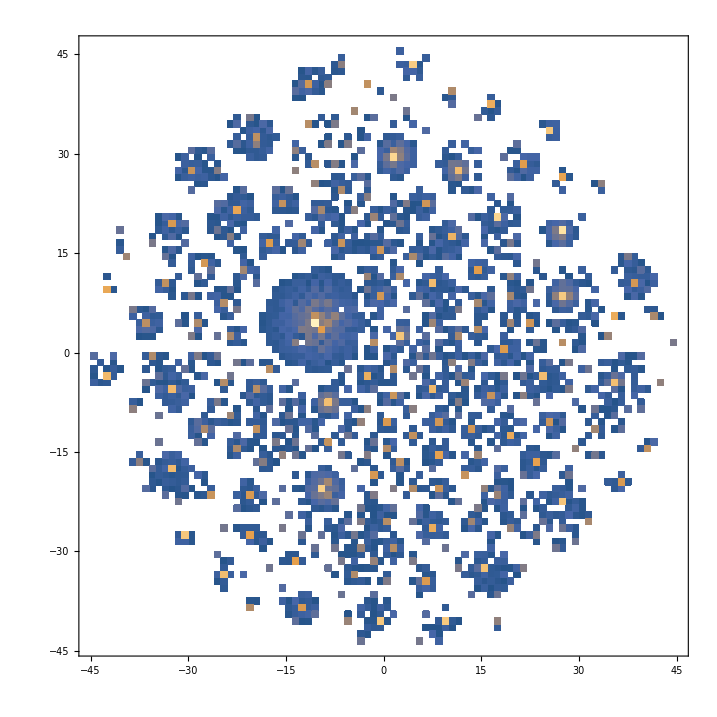

```mathematica
DensityHistogram[reducedNamespaceVectors,{1}]
```